```mathematica
(*3 Test functions*)
```

```mathematica
(*SPHERE FUNCTION*)
sphere[x_]:=Module[
{},Sum[(x[[i]])^2,{i,Length@x}]]
```

```mathematica
(*SUM OF DIFFERENT POWERS FUNCTION*)
```

```mathematica
SDP[x_]:=Module[{l=Length@x},Sum[Abs[x[[i]]]^(i+1),{i,l}]]
```

```mathematica
(*SUM SQUARES FUNCTION*)
```

```mathematica
SS[x_]:=Module[{l=Length@x},Sum[i*(x[[i]]^2),{i,l}]]
```

```mathematica
(*GA*)
```

```mathematica
GA[f_,dim_,generationNum_]:=Module[{},
G1=RandomReal[{-500,500},{50,dim}];


G={};

Solution={};


Do[
G1=Round[G1,0.001];
AppendTo[G,G1];

Solution1=Table[f[G1[[i]]],{i,50}];
AppendTo[Solution,Min@Solution1];

nextGeneration=TakeSmallest[Solution1,10];
nextGenerationX=G1[[Ordering[Solution1,10]]];
G1={};
Do[

(*Ranking Selection*)
parent1=RandomChoice[Table[i/((10+1)*10/2),{i,10}]->Reverse@nextGeneration];


parent2=RandomChoice[Table[i/((9+1)*9/2),{i,9}]->Reverse[ReplacePart[nextGeneration,First@First@Position[nextGeneration,parent1]->Nothing]]];

parents={parent1,parent2};


parentsX=nextGenerationX[[
Join[
Flatten@Position[
nextGeneration,parents[[1]]
],
Flatten@Position[
nextGeneration,parents[[2]]
]
]
]];
parentsX=Round[(parentsX+500)*1000];
parentsX=IntegerDigits[parentsX,10,7];
parentsX=IntegerDigits[parentsX,2,4];
momX=parentsX[[1]];
dadX=parentsX[[2]];
momX=Flatten@momX;
dadX=Flatten@dadX;
(*One-point crossover, exchange 1/dim length of parents' binary numbers*)

momXCross=Take[momX,(Length@momX)/dim];
momXOrig=Drop[momX,(Length@momX)/dim];
dadXCross=Take[dadX,(Length@dadX)/dim];
dadXOrig=Drop[dadX,(Length@dadX)/dim];
child1=Join[momXCross,dadXOrig];
child2=Join[dadXCross,momXOrig];
(*Random-Mutation*)
Do[
If[RandomReal[]<=0.01,If[child1[[i]]==0,child1[[i]]=1,child1[[i]]=0]],{i,Length@child1}];
Do[
If[RandomReal[]<=0.01,If[child2[[i]]==0,child2[[i]]=1,child2[[i]]=0]],{i,Length@child2}];
child1=Partition[child1,4];
child1=Partition[child1,7];
child2=Partition[Partition[child2,4],7];
child1=Table[Table[FromDigits[child1[[i]][[j]],2],{j,7}],{i,dim}];

child1=Table[FromDigits[child1[[i]]],{i,dim}];
child1=child1/1000-500//N;
Do[
If[child1[[i]]<-500,child1[[i]]=-500,If[child1[[i]]>500,child1[[i]]=500]],{i,Length@child1}];

child2=Table[Table[FromDigits[child2[[i]][[j]],2],{j,7}],{i,dim}];
child2=Table[FromDigits[child2[[i]]],{i,dim}];
child2=child2/1000-500//N;
Do[
If[child2[[i]]<-500,child2[[i]]=-500,If[child2[[i]]>500,child2[[i]]=500]],{i,Length@child2}];

AppendTo[G1,child1];
AppendTo[G1,child2]
,{k,20}];
G1=Join[G1,nextGenerationX]

,{a,generationNum}];
Return@Solution
]
```

```mathematica
(*Statistic for GA-sphere func in 5D*)
```

```mathematica
Solution11=ParallelTable[GA[sphere,5,150],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
gaSphere5d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{96855.3,60019.2,52933.9,39507.7,36350.3,28218.1,23938.,18605.,16342.1,13964.2,9783.76,8049.61,5652.2,4027.13,3400.02,2430.89,2236.06,1872.28,1658.81,1313.21,1193.82,1000.73,883.962,774.301,730.267,604.218,559.849,516.306,409.833,401.256,291.238,231.271,200.611,167.291,153.348,73.5949,72.5832,72.1107,69.3815,65.3774,32.8094,31.4727,30.1257,29.6997,25.9208,9.47825,7.96404,6.21635,4.15535,3.96839,3.37223,3.21366,2.25992,2.13842,1.73941,1.55636,0.761244,0.708293,0.690229,0.630054,0.507418,0.393269,0.389647,0.38942,0.373923,0.361295,0.273891,0.164184,0.15389,0.153241,0.14362,0.141952,0.138449,0.124038,0.123957,0.0323346,0.0280327,0.0114052,0.00886318,0.00791791,0.00786373,0.00642682,0.00641709,0.00555736,0.00548673,0.00520773,0.00278082,0.00275873,0.000525273,0.000506636,0.000420364,0.000413182,0.000409,0.000260636,0.000181182,0.000181182,0.000179818,0.000132545,0.000113818,0.000111,0.0000912727,0.0000911818,0.0000905455,0.0000553636,0.0000537273,0.0000531818,0.0000473636,0.0000382727,0.0000381818,0.0000381818,0.0000363636,0.0000272727,0.0000269091,0.0000264545,0.0000264545,0.0000261818,0.0000170909,0.000017,0.0000166364,0.0000107273,1.63636×10^-6,1.63636×10^-6,1.63636×10^-6,1.63636×10^-6,1.63636×10^-6,9.09091×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {91464.7,65867.5,60657.3,36648.6,36439.4,28050.2,22678.1,17656.5,15896.6,12559.1,10020.6,5389.45,4162.95,2973.17,2809.31,2369.17,2061.49,1590.66,1475.69,1106.55,1106.55,831.403,745.827,555.92,498.039,479.329,442.429,442.429,399.122,396.469,112.834,112.834,45.5776,27.9046,18.9937,18.9724,18.7424,18.4642,17.3616,13.6945,11.233,8.47453,6.94739,6.94739,6.37397,6.37352,6.367,2.09795,1.10459,0.606291,0.535826,0.486051,0.31419,0.31419,0.31331,0.31331,0.166254,0.166254,0.072616,0.070136,0.070136,0.062344,0.059656,0.059492,0.059372,0.059372,0.047456,0.019336,0.01691,0.016815,0.008974,0.008974,0.007022,0.007022,0.006135,0.006135,0.003553,0.002155,0.002155,0.002155,0.002115,0.001527,0.001486,0.001131,0.000371,0.000297,0.000239,0.000239,0.000157,0.000157,0.000157,0.000147,0.00011,0.000108,0.000108,0.000108,0.000102,0.000084,0.000084,0.000069,8.×10^-6,8.×10^-6,8.×10^-6,8.×10^-6,8.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {32610.9,27260.1,25379.1,20036.5,19576.3,14843.9,14538.4,11560.7,10018.5,9356.76,5926.91,6432.66,4129.34,3230.66,2730.17,1196.75,1259.07,1229.7,1139.7,821.129,791.382,618.045,625.43,535.531,550.092,533.646,525.049,476.068,380.944,379.099,378.419,321.624,323.315,275.585,280.1,151.679,152.118,152.318,150.934,141.704,70.4177,70.5131,69.6769,69.7793,61.7877,10.2144,8.83431,8.79683,6.74089,6.83629,5.9935,6.00352,3.64859,3.54995,3.38657,3.23005,1.18945,1.11673,1.12701,1.02824,0.944921,0.737377,0.738532,0.738621,0.732522,0.701338,0.478348,0.322319,0.320529,0.32058,0.322792,0.322978,0.324195,0.319904,0.319937,0.0543306,0.0546285,0.0199309,0.0146443,0.0138202,0.0137942,0.0138642,0.0138679,0.0117231,0.0117493,0.0117992,0.00737928,0.00738645,0.00072966,0.00074212,0.000625391,0.0006153,0.000617363,0.000330873,0.000222889,0.000222889,0.000223129,0.00019298,0.000150747,0.00014793,0.000135417,0.000135189,0.00013503,0.0000876302,0.0000832587,0.000083527,0.0000678193,0.0000487424,0.0000485795,0.0000485795,0.0000498182,0.0000451466,0.0000448006,0.0000448204,0.0000448204,0.0000449796,0.0000378932,0.0000379368,0.0000380927,0.0000349173,4.78064×10^-6,4.78064×10^-6,4.78064×10^-6,4.78064×10^-6,4.78064×10^-6,3.01511×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | 0. | 170737.

```mathematica
(*Statistic for GA-sphere func in 30D*)
```

```mathematica
Solution11=ParallelTable[GA[sphere,30,900],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
gaSphere30d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{1.68206×10^6,1.61499×10^6,1.54553×10^6,1.51822×10^6,1.46464×10^6,1.45728×10^6,1.43423×10^6,1.38106×10^6,1.33625×10^6,1.29025×10^6,1.25036×10^6,1.2266×10^6,1.19395×10^6,1.15829×10^6,1.1372×10^6,1.11465×10^6,1.08121×10^6,1.04576×10^6,1.02468×10^6,978954.,946180.,928322.,910116.,884932.,873874.,852345.,841805.,826848.,823287.,809098.,804451.,775698.,763918.,753887.,749235.,728518.,719054.,704521.,688025.,681950.,680154.,658127.,653963.,636069.,631975.,624737.,620787.,613371.,611356.,601953.,581234.,574507.,570912.,559955.,556298.,550292.,540137.,535667.,532047.,528033.,526646.,514196.,512308.,505558.,497877.,497144.,489518.,485633.,481690.,475060.,468976.,467942.,460098.,457387.,456503.,454301.,446458.,443809.,440777.,432528.,430180.,426395.,424854.,423964.,420420.,416402.,411675.,407560.,400411.,398489.,394848.,392179.,391086.,389556.,388305.,381499.,379797.,378391.,375470.,374631.,370913.,362680.,362518.,361207.,360722.,358173.,357028.,354684.,353056.,349155.,346761.,346437.,345455.,344588.,342070.,341451.,340717.,338448.,337048.,335952.,333415.,331704.,330507.,328687.,326544.,325128.,324308.,323191.,321503.,320923.,319439.,317970.,316368.,311747.,308914.,306139.,305933.,305089.,303010.,301394.,300185.,298271.,298221.,296902.,287651.,287441.,286493.,285490.,284123.,282977.,282675.,282525.,282116.,280939.,280357.,279446.,277452.,277146.,276427.,276129.,273699.,272806.,272154.,271365.,271168.,270556.,270111.,269758.,268848.,268160.,267727.,266575.,266003.,265162.,263966.,263051.,260818.,259450.,257577.,256978.,256878.,255634.,255237.,254282.,254051.,253975.,253389.,253208.,252338.,251391.,249782.,249705.,249303.,249064.,247857.,247801.,247569.,246821.,246800.,246562.,246562.,245899.,245705.,245390.,245296.,244678.,243547.,241927.,241725.,241431.,240507.,240123.,239851.,239494.,239071.,238277.,238110.,238006.,237799.,237728.,237398.,237155.,236973.,236935.,236761.,236475.,235189.,235092.,234579.,233657.,233626.,233263.,232924.,232879.,232757.,232482.,231141.,230635.,229843.,229269.,229233.,228914.,228577.,228568.,228568.,228543.,228528.,228394.,228152.,228093.,227618.,224873.,224118.,223967.,223749.,223553.,223464.,222744.,220905.,220739.,220685.,220667.,220474.,220110.,219569.,219559.,219335.,219035.,218926.,217773.,217766.,217305.,216319.,216303.,209620.,208697.,208651.,205728.,205569.,205569.,205556.,205504.,205455.,205369.,205249.,205096.,204498.,204412.,204021.,201777.,201589.,201383.,200525.,200061.,199977.,199977.,199619.,198886.,198830.,198808.,198358.,198266.,198155.,198055.,197344.,197125.,197123.,196611.,196324.,196301.,196192.,196091.,195781.,195567.,195417.,195397.,195374.,194808.,194739.,194679.,194473.,194423.,194294.,193947.,193927.,193847.,193813.,193461.,193461.,193289.,193235.,193190.,193179.,193161.,193069.,193036.,192907.,192756.,192750.,192559.,192518.,192440.,192440.,192440.,192273.,192234.,192196.,192175.,192064.,191979.,191964.,191923.,191864.,191674.,191560.,191231.,191226.,191106.,191010.,190997.,190738.,190738.,190738.,190542.,190431.,190353.,190285.,190273.,190229.,190115.,190092.,190088.,190009.,190002.,189999.,189984.,189984.,189889.,189889.,189852.,189697.,189697.,189697.,189624.,189597.,189301.,189243.,189243.,189132.,188990.,188975.,188936.,188823.,188823.,188823.,188778.,188710.,188656.,188623.,188583.,188577.,188382.,188274.,188209.,188192.,188184.,178776.,178726.,178709.,178694.,178666.,177882.,177847.,177804.,177772.,177760.,177753.,177652.,177646.,177627.,177570.,176798.,176790.,176759.,176747.,171834.,171804.,171733.,171547.,171543.,171534.,171526.,171444.,171444.,171411.,171399.,171393.,171388.,171358.,171275.,171275.,171179.,171166.,170796.,170750.,170730.,170730.,170718.,170714.,170621.,170621.,170538.,170538.,170522.,170483.,170458.,170416.,170410.,170388.,170346.,170192.,170186.,170186.,169618.,169609.,169569.,169531.,169499.,169496.,169429.,169312.,169259.,169259.,169259.,169170.,169160.,169113.,169106.,169106.,169106.,169061.,169031.,169002.,168982.,168982.,168980.,168980.,168858.,168766.,168746.,168731.,168720.,168712.,168703.,168703.,168652.,168645.,168625.,168593.,168581.,168544.,168519.,168518.,168475.,168367.,168363.,168333.,168326.,168281.,168253.,168197.,168164.,168140.,168129.,168084.,168084.,168084.,168084.,168056.,168056.,168016.,167845.,167845.,167845.,167845.,167725.,167719.,167714.,167702.,167657.,167643.,167620.,167598.,167590.,167529.,167529.,167495.,167495.,167481.,167418.,167414.,167372.,167334.,167281.,167280.,167269.,167263.,167263.,167242.,167240.,167227.,167214.,167162.,167110.,167083.,167073.,167060.,167060.,167060.,167044.,166981.,166951.,166933.,166931.,166922.,166915.,166912.,166837.,166791.,166784.,166784.,166766.,166741.,166697.,166660.,166658.,166656.,166656.,166653.,166653.,166643.,166557.,166557.,166553.,166553.,166536.,166531.,166529.,166494.,166494.,166431.,166425.,166371.,166361.,166346.,159258.,159258.,159257.,159240.,159240.,159191.,159153.,159086.,159076.,159075.,159055.,158607.,158596.,158594.,158593.,158593.,158554.,158485.,158474.,158474.,158474.,158470.,158470.,158462.,158419.,158372.,158350.,158350.,158334.,158323.,158322.,158286.,158209.,158208.,158202.,158202.,158202.,158199.,158199.,158179.,158179.,158151.,158144.,158122.,158122.,158122.,158121.,150826.,150826.,150809.,150798.,150731.,150726.,150726.,150726.,150715.,150712.,150712.,150708.,150675.,150673.,150673.,150673.,150654.,150632.,150625.,150604.,150372.,150372.,150188.,150163.,150161.,150122.,150119.,150111.,149623.,149623.,149593.,149593.,149593.,149580.,149529.,149529.,149529.,149529.,149526.,149526.,149515.,149498.,149495.,149464.,149445.,149439.,149435.,149425.,149408.,149408.,149402.,149367.,149362.,149362.,149362.,149362.,149139.,149132.,149099.,149098.,149094.,149094.,149081.,149081.,149074.,149074.,149072.,149033.,149013.,149003.,148999.,148994.,148994.,148987.,148987.,141790.,141789.,141788.,141759.,141757.,141757.,141739.,141736.,141736.,141725.,141692.,141046.,140987.,140977.,140917.,140915.,140911.,140911.,140907.,140900.,140900.,140881.,140881.,140881.,140877.,140876.,140875.,140872.,140867.,140861.,140860.,140858.,140821.,140790.,140781.,140734.,140732.,140725.,140698.,140698.,140684.,140684.,140674.,140674.,140672.,140667.,140621.,140620.,140620.,140576.,140569.,140560.,140560.,140560.,140560.,140556.,140556.,140541.,140533.,140529.,140528.,140507.,140504.,140504.,140496.,140496.,140493.,140474.,140458.,140431.,140425.,140423.,140407.,140397.,140394.,140272.,140272.,140260.,140256.,140256.,140256.,140256.,140251.,140245.,140243.,140227.,140226.,140226.,140226.,140222.,140216.,140202.,140202.,140201.,140193.,140189.,140187.,140187.,140187.,140177.,140177.,140157.,140157.,140154.,140154.,140144.,140140.,140140.,140137.,140136.,140136.,140134.,140134.,140128.,140124.,140114.,140112.,140110.,140110.,140074.,140074.,140073.,140071.,140070.,140068.,140068.,140032.,140032.,140031.,140024.,140019.,140018.,140017.,140016.,140016.,140016.,140016.,140014.,140014.,140013.,140010.,140004.,140004.,140002.,140002.,139997.,139989.,139979.,139965.,139965.,139953.,139946.,139924.,139924.,139897.,139890.,139888.,139886.,139886.,139886.,139883.,139883.,139880.,139880.,139880.,139876.,139876.,139876.,139872.,139872.,139872.,139872.,139872.,139866.,139856.,139846.,139840.,139840.,139838.,139837.,139835.,139835.,139834.} | {1.68196×10^6,1.64599×10^6,1.53164×10^6,1.53164×10^6,1.40208×10^6,1.39658×10^6,1.37833×10^6,1.37522×10^6,1.30981×10^6,1.30981×10^6,1.29526×10^6,1.29526×10^6,1.23585×10^6,1.22366×10^6,1.22341×10^6,1.14284×10^6,1.10919×10^6,1.05828×10^6,1.01439×10^6,1.0137×10^6,950146.,950146.,940789.,937499.,868359.,868359.,862372.,778092.,778092.,756226.,756226.,753889.,741941.,735746.,735746.,722212.,705776.,702088.,702088.,684084.,684084.,676520.,676520.,630456.,630249.,629963.,629963.,628150.,628150.,621865.,621865.,621865.,607837.,569636.,569494.,569494.,566185.,566185.,561874.,557553.,557553.,542656.,535384.,535384.,533516.,530027.,484563.,484563.,484563.,484563.,455044.,455044.,455044.,449080.,449080.,435821.,435202.,435202.,432573.,426698.,421928.,418973.,418973.,415114.,405905.,402676.,402676.,402676.,402676.,395648.,392978.,381802.,381802.,381802.,381802.,370356.,367480.,367480.,363747.,362322.,361251.,344258.,344258.,344245.,343765.,343765.,342779.,337663.,337663.,337663.,337663.,337663.,336877.,334676.,334676.,334676.,334676.,334676.,330588.,330588.,326984.,326984.,326984.,322676.,322676.,321343.,321343.,321343.,321343.,321343.,321343.,321062.,321062.,295950.,293339.,290135.,290135.,289094.,288700.,288700.,284720.,282415.,282257.,281841.,278889.,278889.,277958.,273713.,271754.,263000.,262998.,262998.,262998.,262998.,262998.,262998.,262998.,262998.,261146.,261146.,258943.,258943.,258943.,258943.,257836.,257836.,257836.,256819.,256819.,256819.,256819.,256819.,256819.,256819.,256084.,254921.,254921.,254921.,252766.,252766.,252766.,245299.,245299.,245299.,245299.,245299.,245299.,245299.,240322.,240322.,236821.,236821.,236821.,236821.,236821.,236821.,236821.,234878.,234878.,233224.,233224.,229144.,229144.,229144.,228891.,228766.,228766.,228766.,227442.,227277.,217655.,217655.,217655.,217655.,216022.,213453.,213453.,213453.,213453.,213453.,213453.,211453.,211453.,211453.,210136.,210136.,210136.,210136.,210136.,210136.,209788.,207308.,207308.,207308.,206226.,206226.,206226.,206226.,206226.,205436.,205436.,205436.,205436.,205436.,205436.,205170.,205170.,205170.,205132.,205132.,205132.,204611.,204611.,204611.,202220.,202220.,202220.,201728.,201728.,201728.,201728.,201728.,201728.,201728.,201728.,201728.,201728.,201728.,201728.,201728.,201654.,201654.,201654.,201575.,201575.,201544.,201351.,201351.,201351.,201351.,201351.,201351.,201351.,201351.,200702.,199443.,199443.,199443.,198928.,198928.,198928.,198928.,198918.,198918.,198918.,198918.,198918.,198918.,198918.,198918.,198918.,198398.,198398.,198398.,196985.,196985.,196985.,196985.,196985.,196985.,196985.,196985.,195340.,195340.,195340.,195340.,195340.,195340.,195340.,195340.,194855.,194810.,194728.,194718.,194718.,194609.,194609.,194124.,194124.,194124.,194124.,193942.,193942.,193942.,193901.,193901.,193800.,193800.,193800.,193800.,193597.,193597.,193597.,193597.,192691.,192636.,192325.,192325.,192325.,192325.,192325.,192325.,192325.,192052.,191947.,191947.,191947.,191785.,191785.,191785.,191709.,191709.,191709.,191709.,191637.,191637.,191608.,191608.,191608.,191328.,191159.,191159.,191159.,191159.,191159.,191159.,191159.,190799.,190799.,190799.,190317.,190317.,190317.,190253.,190253.,187577.,187564.,187564.,187564.,187564.,187564.,187564.,187564.,187564.,187564.,187564.,187466.,187466.,187466.,187466.,187466.,187466.,187466.,186958.,186958.,186958.,186352.,186352.,186352.,186352.,186343.,186343.,186343.,186088.,186088.,186088.,186088.,186088.,186088.,186088.,186088.,186088.,186088.,186088.,186088.,186088.,185933.,185933.,185933.,185887.,185887.,185887.,185887.,185887.,185544.,185544.,185544.,185544.,185258.,185258.,185258.,185258.,185119.,185119.,185119.,185119.,185119.,185119.,185119.,184830.,184830.,184830.,184830.,184658.,184658.,184658.,184644.,184644.,184411.,184411.,184411.,184411.,184411.,184411.,184411.,184411.,184411.,184305.,184305.,184305.,184305.,184305.,184305.,184305.,184305.,184305.,183792.,183792.,183792.,183792.,183579.,183579.,183503.,183503.,183503.,183503.,183503.,183503.,183475.,183389.,183389.,183324.,183324.,183324.,183324.,183324.,183324.,183324.,183324.,183324.,183214.,183207.,183196.,183051.,183051.,183051.,182876.,182876.,182876.,182876.,182876.,182876.,182876.,182755.,182755.,182755.,182755.,182754.,182750.,182750.,182750.,182750.,182750.,182750.,182750.,182750.,182750.,182750.,182750.,182750.,182750.,182750.,182750.,182750.,182750.,182750.,182750.,182750.,182750.,182750.,182750.,182750.,182750.,182750.,182750.,182653.,182653.,182653.,182653.,182653.,182653.,182653.,182653.,182653.,182653.,182653.,182653.,182653.,182653.,182653.,182628.,182628.,182628.,182628.,182628.,182628.,182628.,182425.,182425.,182425.,182425.,182425.,182425.,182197.,182197.,182197.,182197.,182197.,182197.,182197.,182197.,182197.,182197.,182197.,182197.,182197.,182195.,182195.,182195.,182195.,182128.,182128.,182128.,182128.,182128.,181439.,181439.,181439.,181439.,181439.,181439.,181439.,181439.,181439.,181439.,181439.,181439.,181439.,181439.,181427.,181427.,181324.,181324.,181324.,181324.,181324.,181324.,181324.,181324.,181324.,181324.,181324.,181324.,181324.,181202.,181202.,181202.,181202.,181202.,181202.,181202.,181202.,181202.,181202.,181202.,181202.,181202.,181182.,181182.,181182.,181182.,181182.,181021.,181021.,181021.,181021.,181021.,181021.,181021.,181021.,181021.,181021.,181021.,181021.,181007.,181007.,181007.,181004.,181004.,181004.,181004.,181004.,181004.,180995.,180995.,180995.,180995.,180995.,180995.,180926.,180926.,180926.,180926.,180921.,180921.,180921.,180921.,180921.,180921.,180921.,180921.,180921.,180921.,180921.,180921.,180919.,180919.,180919.,180901.,180878.,180878.,180878.,180848.,180848.,180848.,180848.,180848.,180848.,180848.,180848.,180655.,180655.,180655.,180655.,180655.,180655.,180655.,180655.,180655.,180651.,180651.,180626.,180626.,180626.,180626.,180626.,180626.,180607.,180607.,180604.,180604.,180604.,180604.,180601.,180601.,180601.,180601.,180587.,180587.,180587.,180587.,180524.,180524.,180524.,180524.,180524.,180524.,180524.,180524.,180524.,180524.,180524.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180506.,180491.,180491.,180479.,180476.,180476.,180476.,180475.,180475.,180475.,180471.,180468.,180468.,180468.,180468.,180468.,180468.,180468.,180468.,180464.,180464.,180464.,180464.,180464.,180464.,180464.,180449.,180449.,180449.,180449.,180449.,180449.,180449.,180449.,180449.,180449.,180446.,180446.,180446.,180442.,180442.,180442.,180442.,180442.,180442.,180442.,180442.,180438.,180438.,180438.,180438.,180438.,180438.,180438.,180438.,180438.,180438.,180438.,180438.,180438.,180438.,180438.,180438.,180438.,180438.,180438.,180438.,180438.,180438.,180438.,180438.,180435.,180435.,180435.,180435.,180435.,180420.,180420.,180404.,180404.,180404.,180404.,180404.,180404.,180404.,180398.,180398.,180394.,180394.,180394.,180394.,180394.,180394.,180394.,180394.,180394.,180394.,180388.,180388.,180388.,180388.,180388.,180388.,180388.,180388.,180388.,180388.,180388.,180388.,180388.,180388.,180380.,180380.,180380.,180380.,180380.} | {97279.4,120356.,102146.,116457.,118320.,112817.,126783.,143690.,134978.,182392.,179978.,200660.,179609.,186617.,176002.,166999.,162382.,160993.,157937.,155926.,163500.,171376.,157727.,164288.,169435.,164023.,165925.,171729.,167757.,172339.,172178.,148728.,162914.,154079.,151678.,155998.,153929.,166164.,172235.,168410.,169195.,146233.,148557.,141203.,145510.,140034.,140641.,141643.,139766.,140044.,137421.,134878.,134241.,136958.,138770.,139101.,134863.,133783.,132790.,131021.,132796.,138352.,138097.,139327.,147553.,147260.,145971.,146445.,147573.,145381.,149334.,148469.,149223.,150735.,150875.,150890.,149374.,147780.,151632.,145407.,145177.,146548.,146308.,147177.,145791.,147446.,142299.,144592.,144633.,144311.,142153.,142041.,142157.,141764.,141712.,139244.,139090.,138008.,134754.,134728.,134457.,141143.,141077.,140704.,140292.,138192.,138820.,139286.,140058.,136940.,135302.,135301.,135842.,135485.,136711.,136969.,136559.,135351.,136030.,136100.,135993.,134683.,134731.,134949.,134612.,134926.,134573.,133614.,135235.,134881.,135074.,133846.,135107.,136287.,134635.,133193.,133130.,132709.,131413.,131969.,132480.,132644.,132654.,131282.,131855.,131896.,131264.,131810.,130535.,130675.,130556.,130781.,130617.,132336.,132512.,132098.,131248.,131340.,130736.,130843.,133889.,134076.,135099.,135068.,135107.,135852.,135872.,135952.,135152.,135342.,135042.,136091.,135514.,135704.,134346.,133992.,133241.,131846.,132090.,132079.,132059.,132563.,132914.,132972.,132773.,132869.,133032.,133038.,133137.,132219.,130597.,130616.,131039.,131213.,131793.,131811.,132005.,131366.,131338.,131304.,131304.,131268.,131150.,131508.,131431.,131597.,132355.,130964.,130954.,131032.,131217.,131078.,130941.,131075.,131259.,131355.,131200.,131170.,130886.,130864.,130849.,130905.,130965.,131000.,131025.,130912.,129959.,130099.,130147.,129692.,129698.,129780.,129332.,129406.,129407.,129320.,127993.,128028.,128198.,128204.,128161.,128614.,128150.,128152.,128152.,128157.,128150.,128170.,128236.,128251.,128019.,125238.,124786.,125042.,125083.,125225.,125227.,124794.,123298.,123114.,123084.,123088.,122981.,123494.,123028.,123028.,123065.,122794.,122760.,122085.,122086.,122029.,121275.,121271.,118830.,117671.,117665.,116807.,116821.,116821.,116807.,116897.,116828.,116931.,116927.,116906.,116716.,116704.,116122.,115539.,115869.,115843.,115625.,115354.,115343.,115343.,115312.,115259.,115264.,115265.,115195.,115166.,114975.,114914.,114820.,115017.,115016.,114961.,115165.,115206.,115123.,115120.,115130.,115043.,115035.,115037.,115027.,114686.,114688.,114751.,114649.,114645.,114642.,114638.,114639.,114762.,114764.,114756.,114756.,114684.,114686.,114736.,114755.,114756.,114757.,114724.,114716.,114573.,114573.,114612.,114615.,114616.,114616.,114616.,114605.,114606.,114605.,114604.,114508.,114657.,114631.,114570.,114572.,114555.,114716.,114623.,114614.,114612.,114608.,114631.,114674.,114674.,114674.,115021.,115019.,114983.,115044.,115044.,115040.,114940.,114927.,114933.,114928.,114928.,114933.,114957.,114957.,114919.,114919.,114920.,114915.,114915.,114915.,114914.,114913.,114930.,114961.,114962.,115046.,114859.,114841.,114861.,114779.,114779.,114779.,114777.,114786.,114693.,114691.,114691.,114684.,114684.,114678.,114695.,114693.,114693.,104312.,104305.,104336.,104342.,104346.,103461.,103457.,103460.,103499.,103497.,103496.,103508.,103515.,103515.,103508.,103476.,103476.,103473.,103497.,105829.,105818.,105720.,105691.,105691.,105681.,105678.,105734.,105734.,105729.,105726.,105719.,105727.,105722.,105728.,105729.,105738.,105736.,105649.,105663.,105654.,105654.,105655.,105660.,105665.,105665.,105580.,105580.,105577.,105554.,105542.,105496.,105506.,105504.,105460.,105430.,105430.,105430.,105380.,105378.,105424.,105447.,105471.,105471.,105460.,105507.,105499.,105499.,105499.,105551.,105534.,105527.,105540.,105540.,105540.,105505.,105502.,105496.,105509.,105509.,105509.,105509.,105517.,105398.,105395.,105364.,105372.,105373.,105371.,105371.,105344.,105348.,105325.,105319.,105317.,105311.,105324.,105324.,105317.,105277.,105279.,105275.,105280.,105263.,105267.,105264.,105221.,105239.,105237.,105229.,105229.,105229.,105229.,105224.,105224.,105254.,105339.,105339.,105339.,105339.,105319.,105318.,105318.,105316.,105298.,105315.,105310.,105330.,105328.,105270.,105270.,105263.,105263.,105273.,105192.,105192.,105265.,105258.,105295.,105295.,105298.,105297.,105297.,105295.,105297.,105314.,105323.,105352.,105378.,105373.,105376.,105385.,105385.,105385.,105383.,105385.,105347.,105332.,105335.,105337.,105335.,105342.,105329.,105404.,105410.,105410.,105407.,105403.,105399.,105353.,105354.,105358.,105358.,105360.,105360.,105338.,105321.,105321.,105324.,105324.,105288.,105288.,105287.,105307.,105307.,105378.,105377.,105338.,105354.,105352.,106764.,106764.,106765.,106761.,106761.,106787.,106778.,106700.,106698.,106699.,106694.,106958.,106962.,106959.,106959.,106959.,106943.,106977.,106967.,106967.,106967.,106966.,106966.,106978.,106968.,106997.,107016.,107016.,106983.,106980.,106980.,107038.,107035.,107035.,107032.,107032.,107032.,107033.,107033.,107066.,107066.,107059.,107057.,107078.,107078.,107078.,107078.,93663.1,93663.1,93657.1,93664.1,93707.3,93705.5,93705.5,93705.5,93689.5,93688.2,93688.2,93682.6,93663.9,93663.5,93663.5,93663.4,93650.,93642.,93652.9,93658.1,93804.6,93804.3,93568.2,93531.2,93532.3,93551.8,93554.,93551.5,92813.7,92813.7,92801.9,92801.8,92801.8,92816.6,92830.2,92830.2,92831.6,92831.6,92828.2,92828.2,92814.5,92793.6,92795.9,92772.1,92754.9,92762.4,92761.1,92747.6,92722.,92722.,92722.8,92766.4,92764.4,92764.4,92764.4,92764.2,92463.,92465.,92479.,92478.7,92472.5,92472.5,92468.3,92468.3,92481.6,92481.6,92480.9,92509.4,92501.9,92507.8,92506.1,92513.4,92513.,92510.1,92510.1,92759.5,92759.3,92759.6,92774.,92775.1,92775.1,92803.7,92799.2,92799.2,92782.3,92797.5,93093.6,93126.2,93131.9,93158.7,93154.6,93152.8,93152.8,93151.1,93154.7,93154.7,93130.4,93130.4,93130.4,93131.6,93130.8,93129.9,93133.4,93131.4,93142.6,93142.4,93139.,93107.2,93146.3,93151.9,93177.,93178.2,93167.7,93182.8,93182.8,93175.8,93175.8,93182.4,93182.4,93178.8,93176.6,93202.8,93202.5,93202.5,93190.,93193.5,93179.8,93179.7,93179.7,93179.5,93186.2,93186.2,93174.5,93186.6,93189.2,93188.8,93200.5,93202.2,93202.2,93189.9,93190.7,93188.8,93220.7,93228.,93186.8,93183.9,93180.6,93195.6,93181.6,93176.8,93246.7,93246.8,93244.4,93243.7,93243.7,93243.7,93243.7,93247.,93256.3,93252.9,93236.4,93236.9,93236.9,93236.9,93235.3,93225.8,93238.3,93238.3,93237.6,93242.2,93236.5,93237.5,93237.5,93237.5,93239.1,93239.1,93207.7,93207.,93205.4,93205.4,93190.3,93192.6,93192.6,93189.1,93188.5,93188.6,93186.3,93186.3,93190.2,93191.4,93195.5,93194.4,93195.4,93195.7,93153.8,93153.8,93153.3,93153.2,93152.5,93149.8,93149.8,93170.2,93170.3,93172.8,93176.3,93179.3,93178.6,93180.7,93180.6,93180.6,93180.8,93180.8,93181.6,93181.5,93182.1,93187.7,93186.6,93186.6,93186.2,93186.4,93187.1,93182.9,93191.8,93196.5,93196.6,93204.6,93209.1,93175.8,93175.8,93180.7,93185.3,93186.9,93183.7,93183.6,93183.6,93184.7,93184.7,93183.4,93183.4,93183.2,93185.4,93185.6,93185.6,93187.9,93187.9,93187.9,93187.9,93187.9,93178.1,93170.6,93165.9,93157.2,93157.2,93155.,93156.1,93152.4,93152.4,93152.8} | 303.121 | 1.83295×10^6

```mathematica
(*Statistic for GA-SDP func in 5D*)
```

```mathematica
Solution11=ParallelTable[GA[SDP,5,150],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
gaSDP5d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{1.20106×10^11,6.9592×10^10,3.76895×10^10,2.3051×10^10,1.76969×10^10,5.25379×10^9,3.82324×10^9,3.02156×10^9,7.25175×10^8,4.51791×10^8,1.98996×10^8,1.82923×10^8,1.49651×10^8,6.16316×10^7,5.99933×10^7,5.89941×10^7,5.17992×10^7,4.98529×10^7,3.85297×10^7,3.77608×10^7,3.63942×10^7,2.86591×10^7,2.84633×10^7,2.80751×10^7,2.80529×10^7,2.79472×10^7,2.79247×10^7,2.78881×10^7,2.78854×10^7,2.78835×10^7,2.78821×10^7,2.7879×10^7,2.78737×10^7,2.7872×10^7,2.78706×10^7,2.78705×10^7,2.78701×10^7,2.73332×10^7,1.65968×10^7,1.65967×10^7,1.65719×10^7,1.65054×10^7,1.65054×10^7,1.65054×10^7,1.65053×10^7,1.65053×10^7,1.65053×10^7,1.65053×10^7,1.65053×10^7,1.65053×10^7,1.65053×10^7,1.64907×10^7,1.64832×10^7,1.64831×10^7,1.64831×10^7,1.64831×10^7,1.64803×10^7,1.62787×10^7,1.37639×10^7,1.31992×10^7,1.29802×10^7,1.27698×10^7,8.68157×10^6,8.65551×10^6,8.65551×10^6,6.62751×10^6,6.61212×10^6,6.61212×10^6,5.19537×10^6,5.19537×10^6,5.19533×10^6,4.94248×10^6,4.94248×10^6,4.94242×10^6,4.91872×10^6,4.91872×10^6,4.9184×10^6,4.9184×10^6,4.91839×10^6,4.91839×10^6,4.91838×10^6,4.91837×10^6,4.91837×10^6,4.91825×10^6,4.91825×10^6,4.91752×10^6,4.91752×10^6,4.91752×10^6,4.91751×10^6,4.91747×10^6,4.91747×10^6,4.91747×10^6,4.91729×10^6,2.55365×10^6,2.55364×10^6,2.55364×10^6,2.50927×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6,2.46273×10^6} | {3.97892×10^10,2.76508×10^10,1.51289×10^10,5.18437×10^9,3.8702×10^9,1.53666×10^9,1.01789×10^9,3.20945×10^8,1.63108×10^8,1.59072×10^8,4.09183×10^7,4.09183×10^7,4.09183×10^7,2.73888×10^7,2.73888×10^7,2.72307×10^7,2.72272×10^7,2.72185×10^7,3.92712×10^6,3.89727×10^6,3.43917×10^6,2.09707×10^6,2.05468×10^6,251197.,251197.,137724.,131460.,48542.4,36870.6,36448.2,31325.9,28750.6,14821.8,14699.7,4226.05,4226.,4223.97,4176.05,451.857,451.833,448.524,22.46,20.9513,17.0582,17.0582,17.027,17.027,2.51507,2.51507,2.15974,2.05647,1.00027,1.00027,0.260246,0.0334548,0.0334548,0.0334548,0.0278071,0.0127724,0.0127724,0.0127659,0.0127659,0.00141343,0.00141343,0.00141343,0.000597335,0.000597335,0.000524812,0.000461145,0.000247537,0.0000751584,0.0000704917,0.0000703334,0.0000703334,0.0000703334,0.0000701042,0.0000646483,0.0000235861,0.0000235861,0.0000235861,0.0000164985,0.0000124985,0.0000124985,0.0000123267,0.0000123267,0.0000103319,0.0000103319,3.35081×10^-6,3.35081×10^-6,3.35081×10^-6,3.35081×10^-6,5.51938×10^-8,5.51938×10^-8,5.51938×10^-8,8.60182×10^-9,8.06502×10^-9,8.06502×10^-9,1.6×10^-11,8.55354×10^-12,7.52954×10^-12,7.52954×10^-12,7.52954×10^-12,7.52954×10^-12,7.52954×10^-12,1.243×10^-12,1.243×10^-12,1.243×10^-12,1.243×10^-12,1.243×10^-12,1.243×10^-12,1.243×10^-12,1.243×10^-12,1.243×10^-12,1.243×10^-12,1.243×10^-12,1.243×10^-12,1.243×10^-12,1.243×10^-12,1.001×10^-12,1.001×10^-12,1.001×10^-12,1.001×10^-12,2.43×10^-13,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {1.58664×10^11,8.16159×10^10,4.96038×10^10,3.31569×10^10,3.28193×10^10,1.05982×10^10,6.94106×10^9,6.87413×10^9,1.01218×10^9,7.03081×10^8,4.31132×10^8,4.32336×10^8,3.30854×10^8,7.32657×10^7,7.25799×10^7,7.28939×10^7,5.93333×10^7,5.81499×10^7,5.34409×10^7,5.24384×10^7,5.11458×10^7,4.91151×10^7,4.90315×10^7,4.92585×10^7,4.9268×10^7,4.93249×10^7,4.93278×10^7,4.93022×10^7,4.93035×10^7,4.93046×10^7,4.93052×10^7,4.93055×10^7,4.93065×10^7,4.93065×10^7,4.93073×10^7,4.93072×10^7,4.93067×10^7,4.8163×10^7,3.76857×10^7,3.76857×10^7,3.76969×10^7,3.77275×10^7,3.77275×10^7,3.77275×10^7,3.77275×10^7,3.77275×10^7,3.77275×10^7,3.77275×10^7,3.77275×10^7,3.77275×10^7,3.77275×10^7,3.77344×10^7,3.7738×10^7,3.7738×10^7,3.7738×10^7,3.7738×10^7,3.77294×10^7,3.76604×10^7,2.97674×10^7,2.80309×10^7,2.7362×10^7,2.67224×10^7,1.53327×10^7,1.52715×10^7,1.52715×10^7,1.15418×10^7,1.15239×10^7,1.15239×10^7,1.08213×10^7,1.08213×10^7,1.08213×10^7,1.09061×10^7,1.09061×10^7,1.09061×10^7,1.09173×10^7,1.09173×10^7,1.09175×10^7,1.09175×10^7,1.09175×10^7,1.09175×10^7,1.09175×10^7,1.09175×10^7,1.09175×10^7,1.09176×10^7,1.09176×10^7,1.09179×10^7,1.09179×10^7,1.09179×10^7,1.09179×10^7,1.09179×10^7,1.09179×10^7,1.09179×10^7,1.0918×10^7,8.11342×10^6,8.11342×10^6,8.11342×10^6,8.1241×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6,8.13814×10^6} | 0. | 5.19386×10^11

```mathematica
(*Statistic for GA-SDP func in 30D*)
```

```mathematica
Solution11=ParallelTable[GA[SDP,30,900],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
gaSDP30d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{2.12104×10^70,6.38653×10^69,2.4506×10^69,2.44401×10^69,2.44206×10^69,1.96178×10^69,1.65111×10^69,1.64595×10^69,1.64444×10^69,1.63307×10^69,1.63021×10^69,1.37218×10^69,3.68103×10^68,3.6543×10^68,3.6543×10^68,2.55609×10^68,2.5544×10^68,2.52898×10^68,2.14658×10^68,2.12296×10^68,2.12177×10^68,2.12177×10^68,2.12019×10^68,2.11785×10^68,2.10201×10^68,2.10201×10^68,2.10182×10^68,2.08642×10^68,2.08619×10^68,2.08391×10^68,2.08257×10^68,2.08184×10^68,2.08184×10^68,2.08029×10^68,2.08029×10^68,2.08029×10^68,2.08019×10^68,2.08019×10^68,2.08018×10^68,2.07989×10^68,2.07989×10^68,2.07989×10^68,2.07989×10^68,2.07989×10^68,2.07989×10^68,2.07989×10^68,2.07989×10^68,2.07989×10^68,2.07989×10^68,2.07989×10^68,2.07989×10^68,2.07989×10^68,2.07989×10^68,2.07989×10^68,2.07989×10^68,2.07989×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07983×10^68,2.07978×10^68,2.07978×10^68,2.07978×10^68,2.07978×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07975×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.07973×10^68,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,2.31849×10^63,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60,7.70262×10^60} | {7.94756×10^68,6.41477×10^66,8.74453×10^65,1.71849×10^65,1.39578×10^65,1.20186×10^65,3.46137×10^64,3.04536×10^64,3.0236×10^64,6.66948×10^62,6.66791×10^62,4.97205×10^62,1.71495×10^62,1.35982×10^62,1.35981×10^62,1.22201×10^62,1.22201×10^62,1.19216×10^62,1.1921×10^62,1.1921×10^62,1.03269×10^62,1.03269×10^62,1.00749×10^62,8.78974×10^61,8.78974×10^61,2.64238×10^60,9.41083×10^59,6.31171×10^59,6.14762×10^59,6.05698×10^59,3.41258×10^59,3.38874×10^59,3.2474×10^59,3.00806×10^59,3.0009×10^59,3.0009×10^59,2.98531×10^59,2.91811×10^59,2.9181×10^59,2.89536×10^59,2.85137×10^59,2.84078×10^59,2.84078×10^59,2.83739×10^59,2.83739×10^59,2.83739×10^59,2.83654×10^59,2.8365×10^59,2.83581×10^59,2.8358×10^59,2.8358×10^59,2.83559×10^59,2.83558×10^59,2.83558×10^59,2.83558×10^59,2.83558×10^59,2.83555×10^59,2.83555×10^59,2.83555×10^59,2.83555×10^59,2.83555×10^59,2.83374×10^59,2.83374×10^59,2.83374×10^59,2.83374×10^59,2.83374×10^59,2.83374×10^59,2.83374×10^59,2.83372×10^59,2.83372×10^59,2.83372×10^59,2.83372×10^59,2.83371×10^59,2.83371×10^59,2.83371×10^59,2.83371×10^59,2.83371×10^59,2.83371×10^59,2.83371×10^59,2.83371×10^59,2.83371×10^59,2.83371×10^59,2.83371×10^59,2.83371×10^59,2.83371×10^59,2.83371×10^59,2.83371×10^59,2.83371×10^59,2.83371×10^59,2.83371×10^59,2.83371×10^59,9.41432×10^56,9.41432×10^56,9.41432×10^56,9.41432×10^56,8.64939×10^55,8.64939×10^55,3.21273×10^54,3.21273×10^54,3.21273×10^54,3.18517×10^54,3.18517×10^54,3.14462×10^54,3.14462×10^54,3.14232×10^54,3.14232×10^54,3.14232×10^54,3.14232×10^54,3.14232×10^54,3.14232×10^54,3.14232×10^54,3.14232×10^54,3.14232×10^54,3.14218×10^54,3.14048×10^54,3.14048×10^54,3.14047×10^54,3.13817×10^54,3.13813×10^54,3.13813×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,3.13811×10^54,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,1.04604×10^52,9.75203×10^51,1.41035×10^49,1.41035×10^49,1.49656×10^46,1.49656×10^46,1.49656×10^46,3.88713×10^44,3.88713×10^44,3.88713×10^44,3.88713×10^44,3.88713×10^44,3.88713×10^44,3.88713×10^44,3.88713×10^44,3.88713×10^44,3.88713×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88712×10^44,3.88352×10^44,3.88352×10^44,3.88352×10^44,3.88352×10^44,3.88352×10^44,3.88352×10^44,3.88352×10^44,3.88352×10^44,3.88352×10^44,3.88352×10^44,3.88352×10^44,3.88352×10^44,3.88352×10^44,3.88352×10^44,3.88352×10^44,3.88352×10^44,3.88352×10^44,3.88352×10^44,3.88352×10^44,3.88352×10^44,3.87421×10^44,3.87421×10^44,3.87421×10^44,3.87421×10^44,3.87421×10^44,3.87421×10^44,3.87421×10^44,3.87421×10^44,3.87421×10^44,3.87421×10^44,3.87421×10^44,3.87421×10^44,3.87421×10^44,3.87421×10^44,3.87421×10^44,3.87421×10^44,3.87421×10^44,3.87421×10^44,3.87421×10^44,3.87421×10^44,3.87421×10^44,3.8742×10^44,3.8742×10^44,3.8742×10^44,3.8742×10^44,3.8742×10^44,3.8742×10^44,3.8742×10^44,3.8742×10^44,3.8742×10^44,3.8742×10^44,3.8742×10^44,3.8742×10^44,3.8742×10^44,3.13926×10^44,3.13926×10^44,2.38175×10^44,7.59096×10^43,5.86691×10^43,5.86691×10^43,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.29142×10^42,1.2914×10^42,1.2914×10^42,1.2914×10^42,1.2914×10^42,1.2914×10^42,1.2914×10^42,1.2914×10^42,1.2914×10^42,1.2914×10^42,1.2914×10^42,1.2914×10^42,1.2914×10^42,1.2914×10^42,1.2914×10^42,1.2914×10^42,1.2914×10^42,1.2914×10^42,1.2914×10^42,1.2914×10^42,1.2914×10^42,1.2914×10^42,1.2914×10^42,1.2914×10^42,1.2914×10^42,1.2914×10^42,5.40388×10^39,5.4015×10^39,5.18312×10^39,5.18312×10^39,5.18312×10^39,4.89308×10^39,4.89308×10^39,4.89308×10^39,4.89308×10^39,4.89308×10^39,4.89307×10^39,4.89297×10^39,4.89296×10^39,4.89296×10^39,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37,1.43489×10^37} | {5.5718×10^70,2.01264×10^70,7.66085×10^69,7.66238×10^69,7.66299×10^69,6.48037×10^69,5.45067×10^69,5.45235×10^69,5.45285×10^69,5.41517×10^69,5.4058×10^69,4.55072×10^69,1.22056×10^69,1.21173×10^69,1.21173×10^69,8.47544×10^68,8.47117×10^68,8.38685×10^68,7.11858×10^68,7.04029×10^68,7.03634×10^68,7.03634×10^68,7.03111×10^68,7.02335×10^68,6.97085×10^68,6.97085×10^68,6.9702×10^68,6.91912×10^68,6.91839×10^68,6.9108×10^68,6.90638×10^68,6.90395×10^68,6.90395×10^68,6.8988×10^68,6.8988×10^68,6.8988×10^68,6.89846×10^68,6.89846×10^68,6.89846×10^68,6.89785×10^68,6.89784×10^68,6.89784×10^68,6.89784×10^68,6.89784×10^68,6.89784×10^68,6.89784×10^68,6.89784×10^68,6.89784×10^68,6.89784×10^68,6.89784×10^68,6.89784×10^68,6.89784×10^68,6.89784×10^68,6.89784×10^68,6.89784×10^68,6.89784×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89766×10^68,6.89767×10^68,6.89767×10^68,6.89767×10^68,6.89767×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.89768×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,6.8976×10^68,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,7.6615×10^63,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61,2.55467×10^61} | 7.85815×10^24 | 1.87274×10^71

```mathematica
(*Statistic for GA-SS func in 5D*)
```

```mathematica
Solution11=ParallelTable[GA[SS,5,150],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
gaSS5d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{335510.,185713.,154745.,124023.,110654.,100671.,82577.7,61939.4,54177.8,50137.7,40863.5,33761.7,27125.8,22457.7,18379.6,15308.3,13842.2,13289.2,10196.6,9010.49,8752.19,8127.36,7766.45,7466.63,6712.35,2831.02,2655.59,2529.27,2203.12,1726.97,1603.91,1430.12,1417.47,936.588,913.57,168.13,118.583,95.8995,72.2806,64.0203,56.4658,49.269,48.6739,24.0057,15.5078,14.4751,14.0748,13.4004,12.7033,9.43155,8.57106,7.39791,6.0993,5.80697,4.78922,4.37342,3.14994,3.14731,2.52699,2.46093,2.36256,1.2295,1.20592,0.799115,0.796464,0.751657,0.381209,0.362072,0.34802,0.334223,0.069529,0.041783,0.0261865,0.0205302,0.020144,0.019463,0.0193925,0.0178168,0.0173735,0.0134245,0.0133408,0.0121954,0.0121568,0.0118441,0.00297136,0.00286545,0.00269227,0.002521,0.00234364,0.00164255,0.001429,0.00121682,0.001135,0.00112155,0.00110173,0.00107264,0.00107118,0.00102918,0.000870273,0.000870273,0.000143727,0.000113636,0.000113455,0.000095,0.0000945455,0.0000932727,0.0000901818,0.0000901818,0.0000727273,0.0000472727,0.0000385455,0.0000356364,0.0000352727,0.0000170909,0.0000127273,0.0000127273,0.0000125455,0.0000121818,0.0000117273,0.0000117273,0.0000117273,0.0000117273,5.54545×10^-6,5.54545×10^-6,5.09091×10^-6,4.63636×10^-6,4.63636×10^-6,4.63636×10^-6,4.63636×10^-6,2.72727×10^-7,2.72727×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {337398.,195647.,166542.,123352.,104039.,87238.,80346.9,41531.2,41531.1,34277.2,32680.9,26317.5,21259.5,15514.4,14379.6,11887.,10587.2,9931.1,7927.58,4716.39,4715.73,3032.65,2889.66,2889.58,2735.59,1269.36,1125.58,1062.2,1061.01,689.798,455.192,285.898,282.701,249.965,117.249,79.6379,79.6379,31.3934,23.8491,23.7366,17.1254,17.1254,16.5062,9.82465,9.19204,7.75545,5.25623,5.25623,5.21487,5.21487,4.76214,4.16687,2.50763,2.5073,2.41963,0.733454,0.715541,0.707621,0.696821,0.476259,0.469491,0.212671,0.212671,0.212671,0.212671,0.150519,0.12246,0.111843,0.111843,0.039296,0.032409,0.013053,0.005817,0.005325,0.005325,0.00246,0.00246,0.00246,0.002396,0.002396,0.002396,0.000502,0.000396,0.000396,0.000396,0.000229,0.000229,0.000204,0.000204,0.000204,0.000204,0.000204,0.000204,0.000204,0.0002,0.0002,0.0002,0.0002,0.00005,0.00005,0.00005,0.00005,0.00005,0.000025,0.000025,0.000025,0.00002,0.00002,0.00002,5.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {113853.,89946.3,73327.7,62852.3,68741.2,61312.1,50188.2,46535.6,40241.3,39526.6,30544.5,26457.9,22058.2,16754.9,13431.4,14101.7,13865.1,14002.2,14272.9,14335.7,14287.8,14090.5,14080.8,14101.9,11903.7,3022.49,3007.38,2845.81,2756.13,2540.72,2565.71,2397.87,2400.68,1915.09,1921.78,239.033,121.038,121.24,90.7892,82.1443,80.0207,75.6275,75.2229,35.5252,19.5418,19.4345,19.5733,19.4697,18.2228,12.3532,10.8009,10.2114,7.92773,7.87093,5.97007,5.94754,4.24375,4.24143,3.87174,3.88757,3.85744,1.855,1.86601,1.43482,1.43555,1.45012,0.9166,0.920364,0.920446,0.924312,0.104365,0.0487015,0.0368296,0.0323691,0.0323501,0.0324482,0.0322967,0.0324197,0.0325916,0.0301748,0.0301589,0.0298068,0.0298236,0.0293519,0.0045619,0.00438162,0.00400558,0.00398091,0.00393147,0.0033033,0.00276949,0.00279758,0.0027962,0.0027898,0.00279729,0.00280413,0.0028047,0.00281479,0.00258709,0.00258709,0.000208872,0.00020045,0.00020041,0.000198993,0.000199052,0.000199185,0.000195093,0.000195093,0.000141086,0.0000753739,0.000074207,0.000074598,0.0000743964,0.0000257311,0.0000239754,0.0000239754,0.000023492,0.0000236678,0.0000237196,0.0000237196,0.0000237196,0.0000237196,0.0000142293,0.0000142293,0.000014328,0.0000144102,0.0000144102,0.0000144102,0.0000144102,9.04534×10^-7,9.04534×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | 0. | 518971.

```mathematica
(*Statistic for GA-SS func in 30D*)
```

```mathematica
Solution11=ParallelTable[GA[SS,30,900],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
gaSS30d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{2.52804×10^7,2.44729×10^7,2.28879×10^7,2.20295×10^7,2.16385×10^7,2.09834×10^7,2.04373×10^7,1.9959×10^7,1.954×10^7,1.90421×10^7,1.86576×10^7,1.77247×10^7,1.74122×10^7,1.70756×10^7,1.64147×10^7,1.59733×10^7,1.54755×10^7,1.52561×10^7,1.48468×10^7,1.46972×10^7,1.4556×10^7,1.41685×10^7,1.40657×10^7,1.38476×10^7,1.3779×10^7,1.33287×10^7,1.30415×10^7,1.29195×10^7,1.27872×10^7,1.25925×10^7,1.22414×10^7,1.20133×10^7,1.19361×10^7,1.18345×10^7,1.16167×10^7,1.14714×10^7,1.13871×10^7,1.1256×10^7,1.11858×10^7,1.10221×10^7,1.09114×10^7,1.06626×10^7,1.05448×10^7,1.03939×10^7,1.03574×10^7,1.02323×10^7,1.0126×10^7,1.00524×10^7,9.91618×10^6,9.85755×10^6,9.73878×10^6,9.66605×10^6,9.61083×10^6,9.54021×10^6,9.44804×10^6,9.29956×10^6,9.23431×10^6,9.19498×10^6,9.14426×10^6,9.06913×10^6,8.98476×10^6,8.94054×10^6,8.88206×10^6,8.8723×10^6,8.79603×10^6,8.70312×10^6,8.60853×10^6,8.54338×10^6,8.50102×10^6,8.47939×10^6,8.43405×10^6,8.38017×10^6,8.30862×10^6,8.2714×10^6,8.07649×10^6,8.06868×10^6,7.75469×10^6,7.72231×10^6,7.64773×10^6,7.63592×10^6,7.5622×10^6,7.55225×10^6,7.44654×10^6,7.44057×10^6,7.39081×10^6,7.34488×10^6,7.28397×10^6,7.25973×10^6,7.1884×10^6,7.18177×10^6,7.15647×10^6,7.12112×10^6,7.11181×10^6,7.08802×10^6,7.06438×10^6,6.9412×10^6,6.89751×10^6,6.87097×10^6,6.86244×10^6,6.84062×10^6,6.80417×10^6,6.76309×10^6,6.71794×10^6,6.70399×10^6,6.68224×10^6,6.67779×10^6,6.61042×10^6,6.56865×10^6,6.5059×10^6,6.49004×10^6,6.46452×10^6,6.45213×10^6,6.34887×10^6,6.33519×10^6,6.25651×10^6,6.23608×10^6,6.21484×10^6,6.19386×10^6,6.19323×10^6,6.17692×10^6,6.16387×10^6,6.15879×10^6,6.13685×10^6,6.12118×10^6,6.09943×10^6,6.09245×10^6,6.07827×10^6,6.04201×10^6,5.9319×10^6,5.92108×10^6,5.91336×10^6,5.89575×10^6,5.88027×10^6,5.85935×10^6,5.79999×10^6,5.77025×10^6,5.67778×10^6,5.64933×10^6,5.63877×10^6,5.6023×10^6,5.58515×10^6,5.53045×10^6,5.49832×10^6,5.48878×10^6,5.47086×10^6,5.41671×10^6,5.40926×10^6,5.39695×10^6,5.36236×10^6,5.33513×10^6,5.27216×10^6,5.26112×10^6,5.25157×10^6,5.24803×10^6,5.19551×10^6,5.19543×10^6,5.19255×10^6,5.18445×10^6,5.17528×10^6,5.15338×10^6,5.00575×10^6,4.9042×10^6,4.89747×10^6,4.83645×10^6,4.83401×10^6,4.826×10^6,4.8138×10^6,4.81253×10^6,4.80716×10^6,4.7892×10^6,4.77602×10^6,4.76179×10^6,4.74568×10^6,4.73276×10^6,4.71764×10^6,4.71522×10^6,4.69149×10^6,4.68199×10^6,4.67096×10^6,4.66695×10^6,4.65852×10^6,4.65774×10^6,4.65543×10^6,4.64646×10^6,4.62248×10^6,4.61444×10^6,4.61198×10^6,4.59905×10^6,4.56952×10^6,4.54338×10^6,4.54084×10^6,4.53606×10^6,4.5344×10^6,4.53172×10^6,4.52403×10^6,4.52352×10^6,4.52059×10^6,4.50037×10^6,4.42989×10^6,4.4191×10^6,4.41757×10^6,4.4165×10^6,4.41285×10^6,4.40085×10^6,4.39847×10^6,4.35451×10^6,4.33356×10^6,4.33356×10^6,4.33099×10^6,4.32315×10^6,4.31809×10^6,4.31373×10^6,4.30884×10^6,4.30622×10^6,4.2951×10^6,4.29391×10^6,4.28198×10^6,4.27758×10^6,4.27355×10^6,4.2694×10^6,4.26035×10^6,4.25819×10^6,4.24388×10^6,4.23878×10^6,4.23089×10^6,4.23019×10^6,4.22454×10^6,4.21884×10^6,4.21879×10^6,4.21564×10^6,4.20793×10^6,4.20732×10^6,4.20416×10^6,4.19561×10^6,4.19194×10^6,4.19173×10^6,4.18876×10^6,4.18642×10^6,4.18637×10^6,4.18618×10^6,4.18382×10^6,4.16241×10^6,4.14761×10^6,4.14518×10^6,4.14386×10^6,4.14384×10^6,4.14137×10^6,4.14084×10^6,4.10647×10^6,4.10587×10^6,4.10516×10^6,4.10229×10^6,4.08815×10^6,4.08101×10^6,4.07966×10^6,4.07932×10^6,4.0756×10^6,4.06382×10^6,4.05829×10^6,4.05767×10^6,4.05721×10^6,4.05114×10^6,4.05082×10^6,4.05032×10^6,4.04884×10^6,4.0467×10^6,4.04249×10^6,4.0403×10^6,4.03869×10^6,4.03455×10^6,4.02908×10^6,4.02676×10^6,4.02661×10^6,4.02112×10^6,4.01621×10^6,4.01493×10^6,4.01393×10^6,4.01207×10^6,4.00852×10^6,4.00655×10^6,4.00494×10^6,4.00494×10^6,3.98383×10^6,3.98078×10^6,3.97499×10^6,3.97377×10^6,3.97273×10^6,3.97188×10^6,3.97184×10^6,3.97044×10^6,3.96942×10^6,3.9669×10^6,3.96615×10^6,3.96491×10^6,3.96414×10^6,3.96396×10^6,3.96111×10^6,3.95834×10^6,3.95806×10^6,3.95643×10^6,3.91567×10^6,3.91554×10^6,3.91553×10^6,3.91043×10^6,3.90942×10^6,3.9077×10^6,3.90589×10^6,3.90466×10^6,3.90273×10^6,3.89172×10^6,3.87688×10^6,3.8321×10^6,3.83125×10^6,3.83083×10^6,3.82744×10^6,3.8267×10^6,3.82253×10^6,3.82154×10^6,3.81742×10^6,3.81742×10^6,3.81713×10^6,3.81657×10^6,3.81562×10^6,3.81406×10^6,3.81405×10^6,3.81027×10^6,3.80743×10^6,3.80505×10^6,3.80471×10^6,3.80406×10^6,3.8036×10^6,3.80336×10^6,3.80243×10^6,3.80152×10^6,3.80065×10^6,3.79971×10^6,3.79922×10^6,3.79874×10^6,3.79874×10^6,3.79861×10^6,3.79714×10^6,3.79498×10^6,3.79498×10^6,3.79062×10^6,3.79062×10^6,3.7885×10^6,3.78818×10^6,3.78818×10^6,3.78618×10^6,3.78613×10^6,3.7826×10^6,3.7818×10^6,3.78161×10^6,3.7796×10^6,3.77897×10^6,3.7726×10^6,3.77198×10^6,3.7715×10^6,3.76968×10^6,3.76322×10^6,3.76233×10^6,3.76233×10^6,3.76233×10^6,3.76121×10^6,3.75752×10^6,3.75637×10^6,3.7563×10^6,3.72142×10^6,3.72142×10^6,3.70673×10^6,3.70673×10^6,3.70673×10^6,3.7066×10^6,3.7066×10^6,3.69894×10^6,3.66579×10^6,3.66478×10^6,3.66036×10^6,3.65966×10^6,3.65877×10^6,3.64726×10^6,3.63478×10^6,3.63476×10^6,3.63459×10^6,3.63177×10^6,3.63074×10^6,3.62919×10^6,3.62684×10^6,3.62481×10^6,3.62289×10^6,3.62285×10^6,3.61414×10^6,3.61339×10^6,3.61266×10^6,3.60853×10^6,3.60783×10^6,3.60773×10^6,3.60398×10^6,3.60189×10^6,3.60184×10^6,3.60184×10^6,3.60103×10^6,3.60069×10^6,3.60026×10^6,3.59826×10^6,3.59819×10^6,3.5568×10^6,3.55225×10^6,3.54955×10^6,3.54934×10^6,3.53067×10^6,3.52976×10^6,3.52893×10^6,3.52893×10^6,3.51742×10^6,3.51654×10^6,3.51294×10^6,3.51031×10^6,3.50869×10^6,3.5085×10^6,3.5078×10^6,3.5077×10^6,3.50702×10^6,3.50653×10^6,3.37389×10^6,3.3583×10^6,3.358×10^6,3.3571×10^6,3.35666×10^6,3.35503×10^6,3.35501×10^6,3.21746×10^6,3.21636×10^6,3.21622×10^6,3.21526×10^6,3.21485×10^6,3.21421×10^6,3.21417×10^6,3.21408×10^6,3.21393×10^6,3.19993×10^6,3.19758×10^6,3.19638×10^6,3.19598×10^6,3.19363×10^6,3.19303×10^6,3.18829×10^6,3.18828×10^6,3.18808×10^6,3.18808×10^6,3.18794×10^6,3.18725×10^6,3.18725×10^6,3.18493×10^6,3.1831×10^6,3.18302×10^6,3.17872×10^6,3.17812×10^6,3.1713×10^6,3.1698×10^6,3.13729×10^6,3.13673×10^6,3.13656×10^6,3.13635×10^6,3.13584×10^6,3.13578×10^6,3.13531×10^6,3.13527×10^6,3.13482×10^6,3.13465×10^6,3.13399×10^6,3.1337×10^6,3.1337×10^6,3.13285×10^6,3.13268×10^6,3.13143×10^6,3.13036×10^6,3.13034×10^6,3.12999×10^6,3.12872×10^6,3.12844×10^6,3.12473×10^6,3.1247×10^6,3.12391×10^6,3.1234×10^6,3.12272×10^6,3.12176×10^6,3.12091×10^6,3.11991×10^6,3.11981×10^6,3.11973×10^6,3.11902×10^6,3.11826×10^6,3.11774×10^6,3.1174×10^6,3.11719×10^6,3.11561×10^6,3.11558×10^6,3.11471×10^6,3.11298×10^6,3.11281×10^6,3.10938×10^6,3.10886×10^6,3.10795×10^6,3.10711×10^6,3.10581×10^6,3.10441×10^6,3.10406×10^6,3.10406×10^6,3.10316×10^6,3.10297×10^6,3.10297×10^6,3.10297×10^6,3.10099×10^6,3.10099×10^6,3.10099×10^6,3.10085×10^6,3.10085×10^6,3.10046×10^6,3.10024×10^6,3.09914×10^6,3.09872×10^6,3.09809×10^6,3.09786×10^6,3.09781×10^6,3.09672×10^6,3.09582×10^6,3.09569×10^6,3.09569×10^6,3.09502×10^6,3.09502×10^6,3.09502×10^6,3.09388×10^6,3.09333×10^6,3.09231×10^6,3.09225×10^6,3.09215×10^6,3.0917×10^6,3.09136×10^6,3.09136×10^6,3.09025×10^6,3.08992×10^6,3.08654×10^6,3.08628×10^6,3.08628×10^6,3.08573×10^6,3.08562×10^6,3.08562×10^6,3.08391×10^6,3.08377×10^6,3.08373×10^6,3.08328×10^6,3.08327×10^6,3.08253×10^6,3.08133×10^6,3.0813×10^6,3.08091×10^6,3.08089×10^6,3.08026×10^6,3.08026×10^6,3.07988×10^6,3.07969×10^6,3.07969×10^6,3.0794×10^6,3.0794×10^6,3.07881×10^6,3.07774×10^6,3.07773×10^6,3.07773×10^6,3.07773×10^6,3.07756×10^6,3.0764×10^6,3.0764×10^6,3.0764×10^6,3.0764×10^6,3.0764×10^6,3.07625×10^6,3.07594×10^6,3.07561×10^6,3.07561×10^6,3.07505×10^6,3.07484×10^6,3.07473×10^6,3.07401×10^6,3.07388×10^6,3.07357×10^6,3.07302×10^6,3.07301×10^6,3.0726×10^6,3.07243×10^6,3.07215×10^6,3.07212×10^6,3.07135×10^6,3.07038×10^6,3.07038×10^6,3.07031×10^6,3.0702×10^6,3.0702×10^6,3.07001×10^6,3.07001×10^6,3.06992×10^6,3.0698×10^6,3.06942×10^6,3.06907×10^6,3.06905×10^6,3.06729×10^6,3.06655×10^6,3.06655×10^6,3.06655×10^6,3.06654×10^6,3.06654×10^6,3.06617×10^6,3.06608×10^6,3.06591×10^6,3.06583×10^6,3.0653×10^6,3.06522×10^6,3.06446×10^6,3.06423×10^6,3.06419×10^6,3.06362×10^6,3.06308×10^6,3.06302×10^6,3.06286×10^6,3.06286×10^6,3.06286×10^6,3.06279×10^6,3.06182×10^6,3.06158×10^6,3.06154×10^6,3.06107×10^6,3.06084×10^6,3.06081×10^6,3.06059×10^6,3.06021×10^6,3.0601×10^6,3.06009×10^6,3.06002×10^6,3.06002×10^6,2.90887×10^6,2.90879×10^6,2.90838×10^6,2.90828×10^6,2.90389×10^6,2.90354×10^6,2.90322×10^6,2.78313×10^6,2.78312×10^6,2.78303×10^6,2.78271×10^6,2.78147×10^6,2.78098×10^6,2.78093×10^6,2.77543×10^6,2.7631×10^6,2.76306×10^6,2.76283×10^6,2.76008×10^6,2.75919×10^6,2.75919×10^6,2.75893×10^6,2.75885×10^6,2.75745×10^6,2.75632×10^6,2.75626×10^6,2.75546×10^6,2.75494×10^6,2.75356×10^6,2.74346×10^6,2.74131×10^6,2.74112×10^6,2.74112×10^6,2.7351×10^6,2.7351×10^6,2.7351×10^6,2.73489×10^6,2.73424×10^6,2.73392×10^6,2.73358×10^6,2.73311×10^6,2.73255×10^6,2.73255×10^6,2.73213×10^6,2.7321×10^6,2.7321×10^6,2.73206×10^6,2.73206×10^6,2.73206×10^6,2.73178×10^6,2.73175×10^6,2.73121×10^6,2.73042×10^6,2.72975×10^6,2.72959×10^6,2.72959×10^6,2.72959×10^6,2.72872×10^6,2.72738×10^6,2.72687×10^6,2.72654×10^6,2.72644×10^6,2.72644×10^6,2.726×10^6,2.72597×10^6,2.72527×10^6,2.72527×10^6,2.72527×10^6,2.72481×10^6,2.72439×10^6,2.72427×10^6,2.72427×10^6,2.72374×10^6,2.72141×10^6,2.72055×10^6,2.72047×10^6,2.72045×10^6,2.72045×10^6,2.72043×10^6,2.72033×10^6,2.72018×10^6,2.72018×10^6,2.72003×10^6,2.72003×10^6,2.71929×10^6,2.71911×10^6,2.71874×10^6,2.71874×10^6,2.71853×10^6,2.71847×10^6,2.71836×10^6,2.71836×10^6,2.71836×10^6,2.71836×10^6,2.71821×10^6,2.71773×10^6,2.7176×10^6,2.71756×10^6,2.71747×10^6,2.71747×10^6,2.71747×10^6,2.71746×10^6,2.7173×10^6,2.71709×10^6,2.71709×10^6,2.71645×10^6,2.71643×10^6,2.71641×10^6,2.71638×10^6,2.71637×10^6,2.66921×10^6,2.66912×10^6,2.63976×10^6,2.63976×10^6,2.63975×10^6,2.63957×10^6,2.63957×10^6,2.63917×10^6,2.63917×10^6,2.63901×10^6,2.63899×10^6,2.63899×10^6,2.63864×10^6,2.63018×10^6,2.62784×10^6,2.62739×10^6,2.62616×10^6,2.62613×10^6,2.62611×10^6,2.62553×10^6,2.61861×10^6,2.61861×10^6,2.61839×10^6,2.61838×10^6,2.61821×10^6,2.61821×10^6,2.6181×10^6,2.618×10^6,2.61764×10^6,2.61764×10^6,2.61761×10^6,2.61753×10^6,2.61725×10^6,2.6163×10^6,2.61629×10^6,2.61532×10^6,2.61531×10^6,2.61531×10^6,2.61531×10^6,2.6151×10^6,2.61461×10^6,2.61452×10^6,2.6145×10^6,2.6145×10^6,2.6145×10^6,2.61448×10^6,2.61448×10^6,2.61441×10^6,2.61411×10^6,2.61276×10^6,2.61193×10^6,2.61193×10^6,2.61192×10^6,2.61172×10^6,2.6115×10^6,2.61147×10^6,2.61143×10^6,2.42008×10^6,2.41989×10^6,2.41954×10^6,2.41954×10^6,2.41929×10^6,2.41895×10^6,2.4189×10^6,2.41841×10^6,2.4183×10^6,2.41746×10^6,2.40358×10^6,2.37191×10^6,2.37152×10^6,2.34824×10^6,2.32338×10^6,2.31389×10^6,2.31389×10^6,2.31389×10^6,2.31389×10^6,2.31388×10^6,2.31315×10^6,2.31313×10^6,2.30252×10^6,2.30116×10^6,2.30116×10^6,2.30116×10^6,2.30035×10^6,2.30035×10^6,2.30029×10^6,2.30019×10^6,2.30013×10^6,2.30013×10^6,2.30009×10^6,2.25438×10^6,2.25433×10^6,2.25432×10^6,2.2542×10^6,2.25419×10^6,2.2539×10^6,2.25038×10^6,2.25013×10^6,2.23829×10^6,2.23829×10^6,2.23515×10^6,2.23504×10^6,2.23504×10^6,2.23138×10^6,2.23138×10^6,2.23135×10^6,2.23134×10^6,2.23129×10^6,2.22874×10^6,2.22661×10^6,2.22658×10^6,2.22613×10^6,2.22601×10^6,2.22596×10^6,2.22398×10^6,2.22387×10^6,2.22386×10^6,2.22384×10^6,2.22106×10^6,2.22105×10^6,2.22014×10^6,2.21984×10^6,2.21882×10^6,2.21842×10^6,2.21765×10^6,2.21765×10^6,2.21454×10^6,2.21449×10^6,2.21449×10^6,2.21444×10^6,2.21441×10^6,2.2144×10^6,2.21411×10^6,2.21406×10^6,2.21396×10^6,2.21396×10^6,2.21371×10^6,2.21362×10^6,2.21348×10^6,2.21335×10^6,2.21332×10^6,2.21184×10^6,2.21177×10^6,2.21167×10^6,2.21167×10^6,2.21167×10^6,2.21124×10^6,2.21123×10^6,2.21121×10^6,2.21093×10^6,2.21089×10^6} | {2.51072×10^7,2.35446×10^7,2.26951×10^7,2.16917×10^7,2.16917×10^7,1.963×10^7,1.93843×10^7,1.93502×10^7,1.91195×10^7,1.81535×10^7,1.81404×10^7,1.76437×10^7,1.72571×10^7,1.66648×10^7,1.59354×10^7,1.56104×10^7,1.51348×10^7,1.48952×10^7,1.46241×10^7,1.45534×10^7,1.44803×10^7,1.40877×10^7,1.39703×10^7,1.39579×10^7,1.39472×10^7,1.29706×10^7,1.2957×10^7,1.26845×10^7,1.26273×10^7,1.22775×10^7,1.17435×10^7,1.17435×10^7,1.17263×10^7,1.16169×10^7,1.15666×10^7,1.15666×10^7,1.15276×10^7,1.12794×10^7,1.12718×10^7,1.08832×10^7,1.08686×10^7,1.08686×10^7,1.073×10^7,1.073×10^7,1.06327×10^7,1.05353×10^7,1.05353×10^7,1.05353×10^7,1.0425×10^7,1.04176×10^7,1.01104×10^7,9.75198×10^6,9.75198×10^6,9.67688×10^6,9.39472×10^6,9.39472×10^6,9.39472×10^6,9.39472×10^6,9.39472×10^6,9.27778×10^6,9.03667×10^6,8.99543×10^6,8.97278×10^6,8.97278×10^6,8.71307×10^6,8.71307×10^6,8.64864×10^6,8.64864×10^6,8.61676×10^6,8.61676×10^6,8.5657×10^6,8.5657×10^6,8.27495×10^6,8.27495×10^6,8.01539×10^6,8.01539×10^6,7.63168×10^6,7.61544×10^6,7.61544×10^6,7.59579×10^6,7.52573×10^6,7.52573×10^6,7.37052×10^6,7.37052×10^6,7.33597×10^6,7.33597×10^6,7.1884×10^6,7.1884×10^6,7.17394×10^6,7.14313×10^6,7.08951×10^6,7.08951×10^6,7.08951×10^6,7.08951×10^6,7.08935×10^6,6.89533×10^6,6.89533×10^6,6.89533×10^6,6.89533×10^6,6.89533×10^6,6.85433×10^6,6.85222×10^6,6.85222×10^6,6.85222×10^6,6.84573×10^6,6.82447×10^6,6.80146×10^6,6.80146×10^6,6.60643×10^6,6.60643×10^6,6.60643×10^6,6.60512×10^6,6.60512×10^6,6.60512×10^6,6.5786×10^6,6.5786×10^6,6.55724×10^6,6.55724×10^6,6.55724×10^6,6.55716×10^6,6.52997×10^6,6.52997×10^6,6.52997×10^6,6.48894×10^6,6.39815×10^6,6.39815×10^6,6.34997×10^6,6.34639×10^6,6.34639×10^6,6.34639×10^6,6.34564×10^6,6.21358×10^6,6.21358×10^6,6.21358×10^6,6.21358×10^6,5.94433×10^6,5.94433×10^6,5.94433×10^6,5.94433×10^6,5.85078×10^6,5.85078×10^6,5.85078×10^6,5.85078×10^6,5.85078×10^6,5.77367×10^6,5.47554×10^6,5.47554×10^6,5.3963×10^6,5.3963×10^6,5.39537×10^6,5.06203×10^6,5.06203×10^6,5.06182×10^6,5.06182×10^6,4.69914×10^6,4.69914×10^6,4.69914×10^6,4.69914×10^6,4.69914×10^6,4.69914×10^6,4.54034×10^6,4.54034×10^6,4.54034×10^6,4.54034×10^6,4.52119×10^6,4.51329×10^6,4.51329×10^6,4.49932×10^6,4.49932×10^6,4.49932×10^6,4.49932×10^6,4.49073×10^6,4.49073×10^6,4.43589×10^6,4.43589×10^6,4.43589×10^6,4.43589×10^6,4.43589×10^6,4.42763×10^6,4.42763×10^6,4.42763×10^6,4.42763×10^6,4.42763×10^6,4.36738×10^6,4.36738×10^6,4.36738×10^6,4.36738×10^6,4.36738×10^6,4.35622×10^6,4.35622×10^6,4.33725×10^6,4.33725×10^6,4.33725×10^6,4.33725×10^6,4.33725×10^6,4.33204×10^6,4.33204×10^6,4.33204×10^6,4.33078×10^6,4.33078×10^6,4.33078×10^6,4.33078×10^6,4.32724×10^6,4.32724×10^6,4.32724×10^6,4.327×10^6,4.20205×10^6,4.20205×10^6,4.20205×10^6,4.20205×10^6,4.1832×10^6,4.1832×10^6,4.1832×10^6,4.1832×10^6,4.1832×10^6,4.1832×10^6,4.1832×10^6,4.1832×10^6,4.18315×10^6,4.14822×10^6,4.14822×10^6,4.14822×10^6,4.02307×10^6,3.98826×10^6,3.98826×10^6,3.98826×10^6,3.98826×10^6,3.94858×10^6,3.94858×10^6,3.94297×10^6,3.93641×10^6,3.93641×10^6,3.93641×10^6,3.86233×10^6,3.86233×10^6,3.86233×10^6,3.86233×10^6,3.86233×10^6,3.86233×10^6,3.86233×10^6,3.85098×10^6,3.85098×10^6,3.85098×10^6,3.84871×10^6,3.84871×10^6,3.84852×10^6,3.84852×10^6,3.84852×10^6,3.82603×10^6,3.82327×10^6,3.82327×10^6,3.82261×10^6,3.82261×10^6,3.79514×10^6,3.79514×10^6,3.79514×10^6,3.79514×10^6,3.78974×10^6,3.78974×10^6,3.78974×10^6,3.78974×10^6,3.7799×10^6,3.7799×10^6,3.7799×10^6,3.7799×10^6,3.77956×10^6,3.77432×10^6,3.77432×10^6,3.77428×10^6,3.7701×10^6,3.7701×10^6,3.7701×10^6,3.7701×10^6,3.76629×10^6,3.76227×10^6,3.75629×10^6,3.74525×10^6,3.73856×10^6,3.73856×10^6,3.73856×10^6,3.73856×10^6,3.73856×10^6,3.73856×10^6,3.73856×10^6,3.73856×10^6,3.73856×10^6,3.72973×10^6,3.72877×10^6,3.72877×10^6,3.72877×10^6,3.72877×10^6,3.7235×10^6,3.71523×10^6,3.71523×10^6,3.71523×10^6,3.71402×10^6,3.71085×10^6,3.71085×10^6,3.71085×10^6,3.71085×10^6,3.70332×10^6,3.70226×10^6,3.70226×10^6,3.69946×10^6,3.69592×10^6,3.69592×10^6,3.69592×10^6,3.69363×10^6,3.69095×10^6,3.69095×10^6,3.69095×10^6,3.6908×10^6,3.68894×10^6,3.68894×10^6,3.68894×10^6,3.68894×10^6,3.68768×10^6,3.68536×10^6,3.67629×10^6,3.67629×10^6,3.67629×10^6,3.67542×10^6,3.67542×10^6,3.67542×10^6,3.67536×10^6,3.67536×10^6,3.67536×10^6,3.67536×10^6,3.67536×10^6,3.66868×10^6,3.66868×10^6,3.66868×10^6,3.66868×10^6,3.66868×10^6,3.66868×10^6,3.66868×10^6,3.66868×10^6,3.66868×10^6,3.66868×10^6,3.66868×10^6,3.66868×10^6,3.65921×10^6,3.65921×10^6,3.65921×10^6,3.65921×10^6,3.65921×10^6,3.65577×10^6,3.65577×10^6,3.65577×10^6,3.65577×10^6,3.65577×10^6,3.65577×10^6,3.65577×10^6,3.65577×10^6,3.65347×10^6,3.65347×10^6,3.65347×10^6,3.65347×10^6,3.65289×10^6,3.63308×10^6,3.63308×10^6,3.63308×10^6,3.63308×10^6,3.63308×10^6,3.63308×10^6,3.63308×10^6,3.63308×10^6,3.63258×10^6,3.63252×10^6,3.62998×10^6,3.62998×10^6,3.62998×10^6,3.62998×10^6,3.62998×10^6,3.62998×10^6,3.62926×10^6,3.62696×10^6,3.62514×10^6,3.62514×10^6,3.61532×10^6,3.61468×10^6,3.61468×10^6,3.61468×10^6,3.61466×10^6,3.61466×10^6,3.61466×10^6,3.61466×10^6,3.61466×10^6,3.61436×10^6,3.61436×10^6,3.61387×10^6,3.60653×10^6,3.60653×10^6,3.60653×10^6,3.60653×10^6,3.60653×10^6,3.60646×10^6,3.60646×10^6,3.60259×10^6,3.60259×10^6,3.60259×10^6,3.60259×10^6,3.60259×10^6,3.60259×10^6,3.60259×10^6,3.60259×10^6,3.60259×10^6,3.60259×10^6,3.60259×10^6,3.60259×10^6,3.60259×10^6,3.60259×10^6,3.60259×10^6,3.60259×10^6,3.60259×10^6,3.60259×10^6,3.60259×10^6,3.60259×10^6,3.60259×10^6,3.60228×10^6,3.60018×10^6,3.60018×10^6,3.60018×10^6,3.60018×10^6,3.4851×10^6,3.48503×10^6,3.48503×10^6,3.48318×10^6,3.48318×10^6,3.48161×10^6,3.48134×10^6,3.48134×10^6,3.48134×10^6,3.48134×10^6,3.47864×10^6,3.47864×10^6,3.47864×10^6,3.47864×10^6,3.47864×10^6,3.47864×10^6,3.47864×10^6,3.47864×10^6,3.47864×10^6,3.47864×10^6,3.47864×10^6,3.47864×10^6,3.47864×10^6,3.47864×10^6,3.47864×10^6,3.47864×10^6,3.47864×10^6,3.47864×10^6,3.47864×10^6,3.47855×10^6,3.47855×10^6,3.47855×10^6,3.47855×10^6,3.47855×10^6,3.47721×10^6,3.47354×10^6,3.47354×10^6,3.47354×10^6,3.47354×10^6,3.47354×10^6,3.47354×10^6,3.47354×10^6,3.47354×10^6,3.47354×10^6,3.47354×10^6,3.47354×10^6,3.47354×10^6,3.47036×10^6,3.47036×10^6,3.46501×10^6,3.46501×10^6,3.46501×10^6,3.46501×10^6,3.46501×10^6,3.46501×10^6,3.46464×10^6,3.46464×10^6,3.46464×10^6,3.46464×10^6,3.46463×10^6,3.46463×10^6,3.46463×10^6,3.46463×10^6,3.46463×10^6,3.46463×10^6,3.46463×10^6,3.46463×10^6,3.46463×10^6,3.46463×10^6,3.46463×10^6,3.46415×10^6,3.46415×10^6,3.46415×10^6,3.46415×10^6,3.46415×10^6,3.46415×10^6,3.46415×10^6,3.46415×10^6,3.46415×10^6,3.46415×10^6,3.45605×10^6,3.45605×10^6,3.45605×10^6,3.45444×10^6,3.45444×10^6,3.45444×10^6,3.45444×10^6,3.45444×10^6,3.45444×10^6,3.45444×10^6,3.45444×10^6,3.45444×10^6,3.45329×10^6,3.45329×10^6,3.45329×10^6,3.45329×10^6,3.45329×10^6,3.45329×10^6,3.45316×10^6,3.45316×10^6,3.45272×10^6,3.45272×10^6,3.45272×10^6,3.45181×10^6,3.45181×10^6,3.45181×10^6,3.45181×10^6,3.45181×10^6,3.45181×10^6,3.45181×10^6,3.45181×10^6,3.45144×10^6,3.45144×10^6,3.45143×10^6,3.45143×10^6,3.45143×10^6,3.45143×10^6,3.45118×10^6,3.45118×10^6,3.45118×10^6,3.45118×10^6,3.45118×10^6,3.45118×10^6,3.45118×10^6,3.45118×10^6,3.45118×10^6,3.45118×10^6,3.45118×10^6,3.45118×10^6,3.45118×10^6,3.45118×10^6,3.45118×10^6,3.45118×10^6,3.45118×10^6,3.45118×10^6,3.45118×10^6,3.45084×10^6,3.45084×10^6,3.45084×10^6,3.45084×10^6,3.45084×10^6,3.45084×10^6,3.44805×10^6,3.44805×10^6,3.44805×10^6,3.44805×10^6,3.44805×10^6,3.44805×10^6,3.44805×10^6,3.44805×10^6,3.44805×10^6,3.44805×10^6,3.44805×10^6,3.44805×10^6,3.44805×10^6,3.44805×10^6,3.44805×10^6,3.44805×10^6,3.44805×10^6,3.44805×10^6,3.44805×10^6,3.44805×10^6,3.44775×10^6,3.44767×10^6,3.44767×10^6,3.44767×10^6,3.4463×10^6,3.4463×10^6,3.4463×10^6,3.4463×10^6,3.4463×10^6,3.4463×10^6,3.4463×10^6,3.4463×10^6,3.44455×10^6,3.44455×10^6,3.44455×10^6,3.44455×10^6,3.44455×10^6,3.44455×10^6,3.44455×10^6,3.44455×10^6,3.44455×10^6,3.44455×10^6,3.44455×10^6,3.44455×10^6,3.44455×10^6,3.44455×10^6,3.44455×10^6,3.44451×10^6,3.44451×10^6,3.44451×10^6,3.44451×10^6,3.44451×10^6,3.44205×10^6,3.44205×10^6,3.44205×10^6,3.4405×10^6,3.4405×10^6,3.4405×10^6,3.4405×10^6,3.4405×10^6,3.44025×10^6,3.44025×10^6,3.44025×10^6,3.44025×10^6,3.43978×10^6,3.43978×10^6,3.43978×10^6,3.43978×10^6,3.43978×10^6,3.43978×10^6,3.43978×10^6,3.43978×10^6,3.43978×10^6,3.00799×10^6,3.00799×10^6,3.00799×10^6,3.00799×10^6,3.00799×10^6,3.00799×10^6,3.00799×10^6,2.48258×10^6,2.48258×10^6,2.48258×10^6,2.48258×10^6,2.48258×10^6,2.48258×10^6,2.48258×10^6,2.48258×10^6,2.48258×10^6,2.48258×10^6,2.48258×10^6,2.48258×10^6,2.48258×10^6,2.48258×10^6,2.48258×10^6,2.48258×10^6,2.48258×10^6,2.48258×10^6,2.48258×10^6,2.48258×10^6,2.48258×10^6,2.48132×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47697×10^6,2.47443×10^6,2.47443×10^6,2.47443×10^6,2.47443×10^6,2.47443×10^6,2.47443×10^6,2.47443×10^6,2.47443×10^6,2.47443×10^6,2.47443×10^6,2.47426×10^6,2.47426×10^6,2.47426×10^6,2.47098×10^6,2.47098×10^6,2.47098×10^6,2.47098×10^6,2.47098×10^6,2.47098×10^6,2.47098×10^6,2.47098×10^6,2.47098×10^6,2.47098×10^6,2.47098×10^6,2.46849×10^6,2.46849×10^6,2.46849×10^6,2.46849×10^6,2.46849×10^6,2.46849×10^6,2.46849×10^6,2.46849×10^6,2.46849×10^6,2.46849×10^6,2.46849×10^6,2.46849×10^6,2.46849×10^6,2.46849×10^6,2.46751×10^6,2.46751×10^6,2.46751×10^6,2.46751×10^6,2.46751×10^6,2.46751×10^6,2.46751×10^6,2.46751×10^6,2.46751×10^6,2.46736×10^6,2.46736×10^6,2.46736×10^6,2.46732×10^6,2.46732×10^6,2.46732×10^6,2.46732×10^6,2.46732×10^6,2.46732×10^6,2.46732×10^6,2.46732×10^6,2.46732×10^6,2.46732×10^6,2.46732×10^6,2.46732×10^6,2.4661×10^6,2.4661×10^6,2.4661×10^6,2.4661×10^6,2.4661×10^6,2.4661×10^6,2.4661×10^6,2.45978×10^6,2.45978×10^6,2.45978×10^6,2.45978×10^6,2.45978×10^6,2.45978×10^6,2.45978×10^6,2.45978×10^6,2.45978×10^6,2.45978×10^6,2.45978×10^6,2.45978×10^6,2.45978×10^6,2.45922×10^6,2.45922×10^6,2.45922×10^6,2.45922×10^6,2.45922×10^6,2.45922×10^6,2.45922×10^6,2.45922×10^6,2.45922×10^6,2.45922×10^6,2.45922×10^6,2.45922×10^6,2.45922×10^6,2.45922×10^6,2.45922×10^6,2.45922×10^6,2.45922×10^6,2.45922×10^6,2.45922×10^6,2.45922×10^6,2.45922×10^6,2.4578×10^6,2.4578×10^6,2.4578×10^6,2.4578×10^6,1.78249×10^6,1.78249×10^6,1.78064×10^6,1.78064×10^6,1.78064×10^6,1.78064×10^6,1.78064×10^6,1.78064×10^6,1.78064×10^6,1.77168×10^6,1.65892×10^6,1.65892×10^6,1.65892×10^6,1.65892×10^6,1.65892×10^6,1.65892×10^6,1.65892×10^6,1.65892×10^6,1.65892×10^6,1.65892×10^6,1.65786×10^6,1.65786×10^6,1.65786×10^6,1.65786×10^6,1.65786×10^6,1.65786×10^6,1.65786×10^6,1.65786×10^6,1.65771×10^6,1.65771×10^6,1.65751×10^6,1.65751×10^6,1.65751×10^6,1.65751×10^6,1.65751×10^6,1.65751×10^6,1.65751×10^6,1.65747×10^6,1.65719×10^6,1.65714×10^6,1.65714×10^6,1.65714×10^6,1.65714×10^6,1.65714×10^6,1.65714×10^6,1.65714×10^6,1.65536×10^6,1.65532×10^6,1.65532×10^6,1.65532×10^6,1.65532×10^6,1.65532×10^6,1.65532×10^6,1.65532×10^6,1.65532×10^6,1.65532×10^6,1.65532×10^6,1.65532×10^6,1.65532×10^6,1.65514×10^6,1.65514×10^6,1.65514×10^6,1.65514×10^6,1.64522×10^6,1.64522×10^6,1.64418×10^6,1.64418×10^6,1.64418×10^6,1.64418×10^6,1.64418×10^6,1.64418×10^6,1.64418×10^6,1.64418×10^6,1.64418×10^6,1.64418×10^6,1.64418×10^6,1.64418×10^6,1.64418×10^6,1.64418×10^6,1.64418×10^6,1.64418×10^6,1.64314×10^6,1.64314×10^6,1.64314×10^6,1.64314×10^6,1.64314×10^6,1.64314×10^6,1.64314×10^6,1.64314×10^6,1.64314×10^6,1.64314×10^6,1.64314×10^6,1.64021×10^6,1.64021×10^6} | {2.98119×10^6,2.6783×10^6,2.6064×10^6,2.74679×10^6,2.76397×10^6,2.72596×10^6,2.35417×10^6,2.641×10^6,2.8194×10^6,2.60436×10^6,2.26324×10^6,2.48738×10^6,2.63735×10^6,2.56175×10^6,2.63929×10^6,2.73458×10^6,2.74099×10^6,2.72073×10^6,2.75068×10^6,2.84368×10^6,2.77065×10^6,2.65624×10^6,2.60678×10^6,2.57286×10^6,2.5884×10^6,2.68855×10^6,2.60159×10^6,2.52958×10^6,2.56992×10^6,2.52252×10^6,2.1428×10^6,2.24115×10^6,2.29451×10^6,2.29024×10^6,2.43868×10^6,2.35819×10^6,2.40997×10^6,2.33245×10^6,2.35875×10^6,2.36838×10^6,2.45154×10^6,2.37297×10^6,2.3303×10^6,2.36598×10^6,2.3784×10^6,2.35969×10^6,2.40642×10^6,2.44429×10^6,2.30168×10^6,2.34325×10^6,2.36004×10^6,2.34535×10^6,2.3792×10^6,2.3678×10^6,2.36204×10^6,2.37569×10^6,2.43084×10^6,2.44209×10^6,2.43345×10^6,2.44271×10^6,2.46322×10^6,2.42464×10^6,2.42258×10^6,2.426×10^6,2.41284×10^6,2.4356×10^6,2.24118×10^6,2.26033×10^6,2.29028×10^6,2.28206×10^6,2.3039×10^6,2.362×10^6,2.35998×10^6,2.32293×10^6,2.30891×10^6,2.31598×10^6,1.84724×10^6,1.87982×10^6,1.90446×10^6,1.90049×10^6,1.78015×10^6,1.77563×10^6,1.76905×10^6,1.77533×10^6,1.81162×10^6,1.79682×10^6,1.8173×10^6,1.80144×10^6,1.81131×10^6,1.80813×10^6,1.82463×10^6,1.81942×10^6,1.81804×10^6,1.81696×10^6,1.81938×10^6,1.85604×10^6,1.87548×10^6,1.89138×10^6,1.88949×10^6,1.91025×10^6,1.9158×10^6,1.90347×10^6,1.87227×10^6,1.8803×10^6,1.86417×10^6,1.86466×10^6,1.85831×10^6,1.86978×10^6,1.89504×10^6,1.88716×10^6,1.88812×10^6,1.88785×10^6,1.79658×10^6,1.80859×10^6,1.79521×10^6,1.80444×10^6,1.81847×10^6,1.82049×10^6,1.82008×10^6,1.81807×10^6,1.81646×10^6,1.81593×10^6,1.79716×10^6,1.7975×10^6,1.78945×10^6,1.78859×10^6,1.79131×10^6,1.78602×10^6,1.85558×10^6,1.86015×10^6,1.86313×10^6,1.86832×10^6,1.87243×10^6,1.90342×10^6,1.97665×10^6,1.97118×10^6,1.93139×10^6,1.89315×10^6,1.90255×10^6,1.88828×10^6,1.91324×10^6,1.9993×10^6,1.99162×10^6,1.99446×10^6,1.99203×10^6,1.99775×10^6,1.99703×10^6,1.98852×10^6,2.03085×10^6,2.03235×10^6,1.99479×10^6,1.98244×10^6,1.97789×10^6,1.97073×10^6,1.98186×10^6,1.98203×10^6,1.98628×10^6,1.97796×10^6,1.98098×10^6,1.97383×10^6,2.05×10^6,2.01648×10^6,2.01914×10^6,2.08208×10^6,2.0824×10^6,2.09085×10^6,2.10138×10^6,2.10158×10^6,2.09951×10^6,2.08801×10^6,2.10315×10^6,2.09561×10^6,2.10309×10^6,2.10865×10^6,2.11666×10^6,2.11838×10^6,2.1342×10^6,2.13093×10^6,2.13662×10^6,2.14142×10^6,2.15096×10^6,2.15093×10^6,2.15031×10^6,2.15113×10^6,2.1459×10^6,2.1536×10^6,2.152×10^6,2.1433×10^6,2.14152×10^6,2.16825×10^6,2.16842×10^6,2.16988×10^6,2.17042×10^6,2.16945×10^6,2.17129×10^6,2.17132×10^6,2.16995×10^6,2.16126×10^6,2.14925×10^6,2.15983×10^6,2.15995×10^6,2.16043×10^6,2.16128×10^6,2.15442×10^6,2.1543×10^6,2.21438×10^6,2.20605×10^6,2.20605×10^6,2.20911×10^6,2.2153×10^6,2.21869×10^6,2.22213×10^6,2.22177×10^6,2.22084×10^6,2.2187×10^6,2.21842×10^6,2.21756×10^6,2.22314×10^6,2.22211×10^6,2.22212×10^6,2.21724×10^6,2.2178×10^6,2.21689×10^6,2.21673×10^6,2.21729×10^6,2.21621×10^6,2.2174×10^6,2.22033×10^6,2.22033×10^6,2.22165×10^6,2.22096×10^6,2.22187×10^6,2.22074×10^6,2.2213×10^6,2.22416×10^6,2.22424×10^6,2.22332×10^6,2.22585×10^6,2.22592×10^6,2.22599×10^6,2.22499×10^6,2.22574×10^6,2.22092×10^6,2.21768×10^6,2.2169×10^6,2.2169×10^6,2.21797×10^6,2.21825×10^6,2.23369×10^6,2.23422×10^6,2.23427×10^6,2.23678×10^6,2.23979×10^6,2.23652×10^6,2.23634×10^6,2.23623×10^6,2.23787×10^6,2.24028×10^6,2.23825×10^6,2.23676×10^6,2.23744×10^6,2.23795×10^6,2.23839×10^6,2.23836×10^6,2.23826×10^6,2.23686×10^6,2.23817×10^6,2.23959×10^6,2.23905×10^6,2.24069×10^6,2.24511×10^6,2.24758×10^6,2.24743×10^6,2.2549×10^6,2.25651×10^6,2.25763×10^6,2.25776×10^6,2.25675×10^6,2.25214×10^6,2.25229×10^6,2.25215×10^6,2.25215×10^6,2.27617×10^6,2.27381×10^6,2.27809×10^6,2.27992×10^6,2.2802×10^6,2.27973×10^6,2.27975×10^6,2.28123×10^6,2.28135×10^6,2.28433×10^6,2.28442×10^6,2.28617×10^6,2.28598×10^6,2.28595×10^6,2.28613×10^6,2.28186×10^6,2.28198×10^6,2.28113×10^6,2.2701×10^6,2.27014×10^6,2.27014×10^6,2.26843×10^6,2.26849×10^6,2.26826×10^6,2.2697×10^6,2.26853×10^6,2.26841×10^6,2.27253×10^6,2.26438×10^6,2.25588×10^6,2.25596×10^6,2.25611×10^6,2.25801×10^6,2.25905×10^6,2.26261×10^6,2.26359×10^6,2.26397×10^6,2.26397×10^6,2.26438×10^6,2.26369×10^6,2.26494×10^6,2.26406×10^6,2.26406×10^6,2.26834×10^6,2.26688×10^6,2.26714×10^6,2.26764×10^6,2.26767×10^6,2.2675×10^6,2.26766×10^6,2.26894×10^6,2.26961×10^6,2.26888×10^6,2.26886×10^6,2.26833×10^6,2.26901×10^6,2.26901×10^6,2.269×10^6,2.26589×10^6,2.26702×10^6,2.26702×10^6,2.25882×10^6,2.25882×10^6,2.26089×10^6,2.26091×10^6,2.26091×10^6,2.25978×10^6,2.25984×10^6,2.25988×10^6,2.26095×10^6,2.26097×10^6,2.26148×10^6,2.26149×10^6,2.26171×10^6,2.26253×10^6,2.26285×10^6,2.26233×10^6,2.26236×10^6,2.26287×10^6,2.26287×10^6,2.26287×10^6,2.26369×10^6,2.26626×10^6,2.26549×10^6,2.26542×10^6,2.23393×10^6,2.23393×10^6,2.22794×10^6,2.22794×10^6,2.22794×10^6,2.22795×10^6,2.22795×10^6,2.23738×10^6,2.21474×10^6,2.21588×10^6,2.22074×10^6,2.22049×10^6,2.22051×10^6,2.21328×10^6,2.21722×10^6,2.21722×10^6,2.21729×10^6,2.21486×10^6,2.21633×10^6,2.21816×10^6,2.21816×10^6,2.21682×10^6,2.21964×10^6,2.21964×10^6,2.21407×10^6,2.21508×10^6,2.21464×10^6,2.20519×10^6,2.20619×10^6,2.20617×10^6,2.1993×10^6,2.1986×10^6,2.19867×10^6,2.19867×10^6,2.19987×10^6,2.19965×10^6,2.1997×10^6,2.19964×10^6,2.19959×10^6,2.22608×10^6,2.23317×10^6,2.22808×10^6,2.22839×10^6,2.25832×10^6,2.25836×10^6,2.25894×10^6,2.25894×10^6,2.26324×10^6,2.2636×10^6,2.26681×10^6,2.26455×10^6,2.26547×10^6,2.26549×10^6,2.26579×10^6,2.26579×10^6,2.26442×10^6,2.26411×10^6,2.22327×10^6,2.22374×10^6,2.2242×10^6,2.22537×10^6,2.22532×10^6,2.22676×10^6,2.22676×10^6,2.34506×10^6,2.34664×10^6,2.34662×10^6,2.34703×10^6,2.34695×10^6,2.34754×10^6,2.34745×10^6,2.34755×10^6,2.34753×10^6,2.36301×10^6,2.36456×10^6,2.36548×10^6,2.36597×10^6,2.366×10^6,2.36642×10^6,2.36324×10^6,2.36324×10^6,2.3632×10^6,2.3632×10^6,2.36337×10^6,2.36304×10^6,2.36304×10^6,2.36265×10^6,2.36134×10^6,2.36133×10^6,2.35803×10^6,2.35758×10^6,2.35992×10^6,2.35979×10^6,2.40075×10^6,2.40118×10^6,2.40133×10^6,2.4013×10^6,2.4012×10^6,2.40105×10^6,2.40101×10^6,2.40105×10^6,2.40089×10^6,2.40095×10^6,2.40173×10^6,2.40169×10^6,2.40169×10^6,2.40213×10^6,2.4022×10^6,2.4022×10^6,2.40247×10^6,2.40247×10^6,2.40247×10^6,2.40026×10^6,2.4006×10^6,2.40507×10^6,2.40511×10^6,2.40451×10^6,2.40432×10^6,2.40483×10^6,2.40405×10^6,2.40483×10^6,2.40364×10^6,2.40372×10^6,2.40372×10^6,2.40459×10^6,2.40394×10^6,2.40383×10^6,2.40422×10^6,2.40406×10^6,2.40427×10^6,2.4043×10^6,2.40506×10^6,2.40557×10^6,2.40551×10^6,2.40741×10^6,2.40811×10^6,2.40828×10^6,2.40813×10^6,2.40586×10^6,2.40776×10^6,2.4077×10^6,2.4077×10^6,2.40809×10^6,2.40835×10^6,2.40835×10^6,2.40835×10^6,2.40761×10^6,2.40761×10^6,2.40761×10^6,2.40759×10^6,2.40759×10^6,2.40694×10^6,2.40687×10^6,2.4053×10^6,2.40514×10^6,2.40598×10^6,2.40589×10^6,2.40588×10^6,2.40633×10^6,2.40578×10^6,2.40583×10^6,2.40583×10^6,2.40478×10^6,2.40478×10^6,2.40478×10^6,2.40557×10^6,2.40423×10^6,2.40464×10^6,2.40463×10^6,2.40459×10^6,2.40519×10^6,2.40436×10^6,2.40435×10^6,2.40462×10^6,2.40387×10^6,2.40845×10^6,2.40835×10^6,2.40835×10^6,2.40793×10^6,2.40791×10^6,2.40791×10^6,2.40642×10^6,2.40644×10^6,2.40646×10^6,2.40685×10^6,2.40687×10^6,2.40749×10^6,2.40913×10^6,2.40918×10^6,2.40962×10^6,2.40964×10^6,2.40939×10^6,2.40939×10^6,2.40936×10^6,2.40938×10^6,2.40938×10^6,2.40949×10^6,2.40949×10^6,2.4091×10^6,2.40918×10^6,2.40919×10^6,2.40919×10^6,2.40919×10^6,2.40934×10^6,2.40914×10^6,2.40914×10^6,2.40914×10^6,2.40914×10^6,2.40914×10^6,2.40911×10^6,2.40945×10^6,2.4099×10^6,2.4099×10^6,2.41001×10^6,2.41022×10^6,2.41019×10^6,2.40954×10^6,2.40949×10^6,2.40953×10^6,2.40951×10^6,2.40951×10^6,2.40856×10^6,2.40852×10^6,2.40854×10^6,2.40853×10^6,2.40958×10^6,2.40976×10^6,2.40976×10^6,2.40975×10^6,2.40949×10^6,2.40949×10^6,2.40946×10^6,2.40946×10^6,2.40944×10^6,2.40961×10^6,2.40962×10^6,2.40949×10^6,2.40952×10^6,2.41104×10^6,2.41123×10^6,2.41123×10^6,2.41123×10^6,2.41123×10^6,2.41123×10^6,2.41171×10^6,2.41184×10^6,2.4118×10^6,2.41182×10^6,2.41195×10^6,2.41176×10^6,2.4121×10^6,2.41206×10^6,2.41205×10^6,2.41202×10^6,2.41193×10^6,2.412×10^6,2.41175×10^6,2.41175×10^6,2.41175×10^6,2.41181×10^6,2.41206×10^6,2.41202×10^6,2.41201×10^6,2.41095×10^6,2.4109×10^6,2.41091×10^6,2.41083×10^6,2.41121×10^6,2.41121×10^6,2.41122×10^6,2.41124×10^6,2.41124×10^6,2.43044×10^6,2.43037×10^6,2.43056×10^6,2.43068×10^6,2.43282×10^6,2.43194×10^6,2.43167×10^6,2.45848×10^6,2.45849×10^6,2.45855×10^6,2.45863×10^6,2.45919×10^6,2.45959×10^6,2.45966×10^6,2.46182×10^6,2.46798×10^6,2.46802×10^6,2.46794×10^6,2.46937×10^6,2.47022×10^6,2.47022×10^6,2.47053×10^6,2.47056×10^6,2.47118×10^6,2.4718×10^6,2.47185×10^6,2.4723×10^6,2.47284×10^6,2.47343×10^6,2.47836×10^6,2.47965×10^6,2.47937×10^6,2.47937×10^6,2.48286×10^6,2.48286×10^6,2.48286×10^6,2.48286×10^6,2.48364×10^6,2.48402×10^6,2.4839×10^6,2.4828×10^6,2.48317×10^6,2.48317×10^6,2.48363×10^6,2.48362×10^6,2.48362×10^6,2.48359×10^6,2.48359×10^6,2.48359×10^6,2.48376×10^6,2.48375×10^6,2.48391×10^6,2.48486×10^6,2.48529×10^6,2.48507×10^6,2.48507×10^6,2.48507×10^6,2.48312×10^6,2.48393×10^6,2.48418×10^6,2.48396×10^6,2.48404×10^6,2.48404×10^6,2.48351×10^6,2.4835×10^6,2.48399×10^6,2.48399×10^6,2.48399×10^6,2.48422×10^6,2.48343×10^6,2.48356×10^6,2.48356×10^6,2.48386×10^6,2.48482×10^6,2.48512×10^6,2.48519×10^6,2.48521×10^6,2.48521×10^6,2.4852×10^6,2.48515×10^6,2.48534×10^6,2.48534×10^6,2.48537×10^6,2.48537×10^6,2.48532×10^6,2.4853×10^6,2.48502×10^6,2.48502×10^6,2.48526×10^6,2.4851×10^6,2.48516×10^6,2.48516×10^6,2.48516×10^6,2.48516×10^6,2.48526×10^6,2.48549×10^6,2.48561×10^6,2.48563×10^6,2.48564×10^6,2.48564×10^6,2.48564×10^6,2.48564×10^6,2.48549×10^6,2.48572×10^6,2.48573×10^6,2.48608×10^6,2.48608×10^6,2.48608×10^6,2.48607×10^6,2.48606×10^6,2.47714×10^6,2.47707×10^6,2.45208×10^6,2.45208×10^6,2.45208×10^6,2.45224×10^6,2.45224×10^6,2.45241×10^6,2.45241×10^6,2.45257×10^6,2.45256×10^6,2.45256×10^6,2.45241×10^6,2.45146×10^6,2.45125×10^6,2.45148×10^6,2.45201×10^6,2.45204×10^6,2.45207×10^6,2.45211×10^6,2.45164×10^6,2.45164×10^6,2.45146×10^6,2.45147×10^6,2.45102×10^6,2.45102×10^6,2.45109×10^6,2.45119×10^6,2.45117×10^6,2.45117×10^6,2.45119×10^6,2.45123×10^6,2.45109×10^6,2.45171×10^6,2.45171×10^6,2.45097×10^6,2.45096×10^6,2.45096×10^6,2.45096×10^6,2.45101×10^6,2.45092×10^6,2.45102×10^6,2.45104×10^6,2.45104×10^6,2.45104×10^6,2.45106×10^6,2.45106×10^6,2.45111×10^6,2.45108×10^6,2.45002×10^6,2.44996×10^6,2.44996×10^6,2.44997×10^6,2.44998×10^6,2.44989×10^6,2.44984×10^6,2.44986×10^6,2.42311×10^6,2.42294×10^6,2.42298×10^6,2.42298×10^6,2.42298×10^6,2.4231×10^6,2.42309×10^6,2.42335×10^6,2.42347×10^6,2.42373×10^6,2.42823×10^6,2.40244×10^6,2.40136×10^6,2.38508×10^6,2.3717×10^6,2.36949×10^6,2.36949×10^6,2.36949×10^6,2.36949×10^6,2.36949×10^6,2.36984×10^6,2.36985×10^6,2.36461×10^6,2.36399×10^6,2.36399×10^6,2.36399×10^6,2.36427×10^6,2.36427×10^6,2.36432×10^6,2.36431×10^6,2.36435×10^6,2.36435×10^6,2.36436×10^6,2.25328×10^6,2.25333×10^6,2.25334×10^6,2.25331×10^6,2.25331×10^6,2.2533×10^6,2.24346×10^6,2.24355×10^6,2.21061×10^6,2.21061×10^6,2.20933×10^6,2.20931×10^6,2.20931×10^6,2.21057×10^6,2.21056×10^6,2.21054×10^6,2.21054×10^6,2.21059×10^6,2.2094×10^6,2.20348×10^6,2.20346×10^6,2.20343×10^6,2.20332×10^6,2.20337×10^6,2.1979×10^6,2.19785×10^6,2.19785×10^6,2.19784×10^6,2.19696×10^6,2.19696×10^6,2.19722×10^6,2.19733×10^6,2.19694×10^6,2.19583×10^6,2.19625×10^6,2.19625×10^6,2.18764×10^6,2.18763×10^6,2.18763×10^6,2.18763×10^6,2.18762×10^6,2.18761×10^6,2.18748×10^6,2.18751×10^6,2.18752×10^6,2.18752×10^6,2.18741×10^6,2.18745×10^6,2.18748×10^6,2.18763×10^6,2.18762×10^6,2.18815×10^6,2.18815×10^6,2.18812×10^6,2.18812×10^6,2.18812×10^6,2.18824×10^6,2.18819×10^6,2.18818×10^6,2.18827×10^6,2.18829×10^6} | 6266.03 | 3.07297×10^7

```mathematica
(*DEr1b*)
```

```mathematica
DE[f_,dim_,generationNum_]:=Module[{},
G1=RandomReal[{-500,500},{20,dim}];
CR=0.8;
F=0.5;
solution={};
G={};

Do[
AppendTo[solution,Min@Table[f[G1[[i]]],{i,20}]];
AppendTo[G,G1];
(*Mutation*)

GRest=Table[Complement[G1,{G1[[i]]}],{i,20}];
Table[Length@GRest[[i]],{i,20}];
R2=Table[RandomChoice[GRest[[i]]],{i,20}];
R1=G1;
GRest2=Table[Complement[G1,{R1[[i]]},{R2[[i]]}],{i,20}];
R3=Table[RandomChoice[GRest2[[i]]],{i,20}];
GRest3=Table[Complement[G1,{R1[[i]]},{R2[[i]]},{R3[[i]]}],{i,20}];
R4=Table[RandomChoice[GRest3[[i]]],{i,20}];
MutantVector=Table[R2[[i]]+F*(R3[[i]]-R4[[i]]),{i,20}];
(*Checking the boundary*)

Do[Do[If[MutantVector[i][j]>500,MutantVector[i][j]=500];
If[MutantVector[i][j]<-500,MutantVector[i][j]=-500],{j,dim}],{i,20}];

(*Crossover*)
child=Table[Table[0,dim],20];
Do[
jrand =RandomInteger[{1,dim}];
Do[If[RandomReal[{0,1}]<=CR||j==jrand,child[[i]][[j]]=MutantVector[[i]][[j]],child[[i]][[j]]=R1[[i]][[j]]],{j,dim}],{i,20}];
Do[If[f[child[[i]]]<f[R1[[i]]],G1[[i]]=child[[i]]],{i,20}];


,{k,generationNum}];
Return@solution
]
```

```mathematica
(*Statistic for DE-sphere func in 5D*)
```

```mathematica
Solution11=ParallelTable[DE[sphere,5,150],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
DESphere5d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{147877.,125824.,94010.2,75791.7,60904.6,43023.5,36184.1,30206.6,24892.9,21589.1,19636.4,17577.4,14376.1,11884.8,10747.,7961.6,6459.35,5582.39,4702.,3277.91,2832.99,1913.34,1657.07,1376.24,1138.42,883.817,593.547,566.644,519.208,382.665,320.117,231.842,161.521,134.084,96.4263,81.1845,69.5565,61.9305,48.0242,43.3716,35.9336,33.0484,30.9563,24.8771,21.0767,20.3512,20.1025,14.4406,11.947,6.61377,5.04448,4.27341,4.17256,2.86914,2.39719,1.93497,1.52612,1.33729,1.178,0.816521,0.721704,0.57899,0.542872,0.422914,0.363646,0.343059,0.329562,0.21551,0.184862,0.13437,0.109521,0.102985,0.100584,0.0820015,0.0453288,0.0398934,0.0348263,0.0297407,0.0213724,0.0164255,0.0110233,0.0109064,0.0100307,0.00583109,0.00475681,0.00420592,0.00327965,0.00250643,0.0022387,0.00123906,0.00118511,0.0010521,0.000949071,0.000653918,0.000500734,0.000483703,0.000390995,0.00031729,0.000313666,0.000254151,0.000232027,0.000137955,0.000122397,0.0000967884,0.0000833353,0.0000814228,0.000058903,0.0000517917,0.0000486094,0.0000466093,0.0000392083,0.0000345357,0.000026238,0.0000243081,0.0000175218,0.0000161228,0.0000114964,6.0413×10^-6,4.80846×10^-6,3.75021×10^-6,3.5187×10^-6,2.79302×10^-6,1.72762×10^-6,1.47824×10^-6,1.42213×10^-6,1.32559×10^-6,6.40402×10^-7,5.95992×10^-7,5.32774×10^-7,4.46936×10^-7,3.40301×10^-7,2.63364×10^-7,1.81576×10^-7,1.77619×10^-7,1.19319×10^-7,1.08761×10^-7,1.05612×10^-7,5.3444×10^-8,5.21968×10^-8,4.51362×10^-8,4.07085×10^-8,2.74308×10^-8,2.21164×10^-8,1.95445×10^-8,1.77373×10^-8,1.46912×10^-8,1.25444×10^-8,1.12515×10^-8,5.78991×10^-9,4.62686×10^-9} | {150339.,133138.,89142.1,67539.6,52099.8,43564.2,43564.2,29082.2,21661.5,16813.8,14777.3,13679.9,9942.56,9469.84,8409.38,6501.27,5472.53,4672.13,3969.7,2525.01,2445.18,1909.94,1516.44,1516.44,1254.5,855.319,403.868,403.868,403.868,297.226,241.499,146.663,143.872,123.605,91.5437,72.6456,64.2309,57.2459,37.3403,35.8489,29.2373,25.9546,17.2915,13.5301,13.5301,10.4588,10.4588,8.05012,6.95387,4.73893,3.18887,2.912,2.912,2.912,1.44988,1.4011,1.02447,0.703407,0.703407,0.489844,0.40958,0.296706,0.296706,0.188337,0.188337,0.188337,0.14386,0.14386,0.0560898,0.0522414,0.0451998,0.0292184,0.0210343,0.0210343,0.017232,0.0111298,0.00977926,0.0070314,0.00687366,0.00675902,0.0054422,0.0054422,0.00262086,0.00262086,0.0025655,0.00240354,0.00231006,0.000643473,0.000564412,0.000564412,0.000564412,0.000529001,0.000390554,0.00030109,0.000249472,0.000155897,0.000155897,0.000123282,0.000115528,0.0000698733,0.0000698733,0.0000410582,0.0000383987,0.0000383987,0.0000315257,0.0000189698,0.0000189698,0.0000110631,0.0000110631,0.0000104264,0.0000104264,0.0000104264,5.95942×10^-6,2.23436×10^-6,2.02537×10^-6,2.02537×10^-6,2.02537×10^-6,1.91791×10^-6,1.91275×10^-6,9.99729×10^-7,9.99729×10^-7,9.99729×10^-7,5.02099×10^-7,2.08442×10^-7,2.08442×10^-7,2.08442×10^-7,2.08442×10^-7,1.104×10^-7,1.104×10^-7,8.1707×10^-8,6.41522×10^-8,3.98972×10^-8,3.95112×10^-8,3.95112×10^-8,2.82483×10^-8,1.86712×10^-8,1.86712×10^-8,1.46948×10^-8,7.56469×10^-9,7.56469×10^-9,7.56469×10^-9,7.56469×10^-9,6.83616×10^-9,6.83616×10^-9,5.07807×10^-9,3.33923×10^-9,2.18062×10^-9,2.18062×10^-9,1.00151×10^-9,8.78666×10^-10} | {44841.2,55141.2,39281.1,44502.3,41703.7,31802.6,22676.3,19538.3,16178.8,13848.6,14517.8,11468.8,9398.09,6286.98,6622.64,4982.07,5371.78,3474.09,3627.34,1627.76,1302.15,785.783,805.739,587.428,466.056,429.419,422.701,425.844,449.033,272.31,213.631,204.99,120.598,92.5663,46.5213,35.5126,26.1407,35.6036,32.981,34.2525,30.2135,29.1681,29.0851,22.1009,19.9476,20.3522,20.5222,13.6282,12.5188,7.42084,5.20535,4.1056,4.17268,2.05666,1.93754,1.61351,1.52424,1.43486,1.39453,0.759082,0.799225,0.726984,0.68995,0.547188,0.498841,0.469509,0.460029,0.22967,0.229983,0.166569,0.162301,0.165074,0.166353,0.142555,0.0675525,0.0639727,0.0591148,0.0532962,0.0336814,0.0291377,0.0155541,0.0156358,0.0160149,0.00673883,0.00502484,0.00493842,0.00490561,0.00416316,0.00417159,0.00116753,0.00120579,0.00110352,0.00109441,0.000649944,0.000572298,0.000576417,0.000477315,0.000338847,0.00034123,0.000340556,0.000330183,0.00022264,0.000210104,0.000162317,0.000134838,0.000135844,0.0000898172,0.000080764,0.000079524,0.0000801564,0.0000694353,0.0000574613,0.0000394368,0.0000371703,0.0000295871,0.0000289336,0.0000211871,7.92907×10^-6,5.51841×10^-6,4.451×10^-6,4.19194×10^-6,3.72647×10^-6,2.25696×10^-6,1.99248×10^-6,2.01232×10^-6,1.85995×10^-6,9.77419×10^-7,9.47254×10^-7,8.12143×10^-7,7.58237×10^-7,5.38959×10^-7,4.24043×10^-7,2.69769×10^-7,2.70694×10^-7,1.6141×10^-7,1.56462×10^-7,1.53896×10^-7,6.69819×10^-8,6.73538×10^-8,5.39684×10^-8,4.75236×10^-8,3.33812×10^-8,2.44378×10^-8,2.49203×10^-8,2.34108×10^-8,2.11581×10^-8,1.75845×10^-8,1.70361×10^-8,9.19364×10^-9,6.6574×10^-9} | 2.17228×10^-10 | 230808.

```mathematica
(*Statistic for DE-sphere func in 30D*)
```

```mathematica
Solution11=ParallelTable[DE[sphere,30,900],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
DESphere30d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{1.82844×10^6,1.80644×10^6,1.76645×10^6,1.74764×10^6,1.71921×10^6,1.71574×10^6,1.65889×10^6,1.57078×10^6,1.43884×10^6,1.4108×10^6,1.38498×10^6,1.3465×10^6,1.29489×10^6,1.23277×10^6,1.1374×10^6,1.09026×10^6,1.01409×10^6,1.00071×10^6,1.00044×10^6,966698.,937470.,925357.,899473.,846211.,790752.,730593.,717190.,701081.,678561.,652029.,635103.,599648.,555510.,544091.,529888.,482054.,461515.,445668.,423747.,413902.,413707.,387295.,374862.,338474.,328064.,317039.,304741.,301468.,284103.,270770.,243245.,231584.,226570.,224479.,215929.,209533.,197807.,189290.,175171.,173162.,170683.,164278.,161882.,159186.,151976.,143228.,141381.,136317.,127460.,122117.,115364.,109515.,107737.,101550.,98517.3,94795.,89603.,86855.,84402.,79232.,77155.9,75153.9,72055.9,69024.5,63608.7,62475.9,60204.7,59101.3,56316.5,52218.2,51058.6,48262.6,47010.3,46058.3,44250.2,42723.2,40917.7,40395.6,38790.8,37143.,35243.9,34541.3,33471.3,32345.6,30517.5,29920.7,27663.9,27226.7,26883.7,25366.4,24516.4,24242.4,23521.1,22594.5,22038.2,21750.2,21031.9,19967.8,19151.2,18411.2,17934.6,16701.7,16450.3,16012.3,15914.3,15652.5,15428.5,15164.3,14718.2,14370.9,14087.8,13486.3,13171.2,13070.,12580.1,12313.5,12089.2,11769.3,11282.8,11111.9,10942.1,10675.6,10585.7,10207.,9994.94,9370.77,9031.27,8916.59,8894.52,8601.96,8374.23,7799.4,7634.09,7441.79,7234.3,6995.96,6948.9,6807.96,6701.74,6396.08,6249.91,6211.84,5967.33,5844.46,5790.36,5755.24,5706.94,5468.64,5378.08,5300.53,5224.08,5063.83,4972.77,4944.51,4872.38,4647.12,4623.18,4473.09,4334.74,4330.19,4275.34,4271.16,4211.48,4120.74,4023.15,3997.17,3852.43,3789.17,3727.47,3685.19,3623.74,3530.36,3529.88,3523.91,3435.56,3323.61,3278.12,3225.37,3174.43,3151.65,3073.4,3006.68,2978.97,2947.65,2903.82,2815.06,2795.71,2778.7,2771.63,2720.43,2682.49,2632.97,2609.71,2557.54,2543.26,2507.02,2489.73,2464.33,2445.03,2392.3,2362.39,2339.34,2318.83,2292.97,2284.61,2263.01,2249.04,2212.83,2200.66,2191.61,2149.3,2110.67,2102.98,2083.,2072.38,2049.28,2029.84,1988.99,1960.33,1956.84,1950.35,1901.51,1842.57,1835.47,1807.69,1797.59,1778.27,1761.69,1757.84,1703.93,1696.79,1690.18,1668.51,1610.72,1602.37,1584.99,1552.06,1539.22,1535.23,1533.75,1522.51,1498.07,1482.57,1475.71,1475.43,1473.92,1454.17,1446.88,1442.64,1414.01,1405.46,1393.48,1383.85,1375.63,1357.2,1346.57,1326.88,1321.16,1311.74,1310.67,1308.2,1307.52,1302.47,1295.12,1279.72,1262.94,1239.44,1235.13,1232.33,1228.02,1218.99,1212.14,1211.3,1208.13,1187.28,1181.71,1178.19,1171.24,1169.46,1165.07,1159.38,1155.04,1137.71,1133.35,1125.24,1110.03,1109.2,1105.35,1102.08,1095.34,1093.42,1087.61,1085.47,1083.62,1082.68,1082.39,1076.87,1057.29,1056.21,1054.41,1054.11,1041.99,1040.55,1039.11,1037.62,1033.93,1032.29,1020.6,1020.25,1019.05,1018.78,1017.03,1016.95,1009.36,1005.09,1004.14,1003.67,998.939,997.111,996.354,993.651,987.469,985.838,984.989,982.439,982.226,977.529,976.71,970.816,968.712,967.743,963.117,961.682,960.463,960.067,959.052,957.379,952.752,951.782,950.832,949.973,949.479,947.667,944.361,943.845,943.512,942.755,939.996,937.827,936.777,934.032,933.839,933.226,932.408,931.335,930.649,929.049,927.44,926.902,926.689,925.764,924.263,921.959,921.699,919.032,918.645,918.021,916.636,915.627,914.363,913.989,912.79,912.674,912.547,912.038,910.477,910.424,910.244,910.117,908.882,907.502,906.918,906.847,906.431,905.576,904.554,904.245,903.786,903.264,901.942,901.323,900.661,900.497,899.615,899.13,898.518,898.032,897.38,897.156,896.844,896.625,896.478,896.114,895.667,894.951,894.44,893.947,893.307,893.152,892.716,892.606,892.136,891.914,891.431,891.121,891.057,890.872,890.64,889.56,889.428,889.308,889.023,888.441,888.093,887.898,887.867,887.751,887.584,887.32,886.865,886.744,886.374,886.133,885.994,885.862,885.814,885.303,885.244,884.93,884.912,884.536,884.149,883.993,883.66,883.452,883.124,882.947,882.577,882.453,882.331,882.205,881.609,881.549,881.113,880.953,880.929,880.611,880.32,880.277,880.15,880.089,879.872,879.507,879.357,879.271,879.057,878.944,878.57,878.558,878.551,878.325,878.001,877.957,877.758,877.749,877.443,876.836,876.69,876.629,876.502,876.366,875.88,875.839,875.713,875.583,875.424,874.994,874.98,874.769,874.751,874.617,874.32,874.04,874.033,873.837,873.767,873.423,873.376,873.167,872.593,872.514,872.501,872.442,872.373,872.112,872.084,872.04,871.789,871.705,871.674,871.552,871.513,871.471,871.431,871.212,870.959,870.958,870.787,870.759,870.485,870.462,870.36,869.969,869.91,869.504,869.491,869.44,869.412,869.378,869.358,869.266,869.184,869.139,869.031,868.916,868.891,868.646,868.385,868.343,868.289,868.123,868.092,868.02,868.018,867.895,867.855,867.695,867.668,867.627,867.613,867.595,867.486,867.417,867.382,867.305,867.019,866.98,866.969,866.965,866.924,866.893,866.838,866.737,866.721,866.7,866.672,866.624,866.486,866.392,866.391,866.389,866.361,866.322,866.279,866.11,866.019,866.019,865.971,865.936,865.92,865.841,865.831,865.808,865.669,865.646,865.506,865.476,865.402,865.392,865.314,865.291,865.256,865.201,865.131,865.127,865.109,865.063,864.96,864.935,864.877,864.855,864.781,864.766,864.739,864.732,864.657,864.649,864.579,864.548,864.515,864.468,864.356,864.347,864.312,864.303,864.204,864.186,864.17,864.118,864.096,864.005,863.996,863.983,863.891,863.848,863.721,863.706,863.691,863.532,863.531,863.404,863.394,863.383,863.366,863.348,863.315,863.278,863.248,863.137,863.13,863.116,863.071,863.039,863.025,863.013,862.957,862.875,862.871,862.76,862.759,862.754,862.707,862.695,862.646,862.62,862.601,862.6,862.599,862.586,862.542,862.453,862.434,862.423,862.423,862.358,862.355,862.299,862.294,862.269,862.26,862.207,862.195,862.182,862.175,862.157,862.094,862.088,862.077,861.996,861.982,861.976,861.946,861.946,861.94,861.899,861.888,861.876,861.875,861.856,861.847,861.845,861.826,861.81,861.786,861.778,861.764,861.734,861.727,861.725,861.718,861.702,861.697,861.665,861.663,861.662,861.656,861.652,861.599,861.597,861.578,861.563,861.548,861.545,861.544,861.527,861.524,861.5,861.499,861.481,861.44,861.439,861.402,861.38,861.357,861.333,861.331,861.326,861.311,861.308,861.252,861.241,861.234,861.228,861.226,861.217,861.191,861.191,861.162,861.15,861.137,861.135,861.101,861.097,861.095,861.048,861.047,861.039,861.036,861.035,861.023,860.991,860.985,860.984,860.974,860.956,860.945,860.941,860.913,860.913,860.894,860.894,860.893,860.873,860.872,860.867,860.862,860.846,860.845,860.819,860.814,860.784,860.783,860.773,860.764,860.732,860.722,860.716,860.703,860.68,860.665,860.652,860.651,860.647,860.63,860.626,860.613,860.612,860.61,860.606,860.59,860.582,860.571,860.562,860.544,860.54,860.53,860.528,860.5,860.491,860.479,860.478,860.477,860.473,860.467,860.464,860.436,860.436,860.436,860.426,860.409,860.397,860.39,860.389,860.376,860.371,860.371,860.349,860.347,860.329,860.313,860.309,860.309,860.309,860.308,860.307,860.307,860.304,860.287,860.287,860.287,860.286,860.282,860.282,860.267,860.261,860.26,860.258,860.244,860.238,860.238,860.237,860.235,860.234,860.233,860.231,860.23,860.225,860.222,860.217,860.214,860.209,860.209,860.207,860.207,860.204,860.203,860.198,860.193,860.193,860.193,860.181,860.171,860.171,860.169,860.166,860.166,860.166,860.16,860.154,860.151,860.15,860.148,860.146,860.146,860.144,860.141,860.14,860.138,860.137,860.137} | {1.84384×10^6,1.82874×10^6,1.7686×10^6,1.76335×10^6,1.76335×10^6,1.76335×10^6,1.72723×10^6,1.49716×10^6,1.37893×10^6,1.37893×10^6,1.37263×10^6,1.37263×10^6,1.33257×10^6,1.29216×10^6,1.01173×10^6,997360.,968249.,954027.,954027.,954027.,954027.,868443.,868443.,832509.,775232.,740006.,740006.,731603.,708118.,637900.,637900.,604501.,559785.,559785.,559785.,522376.,494871.,479712.,464135.,420140.,420140.,418113.,388442.,303390.,303390.,303390.,303390.,303390.,282946.,282946.,266803.,246325.,246325.,246325.,244136.,223871.,208715.,193062.,183231.,165909.,165909.,165909.,165909.,149168.,125137.,124941.,124941.,124941.,124941.,124941.,109100.,109100.,109100.,96347.8,96347.8,96347.8,82126.7,79244.7,74616.8,67126.,66604.8,66516.2,63660.8,61424.7,56692.9,53367.1,52772.2,51430.7,51430.7,51430.7,51430.7,49408.2,47927.,47927.,47927.,39664.2,39664.2,39567.3,33982.4,33982.4,28394.5,28394.5,26920.7,26920.7,26920.7,25994.5,24169.9,23905.6,23905.6,23286.9,23286.9,23286.9,23286.9,23286.9,21969.9,21969.9,18663.6,18663.6,18257.6,18257.6,17879.9,15566.2,15566.2,15566.2,15566.2,15566.2,15566.2,14539.1,13947.6,13640.,13640.,13640.,13640.,13237.2,11455.2,11455.2,11258.5,11258.5,10154.7,10154.7,10154.7,9918.84,9918.84,8694.13,8486.63,7741.18,7741.18,7320.24,7320.24,7320.24,7320.24,7320.24,6725.1,6725.1,6653.24,6348.55,6348.55,5940.14,5940.14,4922.63,4922.63,4709.42,4300.36,4300.36,4300.36,4300.36,4127.38,4127.38,4127.38,3870.61,3870.61,3870.61,3529.91,3439.6,3439.6,3439.6,3439.6,3433.24,3098.53,3096.52,3096.52,3096.52,2835.93,2835.93,2732.29,2732.29,2719.65,2619.54,2378.75,2294.94,1963.34,1937.45,1937.45,1937.45,1752.4,1713.55,1713.55,1683.23,1368.86,1368.86,1368.86,1324.73,1324.73,1285.69,1285.69,1256.82,1202.5,1202.5,1202.5,1152.02,1152.02,1152.02,1152.02,1147.25,1147.25,1127.41,1127.41,1127.41,1122.2,1106.98,1078.58,1078.58,1075.98,1075.98,1055.96,1055.96,1046.04,1045.5,1045.5,1045.5,1003.79,984.986,984.986,960.786,934.373,934.373,931.083,931.083,931.083,930.338,921.283,906.916,870.351,870.351,870.351,827.231,827.231,827.231,814.724,814.724,806.823,806.823,802.158,799.816,799.816,799.816,787.371,770.54,770.54,770.54,768.959,758.279,758.279,726.324,726.324,726.324,726.324,726.324,724.848,724.848,722.036,718.085,701.979,691.864,691.864,686.416,647.974,647.974,632.612,624.587,624.587,624.587,624.587,614.084,596.147,585.741,579.067,568.419,567.143,539.28,539.243,524.907,524.907,512.995,512.995,493.559,493.559,493.559,493.559,493.559,473.372,473.372,469.87,451.313,451.313,451.313,448.269,448.269,448.269,448.149,448.149,437.979,437.979,437.979,436.857,434.102,426.014,421.525,421.525,417.851,417.851,409.777,409.777,409.777,409.777,406.838,406.838,404.6,404.6,399.832,399.832,398.512,398.512,398.512,393.556,393.556,393.556,393.55,393.396,392.306,392.306,390.883,388.383,387.995,383.35,383.35,383.35,380.971,377.401,377.401,375.537,375.537,375.537,375.175,373.409,371.24,371.24,370.074,369.691,369.691,368.884,368.884,367.031,364.201,364.201,364.201,364.201,363.559,363.559,363.559,363.026,363.026,363.026,362.395,360.846,360.846,360.846,360.846,360.846,360.846,360.846,359.795,359.611,359.611,359.611,359.605,358.863,358.863,358.863,358.863,358.863,358.709,358.429,358.216,358.209,357.824,357.824,357.814,357.673,357.673,357.673,357.631,357.631,357.197,357.179,357.012,356.704,356.704,356.323,356.323,356.006,356.006,356.006,355.895,355.805,352.02,352.02,346.373,346.373,344.761,344.761,344.761,344.761,341.33,336.478,336.478,331.43,327.599,327.599,326.175,325.067,325.067,325.067,321.339,318.735,318.735,317.475,316.127,313.259,313.259,312.167,310.146,305.798,302.417,302.417,302.417,302.417,302.417,300.609,297.849,297.849,297.849,295.672,295.672,295.561,295.561,292.108,292.108,292.108,292.108,292.069,289.168,289.168,286.132,286.132,283.256,281.498,278.21,278.21,277.474,277.44,272.031,272.031,267.559,267.559,267.559,266.729,263.662,263.662,263.662,263.662,263.032,259.198,259.198,259.198,259.198,258.344,254.356,254.356,254.356,252.207,250.217,250.217,248.112,248.112,246.945,240.844,240.248,240.248,238.891,238.535,233.517,233.517,232.75,232.75,231.908,227.87,227.87,226.444,226.444,225.855,223.567,221.325,221.325,219.613,219.613,215.953,215.953,214.334,208.673,208.673,208.673,208.49,207.798,205.225,205.225,205.225,202.64,202.64,202.64,201.553,201.435,201.435,201.294,199.687,197.513,197.513,196.024,196.024,193.553,193.553,192.613,188.559,188.204,184.124,184.124,184.124,184.124,184.124,184.124,183.12,183.097,183.097,182.325,182.023,181.889,179.785,177.302,177.302,177.302,175.624,175.624,175.207,175.207,173.894,173.894,172.497,172.497,172.497,172.497,172.497,171.404,170.966,170.966,170.427,167.859,167.859,167.859,167.859,167.859,167.857,167.558,166.912,166.912,166.912,166.912,166.912,165.483,165.483,165.483,165.483,165.45,165.114,165.007,163.278,163.278,163.278,163.278,163.016,163.016,162.6,162.6,162.6,161.99,161.99,160.691,160.691,160.564,160.564,160.564,160.319,159.99,159.99,159.53,159.53,159.464,159.206,158.414,158.414,157.879,157.879,157.25,157.25,157.182,157.182,156.828,156.828,156.828,156.523,156.271,156.271,155.072,155.001,155.001,154.929,154.164,154.164,154.164,153.637,153.499,152.768,152.768,152.625,151.914,151.467,150.198,150.081,149.921,148.438,148.438,147.311,147.311,147.311,147.311,147.311,147.007,146.616,146.335,145.121,145.121,145.104,144.718,144.368,144.309,144.235,143.628,142.881,142.881,141.68,141.68,141.68,141.156,141.156,140.652,140.652,140.484,140.484,140.484,140.363,139.957,139.004,138.858,138.858,138.858,138.29,138.287,137.692,137.692,137.485,137.401,136.9,136.9,136.9,136.9,136.84,136.235,136.235,136.22,135.552,135.434,135.434,135.108,135.108,135.108,134.683,134.607,134.607,134.607,134.592,134.592,134.592,134.525,134.368,134.147,134.066,133.959,133.643,133.643,133.643,133.643,133.5,133.5,133.19,133.19,133.19,133.19,133.19,132.619,132.619,132.438,132.322,132.171,132.171,132.171,132.037,132.037,131.881,131.881,131.711,131.339,131.335,131.035,130.812,130.566,130.366,130.366,130.366,130.234,130.234,129.682,129.682,129.682,129.635,129.635,129.583,129.431,129.431,129.121,129.121,129.033,129.033,128.851,128.824,128.824,128.412,128.412,128.412,128.412,128.412,128.352,128.071,128.071,128.071,128.013,127.827,127.827,127.827,127.719,127.719,127.515,127.515,127.515,127.395,127.395,127.372,127.372,127.245,127.245,127.019,127.019,126.76,126.76,126.722,126.697,126.354,126.354,126.354,126.354,126.191,126.154,126.087,126.087,126.056,125.958,125.947,125.839,125.839,125.839,125.839,125.714,125.639,125.522,125.522,125.36,125.36,125.271,125.26,125.062,124.961,124.961,124.961,124.961,124.961,124.961,124.93,124.667,124.667,124.667,124.59,124.467,124.337,124.281,124.281,124.135,124.122,124.122,123.943,123.943,123.748,123.624,123.624,123.624,123.624,123.624,123.624,123.624,123.597,123.426,123.426,123.426,123.426,123.414,123.414,123.261,123.235,123.235,123.235,123.096,123.032,123.032,123.032,123.032,123.032,123.032,123.032,123.017,122.97,122.944,122.944,122.914,122.856,122.856,122.844,122.844,122.829,122.823,122.776,122.754,122.754,122.754,122.646,122.549,122.549,122.549,122.549,122.549,122.549,122.486,122.44,122.44,122.424,122.424,122.402,122.402,122.384,122.382,122.382,122.375,122.369,122.369} | {279589.,272173.,263517.,253974.,236139.,236294.,250549.,256121.,295943.,265418.,233229.,205761.,222685.,242789.,264764.,259183.,150972.,161288.,161403.,180366.,214433.,212094.,226671.,170535.,181421.,195929.,187688.,163735.,168473.,168584.,193978.,168229.,161005.,162274.,174932.,161081.,148477.,142734.,136577.,129772.,129504.,122125.,119967.,108899.,92917.4,95075.,86196.6,86250.9,81782.3,86459.6,74355.6,77200.1,70353.2,71414.,62405.6,58401.7,54700.4,49432.,47521.7,47036.8,47811.8,51938.4,49771.7,50064.9,48236.2,41456.2,40692.1,40475.2,35114.6,39984.1,32902.5,30399.4,29455.9,29037.,25821.2,24774.6,22990.8,24177.5,25866.8,26747.3,26862.5,28245.5,27794.8,27175.,23370.6,23364.,18695.,19507.6,19328.7,18650.7,18850.2,17226.6,16328.8,16819.9,13354.4,13394.8,11607.9,12108.2,12216.4,13479.6,13539.,13414.2,13529.9,12705.2,11845.9,11586.9,10232.9,10378.5,10227.1,8600.51,7891.62,7749.84,7948.57,7486.54,7853.63,7749.39,7761.11,7926.32,7531.55,7238.2,7229.58,6339.33,6263.29,6608.53,6535.54,6200.9,6068.3,6034.86,5771.93,5691.05,5743.02,5084.85,4988.83,5036.08,5015.42,5079.01,5080.42,4913.8,4807.55,4612.27,4459.75,4631.49,4682.95,4931.08,4919.46,4829.01,4342.31,4355.6,4326.12,4228.16,4077.7,4025.89,4109.2,4087.59,3854.56,3716.48,3762.,3764.24,3688.66,3794.43,3733.99,3754.5,3821.82,3699.18,3713.54,3747.8,3764.49,3658.73,3626.7,3638.9,3575.09,3506.98,3459.08,3482.08,3494.16,3484.55,3488.9,3493.38,3382.84,3380.75,3378.57,3377.72,3334.56,3278.21,3262.22,3269.08,3230.83,3197.78,3192.92,3173.65,3198.89,3148.61,3149.01,3154.29,3190.8,3161.61,3142.88,3137.4,3162.68,3143.09,3073.26,3052.49,3071.16,3070.14,2977.88,3006.88,3008.82,3019.43,3021.62,2976.11,2973.15,2981.19,2992.77,2985.84,2978.84,2913.53,2916.24,2910.31,2889.87,2791.79,2802.56,2798.13,2780.5,2775.09,2776.54,2781.53,2756.79,2742.26,2727.13,2717.81,2656.67,2591.85,2593.42,2594.65,2598.69,2600.88,2598.26,2555.53,2549.92,2550.2,2542.53,2461.65,2383.92,2379.02,2371.66,2367.59,2365.05,2365.23,2367.33,2285.77,2279.17,2281.84,2257.39,2179.75,2180.42,2173.71,2158.,2143.94,2146.55,2147.58,2144.52,2120.57,2117.86,2120.71,2120.9,2121.65,2108.02,2102.53,2103.73,2080.18,2071.11,2074.26,2073.4,2067.1,2053.54,2057.72,2045.15,2044.39,2038.09,2037.32,2038.08,2038.36,2037.53,2034.85,2023.14,2013.31,1998.11,1998.14,1999.43,2001.04,1997.33,1995.08,1995.5,1996.25,1983.52,1983.24,1984.,1979.97,1980.86,1976.56,1978.63,1976.81,1971.,1971.15,1968.59,1963.16,1963.46,1965.14,1960.64,1958.84,1958.99,1958.67,1958.67,1959.04,1959.29,1959.41,1960.18,1955.52,1955.88,1955.74,1955.64,1954.54,1954.8,1955.27,1955.66,1955.34,1954.33,1953.83,1953.95,1954.18,1954.1,1953.62,1953.65,1953.54,1953.94,1954.13,1954.18,1954.6,1954.38,1954.61,1954.75,1955.04,1954.77,1954.91,1954.97,1955.04,1955.63,1955.59,1956.02,1956.58,1956.86,1957.36,1957.51,1958.01,1957.95,1958.03,1957.89,1958.78,1958.55,1958.6,1958.62,1958.77,1959.14,1959.71,1959.85,1959.72,1959.78,1959.82,1960.4,1960.61,1960.96,1961.06,1961.,1961.08,1961.34,1961.5,1961.64,1961.84,1961.79,1961.85,1961.89,1962.06,1962.48,1962.5,1963.1,1963.15,1963.31,1963.33,1963.52,1963.75,1963.77,1963.87,1963.87,1963.88,1963.9,1964.23,1964.25,1964.29,1964.32,1964.55,1964.77,1964.7,1964.73,1964.68,1964.92,1965.19,1965.14,1965.03,1965.02,1965.37,1965.35,1965.41,1965.46,1965.63,1965.54,1965.73,1965.64,1965.8,1965.77,1965.88,1965.8,1965.81,1965.78,1965.91,1966.09,1965.9,1966.06,1966.08,1966.11,1966.17,1966.2,1966.16,1966.11,1966.22,1966.29,1966.28,1966.31,1966.37,1966.26,1966.28,1966.32,1966.37,1966.54,1966.66,1966.62,1966.63,1966.6,1966.6,1966.65,1966.71,1966.71,1966.62,1966.69,1966.66,1966.65,1966.65,1966.75,1966.77,1966.75,1966.75,1966.7,1966.74,1966.75,1966.86,1966.85,1966.95,1967.01,1967.09,1967.09,1967.07,1967.07,1967.23,1967.2,1967.35,1967.34,1967.33,1967.34,1967.44,1967.43,1967.41,1967.43,1967.47,1967.59,1967.59,1967.58,1967.48,1967.52,1967.64,1967.64,1967.64,1967.72,1967.7,1967.71,1967.78,1967.78,1967.77,1967.91,1967.95,1967.92,1967.96,1967.9,1968.07,1968.07,1968.11,1968.05,1968.07,1968.19,1968.19,1968.16,1968.16,1968.13,1968.22,1968.22,1968.22,1968.27,1968.27,1968.39,1968.37,1968.43,1968.58,1968.57,1968.57,1968.58,1968.59,1968.69,1968.68,1968.68,1968.76,1968.74,1968.73,1968.77,1968.77,1968.74,1968.75,1968.79,1968.83,1968.83,1968.87,1968.87,1968.95,1968.94,1968.97,1969.09,1969.1,1969.23,1969.23,1969.21,1969.22,1969.2,1969.2,1969.24,1969.23,1969.23,1969.22,1969.22,1969.2,1969.27,1969.36,1969.35,1969.35,1969.41,1969.4,1969.41,1969.41,1969.46,1969.46,1969.5,1969.5,1969.49,1969.49,1969.49,1969.53,1969.54,1969.53,1969.56,1969.64,1969.63,1969.63,1969.62,1969.64,1969.63,1969.64,1969.66,1969.66,1969.66,1969.66,1969.65,1969.7,1969.68,1969.68,1969.68,1969.68,1969.69,1969.69,1969.75,1969.73,1969.73,1969.73,1969.74,1969.74,1969.75,1969.75,1969.75,1969.76,1969.75,1969.8,1969.8,1969.8,1969.8,1969.78,1969.79,1969.8,1969.79,1969.81,1969.81,1969.81,1969.82,1969.85,1969.84,1969.86,1969.86,1969.88,1969.88,1969.88,1969.88,1969.9,1969.9,1969.88,1969.89,1969.9,1969.9,1969.94,1969.94,1969.94,1969.95,1969.97,1969.97,1969.97,1969.99,1970.,1970.02,1970.02,1970.03,1970.05,1970.07,1970.12,1970.12,1970.13,1970.18,1970.18,1970.22,1970.22,1970.22,1970.21,1970.21,1970.22,1970.24,1970.25,1970.29,1970.29,1970.29,1970.31,1970.32,1970.33,1970.33,1970.35,1970.38,1970.38,1970.42,1970.42,1970.42,1970.44,1970.44,1970.46,1970.46,1970.46,1970.46,1970.46,1970.47,1970.48,1970.52,1970.52,1970.52,1970.52,1970.54,1970.54,1970.56,1970.56,1970.57,1970.57,1970.59,1970.59,1970.59,1970.59,1970.59,1970.61,1970.61,1970.61,1970.63,1970.64,1970.64,1970.65,1970.65,1970.65,1970.66,1970.66,1970.66,1970.66,1970.66,1970.66,1970.66,1970.66,1970.66,1970.67,1970.67,1970.68,1970.69,1970.69,1970.69,1970.69,1970.69,1970.69,1970.71,1970.71,1970.71,1970.71,1970.7,1970.73,1970.73,1970.73,1970.74,1970.74,1970.74,1970.74,1970.75,1970.75,1970.75,1970.75,1970.76,1970.77,1970.77,1970.78,1970.79,1970.8,1970.81,1970.81,1970.81,1970.81,1970.81,1970.83,1970.83,1970.83,1970.83,1970.83,1970.83,1970.84,1970.84,1970.85,1970.85,1970.85,1970.85,1970.85,1970.85,1970.85,1970.87,1970.87,1970.87,1970.87,1970.87,1970.87,1970.88,1970.88,1970.88,1970.88,1970.89,1970.89,1970.89,1970.89,1970.89,1970.9,1970.9,1970.9,1970.9,1970.9,1970.9,1970.9,1970.9,1970.9,1970.91,1970.91,1970.92,1970.92,1970.93,1970.93,1970.94,1970.94,1970.94,1970.93,1970.94,1970.94,1970.94,1970.94,1970.94,1970.95,1970.95,1970.95,1970.95,1970.95,1970.95,1970.95,1970.96,1970.96,1970.96,1970.97,1970.97,1970.97,1970.97,1970.97,1970.98,1970.98,1970.98,1970.98,1970.98,1970.97,1970.98,1970.99,1970.99,1970.99,1970.99,1970.99,1971.,1971.,1971.,1971.,1971.01,1971.01,1971.01,1971.01,1971.02,1971.02,1971.02,1971.02,1971.02,1971.02,1971.02,1971.02,1971.02,1971.03,1971.03,1971.03,1971.03,1971.03,1971.03,1971.04,1971.04,1971.04,1971.04,1971.04,1971.05,1971.05,1971.05,1971.05,1971.05,1971.05,1971.05,1971.05,1971.05,1971.05,1971.05,1971.05,1971.05,1971.05,1971.05,1971.05,1971.05,1971.05,1971.05,1971.05,1971.05,1971.05,1971.06,1971.06,1971.06,1971.06,1971.06,1971.06,1971.06,1971.06,1971.06,1971.06,1971.06,1971.06,1971.07,1971.07,1971.07,1971.07,1971.07,1971.07,1971.07,1971.07} | 0.0000249476 | 2.13116×10^6

```mathematica
(*Statistic for DE-SDP func in 5D*)
```

```mathematica
Solution11=ParallelTable[DE[SDP,5,150],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
DESDP5d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{6.20685×10^11,1.25655×10^11,3.34592×10^10,8.02989×10^9,2.82304×10^9,2.81801×10^9,2.03228×10^9,5.28692×10^8,4.99247×10^8,1.91936×10^8,1.273×10^8,1.03534×10^8,8.46084×10^7,4.08229×10^7,2.52947×10^7,2.4397×10^7,1.2224×10^7,6.5357×10^6,4.99762×10^6,3.56049×10^6,2.25588×10^6,1.5487×10^6,1.48134×10^6,1.20391×10^6,454930.,376501.,368497.,188449.,188192.,79837.1,58484.2,44923.9,42257.,35991.4,17498.9,14845.4,6614.41,5135.33,4118.54,3956.13,3108.73,982.869,861.447,628.357,568.435,456.415,262.163,115.,86.2014,68.3912,46.7467,41.9051,35.4167,30.6887,27.8507,12.8452,9.7397,9.4226,8.75848,4.16739,3.09512,3.04523,2.73092,1.75655,1.07356,0.871671,0.540004,0.518491,0.109028,0.103783,0.0516597,0.0393707,0.0278315,0.0208008,0.0194413,0.0156068,0.0107355,0.010556,0.00772014,0.00704548,0.00647198,0.00595408,0.00524474,0.0051454,0.00135251,0.00113984,0.00109527,0.000969924,0.000876638,0.000860733,0.000808513,0.000759868,0.0000796413,0.0000722149,0.0000672582,0.0000607642,0.0000587521,0.0000506836,0.0000467315,0.0000463088,0.0000205862,9.21711×10^-6,8.61563×10^-6,8.43244×10^-6,7.82737×10^-6,4.26904×10^-6,1.87409×10^-6,1.31922×10^-6,8.75958×10^-7,8.14365×10^-7,5.37894×10^-7,4.99659×10^-7,4.17277×10^-7,1.92401×10^-7,1.68896×10^-7,1.57323×10^-7,1.52337×10^-7,1.38253×10^-7,1.13152×10^-7,1.09634×10^-7,4.24723×10^-8,3.46296×10^-8,3.16848×10^-8,2.66055×10^-8,2.23208×10^-8,2.19267×10^-8,2.02206×10^-8,1.63774×10^-8,1.49955×10^-8,1.45665×10^-8,1.21321×10^-8,1.14011×10^-8,1.13955×10^-8,1.0134×10^-8,1.01308×10^-8,9.07605×10^-9,8.60265×10^-9,8.60152×10^-9,8.59239×10^-9,8.59172×10^-9,8.19631×10^-9,7.24765×10^-9,7.24265×10^-9,7.2267×10^-9,7.22481×10^-9,7.18881×10^-9,7.18456×10^-9,7.174×10^-9,7.13214×10^-9,6.8917×10^-9} | {2.76251×10^11,1.74111×10^10,1.46736×10^10,7.32327×10^9,5.2137×10^8,5.2137×10^8,5.2137×10^8,3.96793×10^8,2.97381×10^8,1.17514×10^8,8.99329×10^7,8.12573×10^7,2.22408×10^7,1.42372×10^7,7.22377×10^6,5.5286×10^6,3.70971×10^6,3.32298×10^6,948712.,794942.,644474.,568242.,285244.,268906.,112526.,107588.,100181.,44132.9,44132.9,22760.6,16574.,9496.45,6012.57,6012.57,5938.79,4212.48,2236.21,1925.29,1588.85,1588.85,882.281,882.281,759.472,546.944,412.717,185.647,124.465,105.324,67.981,38.8651,30.0539,20.1631,20.1631,14.5684,9.50153,3.44814,1.27958,1.20551,1.20551,0.881116,0.881116,0.881116,0.881116,0.751425,0.505144,0.366531,0.17167,0.120411,0.0862455,0.0862455,0.0495006,0.0410816,0.0171115,0.00839773,0.00720576,0.00720576,0.00288472,0.00288472,0.00288472,0.0020738,0.0020738,0.000990957,0.000573976,0.000429443,0.000404261,0.000404261,0.000398617,0.000246965,0.0001466,0.0001466,0.0000468136,0.000039913,0.0000205421,0.0000205421,0.0000144151,0.0000144151,7.73306×10^-6,7.71773×10^-6,5.59123×10^-6,5.59123×10^-6,3.92482×10^-6,2.64845×10^-6,2.64845×10^-6,2.64845×10^-6,1.17257×10^-6,1.17257×10^-6,8.3321×10^-7,3.2017×10^-7,2.24022×10^-7,2.24022×10^-7,1.2942×10^-7,1.05147×10^-7,9.62681×10^-8,3.20176×10^-8,3.20176×10^-8,3.20176×10^-8,3.15349×10^-8,3.15349×10^-8,2.31694×10^-8,5.11806×10^-9,5.11806×10^-9,3.5499×10^-9,1.72092×10^-9,1.72092×10^-9,1.19654×10^-9,5.01364×10^-10,5.01364×10^-10,4.2349×10^-10,2.38018×10^-10,1.60105×10^-10,8.15203×10^-11,4.20679×10^-11,4.20679×10^-11,3.71871×10^-11,2.39132×10^-11,2.39132×10^-11,2.39132×10^-11,1.74994×10^-11,1.55631×10^-11,1.55631×10^-11,9.59712×10^-12,9.59712×10^-12,1.77122×10^-12,1.77122×10^-12,1.77122×10^-12,1.35397×10^-12,1.35397×10^-12,1.16903×10^-12,6.79647×10^-13,2.69038×10^-13} | {1.15945×10^12,1.75926×10^11,7.67123×10^10,8.14396×10^9,4.48219×10^9,4.48546×10^9,4.38067×10^9,5.90802×10^8,5.99583×10^8,2.10373×10^8,1.45702×10^8,1.2058×10^8,1.19158×10^8,4.76279×10^7,3.39958×10^7,3.45524×10^7,2.04909×10^7,8.02431×10^6,8.18363×10^6,6.93867×10^6,3.79842×10^6,3.54493×10^6,3.56787×10^6,2.83455×10^6,850888.,860364.,863269.,434533.,434562.,147144.,116103.,83473.2,84151.7,73611.2,26420.7,21777.2,8727.45,7853.42,6663.01,6732.63,6672.33,805.102,801.925,511.096,508.819,453.121,371.215,101.754,72.9932,69.718,61.7367,63.6028,63.8495,65.4482,66.1662,23.6211,19.7113,19.8213,19.7637,7.79067,5.8103,5.81441,5.85619,2.9341,1.54915,1.25847,1.1303,1.13703,0.0772512,0.0816813,0.0417678,0.0291063,0.0284218,0.0246964,0.0252221,0.0247946,0.0169656,0.0170722,0.0141866,0.0143572,0.014406,0.0145205,0.0147116,0.0147458,0.00243993,0.00234547,0.00234596,0.00234991,0.00237827,0.00238348,0.00239707,0.00229879,0.0001315,0.000129801,0.00012193,0.00012177,0.00012234,0.000121965,0.000122849,0.000122911,0.0000455858,0.0000192479,0.0000193455,0.0000193674,0.000019557,8.71649×10^-6,2.26448×10^-6,1.87703×10^-6,1.4529×10^-6,1.45948×10^-6,8.37427×10^-7,7.90799×10^-7,7.36377×10^-7,2.95397×10^-7,2.77625×10^-7,2.76677×10^-7,2.77825×10^-7,2.68839×10^-7,2.28021×10^-7,2.29586×10^-7,1.13432×10^-7,9.0698×10^-8,8.25511×10^-8,6.61904×10^-8,6.68615×10^-8,6.60921×10^-8,6.08445×10^-8,4.94583×10^-8,4.73676×10^-8,4.63281×10^-8,3.83781×10^-8,3.63886×10^-8,3.63905×10^-8,3.22486×10^-8,3.22497×10^-8,2.95352×10^-8,2.7969×10^-8,2.79694×10^-8,2.79725×10^-8,2.79727×10^-8,2.68317×10^-8,2.382×10^-8,2.38216×10^-8,2.38268×10^-8,2.38274×10^-8,2.3745×10^-8,2.37464×10^-8,2.37499×10^-8,2.36122×10^-8,2.28262×10^-8} | 4.81183×10^-15 | 4.00198×10^12

```mathematica
(*Statistic for DE-SDP func in 30D*)
```

```mathematica
Solution11=ParallelTable[DE[SDP,30,900],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
DESDP30d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{8.65329×10^72,3.88939×10^70,2.02896×10^70,4.64459×10^68,2.67208×10^67,2.67208×10^67,2.67208×10^67,1.61211×10^66,4.8684×10^65,4.58868×10^65,3.77789×10^65,2.63262×10^64,1.26989×10^63,1.10566×10^63,1.04731×10^63,2.3318×10^62,1.08145×10^62,9.22213×10^61,7.6182×10^61,4.36192×10^60,3.55933×10^60,1.33263×10^60,6.32515×10^59,2.69703×10^59,1.75583×10^59,1.67136×10^58,1.11961×10^58,8.67837×10^57,7.10883×10^57,7.04795×10^57,5.51844×10^57,5.46367×10^57,5.44142×10^57,5.40964×10^57,3.71811×10^57,2.18062×10^57,4.03313×10^56,4.01796×10^56,4.00366×10^56,3.9801×10^56,2.2358×10^56,2.22358×10^56,1.77291×10^56,9.67537×10^55,2.72659×10^55,1.69222×10^55,1.46769×10^55,1.40216×10^55,4.0978×10^54,1.91727×10^54,1.48611×10^54,1.48611×10^54,1.15877×10^54,7.24073×10^53,3.06145×10^53,1.87224×10^53,1.86188×10^53,1.85872×10^53,1.55431×10^53,9.96082×10^52,9.95966×10^52,9.94364×10^52,9.94359×10^52,9.94355×10^52,2.4786×10^52,2.4786×10^52,2.47286×10^52,2.47285×10^52,2.47284×10^52,2.47226×10^52,2.47226×10^52,2.34957×10^52,2.04843×10^52,2.04843×10^52,1.50938×10^52,1.48031×10^52,1.00274×10^52,1.00273×10^52,1.00273×10^52,5.32885×10^51,5.32885×10^51,5.32885×10^51,5.32884×10^51,5.32884×10^51,1.69668×10^51,1.69667×10^51,1.69667×10^51,1.69667×10^51,1.69667×10^51,1.64838×10^51,1.64837×10^51,1.59963×10^51,1.28827×10^51,1.28826×10^51,8.60103×10^50,8.60103×10^50,8.60102×10^50,8.60102×10^50,7.71494×10^50,7.71492×10^50,7.08897×10^50,7.08896×10^50,6.87709×10^50,6.77535×10^50,5.2934×10^50,5.2934×10^50,5.29339×10^50,4.89276×10^50,4.89276×10^50,4.44049×10^50,3.98587×10^50,3.98587×10^50,3.98587×10^50,3.98587×10^50,3.85047×10^50,3.09537×10^50,2.96563×10^50,2.96562×10^50,2.25358×10^50,2.25358×10^50,2.25358×10^50,2.25358×10^50,2.25358×10^50,2.25358×10^50,1.82727×10^50,1.80508×10^50,1.64028×10^50,1.41592×10^50,1.41592×10^50,1.37907×10^50,1.37907×10^50,1.10934×10^50,1.10934×10^50,1.10934×10^50,1.10934×10^50,1.10934×10^50,1.01467×10^50,1.01467×10^50,1.01467×10^50,1.01467×10^50,1.01467×10^50,9.01666×10^49,6.86152×10^49,6.6577×10^49,6.6577×10^49,6.23617×10^49,5.5172×10^49,5.5172×10^49,5.5172×10^49,4.88693×10^49,4.88693×10^49,4.88693×10^49,4.55307×10^49,4.47538×10^49,4.09974×10^49,4.09974×10^49,3.57194×10^49,3.41201×10^49,3.41201×10^49,3.38032×10^49,3.27459×10^49,3.27459×10^49,3.13809×10^49,3.13809×10^49,3.03578×10^49,3.03578×10^49,2.95787×10^49,2.95787×10^49,2.93391×10^49,2.93391×10^49,2.93391×10^49,2.8311×10^49,2.70815×10^49,2.70669×10^49,2.70669×10^49,2.70669×10^49,2.70669×10^49,2.51163×10^49,2.51163×10^49,2.46263×10^49,2.38932×10^49,2.38932×10^49,2.38932×10^49,2.38932×10^49,2.38932×10^49,2.38932×10^49,2.27068×10^49,2.22768×10^49,2.13929×10^49,2.13929×10^49,2.13929×10^49,2.04029×10^49,2.04029×10^49,1.93246×10^49,1.93246×10^49,1.93246×10^49,1.84282×10^49,1.84282×10^49,1.83144×10^49,1.73621×10^49,1.73559×10^49,1.73559×10^49,1.73559×10^49,1.72296×10^49,1.72296×10^49,1.72296×10^49,1.6939×10^49,1.6939×10^49,1.6939×10^49,1.6939×10^49,1.6939×10^49,1.6939×10^49,1.67926×10^49,1.65875×10^49,1.64216×10^49,1.63988×10^49,1.63988×10^49,1.63693×10^49,1.63693×10^49,1.61798×10^49,1.61798×10^49,1.61609×10^49,1.61609×10^49,1.61561×10^49,1.61561×10^49,1.61561×10^49,1.61288×10^49,1.61288×10^49,1.61288×10^49,1.59668×10^49,1.59668×10^49,1.59059×10^49,1.58365×10^49,1.58365×10^49,1.57375×10^49,1.5605×10^49,1.55438×10^49,1.55438×10^49,1.54351×10^49,1.54351×10^49,1.54223×10^49,1.54223×10^49,1.54223×10^49,1.54223×10^49,1.52448×10^49,1.52448×10^49,1.52448×10^49,1.52448×10^49,1.52151×10^49,1.51831×10^49,1.51831×10^49,1.50964×10^49,1.50964×10^49,1.50964×10^49,1.50964×10^49,1.50964×10^49,1.50964×10^49,1.50711×10^49,1.50513×10^49,1.50281×10^49,1.497×10^49,1.497×10^49,1.497×10^49,1.49303×10^49,1.4889×10^49,1.4889×10^49,1.4889×10^49,1.48813×10^49,1.48569×10^49,1.48517×10^49,1.48153×10^49,1.48153×10^49,1.4811×10^49,1.47563×10^49,1.47519×10^49,1.47448×10^49,1.47162×10^49,1.47162×10^49,1.47162×10^49,1.46194×10^49,1.45924×10^49,1.45924×10^49,1.45639×10^49,1.45566×10^49,1.45566×10^49,1.45353×10^49,1.44768×10^49,1.44768×10^49,1.44768×10^49,1.44649×10^49,1.44517×10^49,1.43794×10^49,1.43794×10^49,1.43794×10^49,1.43757×10^49,1.43027×10^49,1.42979×10^49,1.42979×10^49,1.42979×10^49,1.42979×10^49,1.42979×10^49,1.42665×10^49,1.42665×10^49,1.42557×10^49,1.42557×10^49,1.42557×10^49,1.42374×10^49,1.42374×10^49,1.42031×10^49,1.41782×10^49,1.41782×10^49,1.41782×10^49,1.41782×10^49,1.41782×10^49,1.4172×10^49,1.41566×10^49,1.41373×10^49,1.41347×10^49,1.40799×10^49,1.40799×10^49,1.40799×10^49,1.40601×10^49,1.40564×10^49,1.40392×10^49,1.4028×10^49,1.40198×10^49,1.40113×10^49,1.40113×10^49,1.40113×10^49,1.39783×10^49,1.39524×10^49,1.39524×10^49,1.39417×10^49,1.39288×10^49,1.39288×10^49,1.39048×10^49,1.39048×10^49,1.39015×10^49,1.38972×10^49,1.38853×10^49,1.38586×10^49,1.38586×10^49,1.38586×10^49,1.38586×10^49,1.38313×10^49,1.38164×10^49,1.37646×10^49,1.37646×10^49,1.37646×10^49,1.37586×10^49,1.37525×10^49,1.37403×10^49,1.37338×10^49,1.37217×10^49,1.37188×10^49,1.37188×10^49,1.37188×10^49,1.36955×10^49,1.36704×10^49,1.3664×10^49,1.3664×10^49,1.3664×10^49,1.36541×10^49,1.36387×10^49,1.36387×10^49,1.36387×10^49,1.36356×10^49,1.36265×10^49,1.36265×10^49,1.36167×10^49,1.35913×10^49,1.3575×10^49,1.3575×10^49,1.35386×10^49,1.35386×10^49,1.35386×10^49,1.35386×10^49,1.35386×10^49,1.35119×10^49,1.35119×10^49,1.35058×10^49,1.35058×10^49,1.35058×10^49,1.35058×10^49,1.35058×10^49,1.34903×10^49,1.34903×10^49,1.34895×10^49,1.34895×10^49,1.34895×10^49,1.34895×10^49,1.34884×10^49,1.34884×10^49,1.34835×10^49,1.34794×10^49,1.34794×10^49,1.34794×10^49,1.34686×10^49,1.34686×10^49,1.34686×10^49,1.34686×10^49,1.34686×10^49,1.34636×10^49,1.34604×10^49,1.34514×10^49,1.34514×10^49,1.34495×10^49,1.34408×10^49,1.34408×10^49,1.34393×10^49,1.34393×10^49,1.34393×10^49,1.34208×10^49,1.34208×10^49,1.34208×10^49,1.34208×10^49,1.34208×10^49,1.34158×10^49,1.34147×10^49,1.34123×10^49,1.34116×10^49,1.33958×10^49,1.33866×10^49,1.33866×10^49,1.33866×10^49,1.33866×10^49,1.33866×10^49,1.33857×10^49,1.33825×10^49,1.33825×10^49,1.33754×10^49,1.33754×10^49,1.33687×10^49,1.33656×10^49,1.33615×10^49,1.33615×10^49,1.33615×10^49,1.33615×10^49,1.33615×10^49,1.33569×10^49,1.33559×10^49,1.33559×10^49,1.33559×10^49,1.33518×10^49,1.33466×10^49,1.33385×10^49,1.33385×10^49,1.33385×10^49,1.33374×10^49,1.33374×10^49,1.33312×10^49,1.33295×10^49,1.3324×10^49,1.33168×10^49,1.33026×10^49,1.33026×10^49,1.33026×10^49,1.33026×10^49,1.33026×10^49,1.33005×10^49,1.33005×10^49,1.32936×10^49,1.32936×10^49,1.32915×10^49,1.32881×10^49,1.32881×10^49,1.32831×10^49,1.32831×10^49,1.32831×10^49,1.32755×10^49,1.32755×10^49,1.32755×10^49,1.32755×10^49,1.32755×10^49,1.32708×10^49,1.32708×10^49,1.32708×10^49,1.32658×10^49,1.32658×10^49,1.32609×10^49,1.32604×10^49,1.32604×10^49,1.32604×10^49,1.32604×10^49,1.32583×10^49,1.32565×10^49,1.32565×10^49,1.32547×10^49,1.32523×10^49,1.32523×10^49,1.32523×10^49,1.32498×10^49,1.32455×10^49,1.32455×10^49,1.32455×10^49,1.32455×10^49,1.32455×10^49,1.32455×10^49,1.32455×10^49,1.32434×10^49,1.32406×10^49,1.32406×10^49,1.32406×10^49,1.32368×10^49,1.32368×10^49,1.32333×10^49,1.32333×10^49,1.32333×10^49,1.32333×10^49,1.32333×10^49,1.32333×10^49,1.32321×10^49,1.32321×10^49,1.32308×10^49,1.32308×10^49,1.32308×10^49,1.32292×10^49,1.32288×10^49,1.32286×10^49,1.32286×10^49,1.32286×10^49,1.32268×10^49,1.32258×10^49,1.32244×10^49,1.32243×10^49,1.32243×10^49,1.32227×10^49,1.32227×10^49,1.32227×10^49,1.32219×10^49,1.32197×10^49,1.32178×10^49,1.32176×10^49,1.32176×10^49,1.32161×10^49,1.3216×10^49,1.32141×10^49,1.32141×10^49,1.32141×10^49,1.32115×10^49,1.32108×10^49,1.32108×10^49,1.32092×10^49,1.32092×10^49,1.32092×10^49,1.32092×10^49,1.32063×10^49,1.32063×10^49,1.32062×10^49,1.32055×10^49,1.32047×10^49,1.32047×10^49,1.32047×10^49,1.32043×10^49,1.32043×10^49,1.32043×10^49,1.32036×10^49,1.32036×10^49,1.32029×10^49,1.32021×10^49,1.3201×10^49,1.32007×10^49,1.32007×10^49,1.32007×10^49,1.32002×10^49,1.32002×10^49,1.31991×10^49,1.31991×10^49,1.31991×10^49,1.31991×10^49,1.31991×10^49,1.31991×10^49,1.31987×10^49,1.31985×10^49,1.31984×10^49,1.31983×10^49,1.31977×10^49,1.31977×10^49,1.31977×10^49,1.3197×10^49,1.31967×10^49,1.31967×10^49,1.31963×10^49,1.31963×10^49,1.31963×10^49,1.31963×10^49,1.31962×10^49,1.31961×10^49,1.31957×10^49,1.31957×10^49,1.31957×10^49,1.31956×10^49,1.31956×10^49,1.31956×10^49,1.31955×10^49,1.31952×10^49,1.31952×10^49,1.31952×10^49,1.3195×10^49,1.3195×10^49,1.3195×10^49,1.3195×10^49,1.31949×10^49,1.31949×10^49,1.31949×10^49,1.31946×10^49,1.31946×10^49,1.31945×10^49,1.31945×10^49,1.31943×10^49,1.3194×10^49,1.3194×10^49,1.3194×10^49,1.3194×10^49,1.31937×10^49,1.31937×10^49,1.31937×10^49,1.31937×10^49,1.31937×10^49,1.31935×10^49,1.31935×10^49,1.31935×10^49,1.31934×10^49,1.31931×10^49,1.31931×10^49,1.3193×10^49,1.3193×10^49,1.3193×10^49,1.3193×10^49,1.3193×10^49,1.3193×10^49,1.3193×10^49,1.3193×10^49,1.31928×10^49,1.31927×10^49,1.31927×10^49,1.31927×10^49,1.31926×10^49,1.31926×10^49,1.31926×10^49,1.31926×10^49,1.31926×10^49,1.31925×10^49,1.31925×10^49,1.31924×10^49,1.31924×10^49,1.31924×10^49,1.31923×10^49,1.31923×10^49,1.31923×10^49,1.31923×10^49,1.31923×10^49,1.31923×10^49,1.31922×10^49,1.31922×10^49,1.31922×10^49,1.31922×10^49,1.31922×10^49,1.31922×10^49,1.31921×10^49,1.31921×10^49,1.3192×10^49,1.3192×10^49,1.3192×10^49,1.3192×10^49,1.31919×10^49,1.31918×10^49,1.31918×10^49,1.31918×10^49,1.31918×10^49,1.31916×10^49,1.31916×10^49,1.31916×10^49,1.31916×10^49,1.31916×10^49,1.31916×10^49,1.31916×10^49,1.31916×10^49,1.31916×10^49,1.31916×10^49,1.31915×10^49,1.31915×10^49,1.31915×10^49,1.31915×10^49,1.31915×10^49,1.31914×10^49,1.31914×10^49,1.31914×10^49,1.31914×10^49,1.31914×10^49,1.31914×10^49,1.31914×10^49,1.31914×10^49,1.31914×10^49,1.31914×10^49,1.31914×10^49,1.31914×10^49,1.31914×10^49,1.31913×10^49,1.31913×10^49,1.31913×10^49,1.31913×10^49,1.31913×10^49,1.31913×10^49,1.31913×10^49,1.31913×10^49,1.31913×10^49,1.31913×10^49,1.31913×10^49,1.31913×10^49,1.31912×10^49,1.31912×10^49,1.31912×10^49,1.31912×10^49,1.31912×10^49,1.31912×10^49,1.31912×10^49,1.31912×10^49,1.31912×10^49,1.31912×10^49,1.31912×10^49,1.31912×10^49,1.31912×10^49,1.31912×10^49,1.31912×10^49,1.31912×10^49,1.31912×10^49,1.31912×10^49,1.31912×10^49,1.31911×10^49,1.31911×10^49,1.31911×10^49,1.31911×10^49,1.31911×10^49,1.31911×10^49,1.31911×10^49,1.31911×10^49,1.31911×10^49,1.31911×10^49,1.31911×10^49,1.31911×10^49,1.31911×10^49,1.3191×10^49,1.3191×10^49,1.3191×10^49,1.3191×10^49,1.3191×10^49,1.3191×10^49,1.3191×10^49,1.31909×10^49,1.31909×10^49,1.31909×10^49,1.31909×10^49,1.31909×10^49,1.31909×10^49,1.31908×10^49,1.31908×10^49,1.31908×10^49,1.31908×10^49,1.31908×10^49,1.31908×10^49,1.31908×10^49,1.31907×10^49,1.31907×10^49,1.31907×10^49,1.31907×10^49,1.31907×10^49,1.31906×10^49,1.31906×10^49,1.31906×10^49,1.31906×10^49,1.31906×10^49,1.31906×10^49,1.31906×10^49,1.31905×10^49,1.31905×10^49,1.31905×10^49,1.31905×10^49,1.31905×10^49,1.31904×10^49,1.31904×10^49,1.31904×10^49,1.31903×10^49,1.31903×10^49,1.31903×10^49,1.31903×10^49,1.31903×10^49,1.31903×10^49,1.31903×10^49,1.31903×10^49,1.31902×10^49,1.31902×10^49,1.31902×10^49,1.31901×10^49,1.31901×10^49,1.31901×10^49,1.319×10^49,1.319×10^49,1.319×10^49,1.319×10^49,1.319×10^49,1.319×10^49,1.31898×10^49,1.31898×10^49,1.31897×10^49,1.31897×10^49,1.31897×10^49,1.31897×10^49,1.31897×10^49,1.31895×10^49,1.31895×10^49,1.31895×10^49,1.31895×10^49,1.31894×10^49,1.31894×10^49,1.31894×10^49,1.31894×10^49,1.31894×10^49,1.31894×10^49,1.31894×10^49,1.31894×10^49,1.31893×10^49,1.31893×10^49,1.31893×10^49,1.31892×10^49,1.31892×10^49,1.31891×10^49,1.31891×10^49,1.31891×10^49,1.3189×10^49,1.3189×10^49,1.3189×10^49,1.31889×10^49,1.31889×10^49,1.31889×10^49,1.31889×10^49,1.31888×10^49,1.31887×10^49,1.31887×10^49,1.31887×10^49,1.31887×10^49,1.31886×10^49,1.31886×10^49,1.31886×10^49,1.31886×10^49,1.31886×10^49,1.31885×10^49,1.31885×10^49,1.31885×10^49,1.31885×10^49,1.31884×10^49,1.31884×10^49,1.31884×10^49,1.31884×10^49,1.31883×10^49,1.31883×10^49,1.31883×10^49,1.31883×10^49,1.31883×10^49,1.31883×10^49,1.31883×10^49,1.31883×10^49,1.31883×10^49,1.31882×10^49,1.31882×10^49,1.31882×10^49,1.31882×10^49,1.31882×10^49,1.31882×10^49,1.31881×10^49,1.31881×10^49,1.31881×10^49,1.31881×10^49,1.31881×10^49,1.31881×10^49,1.31881×10^49,1.31881×10^49,1.31881×10^49,1.3188×10^49,1.3188×10^49,1.3188×10^49,1.3188×10^49,1.3188×10^49,1.3188×10^49,1.3188×10^49,1.3188×10^49,1.3188×10^49,1.3188×10^49,1.3188×10^49,1.3188×10^49,1.3188×10^49,1.3188×10^49,1.31879×10^49,1.31879×10^49,1.31879×10^49,1.31879×10^49,1.31879×10^49,1.31879×10^49,1.31879×10^49,1.31879×10^49} | {1.90104×10^70,2.73633×10^68,2.73633×10^68,2.51934×10^66,6.29331×10^64,6.29331×10^64,6.29331×10^64,1.43843×10^64,5.09166×10^63,5.09166×10^63,1.63624×10^63,1.00408×10^63,7.72697×10^62,4.26626×10^62,2.81003×10^61,1.60127×10^61,1.18271×10^61,1.18271×10^61,2.27253×10^60,1.50736×10^59,6.10274×10^58,3.43812×10^58,3.43812×10^58,2.33362×10^58,2.33362×10^58,9.98023×10^57,2.31623×10^57,2.31623×10^57,3.76526×10^56,1.28314×10^56,1.00446×10^56,1.00446×10^56,4.3618×10^55,3.28932×10^54,3.28932×10^54,3.00086×10^54,3.00086×10^54,4.24398×10^53,4.24398×10^53,3.12808×10^53,3.12808×10^53,2.17217×10^53,5.87071×10^52,7.81687×10^51,7.21783×10^51,7.21783×10^51,4.05795×10^51,1.66013×10^51,1.59245×10^51,1.59245×10^51,9.16048×10^49,9.16048×10^49,9.16048×10^49,9.16048×10^49,9.16048×10^49,9.16048×10^49,3.00022×10^49,1.00175×10^49,1.00175×10^49,1.00175×10^49,5.69577×10^48,5.69577×10^48,1.36363×10^48,1.36363×10^48,2.71261×10^47,2.71261×10^47,2.71261×10^47,1.48275×10^47,8.90079×10^46,8.90079×10^46,4.01122×10^46,4.01122×10^46,4.01122×10^46,4.01122×10^46,4.01122×10^46,2.17641×10^46,1.59593×10^46,1.59593×10^46,1.59593×10^46,8.35967×10^45,8.35967×10^45,4.25375×10^45,4.25375×10^45,4.25375×10^45,4.25375×10^45,4.25375×10^45,1.7022×10^45,8.49021×10^44,8.49021×10^44,8.49021×10^44,4.07211×10^43,4.07211×10^43,4.07211×10^43,1.64424×10^43,1.64424×10^43,1.64424×10^43,1.64424×10^43,1.64424×10^43,1.64424×10^43,1.64424×10^43,1.64424×10^43,1.64424×10^43,1.64424×10^43,6.88477×10^42,6.88477×10^42,6.88477×10^42,4.4985×10^42,4.4985×10^42,4.4985×10^42,4.4985×10^42,2.59015×10^42,2.59015×10^42,2.59015×10^42,2.59015×10^42,1.71153×10^42,1.49646×10^42,1.08088×10^42,1.08088×10^42,2.88291×10^41,2.88291×10^41,2.88291×10^41,2.28944×10^41,2.28944×10^41,2.28944×10^41,2.28944×10^41,2.28944×10^41,2.28944×10^41,2.14727×10^41,1.44561×10^41,1.01096×10^41,1.01096×10^41,3.06939×10^40,1.25998×10^40,1.25998×10^40,1.25998×10^40,1.25998×10^40,8.75183×10^39,8.75183×10^39,8.75183×10^39,8.75183×10^39,5.76552×10^39,5.76552×10^39,5.76552×10^39,5.76552×10^39,5.76552×10^39,5.76552×10^39,5.76552×10^39,5.76552×10^39,5.76552×10^39,5.76552×10^39,3.34713×10^39,3.34713×10^39,3.34713×10^39,3.28484×10^39,2.79202×10^39,2.79202×10^39,2.22177×10^39,2.22177×10^39,2.22177×10^39,1.51778×10^39,1.36303×10^39,1.36303×10^39,1.18739×10^39,1.18739×10^39,1.00435×10^39,1.00435×10^39,1.00435×10^39,9.0786×10^38,8.81471×10^38,6.1346×10^38,6.1346×10^38,6.1346×10^38,6.09485×10^38,5.37089×10^38,3.99942×10^38,3.13951×10^38,2.73033×10^38,2.73033×10^38,2.73033×10^38,2.73033×10^38,2.48591×10^38,2.2067×10^38,2.2067×10^38,2.00553×10^38,2.00553×10^38,2.00553×10^38,1.67081×10^38,1.67081×10^38,1.67081×10^38,1.41434×10^38,1.41434×10^38,1.36471×10^38,1.36471×10^38,1.01474×10^38,1.01474×10^38,1.00694×10^38,8.47144×10^37,7.75695×10^37,7.75695×10^37,7.75695×10^37,7.75695×10^37,7.75695×10^37,7.75695×10^37,7.75695×10^37,7.75695×10^37,7.29284×10^37,7.08982×10^37,6.97111×10^37,6.01323×10^37,5.08095×10^37,5.08095×10^37,5.08095×10^37,5.08095×10^37,5.08095×10^37,5.08095×10^37,4.46205×10^37,4.46205×10^37,4.46205×10^37,4.46205×10^37,4.46205×10^37,4.46205×10^37,4.46205×10^37,4.34966×10^37,4.30297×10^37,4.30297×10^37,4.26048×10^37,3.70692×10^37,3.70692×10^37,3.66473×10^37,3.66473×10^37,3.45495×10^37,3.41411×10^37,3.41411×10^37,3.41411×10^37,3.33555×10^37,3.30915×10^37,3.26793×10^37,3.26793×10^37,3.23311×10^37,3.17893×10^37,3.12425×10^37,3.12425×10^37,2.98152×10^37,2.98152×10^37,2.94937×10^37,2.89763×10^37,2.89763×10^37,2.89763×10^37,2.70405×10^37,2.70405×10^37,2.70405×10^37,2.70405×10^37,2.57647×10^37,2.57647×10^37,2.57647×10^37,2.52632×10^37,2.52332×10^37,2.52332×10^37,2.45903×10^37,2.45903×10^37,2.45903×10^37,2.45298×10^37,2.44328×10^37,2.39763×10^37,2.39763×10^37,2.39763×10^37,2.39763×10^37,2.39763×10^37,2.39763×10^37,2.38912×10^37,2.36102×10^37,2.36102×10^37,2.29887×10^37,2.29887×10^37,2.29887×10^37,2.29887×10^37,2.29887×10^37,2.29887×10^37,2.29887×10^37,2.29887×10^37,2.29887×10^37,2.29887×10^37,2.29887×10^37,2.29887×10^37,2.29887×10^37,2.28762×10^37,2.27002×10^37,2.24922×10^37,2.24922×10^37,2.24922×10^37,2.23535×10^37,2.23535×10^37,2.23063×10^37,2.23063×10^37,2.22169×10^37,2.22169×10^37,2.22042×10^37,2.21153×10^37,2.21153×10^37,2.20494×10^37,2.20118×10^37,2.1872×10^37,2.1872×10^37,2.1872×10^37,2.1872×10^37,2.1872×10^37,2.18611×10^37,2.18588×10^37,2.18075×10^37,2.177×10^37,2.1755×10^37,2.1755×10^37,2.1755×10^37,2.1755×10^37,2.17376×10^37,2.17376×10^37,2.17376×10^37,2.17215×10^37,2.16467×10^37,2.16467×10^37,2.1644×10^37,2.16153×10^37,2.16153×10^37,2.16031×10^37,2.15676×10^37,2.15366×10^37,2.15366×10^37,2.15205×10^37,2.14914×10^37,2.14851×10^37,2.14851×10^37,2.14641×10^37,2.14266×10^37,2.14215×10^37,2.14215×10^37,2.14215×10^37,2.14212×10^37,2.14212×10^37,2.13976×10^37,2.13976×10^37,2.13856×10^37,2.13596×10^37,2.13579×10^37,2.13579×10^37,2.13579×10^37,2.13579×10^37,2.13476×10^37,2.13476×10^37,2.13228×10^37,2.13223×10^37,2.1316×10^37,2.13093×10^37,2.13034×10^37,2.12984×10^37,2.12984×10^37,2.12984×10^37,2.12958×10^37,2.12958×10^37,2.12849×10^37,2.12775×10^37,2.12727×10^37,2.12727×10^37,2.12727×10^37,2.12542×10^37,2.12542×10^37,2.12472×10^37,2.12472×10^37,2.12472×10^37,2.12343×10^37,2.12186×10^37,2.12186×10^37,2.12017×10^37,2.11975×10^37,2.11975×10^37,2.11679×10^37,2.11667×10^37,2.11589×10^37,2.11589×10^37,2.11589×10^37,2.11476×10^37,2.11399×10^37,2.11399×10^37,2.11383×10^37,2.11311×10^37,2.11311×10^37,2.11311×10^37,2.11276×10^37,2.11219×10^37,2.11219×10^37,2.11219×10^37,2.11149×10^37,2.11037×10^37,2.11037×10^37,2.11037×10^37,2.11009×10^37,2.10863×10^37,2.10863×10^37,2.10863×10^37,2.10863×10^37,2.10863×10^37,2.10863×10^37,2.10862×10^37,2.10862×10^37,2.10788×10^37,2.10788×10^37,2.10788×10^37,2.10786×10^37,2.10786×10^37,2.1076×10^37,2.1076×10^37,2.10714×10^37,2.10714×10^37,2.10672×10^37,2.10672×10^37,2.10672×10^37,2.10628×10^37,2.10628×10^37,2.10581×10^37,2.10581×10^37,2.1055×10^37,2.1055×10^37,2.1055×10^37,2.1055×10^37,2.10523×10^37,2.10523×10^37,2.10523×10^37,2.10504×10^37,2.10504×10^37,2.10491×10^37,2.10491×10^37,2.10489×10^37,2.10454×10^37,2.10454×10^37,2.10454×10^37,2.10454×10^37,2.10454×10^37,2.10409×10^37,2.10409×10^37,2.10409×10^37,2.10409×10^37,2.10409×10^37,2.10409×10^37,2.10405×10^37,2.10385×10^37,2.10378×10^37,2.10378×10^37,2.10378×10^37,2.10378×10^37,2.10376×10^37,2.10376×10^37,2.10376×10^37,2.10358×10^37,2.10358×10^37,2.10358×10^37,2.10353×10^37,2.10342×10^37,2.10342×10^37,2.10342×10^37,2.10342×10^37,2.10342×10^37,2.10342×10^37,2.10342×10^37,2.10342×10^37,2.10337×10^37,2.10337×10^37,2.10312×10^37,2.10312×10^37,2.10307×10^37,2.10307×10^37,2.10307×10^37,2.10305×10^37,2.10305×10^37,2.10303×10^37,2.10298×10^37,2.10291×10^37,2.10291×10^37,2.10291×10^37,2.10291×10^37,2.10291×10^37,2.10284×10^37,2.10279×10^37,2.10276×10^37,2.10267×10^37,2.10267×10^37,2.10266×10^37,2.10266×10^37,2.1026×10^37,2.1026×10^37,2.1026×10^37,2.1026×10^37,2.1025×10^37,2.10247×10^37,2.10246×10^37,2.10239×10^37,2.10237×10^37,2.10237×10^37,2.10232×10^37,2.10228×10^37,2.10228×10^37,2.10221×10^37,2.10221×10^37,2.10221×10^37,2.10221×10^37,2.10221×10^37,2.10219×10^37,2.10219×10^37,2.10215×10^37,2.10211×10^37,2.10211×10^37,2.10206×10^37,2.10206×10^37,2.102×10^37,2.102×10^37,2.102×10^37,2.10196×10^37,2.10196×10^37,2.10189×10^37,2.10189×10^37,2.10189×10^37,2.10189×10^37,2.10189×10^37,2.10189×10^37,2.10186×10^37,2.10184×10^37,2.10183×10^37,2.10182×10^37,2.10176×10^37,2.10176×10^37,2.10176×10^37,2.10176×10^37,2.10176×10^37,2.10176×10^37,2.10171×10^37,2.10171×10^37,2.10171×10^37,2.10169×10^37,2.10168×10^37,2.10166×10^37,2.10165×10^37,2.10162×10^37,2.10162×10^37,2.10161×10^37,2.10161×10^37,2.10161×10^37,2.10159×10^37,2.10157×10^37,2.10157×10^37,2.10154×10^37,2.10154×10^37,2.10154×10^37,2.10154×10^37,2.10153×10^37,2.1015×10^37,2.10149×10^37,2.10148×10^37,2.10148×10^37,2.10148×10^37,2.10148×10^37,2.10148×10^37,2.10147×10^37,2.10144×10^37,2.10143×10^37,2.10143×10^37,2.1014×10^37,2.1014×10^37,2.1014×10^37,2.1014×10^37,2.10139×10^37,2.10139×10^37,2.10136×10^37,2.10136×10^37,2.10136×10^37,2.10136×10^37,2.10136×10^37,2.10134×10^37,2.10134×10^37,2.10134×10^37,2.10133×10^37,2.10133×10^37,2.10132×10^37,2.10131×10^37,2.10131×10^37,2.1013×10^37,2.10128×10^37,2.10128×10^37,2.10128×10^37,2.10128×10^37,2.10128×10^37,2.10125×10^37,2.10125×10^37,2.10125×10^37,2.10125×10^37,2.10124×10^37,2.10124×10^37,2.10124×10^37,2.10123×10^37,2.10121×10^37,2.1012×10^37,2.1012×10^37,2.1012×10^37,2.1012×10^37,2.1012×10^37,2.1012×10^37,2.1012×10^37,2.10119×10^37,2.10117×10^37,2.10117×10^37,2.10115×10^37,2.10115×10^37,2.10115×10^37,2.10115×10^37,2.10115×10^37,2.10115×10^37,2.10115×10^37,2.10114×10^37,2.10113×10^37,2.10113×10^37,2.10113×10^37,2.10113×10^37,2.10113×10^37,2.10113×10^37,2.10112×10^37,2.10111×10^37,2.10111×10^37,2.10111×10^37,2.10111×10^37,2.10111×10^37,2.10111×10^37,2.10111×10^37,2.1011×10^37,2.1011×10^37,2.1011×10^37,2.10109×10^37,2.10109×10^37,2.10109×10^37,2.10109×10^37,2.10108×10^37,2.10108×10^37,2.10108×10^37,2.10107×10^37,2.10106×10^37,2.10106×10^37,2.10106×10^37,2.10106×10^37,2.10106×10^37,2.10106×10^37,2.10106×10^37,2.10106×10^37,2.10105×10^37,2.10105×10^37,2.10105×10^37,2.10105×10^37,2.10104×10^37,2.10104×10^37,2.10104×10^37,2.10104×10^37,2.10103×10^37,2.10103×10^37,2.10103×10^37,2.10103×10^37,2.10103×10^37,2.10103×10^37,2.10103×10^37,2.10103×10^37,2.10103×10^37,2.10102×10^37,2.10102×10^37,2.10102×10^37,2.10102×10^37,2.10102×10^37,2.10102×10^37,2.10102×10^37,2.10101×10^37,2.10101×10^37,2.10101×10^37,2.10101×10^37,2.10101×10^37,2.10101×10^37,2.10101×10^37,2.10101×10^37,2.10101×10^37,2.10101×10^37,2.10101×10^37,2.10101×10^37,2.10101×10^37,2.101×10^37,2.101×10^37,2.101×10^37,2.101×10^37,2.101×10^37,2.101×10^37,2.101×10^37,2.10099×10^37,2.10099×10^37,2.10099×10^37,2.10099×10^37,2.10099×10^37,2.10097×10^37,2.10097×10^37,2.10097×10^37,2.10097×10^37,2.10097×10^37,2.10097×10^37,2.10097×10^37,2.10096×10^37,2.10096×10^37,2.10096×10^37,2.10096×10^37,2.10095×10^37,2.10095×10^37,2.10095×10^37,2.10095×10^37,2.10095×10^37,2.10095×10^37,2.10094×10^37,2.10094×10^37,2.10094×10^37,2.10094×10^37,2.10094×10^37,2.10094×10^37,2.10093×10^37,2.10093×10^37,2.10093×10^37,2.10092×10^37,2.10092×10^37,2.10092×10^37,2.10092×10^37,2.10092×10^37,2.10092×10^37,2.10092×10^37,2.10091×10^37,2.10091×10^37,2.10091×10^37,2.10091×10^37,2.1009×10^37,2.1009×10^37,2.1009×10^37,2.1009×10^37,2.1009×10^37,2.1009×10^37,2.1009×10^37,2.10089×10^37,2.10089×10^37,2.10089×10^37,2.10089×10^37,2.10089×10^37,2.10089×10^37,2.10089×10^37,2.10088×10^37,2.10088×10^37,2.10088×10^37,2.10088×10^37,2.10088×10^37,2.10088×10^37,2.10088×10^37,2.10087×10^37,2.10087×10^37,2.10087×10^37,2.10087×10^37,2.10087×10^37,2.10087×10^37,2.10087×10^37,2.10087×10^37,2.10087×10^37,2.10087×10^37,2.10087×10^37,2.10086×10^37,2.10086×10^37,2.10086×10^37,2.10086×10^37,2.10086×10^37,2.10086×10^37,2.10086×10^37,2.10086×10^37,2.10086×10^37,2.10085×10^37,2.10085×10^37,2.10085×10^37,2.10085×10^37,2.10085×10^37,2.10085×10^37,2.10085×10^37,2.10085×10^37,2.10085×10^37,2.10085×10^37,2.10085×10^37,2.10084×10^37,2.10084×10^37,2.10084×10^37,2.10084×10^37,2.10084×10^37,2.10084×10^37,2.10084×10^37,2.10084×10^37,2.10084×10^37,2.10084×10^37,2.10084×10^37,2.10084×10^37,2.10084×10^37,2.10083×10^37,2.10083×10^37,2.10083×10^37,2.10083×10^37,2.10083×10^37,2.10083×10^37,2.10083×10^37,2.10083×10^37,2.10083×10^37,2.10083×10^37,2.10083×10^37,2.10083×10^37,2.10083×10^37,2.10083×10^37,2.10083×10^37,2.10083×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10082×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37,2.10081×10^37} | {2.8533×10^73,7.16243×10^70,4.48692×10^70,1.2872×10^69,8.19938×10^67,8.19938×10^67,8.19938×10^67,4.17261×10^66,1.49369×10^66,1.50001×10^66,1.24542×10^66,8.08807×10^64,2.44993×10^63,2.47078×10^63,2.49406×10^63,3.79909×10^62,1.76804×10^62,1.56327×10^62,1.61345×10^62,8.50847×10^60,8.35898×10^60,2.2324×10^60,1.63665×10^60,5.78331×10^59,5.11735×10^59,1.7492×10^58,1.5623×10^58,1.18875×10^58,1.20955×10^58,1.21335×10^58,1.18203×10^58,1.18384×10^58,1.18493×10^58,1.18651×10^58,8.28597×10^57,7.01878×10^57,1.31086×10^57,1.31136×10^57,1.31182×10^57,1.31258×10^57,7.34063×10^56,7.34459×10^56,5.85073×10^56,3.18251×10^56,8.7881×10^55,5.35963×10^55,4.8428×10^55,4.62577×10^55,1.33459×10^55,6.31258×10^54,4.88313×10^54,4.88313×10^54,3.80627×10^54,2.36942×10^54,1.00744×10^54,6.13207×10^53,6.13533×10^53,6.13638×10^53,5.13379×10^53,3.29414×10^53,3.29418×10^53,3.29471×10^53,3.29471×10^53,3.29471×10^53,8.19659×10^52,8.19659×10^52,8.19847×10^52,8.19847×10^52,8.19847×10^52,8.19867×10^52,8.19867×10^52,7.79195×10^52,6.7932×10^52,6.7932×10^52,5.00596×10^52,4.90956×10^52,3.32566×10^52,3.32566×10^52,3.32566×10^52,1.76736×10^52,1.76736×10^52,1.76736×10^52,1.76736×10^52,1.76736×10^52,5.62711×10^51,5.62711×10^51,5.62711×10^51,5.62712×10^51,5.62712×10^51,5.46698×10^51,5.46698×10^51,5.30532×10^51,4.27265×10^51,4.27265×10^51,2.85261×10^51,2.85261×10^51,2.85261×10^51,2.85261×10^51,2.55873×10^51,2.55873×10^51,2.35112×10^51,2.35112×10^51,2.28085×10^51,2.24711×10^51,1.7556×10^51,1.7556×10^51,1.7556×10^51,1.62273×10^51,1.62273×10^51,1.47273×10^51,1.32195×10^51,1.32195×10^51,1.32195×10^51,1.32195×10^51,1.27704×10^51,1.02661×10^51,9.83575×10^50,9.83575×10^50,7.47416×10^50,7.47416×10^50,7.47416×10^50,7.47416×10^50,7.47416×10^50,7.47416×10^50,6.06025×10^50,5.98665×10^50,5.4401×10^50,4.69598×10^50,4.69598×10^50,4.57374×10^50,4.57374×10^50,3.67915×10^50,3.67915×10^50,3.67915×10^50,3.67915×10^50,3.67915×10^50,3.36518×10^50,3.36518×10^50,3.36518×10^50,3.36518×10^50,3.36518×10^50,2.99038×10^50,2.2756×10^50,2.208×10^50,2.208×10^50,2.0682×10^50,1.82974×10^50,1.82974×10^50,1.82974×10^50,1.62071×10^50,1.62071×10^50,1.62071×10^50,1.50998×10^50,1.48421×10^50,1.35963×10^50,1.35963×10^50,1.18457×10^50,1.13153×10^50,1.13153×10^50,1.12102×10^50,1.08595×10^50,1.08595×10^50,1.04068×10^50,1.04068×10^50,1.00675×10^50,1.00675×10^50,9.80912×10^49,9.80912×10^49,9.72967×10^49,9.72967×10^49,9.72967×10^49,9.38868×10^49,8.98089×10^49,8.97607×10^49,8.97607×10^49,8.97607×10^49,8.97607×10^49,8.32912×10^49,8.32912×10^49,8.1666×10^49,7.92345×10^49,7.92345×10^49,7.92345×10^49,7.92345×10^49,7.92345×10^49,7.92345×10^49,7.52998×10^49,7.38735×10^49,7.09419×10^49,7.09419×10^49,7.09419×10^49,6.76585×10^49,6.76585×10^49,6.40822×10^49,6.40822×10^49,6.40822×10^49,6.11092×10^49,6.11092×10^49,6.07319×10^49,5.75733×10^49,5.75529×10^49,5.75529×10^49,5.75529×10^49,5.7134×10^49,5.7134×10^49,5.7134×10^49,5.61701×10^49,5.61701×10^49,5.61701×10^49,5.61701×10^49,5.61701×10^49,5.61701×10^49,5.56846×10^49,5.50044×10^49,5.44542×10^49,5.43785×10^49,5.43785×10^49,5.42806×10^49,5.42806×10^49,5.36524×10^49,5.36524×10^49,5.35897×10^49,5.35897×10^49,5.35735×10^49,5.35735×10^49,5.35735×10^49,5.3483×10^49,5.3483×10^49,5.3483×10^49,5.29459×10^49,5.29459×10^49,5.27439×10^49,5.25136×10^49,5.25136×10^49,5.21852×10^49,5.1746×10^49,5.15428×10^49,5.15428×10^49,5.11825×10^49,5.11825×10^49,5.11398×10^49,5.11398×10^49,5.11398×10^49,5.11398×10^49,5.0551×10^49,5.0551×10^49,5.0551×10^49,5.0551×10^49,5.04526×10^49,5.03467×10^49,5.03467×10^49,5.00591×10^49,5.00591×10^49,5.00591×10^49,5.00591×10^49,5.00591×10^49,5.00591×10^49,4.99752×10^49,4.99094×10^49,4.98324×10^49,4.96397×10^49,4.96397×10^49,4.96397×10^49,4.95082×10^49,4.93711×10^49,4.93711×10^49,4.93711×10^49,4.93455×10^49,4.92648×10^49,4.92474×10^49,4.91267×10^49,4.91267×10^49,4.91123×10^49,4.89311×10^49,4.89163×10^49,4.8893×10^49,4.87981×10^49,4.87981×10^49,4.87981×10^49,4.84769×10^49,4.83874×10^49,4.83874×10^49,4.82929×10^49,4.82688×10^49,4.82688×10^49,4.8198×10^49,4.80039×10^49,4.80039×10^49,4.80039×10^49,4.79645×10^49,4.79208×10^49,4.7681×10^49,4.7681×10^49,4.7681×10^49,4.76685×10^49,4.74266×10^49,4.74108×10^49,4.74108×10^49,4.74108×10^49,4.74108×10^49,4.74108×10^49,4.73066×10^49,4.73066×10^49,4.72706×10^49,4.72706×10^49,4.72706×10^49,4.72101×10^49,4.72101×10^49,4.70962×10^49,4.70138×10^49,4.70138×10^49,4.70138×10^49,4.70138×10^49,4.70138×10^49,4.69932×10^49,4.69421×10^49,4.68782×10^49,4.68693×10^49,4.66876×10^49,4.66876×10^49,4.66876×10^49,4.66219×10^49,4.66096×10^49,4.65528×10^49,4.65154×10^49,4.64882×10^49,4.64601×10^49,4.64601×10^49,4.64601×10^49,4.63506×10^49,4.62647×10^49,4.62647×10^49,4.62292×10^49,4.61866×10^49,4.61866×10^49,4.6107×10^49,4.6107×10^49,4.6096×10^49,4.60818×10^49,4.60421×10^49,4.59536×10^49,4.59536×10^49,4.59536×10^49,4.59536×10^49,4.58631×10^49,4.58139×10^49,4.56418×10^49,4.56418×10^49,4.56418×10^49,4.56219×10^49,4.56017×10^49,4.55615×10^49,4.55399×10^49,4.54996×10^49,4.549×10^49,4.549×10^49,4.549×10^49,4.54126×10^49,4.53296×10^49,4.53082×10^49,4.53082×10^49,4.53082×10^49,4.52753×10^49,4.52244×10^49,4.52244×10^49,4.52244×10^49,4.5214×10^49,4.51839×10^49,4.51839×10^49,4.51513×10^49,4.5067×10^49,4.50129×10^49,4.50129×10^49,4.48923×10^49,4.48923×10^49,4.48923×10^49,4.48923×10^49,4.48923×10^49,4.48037×10^49,4.48037×10^49,4.47836×10^49,4.47836×10^49,4.47836×10^49,4.47836×10^49,4.47836×10^49,4.47321×10^49,4.47321×10^49,4.47294×10^49,4.47294×10^49,4.47294×10^49,4.47294×10^49,4.47259×10^49,4.47259×10^49,4.47096×10^49,4.4696×10^49,4.4696×10^49,4.4696×10^49,4.46603×10^49,4.46603×10^49,4.46603×10^49,4.46603×10^49,4.46603×10^49,4.46435×10^49,4.46332×10^49,4.46031×10^49,4.46031×10^49,4.45969×10^49,4.45681×10^49,4.45681×10^49,4.4563×10^49,4.4563×10^49,4.4563×10^49,4.45015×10^49,4.45015×10^49,4.45015×10^49,4.45015×10^49,4.45015×10^49,4.4485×10^49,4.44814×10^49,4.44735×10^49,4.44713×10^49,4.44187×10^49,4.43884×10^49,4.43884×10^49,4.43884×10^49,4.43884×10^49,4.43884×10^49,4.43853×10^49,4.43745×10^49,4.43745×10^49,4.43512×10^49,4.43512×10^49,4.4329×10^49,4.43187×10^49,4.4305×10^49,4.4305×10^49,4.4305×10^49,4.4305×10^49,4.4305×10^49,4.42897×10^49,4.42863×10^49,4.42863×10^49,4.42863×10^49,4.42729×10^49,4.42557×10^49,4.42287×10^49,4.42287×10^49,4.42287×10^49,4.42252×10^49,4.42252×10^49,4.42044×10^49,4.41989×10^49,4.41808×10^49,4.41567×10^49,4.41096×10^49,4.41096×10^49,4.41096×10^49,4.41096×10^49,4.41096×10^49,4.41025×10^49,4.41025×10^49,4.40798×10^49,4.40798×10^49,4.4073×10^49,4.40617×10^49,4.40617×10^49,4.40449×10^49,4.40449×10^49,4.40449×10^49,4.40199×10^49,4.40199×10^49,4.40199×10^49,4.40199×10^49,4.40199×10^49,4.40041×10^49,4.40041×10^49,4.40041×10^49,4.39876×10^49,4.39876×10^49,4.39714×10^49,4.39697×10^49,4.39697×10^49,4.39697×10^49,4.39697×10^49,4.39626×10^49,4.39568×10^49,4.39568×10^49,4.39507×10^49,4.39428×10^49,4.39428×10^49,4.39428×10^49,4.39345×10^49,4.39204×10^49,4.39204×10^49,4.39204×10^49,4.39204×10^49,4.39204×10^49,4.39204×10^49,4.39204×10^49,4.39132×10^49,4.39039×10^49,4.39039×10^49,4.39039×10^49,4.38915×10^49,4.38915×10^49,4.388×10^49,4.388×10^49,4.388×10^49,4.388×10^49,4.38799×10^49,4.38799×10^49,4.38758×10^49,4.38758×10^49,4.38715×10^49,4.38715×10^49,4.38715×10^49,4.38662×10^49,4.38649×10^49,4.38642×10^49,4.38642×10^49,4.38642×10^49,4.38581×10^49,4.3855×10^49,4.38502×10^49,4.38501×10^49,4.38501×10^49,4.38447×10^49,4.38447×10^49,4.38447×10^49,4.3842×10^49,4.38348×10^49,4.38283×10^49,4.38278×10^49,4.38278×10^49,4.38227×10^49,4.38223×10^49,4.38163×10^49,4.38163×10^49,4.38163×10^49,4.38075×10^49,4.38052×10^49,4.38052×10^49,4.37998×10^49,4.37998×10^49,4.37998×10^49,4.37998×10^49,4.37902×10^49,4.37902×10^49,4.37899×10^49,4.37876×10^49,4.37848×10^49,4.37848×10^49,4.37848×10^49,4.37836×10^49,4.37836×10^49,4.37836×10^49,4.37812×10^49,4.37812×10^49,4.37788×10^49,4.37763×10^49,4.37726×10^49,4.37717×10^49,4.37717×10^49,4.37717×10^49,4.37701×10^49,4.37701×10^49,4.37665×10^49,4.37665×10^49,4.37665×10^49,4.37665×10^49,4.37665×10^49,4.37665×10^49,4.37649×10^49,4.37645×10^49,4.3764×10^49,4.37638×10^49,4.37616×10^49,4.37616×10^49,4.37616×10^49,4.37593×10^49,4.37584×10^49,4.37584×10^49,4.37572×10^49,4.37572×10^49,4.37572×10^49,4.37572×10^49,4.37567×10^49,4.37565×10^49,4.37551×10^49,4.37551×10^49,4.37551×10^49,4.37546×10^49,4.37546×10^49,4.37546×10^49,4.37543×10^49,4.37535×10^49,4.37535×10^49,4.37535×10^49,4.37529×10^49,4.37529×10^49,4.37529×10^49,4.37529×10^49,4.37526×10^49,4.37526×10^49,4.37526×10^49,4.37515×10^49,4.37515×10^49,4.3751×10^49,4.3751×10^49,4.37504×10^49,4.37493×10^49,4.37493×10^49,4.37493×10^49,4.37493×10^49,4.37486×10^49,4.37486×10^49,4.37486×10^49,4.37486×10^49,4.37486×10^49,4.37477×10^49,4.37477×10^49,4.37477×10^49,4.37476×10^49,4.37465×10^49,4.37465×10^49,4.3746×10^49,4.3746×10^49,4.3746×10^49,4.3746×10^49,4.3746×10^49,4.3746×10^49,4.3746×10^49,4.3746×10^49,4.37453×10^49,4.37451×10^49,4.37451×10^49,4.37451×10^49,4.37449×10^49,4.37449×10^49,4.37449×10^49,4.37448×10^49,4.37448×10^49,4.37446×10^49,4.37444×10^49,4.37442×10^49,4.37442×10^49,4.37442×10^49,4.3744×10^49,4.37438×10^49,4.37438×10^49,4.37437×10^49,4.37437×10^49,4.37437×10^49,4.37436×10^49,4.37436×10^49,4.37436×10^49,4.37436×10^49,4.37433×10^49,4.37433×10^49,4.37431×10^49,4.37431×10^49,4.37428×10^49,4.37428×10^49,4.37428×10^49,4.37428×10^49,4.37426×10^49,4.37421×10^49,4.37421×10^49,4.37421×10^49,4.37421×10^49,4.37416×10^49,4.37416×10^49,4.37416×10^49,4.37416×10^49,4.37416×10^49,4.37416×10^49,4.37416×10^49,4.37415×10^49,4.37415×10^49,4.37415×10^49,4.37412×10^49,4.37412×10^49,4.37412×10^49,4.37412×10^49,4.37412×10^49,4.37409×10^49,4.37409×10^49,4.37409×10^49,4.37409×10^49,4.37409×10^49,4.37409×10^49,4.37409×10^49,4.37409×10^49,4.37409×10^49,4.37409×10^49,4.37409×10^49,4.37408×10^49,4.37407×10^49,4.37405×10^49,4.37405×10^49,4.37405×10^49,4.37405×10^49,4.37404×10^49,4.37404×10^49,4.37404×10^49,4.37404×10^49,4.37404×10^49,4.37404×10^49,4.37404×10^49,4.37404×10^49,4.37403×10^49,4.37403×10^49,4.37403×10^49,4.37403×10^49,4.37402×10^49,4.37402×10^49,4.37402×10^49,4.37401×10^49,4.37401×10^49,4.37401×10^49,4.37401×10^49,4.37401×10^49,4.37401×10^49,4.37401×10^49,4.37401×10^49,4.374×10^49,4.374×10^49,4.374×10^49,4.374×10^49,4.374×10^49,4.374×10^49,4.37399×10^49,4.37399×10^49,4.37399×10^49,4.37398×10^49,4.37398×10^49,4.37398×10^49,4.37398×10^49,4.37398×10^49,4.37398×10^49,4.37398×10^49,4.37398×10^49,4.37396×10^49,4.37396×10^49,4.37396×10^49,4.37395×10^49,4.37395×10^49,4.37395×10^49,4.37394×10^49,4.37393×10^49,4.37393×10^49,4.37392×10^49,4.37392×10^49,4.37392×10^49,4.37391×10^49,4.37389×10^49,4.37389×10^49,4.37389×10^49,4.37389×10^49,4.37389×10^49,4.37389×10^49,4.37388×10^49,4.37386×10^49,4.37385×10^49,4.37385×10^49,4.37385×10^49,4.37384×10^49,4.37383×10^49,4.37383×10^49,4.37383×10^49,4.37381×10^49,4.37381×10^49,4.3738×10^49,4.3738×10^49,4.37379×10^49,4.37379×10^49,4.37379×10^49,4.37378×10^49,4.37377×10^49,4.37376×10^49,4.37376×10^49,4.37375×10^49,4.37373×10^49,4.37373×10^49,4.37373×10^49,4.37371×10^49,4.37371×10^49,4.3737×10^49,4.3737×10^49,4.3737×10^49,4.37369×10^49,4.37368×10^49,4.37368×10^49,4.37365×10^49,4.37365×10^49,4.37365×10^49,4.37364×10^49,4.37364×10^49,4.37364×10^49,4.37363×10^49,4.37361×10^49,4.37361×10^49,4.37355×10^49,4.37355×10^49,4.37353×10^49,4.37353×10^49,4.37353×10^49,4.37352×10^49,4.37352×10^49,4.37344×10^49,4.37344×10^49,4.37344×10^49,4.37344×10^49,4.37344×10^49,4.37344×10^49,4.37344×10^49,4.37344×10^49,4.37343×10^49,4.37343×10^49,4.37342×10^49,4.37342×10^49,4.37338×10^49,4.37338×10^49,4.37337×10^49,4.37337×10^49,4.37337×10^49,4.37333×10^49,4.37333×10^49,4.37332×10^49,4.37328×10^49,4.37328×10^49,4.37328×10^49,4.37326×10^49,4.37326×10^49,4.37326×10^49,4.37325×10^49,4.37324×10^49,4.3732×10^49,4.37319×10^49,4.37319×10^49,4.37318×10^49,4.37316×10^49,4.37316×10^49,4.37315×10^49,4.37314×10^49,4.37314×10^49,4.37312×10^49,4.37312×10^49,4.37311×10^49,4.37311×10^49,4.37309×10^49,4.37307×10^49,4.37307×10^49,4.37307×10^49,4.37305×10^49,4.37305×10^49,4.37305×10^49,4.37305×10^49,4.37305×10^49,4.37304×10^49,4.37304×10^49,4.37304×10^49,4.37304×10^49,4.37303×10^49,4.37303×10^49,4.37303×10^49,4.37303×10^49,4.37302×10^49,4.37301×10^49,4.373×10^49,4.37299×10^49,4.37299×10^49,4.37299×10^49,4.37298×10^49,4.37298×10^49,4.37298×10^49,4.37298×10^49,4.37298×10^49,4.37296×10^49,4.37296×10^49,4.37296×10^49,4.37296×10^49,4.37296×10^49,4.37296×10^49,4.37296×10^49,4.37296×10^49,4.37295×10^49,4.37295×10^49,4.37295×10^49,4.37295×10^49,4.37295×10^49,4.37295×10^49,4.37294×10^49,4.37294×10^49,4.37293×10^49,4.37293×10^49,4.37293×10^49,4.37293×10^49,4.37292×10^49,4.37292×10^49} | 5.23393×10^33 | 9.4683×10^73

```mathematica
(*Statistic for DE-SS func in 5D*)
```

```mathematica
Solution11=ParallelTable[DE[SS,5,150],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
DESS5d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{346323.,284557.,204950.,168790.,142969.,115415.,87681.2,79655.5,51705.9,49069.7,43995.5,37163.9,29147.7,26931.,23895.4,20098.7,14935.,14137.6,9602.35,8335.31,6725.63,6053.44,3964.86,3404.35,2922.54,2391.55,1995.39,1663.81,1404.85,1003.77,894.463,812.048,669.174,621.785,502.319,437.679,344.596,284.142,245.014,174.496,157.89,126.208,76.2411,66.8785,57.4957,49.4379,31.8134,28.546,24.9238,23.7898,15.4185,12.3232,11.893,8.85738,7.89455,6.04345,3.22426,3.18068,2.15669,1.86639,1.57351,1.36129,1.07897,0.882905,0.657979,0.606316,0.440639,0.42839,0.322666,0.315387,0.282851,0.211106,0.173699,0.151193,0.118259,0.112216,0.0692151,0.0502949,0.0473126,0.0442726,0.0351197,0.0290907,0.0246428,0.0197577,0.0160434,0.0137238,0.0111302,0.0105511,0.00840379,0.00840379,0.00578706,0.00515337,0.00356169,0.00302014,0.00213897,0.00186173,0.00146834,0.000855941,0.000667484,0.00060648,0.000475409,0.000456194,0.000360705,0.000319628,0.000229214,0.000183462,0.000151935,0.000121578,0.0000968278,0.0000800413,0.0000453237,0.0000424166,0.0000319997,0.0000298661,0.0000251694,0.00002378,0.0000189632,0.0000150543,0.000010777,7.09426×10^-6,5.90548×10^-6,5.3712×10^-6,3.37115×10^-6,2.74859×10^-6,2.39689×10^-6,1.74624×10^-6,1.45478×10^-6,1.07055×10^-6,1.0316×10^-6,1.0221×10^-6,8.13211×10^-7,6.59929×10^-7,6.00971×10^-7,4.5689×10^-7,3.02962×10^-7,2.59293×10^-7,1.8847×10^-7,1.43376×10^-7,1.32213×10^-7,1.02887×10^-7,8.44052×10^-8,7.90752×10^-8,7.56393×10^-8,6.29084×10^-8,4.9967×10^-8,3.92294×10^-8,2.59487×10^-8,2.10544×10^-8,1.50749×10^-8,1.36168×10^-8} | {298675.,263198.,194378.,130024.,126637.,109772.,91081.9,86388.6,57367.8,57367.8,36909.2,36909.2,26119.9,26119.9,21177.,17144.3,7319.87,7238.89,7238.89,5716.24,5303.12,5303.12,4032.22,2679.01,2679.01,2127.32,1588.62,1588.62,1503.85,766.543,673.34,584.96,542.969,542.969,228.278,228.278,133.996,133.996,88.3144,86.5382,86.5382,42.2985,36.3393,35.6221,34.627,20.9531,20.3871,19.6113,19.2624,8.51868,8.51868,5.60796,5.56186,3.24394,3.24394,1.90883,1.90883,1.90883,1.90883,1.26474,1.03233,0.89733,0.70563,0.556723,0.556723,0.350956,0.350956,0.350956,0.303014,0.303014,0.278851,0.169138,0.16823,0.0871208,0.0813269,0.0626225,0.0338408,0.0222405,0.0222405,0.0222405,0.0212321,0.0168178,0.0168178,0.0161481,0.0161481,0.0101695,0.00926297,0.00926297,0.00817618,0.00817618,0.0037917,0.00375175,0.0034035,0.0034035,0.000766963,0.000766963,0.000766963,0.000595695,0.000467359,0.000355264,0.000277413,0.000277413,0.000277413,0.000277413,0.000184691,0.000184691,0.0000632933,0.0000632933,0.0000392372,0.0000380439,0.0000240694,0.0000240694,0.0000240694,0.0000191856,0.0000191856,0.0000142676,0.0000142676,7.17484×10^-6,7.17484×10^-6,5.10675×10^-6,5.10675×10^-6,3.01104×10^-6,2.43364×10^-6,2.38076×10^-6,2.03587×10^-6,1.5748×10^-6,8.31952×10^-7,8.17286×10^-7,8.17286×10^-7,7.34933×10^-7,7.34933×10^-7,4.96369×10^-7,2.91018×10^-7,2.32737×10^-7,1.5347×10^-7,1.49988×10^-7,1.44117×10^-7,1.22102×10^-7,9.37558×10^-8,4.84155×10^-8,4.84155×10^-8,4.84155×10^-8,4.84155×10^-8,4.49872×10^-8,4.49872×10^-8,3.12275×10^-8,1.83552×10^-8,1.45292×10^-8,1.27246×10^-8,1.27246×10^-8} | {137569.,126965.,103807.,98029.1,65765.4,56761.3,30004.1,27788.5,32246.4,31644.3,29728.5,22387.5,19227.9,16785.6,16266.2,12596.6,12877.5,12391.1,7581.01,7550.46,6060.53,6294.24,2327.04,1864.19,1690.54,1420.36,1176.09,990.692,948.602,763.141,724.239,743.251,632.085,598.324,541.249,448.456,347.578,314.455,276.625,218.715,185.974,147.004,75.333,76.7336,64.4206,55.7409,33.2875,30.0206,26.4945,27.0474,15.0124,11.9613,11.8557,9.20655,9.04922,8.19562,3.55407,3.58386,1.89178,1.51446,1.32536,1.11219,1.00596,0.938312,0.599929,0.618759,0.362166,0.369921,0.216758,0.225971,0.235239,0.174398,0.153355,0.159604,0.151778,0.154299,0.0634283,0.0494426,0.0486224,0.0498846,0.0350029,0.0303686,0.0248131,0.0174488,0.0152062,0.0125171,0.0124382,0.0122478,0.00840529,0.00840529,0.00533389,0.00515165,0.00396625,0.00264956,0.0024603,0.00233657,0.001442,0.000896147,0.000814079,0.000805969,0.000534337,0.000534523,0.000384909,0.000276136,0.000192177,0.000184117,0.000193075,0.000122715,0.000104165,0.0000957262,0.0000496735,0.0000466414,0.0000313357,0.0000315192,0.0000279995,0.0000282504,0.0000178191,0.0000168452,0.0000113702,9.11727×10^-6,6.0146×10^-6,6.12757×10^-6,2.93102×10^-6,2.38849×10^-6,2.41713×10^-6,1.60208×10^-6,1.67918×10^-6,8.59832×10^-7,8.9546×10^-7,8.99705×10^-7,7.43699×10^-7,6.10894×10^-7,5.97794×10^-7,4.74637×10^-7,3.26359×10^-7,2.62981×10^-7,2.01068×10^-7,1.20609×10^-7,1.18992×10^-7,1.04146×10^-7,8.57105×10^-8,8.68972×10^-8,8.25428×10^-8,7.48498×10^-8,5.57834×10^-8,4.03284×10^-8,2.93746×10^-8,2.93786×10^-8,1.53717×10^-8,1.49982×10^-8} | 3.23786×10^-10 | 560767.

```mathematica
(*Statistic for DE-SS func in 30D*)
```

```mathematica
Solution11=ParallelTable[DE[SS,30,900],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
DESS30d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{2.61826×10^7,2.55376×10^7,2.47216×10^7,2.41677×10^7,2.2964×10^7,2.25877×10^7,2.19685×10^7,2.08231×10^7,1.94026×10^7,1.8106×10^7,1.77466×10^7,1.71011×10^7,1.62546×10^7,1.55107×10^7,1.51737×10^7,1.43307×10^7,1.33274×10^7,1.29162×10^7,1.25107×10^7,1.14042×10^7,1.1301×10^7,1.11407×10^7,1.06541×10^7,1.04763×10^7,1.02477×10^7,9.16774×10^6,8.66806×10^6,8.47128×10^6,8.08357×10^6,7.77518×10^6,7.40664×10^6,7.38719×10^6,7.103×10^6,6.92632×10^6,6.85931×10^6,6.48399×10^6,5.64364×10^6,5.64364×10^6,5.28591×10^6,4.98809×10^6,4.80295×10^6,4.76435×10^6,4.609×10^6,4.2318×10^6,4.08335×10^6,3.98009×10^6,3.81827×10^6,3.6341×10^6,3.26953×10^6,3.1843×10^6,3.18409×10^6,3.01133×10^6,2.68019×10^6,2.6182×10^6,2.4689×10^6,2.28923×10^6,2.2672×10^6,2.22384×10^6,2.10995×10^6,2.03379×10^6,1.94765×10^6,1.83984×10^6,1.7709×10^6,1.6031×10^6,1.58593×10^6,1.54909×10^6,1.50375×10^6,1.42735×10^6,1.40409×10^6,1.33482×10^6,1.2516×10^6,1.16227×10^6,1.08635×10^6,1.05326×10^6,1.03436×10^6,999972.,921362.,893224.,871391.,806398.,781806.,749184.,691115.,677816.,637621.,620356.,593010.,559781.,555656.,532169.,531015.,509803.,478708.,468835.,460008.,446865.,431615.,422177.,411449.,395945.,377534.,360809.,358069.,330282.,312426.,292171.,286156.,283306.,281119.,270177.,266411.,263892.,256398.,245501.,238070.,228348.,219391.,211301.,206737.,190970.,184068.,181112.,181112.,175475.,173996.,168561.,164011.,163478.,157755.,153985.,148941.,135872.,132633.,130666.,128882.,123440.,118578.,115371.,111224.,108432.,104793.,100558.,97837.,95113.7,93840.1,92120.7,90658.5,86559.7,86024.8,80064.4,78132.7,77109.6,73122.1,71070.5,70540.7,67323.1,65398.9,64153.2,62514.3,60056.2,58582.5,57768.1,55342.7,54793.6,52888.8,51096.1,48876.2,48091.1,47460.1,47254.7,46492.1,45195.8,44723.6,42527.6,42016.5,41213.5,40878.2,39314.7,37918.5,37408.4,36068.4,35216.8,34896.1,33587.4,32899.9,32342.3,32185.,31449.1,31100.4,30393.8,29916.6,29467.8,28428.9,28023.3,27148.2,26320.7,25829.7,24773.5,24414.3,24140.4,23247.4,22440.7,21968.2,21127.1,20841.2,20524.,19795.7,19549.7,18718.9,18522.6,18267.5,17396.7,17377.9,16716.,16399.9,16153.6,16019.6,15377.1,15194.2,14940.5,14787.1,14330.9,14330.9,14238.5,13961.5,13666.6,13459.1,13344.3,13185.2,12888.3,12711.,12533.,12337.4,11907.5,11865.3,11795.8,11379.6,11176.9,11031.5,10883.9,10626.3,10412.2,10384.4,10018.1,9897.08,9781.94,9716.84,9531.32,9366.08,9199.98,9110.95,9050.21,8989.46,8857.8,8792.7,8671.17,8593.43,8539.11,8324.49,8267.89,8041.62,8013.73,7952.19,7880.41,7735.73,7702.43,7681.16,7590.76,7472.48,7414.35,7333.25,7310.82,7271.23,7243.96,7170.79,7107.32,7095.68,7042.19,6977.16,6934.84,6908.08,6862.11,6801.78,6771.79,6699.25,6663.27,6615.3,6554.19,6494.92,6469.77,6379.38,6340.22,6320.39,6289.32,6214.93,6196.17,6173.35,6136.11,6069.17,6051.02,6017.67,5973.21,5949.67,5911.61,5904.82,5855.22,5784.44,5782.04,5760.1,5736.86,5722.87,5667.78,5639.98,5636.59,5628.41,5611.2,5591.19,5572.7,5543.36,5515.81,5493.61,5486.45,5453.52,5428.8,5401.81,5388.23,5363.16,5355.86,5328.48,5296.72,5261.38,5252.2,5211.97,5188.13,5183.92,5172.89,5160.06,5150.46,5143.05,5126.33,5119.43,5103.74,5085.92,5076.84,5047.41,5015.66,4992.59,4979.03,4958.69,4932.31,4915.03,4900.71,4894.25,4881.06,4864.02,4846.46,4843.62,4839.67,4820.71,4812.38,4808.17,4802.99,4775.32,4773.08,4764.11,4761.91,4750.5,4747.22,4743.74,4729.93,4717.55,4707.21,4695.03,4685.05,4677.99,4671.54,4650.56,4642.57,4630.44,4616.32,4602.69,4596.73,4587.37,4582.37,4580.64,4570.3,4560.1,4554.37,4550.58,4528.74,4527.52,4521.35,4512.43,4500.33,4493.77,4478.32,4476.4,4472.8,4468.59,4464.55,4458.32,4444.3,4442.18,4435.37,4432.94,4429.61,4425.53,4422.04,4421.01,4419.46,4416.98,4413.55,4411.83,4403.44,4398.02,4396.,4388.18,4384.58,4381.4,4379.98,4377.36,4373.16,4370.67,4368.74,4366.91,4359.17,4354.35,4352.25,4350.73,4345.53,4343.88,4343.28,4339.79,4338.46,4329.85,4325.07,4324.21,4323.32,4316.44,4314.26,4312.89,4310.29,4306.9,4302.72,4301.41,4297.96,4295.63,4291.89,4290.06,4289.54,4288.02,4286.26,4284.36,4283.05,4279.51,4278.19,4274.66,4272.29,4270.72,4267.06,4265.19,4264.6,4262.63,4261.03,4259.65,4257.83,4256.85,4255.88,4253.38,4251.36,4250.26,4246.74,4244.52,4241.77,4240.99,4239.4,4238.61,4237.23,4236.74,4235.06,4233.83,4231.68,4230.98,4229.69,4226.96,4225.17,4222.77,4222.6,4221.38,4219.07,4216.67,4214.66,4213.38,4212.13,4207.98,4207.63,4204.74,4204.33,4201.52,4199.29,4198.73,4194.78,4194.25,4193.58,4192.26,4190.88,4190.42,4189.45,4188.6,4186.95,4186.15,4183.16,4182.66,4180.67,4180.28,4179.76,4179.1,4177.1,4174.52,4173.17,4172.75,4169.27,4167.62,4166.59,4165.15,4163.21,4161.34,4160.04,4159.62,4157.87,4157.27,4156.47,4155.4,4154.99,4153.62,4151.87,4151.44,4149.21,4148.21,4146.93,4146.36,4145.7,4144.55,4142.46,4141.22,4140.1,4139.38,4139.13,4137.55,4135.98,4135.7,4135.03,4134.66,4134.04,4132.11,4131.57,4131.43,4130.97,4129.84,4129.36,4128.56,4127.88,4127.03,4126.76,4126.2,4125.3,4125.11,4124.74,4123.71,4123.06,4121.79,4121.01,4120.39,4120.26,4119.84,4118.79,4118.37,4117.31,4117.16,4116.76,4115.79,4114.24,4114.04,4113.55,4111.92,4110.19,4108.72,4108.32,4106.92,4106.09,4105.7,4104.27,4103.53,4101.75,4101.66,4101.35,4101.32,4100.09,4098.72,4097.4,4096.68,4095.93,4095.38,4094.52,4094.44,4093.86,4093.16,4092.87,4092.62,4091.81,4091.18,4089.86,4089.51,4088.8,4088.55,4087.77,4087.54,4087.22,4087.02,4086.37,4085.83,4085.47,4085.05,4085.05,4084.83,4084.34,4083.06,4082.94,4081.95,4081.82,4081.71,4081.19,4079.98,4079.86,4079.1,4077.22,4077.15,4077.11,4076.57,4076.3,4076.25,4075.56,4075.53,4074.94,4074.87,4074.49,4073.49,4073.,4073.,4072.27,4071.83,4071.44,4070.97,4070.47,4069.63,4069.44,4069.4,4068.79,4067.78,4067.7,4067.69,4067.28,4066.87,4066.83,4066.74,4066.4,4066.08,4065.91,4065.9,4065.53,4065.48,4065.41,4065.23,4065.21,4065.05,4065.04,4064.89,4064.49,4064.19,4064.13,4064.09,4064.06,4063.94,4063.8,4063.55,4063.52,4063.24,4063.22,4062.72,4062.53,4062.23,4061.81,4061.31,4061.25,4061.06,4061.03,4060.67,4060.65,4060.07,4060.03,4059.86,4059.82,4059.61,4059.61,4059.36,4059.25,4059.09,4059.07,4059.06,4059.03,4058.96,4058.76,4058.69,4058.48,4058.46,4058.4,4058.26,4058.13,4057.88,4057.86,4057.8,4057.62,4057.61,4057.56,4057.48,4057.18,4057.17,4057.14,4057.08,4056.87,4056.86,4056.63,4056.44,4056.43,4056.28,4056.13,4056.05,4055.97,4055.87,4055.8,4055.68,4055.6,4055.51,4055.47,4055.3,4055.27,4055.05,4055.04,4054.72,4054.56,4054.55,4054.38,4054.36,4054.1,4053.98,4053.91,4053.61,4053.59,4053.47,4053.34,4053.29,4053.13,4052.99,4052.89,4052.68,4052.37,4052.07,4052.02,4052.,4051.81,4051.71,4051.62,4051.58,4051.23,4051.03,4050.9,4050.27,4050.26,4050.18,4049.94,4049.9,4049.37,4049.33,4049.21,4048.8,4048.71,4048.64,4048.62,4048.52,4048.1,4048.09,4047.67,4047.49,4047.4,4047.07,4046.89,4046.87,4046.68,4046.65,4046.46,4045.75,4045.72,4045.7,4045.63,4045.52,4045.24,4045.03,4044.87,4044.77,4044.44,4044.41,4044.41,4044.3,4043.62,4043.6,4043.52,4043.16,4043.16,4043.12,4042.94,4042.75,4042.07,4042.03,4041.92,4041.65,4041.57,4041.2,4040.38,4040.37,4039.93,4039.88,4039.39,4039.33,4039.01,4038.71,4038.71,4038.44,4037.94,4037.93,4037.5,4037.35,4037.15,4036.26,4036.23,4035.98,4035.79,4035.57,4035.17,4034.75,4034.56,4033.98,4033.98,4033.61,4033.06,4032.6,4032.55,4032.4,4031.78,4031.66,4030.97,4030.56,4030.54,4030.35,4030.32,4030.26,4029.57,4029.29,4028.95,4028.89,4028.54,4028.27,4028.26,4028.23,4027.72,4027.51,4027.47,4027.25,4026.69,4026.35,4025.93,4025.43,4025.43,4024.73,4024.71,4024.67,4024.4,4024.07,4023.77,4023.76,4023.49,4023.36,4022.95,4022.82,4022.81,4022.8,4022.51,4022.51,4022.33,4022.1,4021.99} | {2.58014×10^7,2.58014×10^7,2.51587×10^7,2.44744×10^7,2.30563×10^7,2.30563×10^7,2.30563×10^7,2.04828×10^7,1.93666×10^7,1.74767×10^7,1.74767×10^7,1.67074×10^7,1.64416×10^7,1.50165×10^7,1.49652×10^7,1.42982×10^7,1.30929×10^7,1.29056×10^7,1.29056×10^7,1.19498×10^7,1.16213×10^7,1.14555×10^7,1.045×10^7,1.045×10^7,1.045×10^7,8.98461×10^6,8.9497×10^6,8.86296×10^6,7.43768×10^6,7.43768×10^6,6.69045×10^6,6.69045×10^6,6.69045×10^6,6.4346×10^6,6.33035×10^6,6.2758×10^6,5.72537×10^6,5.72537×10^6,5.12951×10^6,5.12951×10^6,4.58632×10^6,4.58632×10^6,4.58632×10^6,4.07879×10^6,4.07879×10^6,3.94967×10^6,3.75984×10^6,3.4396×10^6,3.41209×10^6,3.25303×10^6,3.25303×10^6,3.06287×10^6,2.60242×10^6,2.60242×10^6,2.60242×10^6,2.31318×10^6,2.31318×10^6,2.21085×10^6,2.09696×10^6,2.09696×10^6,1.94981×10^6,1.94981×10^6,1.74503×10^6,1.62866×10^6,1.62866×10^6,1.62866×10^6,1.62866×10^6,1.59335×10^6,1.59335×10^6,1.51953×10^6,1.11793×10^6,1.04976×10^6,1.04652×10^6,1.01631×10^6,1.01631×10^6,936218.,906569.,906569.,806071.,630084.,630084.,630084.,630084.,630084.,630084.,630084.,630084.,566869.,566869.,495301.,495301.,495301.,474595.,474595.,419414.,389816.,373642.,371459.,356976.,356976.,333217.,331193.,331193.,288049.,288049.,288049.,288049.,288049.,288049.,253143.,253143.,253143.,244368.,244368.,244368.,244368.,240664.,226421.,226421.,226421.,182947.,182947.,182947.,166758.,166758.,152750.,152750.,152750.,152750.,132842.,132842.,132842.,132842.,130790.,130790.,129815.,120932.,112047.,108564.,108564.,99575.9,99575.9,99575.9,99575.9,99575.9,94687.2,94687.2,84694.2,82958.4,82958.4,82958.4,82958.4,70801.7,69358.2,68678.4,66150.1,62638.3,62638.3,62638.3,62638.3,62638.3,62638.3,58401.1,57656.2,54343.6,53775.4,46326.2,46326.2,46326.2,46326.2,46326.2,41631.2,41631.2,41631.2,40462.3,40462.3,40018.3,35280.8,35280.8,34879.4,30088.9,30088.9,30088.9,26502.9,26502.9,26502.9,26502.9,26502.9,25909.,25739.2,25739.2,25471.8,21454.1,21454.1,21311.8,20278.8,19690.,18483.5,18483.5,18483.5,17444.1,17444.1,15444.3,15444.3,15444.3,15443.8,15314.1,14265.,12524.9,12524.9,12524.9,12524.9,12524.9,12524.9,12524.9,12232.4,12208.6,11204.5,11204.5,11204.5,11131.8,10981.2,10981.2,10782.,10782.,10165.1,9905.59,9905.59,9905.59,9905.59,9663.5,9619.38,9582.42,9170.34,9145.36,8797.06,8797.06,8762.85,8346.79,7568.67,7568.67,7568.67,7568.67,7277.85,7277.85,7277.85,7164.2,7164.2,7164.2,6684.46,6620.76,6620.76,6620.76,6620.76,6486.27,6486.27,6309.79,6176.08,6148.03,6148.03,6148.03,6148.03,6097.57,6097.57,5536.16,5536.16,5536.16,5308.3,5308.3,5308.3,5308.3,5308.3,5308.3,5308.3,4677.58,4677.58,4677.58,4677.58,4677.58,4677.58,4541.66,4448.55,3997.79,3997.79,3997.79,3997.79,3997.79,3833.4,3568.37,3547.59,3547.59,3519.75,3502.84,3501.03,3496.94,3469.12,3469.12,3469.12,3469.12,3455.9,3455.9,3455.9,3411.95,3411.95,3411.95,3388.92,3388.92,3388.92,3324.59,3324.59,3324.59,3324.59,3289.4,3279.32,3279.32,3279.32,3279.32,3264.43,3264.43,3200.37,3200.37,3168.15,3157.94,3157.94,3138.64,3120.,3120.,3098.63,3083.94,3053.69,2997.63,2987.02,2987.02,2987.02,2987.02,2978.22,2978.22,2973.33,2973.33,2939.22,2939.22,2925.79,2925.79,2923.45,2917.84,2917.84,2915.62,2915.62,2906.03,2906.03,2884.63,2883.85,2883.85,2880.85,2859.76,2857.66,2836.69,2835.98,2825.17,2795.55,2795.55,2795.55,2795.55,2795.55,2784.,2778.97,2778.97,2778.97,2778.97,2763.09,2763.09,2763.09,2737.55,2737.55,2737.55,2737.55,2734.,2727.31,2722.25,2703.64,2647.27,2647.27,2647.27,2647.27,2646.2,2646.2,2612.98,2584.07,2584.07,2568.68,2568.68,2568.68,2549.98,2515.4,2507.04,2488.27,2488.27,2465.33,2465.33,2465.33,2465.33,2465.33,2458.6,2455.5,2450.33,2450.33,2450.33,2440.89,2440.89,2428.06,2426.82,2426.82,2410.17,2383.27,2383.27,2379.62,2379.62,2379.62,2362.57,2362.57,2358.02,2333.08,2333.08,2333.08,2333.08,2327.66,2307.28,2306.95,2306.95,2302.16,2302.16,2296.95,2296.95,2296.95,2269.45,2269.45,2269.45,2268.53,2245.93,2235.36,2228.83,2228.83,2221.2,2220.81,2216.85,2216.85,2216.85,2194.73,2191.18,2191.18,2191.18,2191.18,2186.61,2176.65,2176.65,2176.65,2176.65,2176.65,2174.67,2172.08,2172.08,2172.08,2168.81,2168.81,2168.81,2168.81,2168.35,2168.35,2164.92,2162.44,2161.14,2158.17,2153.07,2153.07,2147.86,2147.86,2147.86,2147.86,2143.37,2136.18,2136.18,2136.18,2133.53,2133.53,2133.53,2133.53,2133.53,2133.53,2133.53,2130.54,2126.71,2126.71,2122.82,2122.17,2117.4,2117.4,2117.4,2117.4,2117.4,2117.4,2116.55,2113.25,2110.91,2109.68,2109.68,2109.68,2109.68,2109.11,2107.73,2106.41,2106.41,2104.6,2104.6,2099.78,2099.78,2099.78,2099.78,2099.78,2098.88,2094.45,2094.45,2084.07,2078.04,2074.24,2068.59,2060.08,2048.1,2047.95,2047.95,2034.09,2034.09,2034.09,2026.18,2026.18,2026.18,2007.93,2007.93,2007.93,2000.73,1994.21,1994.21,1994.21,1988.34,1975.45,1965.18,1962.74,1962.74,1962.74,1956.84,1951.39,1951.39,1951.39,1951.39,1951.39,1945.02,1943.88,1942.61,1942.61,1937.47,1937.47,1935.99,1932.,1925.48,1925.48,1925.48,1925.48,1925.48,1925.48,1925.48,1922.87,1917.83,1917.83,1917.83,1917.83,1915.37,1913.46,1913.39,1904.28,1904.28,1904.28,1899.45,1891.48,1890.22,1888.65,1872.71,1857.64,1843.31,1841.28,1833.27,1833.27,1829.9,1816.1,1816.1,1798.29,1798.29,1798.29,1798.29,1792.96,1781.08,1773.46,1773.46,1766.67,1764.58,1756.68,1756.54,1753.83,1748.43,1748.43,1748.43,1743.61,1743.61,1737.26,1733.7,1727.76,1727.76,1723.04,1723.04,1723.04,1723.04,1719.39,1717.72,1717.72,1715.99,1715.99,1714.31,1713.66,1701.64,1701.64,1701.64,1701.43,1701.43,1699.31,1690.4,1690.4,1689.75,1676.9,1676.9,1676.9,1676.9,1676.9,1676.9,1673.04,1673.04,1670.53,1670.53,1670.37,1660.95,1660.95,1660.95,1655.19,1655.19,1651.6,1651.6,1649.92,1646.61,1646.61,1646.61,1646.61,1640.26,1640.26,1640.26,1636.49,1636.49,1636.49,1636.49,1632.98,1632.98,1631.51,1631.51,1628.55,1628.55,1628.42,1626.72,1626.72,1625.36,1625.36,1624.65,1624.65,1622.09,1622.09,1622.09,1622.09,1622.09,1620.97,1619.69,1619.69,1618.49,1618.49,1614.35,1614.35,1611.34,1607.01,1603.18,1603.18,1601.27,1601.27,1598.87,1598.87,1593.94,1593.94,1593.94,1593.94,1593.94,1593.94,1591.45,1590.61,1588.96,1588.96,1588.96,1588.96,1588.56,1588.56,1588.,1585.73,1585.73,1585.39,1584.23,1583.91,1582.14,1582.14,1581.6,1580.33,1580.33,1580.33,1580.33,1579.51,1579.51,1579.51,1579.21,1577.2,1577.2,1576.27,1574.38,1574.38,1574.38,1572.86,1571.98,1571.98,1571.64,1570.93,1569.85,1569.85,1569.06,1569.06,1568.22,1568.22,1566.23,1566.23,1564.26,1564.26,1564.26,1564.26,1564.03,1561.34,1561.34,1561.14,1558.27,1558.27,1557.87,1557.54,1557.54,1557.54,1557.24,1557.24,1555.03,1553.88,1551.86,1551.86,1551.86,1550.61,1550.61,1550.61,1550.61,1548.29,1547.44,1547.13,1540.33,1540.33,1540.24,1540.24,1540.09,1534.58,1534.58,1534.58,1530.39,1530.39,1529.77,1529.77,1528.93,1527.05,1527.05,1522.51,1520.85,1520.85,1519.57,1517.93,1517.93,1516.06,1515.8,1515.8,1509.2,1508.95,1508.95,1508.44,1507.55,1505.,1505.,1504.38,1504.18,1500.66,1500.66,1500.66,1500.66,1494.27,1494.27,1494.27,1490.39,1490.39,1490.39,1488.95,1486.85,1481.77,1481.77,1481.77,1478.9,1478.9,1476.39,1467.65,1467.65,1463.49,1463.49,1458.99,1458.99,1455.9,1454.48,1454.48,1451.68,1447.38,1447.38,1442.87,1441.62,1440.72,1431.59,1431.59,1429.98,1428.27,1426.86,1423.45,1419.13,1417.51,1412.11,1412.11,1408.82,1403.77,1399.31,1399.31,1399.31,1392.98,1392.98,1386.34,1382.52,1382.52,1382.52,1382.52,1382.52,1375.22,1375.22,1375.22,1375.04,1371.26,1368.51,1368.51,1368.51,1362.86,1360.62,1360.62,1360.07,1356.28,1352.84,1348.81,1343.4,1343.4,1337.12,1337.12,1337.12,1335.36,1332.66,1332.49,1332.49,1330.13,1329.5,1325.23,1325.23,1325.23,1325.23,1322.42,1322.42,1322.42,1322.42,1322.37} | {2.9219×10^6,3.92422×10^6,3.41692×10^6,3.57438×10^6,3.74614×10^6,3.46678×10^6,2.42886×10^6,3.03429×10^6,3.66508×10^6,3.98515×10^6,3.46875×10^6,2.87699×10^6,3.27698×10^6,2.67283×10^6,2.7709×10^6,1.97677×10^6,2.1734×10^6,2.48826×10^6,1.99421×10^6,2.10099×10^6,2.07548×10^6,1.94295×10^6,1.94552×10^6,1.89596×10^6,1.8326×10^6,2.22116×10^6,1.73572×10^6,1.55474×10^6,1.63486×10^6,1.99149×10^6,2.09671×10^6,2.07473×10^6,1.80274×10^6,1.68705×10^6,1.69534×10^6,1.49005×10^6,1.15248×10^6,1.15248×10^6,1.12979×10^6,1.19874×10^6,1.17295×10^6,1.1531×10^6,1.02719×10^6,859982.,1.07813×10^6,1.04892×10^6,1.05441×10^6,1.09139×10^6,730940.,741063.,740541.,721443.,538650.,627751.,660523.,526761.,548675.,597772.,641443.,548919.,503634.,487542.,491885.,421581.,412823.,413676.,413095.,350452.,385836.,376965.,365318.,360488.,301031.,310162.,313731.,322445.,325021.,333780.,342230.,323887.,314330.,275590.,206382.,217373.,180113.,163801.,165439.,156646.,165031.,170154.,170840.,169125.,157774.,168034.,171561.,173853.,167454.,163781.,154396.,148539.,157466.,149850.,148782.,129943.,116431.,107646.,105634.,108673.,110782.,102384.,104727.,104121.,102323.,95704.5,93579.3,84111.5,84297.3,79166.6,81114.8,68910.6,65876.6,66830.8,66830.8,65411.2,66670.3,66175.5,60791.3,60357.6,56616.,57614.4,56294.7,55107.9,55174.7,55225.,55338.3,53211.8,50261.6,49685.3,45766.1,45434.7,46504.2,43435.8,41622.7,40522.8,38724.4,37669.,36480.7,35627.9,36010.2,35015.6,32780.4,32345.6,30671.2,31832.5,31011.9,30247.7,30311.6,30401.1,27581.8,27465.4,28421.,27773.8,27300.6,27317.4,26883.,26222.2,25566.,25826.,26188.2,26184.,26251.,25709.3,25694.,24785.4,24728.5,24269.9,24308.2,23874.,23908.6,23734.,23436.3,23291.3,22808.1,22144.9,21701.8,20372.5,20474.5,20246.6,20430.2,20288.4,20439.8,20080.4,19128.4,19003.3,18626.,18452.2,18782.3,18482.6,18310.7,18201.,17843.1,16776.7,16956.2,16748.7,16678.9,16731.2,16162.4,15906.3,15871.7,15939.9,15995.2,14555.4,14570.,14267.9,14268.1,14324.3,14379.9,13553.9,13660.2,13499.1,13529.7,13478.4,13478.4,13500.,13038.9,12994.2,12722.6,12756.4,12780.6,12510.7,12525.5,12253.7,12265.3,11474.4,11506.5,11518.9,11061.4,10892.1,10824.1,10796.2,10485.9,10251.1,10220.3,9884.74,9881.1,9899.85,9888.79,9645.8,9539.61,9414.58,9443.37,9446.46,9393.55,9340.24,9315.76,9156.05,9116.01,9100.2,8931.2,8903.1,8718.5,8735.87,8705.01,8705.15,8760.04,8675.43,8687.61,8696.9,8618.14,8496.98,8440.97,8455.76,8453.25,8460.77,8449.48,8420.52,8429.66,8422.9,8333.05,8343.49,8325.71,8302.21,8317.98,8307.88,8235.61,8215.46,8211.34,8168.8,8109.18,8093.25,8058.77,8060.62,8018.6,8021.66,7991.18,7998.82,7994.,7991.14,8004.83,7971.33,7955.24,7921.01,7918.57,7896.24,7878.65,7849.17,7839.4,7841.25,7810.28,7810.03,7778.9,7738.42,7735.01,7733.54,7737.37,7724.84,7728.35,7725.05,7723.98,7720.54,7718.63,7721.35,7702.05,7700.6,7683.86,7687.13,7687.54,7689.52,7688.42,7674.52,7658.82,7656.84,7648.93,7629.96,7631.33,7626.43,7628.33,7620.53,7621.62,7608.19,7601.1,7604.73,7601.68,7601.47,7580.26,7571.4,7564.52,7565.23,7551.15,7537.64,7540.36,7543.06,7544.41,7542.96,7543.58,7527.59,7528.63,7528.68,7531.53,7525.3,7527.06,7526.37,7521.31,7520.72,7514.17,7515.19,7519.82,7520.52,7519.99,7519.34,7511.21,7511.34,7506.25,7508.07,7510.4,7513.28,7517.,7514.34,7507.09,7503.38,7505.81,7487.83,7488.43,7487.86,7488.67,7490.84,7482.7,7475.94,7470.04,7461.14,7461.5,7462.69,7457.49,7457.59,7458.96,7439.89,7436.73,7436.79,7428.85,7422.47,7423.09,7417.75,7418.12,7413.38,7414.4,7407.07,7408.09,7408.97,7409.46,7409.97,7409.69,7410.76,7411.21,7405.33,7403.3,7404.16,7406.23,7403.23,7402.12,7400.84,7401.41,7399.62,7400.36,7400.82,7401.61,7388.88,7390.23,7388.82,7389.22,7390.99,7391.06,7391.29,7391.49,7387.83,7376.05,7363.1,7363.28,7363.6,7365.74,7363.46,7363.9,7363.38,7364.02,7357.8,7355.39,7356.08,7350.94,7346.81,7347.3,7347.37,7345.25,7343.28,7344.05,7344.1,7340.31,7338.15,7336.05,7332.45,7332.76,7322.52,7322.83,7322.5,7318.9,7319.31,7318.42,7316.07,7316.36,7316.51,7314.01,7310.45,7310.79,7306.08,7306.72,7303.25,7303.52,7303.99,7301.89,7300.11,7300.28,7297.63,7297.73,7295.73,7295.85,7292.38,7287.35,7287.85,7285.31,7285.36,7283.15,7283.5,7281.05,7281.76,7282.13,7281.11,7279.76,7279.91,7280.75,7280.93,7279.25,7273.66,7273.82,7274.96,7274.97,7274.05,7273.75,7274.19,7274.26,7274.36,7274.6,7273.87,7273.36,7272.99,7273.13,7271.19,7270.53,7270.43,7268.86,7269.37,7269.54,7268.63,7268.8,7268.2,7268.26,7268.11,7267.63,7265.42,7265.09,7264.79,7264.52,7265.07,7264.92,7263.72,7264.08,7263.5,7263.5,7264.08,7263.88,7262.96,7263.24,7262.97,7262.63,7262.87,7262.6,7262.39,7262.83,7263.2,7262.46,7262.54,7261.45,7261.49,7261.34,7261.52,7261.32,7260.59,7260.64,7260.56,7260.62,7260.65,7260.3,7259.43,7259.51,7259.36,7259.63,7259.75,7259.35,7259.29,7259.21,7259.32,7258.66,7258.91,7259.04,7259.26,7258.03,7258.11,7258.11,7258.15,7257.73,7257.97,7258.03,7258.16,7258.38,7258.39,7258.35,7257.73,7258.25,7258.7,7258.88,7258.59,7258.88,7258.34,7258.49,7258.84,7258.7,7259.33,7259.3,7259.18,7259.18,7259.16,7258.92,7258.94,7259.,7259.25,7259.34,7259.64,7259.61,7259.41,7259.66,7259.62,7259.69,7259.48,7259.19,7259.57,7259.64,7259.69,7259.58,7259.82,7259.55,7259.64,7259.6,7259.75,7259.92,7259.7,7259.68,7259.69,7259.65,7259.74,7260.1,7260.05,7260.16,7260.2,7260.15,7260.25,7260.66,7260.46,7260.59,7261.21,7261.24,7261.23,7261.29,7261.24,7261.09,7261.32,7261.31,7261.43,7261.42,7261.53,7261.77,7261.92,7261.92,7262.13,7262.26,7262.29,7262.38,7262.55,7262.6,7262.67,7262.63,7262.77,7263.06,7263.03,7263.04,7263.15,7263.28,7263.22,7263.06,7263.19,7263.21,7263.26,7263.27,7263.28,7263.27,7263.29,7263.36,7263.31,7263.31,7263.31,7263.34,7263.27,7263.38,7263.37,7263.34,7263.34,7263.31,7263.34,7263.34,7263.35,7263.36,7263.37,7263.51,7263.52,7263.62,7263.77,7263.92,7263.94,7264.,7263.98,7264.09,7264.05,7264.24,7264.25,7264.31,7264.25,7264.31,7264.31,7264.4,7264.45,7264.51,7264.47,7264.47,7264.48,7264.5,7264.55,7264.55,7264.63,7264.64,7264.64,7264.69,7264.68,7264.76,7264.77,7264.77,7264.83,7264.81,7264.83,7264.8,7264.9,7264.88,7264.87,7264.9,7264.95,7264.95,7265.03,7265.09,7265.1,7265.11,7265.14,7265.17,7265.2,7265.23,7265.25,7265.27,7265.29,7265.31,7265.32,7265.35,7265.3,7265.31,7265.31,7265.37,7265.35,7265.32,7265.37,7265.38,7265.48,7265.43,7265.47,7265.58,7265.57,7265.55,7265.6,7265.62,7265.67,7265.71,7265.73,7265.78,7265.87,7265.98,7265.95,7265.96,7266.03,7266.,7266.02,7266.05,7266.06,7266.13,7266.16,7266.39,7266.4,7266.42,7266.5,7266.51,7266.7,7266.71,7266.73,7266.89,7266.91,7266.91,7266.89,7266.93,7267.07,7267.07,7267.22,7267.28,7267.31,7267.41,7267.42,7267.4,7267.47,7267.48,7267.54,7267.8,7267.81,7267.8,7267.83,7267.87,7267.98,7268.03,7268.07,7268.11,7268.24,7268.24,7268.24,7268.28,7268.54,7268.55,7268.57,7268.71,7268.7,7268.72,7268.79,7268.86,7269.11,7269.12,7269.15,7269.25,7269.28,7269.4,7269.72,7269.72,7269.9,7269.91,7270.1,7270.12,7270.24,7270.35,7270.35,7270.45,7270.64,7270.64,7270.81,7270.87,7270.96,7271.3,7271.31,7271.4,7271.47,7271.55,7271.71,7271.87,7271.95,7272.18,7272.18,7272.32,7272.53,7272.71,7272.73,7272.78,7273.02,7273.06,7273.34,7273.5,7273.5,7273.56,7273.57,7273.59,7273.87,7273.96,7274.06,7274.09,7274.23,7274.34,7274.34,7274.36,7274.56,7274.64,7274.66,7274.74,7274.94,7275.08,7275.25,7275.45,7275.45,7275.72,7275.73,7275.75,7275.85,7275.99,7276.09,7276.09,7276.21,7276.26,7276.43,7276.48,7276.48,7276.49,7276.61,7276.6,7276.65,7276.74,7276.79} | 0.0512756 | 3.09779×10^7

```mathematica
(*jDE*)
```

```mathematica
jDE[f_,dim_,generationNum_]:=Module[{},
G1=RandomReal[{-500,500},{20,dim}];
CR=Table[0.9,20];
F=Table[0.5,20];
solution={};
G={};

Do[
AppendTo[solution,Min@Table[f[G1[[i]]],{i,20}]];
AppendTo[G,G1];
(*Mutation*)

GRest=Table[Complement[G1,{G1[[i]]}],{i,20}];
Table[Length@GRest[[i]],{i,20}];
R2=Table[RandomChoice[GRest[[i]]],{i,20}];
R1=G1;
GRest2=Table[Complement[G1,{R1[[i]]},{R2[[i]]}],{i,20}];
R3=Table[RandomChoice[GRest2[[i]]],{i,20}];
GRest3=Table[Complement[G1,{R1[[i]]},{R2[[i]]},{R3[[i]]}],{i,20}];
R4=Table[RandomChoice[GRest3[[i]]],{i,20}];
(*F and CR manipulation*)
FOrg=F;
CROrg=CR;
Do[If[RandomReal[]<=0.1,F[[i]]=RandomReal[{0.1,0.9}]],{i,20}];
Do[If[RandomReal[]<=0.1,CR[[i]]=RandomReal[{0,1}]],{i,20}];

MutantVector=Table[R2[[i]]+F[[i]]*(R3[[i]]-R4[[i]]),{i,20}];
(*Checking the boundary*)

Do[Do[If[MutantVector[i][j]>500,MutantVector[i][j]=500];
If[MutantVector[i][j]<-500,MutantVector[i][j]=-500],{j,dim}],{i,20}];

(*Crossover*)
child=Table[Table[0,dim],20];
Do[

jrand =RandomInteger[{1,dim}];
Do[If[RandomReal[{0,1}]<=CR[[i]]||j==jrand,child[[i]][[j]]=MutantVector[[i]][[j]],child[[i]][[j]]=R1[[i]][[j]]],{j,dim}],{i,20}];
Do[If[f[child[[i]]]<f[R1[[i]]],G1[[i]]=child[[i]],F[[i]]=FOrg[[i]];CR[[i]]=CROrg[[i]]],{i,20}];


,{k,generationNum}];
Return@solution
]
```

```mathematica
(*Statistic for jDE-sphere func in 5D*)
```

```mathematica
Solution11=ParallelTable[jDE[sphere,5,150],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
jDESphere5d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{139700.,119447.,85836.,66329.5,61361.4,42856.4,35893.2,31570.2,25609.5,22465.7,16075.4,11853.6,9905.34,8333.87,8255.15,6085.58,4480.21,3659.74,3018.74,2240.7,1987.93,1770.46,1031.02,793.616,678.422,541.581,364.859,342.266,335.627,324.23,262.34,257.436,238.51,154.17,142.288,95.5668,81.3269,66.1759,47.1256,39.3779,27.9927,24.4086,17.3871,14.7428,13.6157,11.5828,10.9731,7.68458,5.66474,5.31699,4.63259,3.67092,3.46887,2.6207,2.31106,1.89325,0.999938,0.782526,0.579806,0.503426,0.461929,0.306114,0.190984,0.182398,0.141527,0.130827,0.123015,0.105645,0.0871956,0.083365,0.0719527,0.0449951,0.0436575,0.0363179,0.0337434,0.0218939,0.0187502,0.0158836,0.0132971,0.012619,0.00944977,0.00533755,0.00470971,0.00381966,0.00365659,0.00282837,0.0023885,0.00228126,0.00206021,0.00185144,0.000790592,0.000762554,0.000650683,0.000611561,0.000516473,0.000449117,0.000367011,0.000156818,0.000144223,0.00013613,0.0000947048,0.0000778696,0.0000605819,0.0000482783,0.0000372186,0.0000317061,0.0000289546,0.0000261094,0.0000178591,0.0000149435,0.0000117481,0.0000100682,9.10694×10^-6,7.03467×10^-6,6.58256×10^-6,5.83518×10^-6,4.9051×10^-6,3.40479×10^-6,3.18695×10^-6,2.46843×10^-6,1.6816×10^-6,1.46372×10^-6,1.34953×10^-6,1.097×10^-6,9.72293×10^-7,8.43087×10^-7,5.70619×10^-7,5.27932×10^-7,4.35781×10^-7,2.89135×10^-7,2.67431×10^-7,1.79064×10^-7,1.28998×10^-7,1.19736×10^-7,9.25273×10^-8,8.30807×10^-8,6.99034×10^-8,6.33573×10^-8,3.92114×10^-8,3.54944×10^-8,2.86361×10^-8,2.60302×10^-8,2.00123×10^-8,1.83163×10^-8,1.37178×10^-8,1.25181×10^-8,1.23084×10^-8,1.1723×10^-8,1.12101×10^-8,1.02077×10^-8} | {126785.,102549.,77723.,49787.1,43869.7,36419.5,36419.5,26334.1,26334.1,16031.1,15183.7,9843.97,9672.57,7509.63,7509.63,5084.64,3831.75,2648.66,1345.2,1215.02,1129.15,1129.15,731.368,556.886,556.886,444.32,256.407,241.24,241.24,203.422,156.819,156.819,115.789,86.6206,69.7924,69.7924,65.1142,41.5359,37.483,33.6117,25.0326,17.4795,13.3679,8.59821,8.22723,6.67997,6.67997,6.10682,3.33467,3.33467,2.70927,1.86326,1.79813,1.75688,1.0857,0.760488,0.612587,0.612587,0.544102,0.343705,0.217566,0.21732,0.153093,0.153093,0.123447,0.118224,0.0947275,0.0947275,0.0751607,0.066882,0.0562063,0.040226,0.040226,0.0258169,0.0258169,0.0174669,0.0174669,0.0174669,0.0110221,0.0102377,0.00557008,0.0041545,0.0041545,0.00304024,0.00304024,0.00156819,0.00105187,0.00103132,0.000769133,0.000722442,0.000670643,0.000670643,0.000558867,0.000558867,0.000462722,0.000140254,0.000136735,0.000103778,0.000103778,0.000103778,0.0000997592,0.0000850912,0.0000479926,0.0000383129,0.0000263628,0.0000190533,0.0000190533,0.0000190533,0.0000178596,0.0000165789,0.0000108192,0.0000107383,0.0000107383,7.3725×10^-6,7.3725×10^-6,3.55399×10^-6,3.55399×10^-6,3.23731×10^-6,3.23731×10^-6,3.23731×10^-6,1.13392×10^-6,1.13392×10^-6,1.13392×10^-6,1.0484×10^-6,5.31515×10^-7,5.31515×10^-7,4.01551×10^-7,3.53276×10^-7,2.60123×10^-7,1.58913×10^-7,1.58913×10^-7,6.3516×10^-8,6.3516×10^-8,6.3516×10^-8,4.93369×10^-8,4.93369×10^-8,2.8469×10^-8,2.8469×10^-8,2.80904×10^-8,2.72595×10^-8,1.99669×10^-8,1.96735×10^-8,1.12174×10^-8,1.06559×10^-8,8.533×10^-9,5.40703×10^-9,5.40703×10^-9,5.34429×10^-9,5.34429×10^-9,2.28713×10^-9} | {60673.5,53334.7,53516.4,50632.2,41966.2,29097.4,26577.5,27529.2,13974.1,14097.4,7572.89,5191.87,5446.87,5547.7,5517.42,3239.03,3722.33,3554.15,3032.78,1874.16,1792.95,1648.83,906.545,512.449,411.427,288.917,255.857,264.527,262.703,270.243,269.666,272.681,280.583,169.404,172.856,68.0437,53.6722,49.2212,37.8512,25.7237,19.6742,21.1699,16.8708,15.0617,14.9908,14.8509,15.117,7.78389,5.50435,5.59428,5.55129,5.00642,5.04098,3.43818,3.37297,3.45709,1.09201,0.809635,0.431922,0.450619,0.471628,0.300164,0.13381,0.117832,0.089074,0.0894954,0.0905273,0.0718169,0.078909,0.07875,0.0799137,0.042015,0.0418334,0.039122,0.0395996,0.015688,0.0131426,0.0133541,0.0125029,0.012325,0.0120111,0.00441022,0.00446527,0.00407297,0.00406737,0.00411476,0.00350496,0.00346592,0.00351511,0.0035343,0.000740728,0.000744709,0.000664689,0.000555835,0.000587586,0.000611519,0.000521785,0.000158936,0.000155156,0.000151031,0.0000520761,0.000051015,0.0000485666,0.0000389561,0.0000301395,0.0000241558,0.000022911,0.0000218208,0.000014218,0.0000126492,9.84015×10^-6,6.57147×10^-6,5.16148×10^-6,5.10863×10^-6,5.14104×10^-6,5.3189×10^-6,4.97853×10^-6,3.54372×10^-6,3.35105×10^-6,2.24901×10^-6,1.58998×10^-6,1.38869×10^-6,1.3288×10^-6,9.97938×10^-7,9.09824×10^-7,7.11961×10^-7,4.75873×10^-7,4.42872×10^-7,4.14956×10^-7,3.49216×10^-7,3.3251×10^-7,2.18285×10^-7,1.83552×10^-7,1.83649×10^-7,1.14995×10^-7,1.09494×10^-7,1.05029×10^-7,1.04689×10^-7,4.01791×10^-8,3.51762×10^-8,3.03577×10^-8,2.9752×10^-8,2.8331×10^-8,2.88893×10^-8,1.89948×10^-8,1.94814×10^-8,1.95819×10^-8,1.97327×10^-8,1.96842×10^-8,1.94742×10^-8} | 2.60281×10^-11 | 253314.

```mathematica
(*Statistic for jDE-sphere func in 30D*)
```

```mathematica
Solution11=ParallelTable[jDE[sphere,30,900],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
jDESphere30d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{1.79855×10^6,1.77854×10^6,1.77237×10^6,1.64008×10^6,1.60382×10^6,1.41896×10^6,1.38387×10^6,1.2786×10^6,1.24091×10^6,1.17046×10^6,1.13816×10^6,1.03417×10^6,993544.,984215.,901515.,882783.,871605.,826315.,757261.,751990.,730906.,710599.,701341.,642089.,612951.,606208.,574867.,572022.,539238.,524833.,510324.,471049.,443655.,420054.,410584.,386998.,374327.,367163.,343064.,321812.,302045.,284809.,274639.,263759.,254782.,251492.,236295.,224637.,214674.,208428.,198552.,187342.,177241.,167894.,163598.,159387.,148902.,145597.,141224.,132160.,122617.,117219.,116838.,108080.,106348.,101686.,100166.,97038.8,92356.1,91727.3,88453.8,86036.8,79174.4,78755.4,77805.2,73782.,69798.7,67072.8,63474.3,60990.7,57363.9,56246.3,54473.5,51793.5,50826.5,50361.3,48759.9,45547.2,43243.1,41171.2,39669.1,38484.,37443.6,36679.8,35650.2,34444.6,33322.8,32097.1,31480.,28322.3,27989.4,27272.9,26275.7,25217.6,24716.4,24150.1,23470.7,21608.6,20656.9,19955.1,19680.2,18932.4,18398.7,18284.3,16666.4,16347.8,15586.9,15206.8,14736.,14352.,13530.6,13310.1,13084.3,12520.9,12400.1,12095.2,11719.2,11022.8,10659.8,10533.6,10158.7,9768.97,9408.23,9056.05,9048.7,8754.72,8586.21,8204.45,8150.99,7709.,7515.75,7083.06,6924.46,6682.66,6578.44,6257.93,6086.04,5923.06,5797.73,5637.23,5613.4,5546.06,5454.66,5312.67,5091.68,4986.42,4878.97,4764.89,4618.84,4348.07,4322.89,4153.36,4147.54,4047.73,3894.95,3840.92,3753.62,3681.18,3647.96,3612.96,3558.13,3482.87,3443.07,3380.56,3212.02,3103.64,3063.47,3039.66,2989.66,2969.38,2918.34,2891.68,2817.11,2778.67,2771.59,2747.57,2690.03,2673.65,2647.58,2604.16,2592.56,2526.63,2515.58,2462.32,2444.14,2432.83,2410.5,2401.07,2341.7,2315.06,2311.8,2284.64,2241.28,2226.86,2221.89,2217.05,2207.06,2169.44,2159.65,2145.71,2137.32,2103.66,2092.27,2060.64,2043.22,2025.74,2014.71,2007.2,1981.31,1958.36,1903.73,1897.4,1897.04,1892.91,1890.5,1885.92,1874.56,1858.07,1851.25,1797.84,1792.48,1787.18,1784.96,1782.83,1755.7,1749.8,1747.21,1742.6,1738.97,1737.04,1712.46,1711.17,1704.44,1669.8,1666.31,1631.22,1615.5,1612.04,1610.46,1568.3,1551.,1530.5,1499.2,1498.41,1484.94,1439.29,1438.11,1434.83,1427.33,1376.45,1375.21,1364.78,1342.72,1237.45,1224.09,1208.46,1207.28,1206.02,1184.74,1091.77,1072.06,1037.75,942.08,940.634,939.024,928.591,928.373,927.251,926.862,829.793,791.263,702.908,701.139,676.58,655.388,652.944,648.028,647.595,637.108,618.116,584.112,583.861,573.05,565.9,537.9,534.673,520.748,517.525,515.602,510.125,498.536,498.334,498.144,480.313,469.695,466.638,463.657,440.602,440.559,435.007,421.217,407.744,397.879,397.879,397.777,384.608,379.853,379.781,361.874,361.83,335.027,334.744,325.438,324.641,324.561,321.356,318.404,291.233,290.07,289.989,280.513,278.289,258.703,254.208,223.207,223.184,222.757,221.732,217.341,203.196,192.069,177.06,148.275,147.685,145.155,144.742,141.369,125.817,123.713,110.854,110.814,110.781,110.063,106.695,106.681,105.356,101.099,100.108,100.096,100.03,95.4547,95.4154,95.4075,92.5531,91.1857,91.1702,91.1107,89.8905,88.1562,88.1397,88.1289,88.0343,87.1719,85.8711,83.4991,82.362,78.5271,78.5226,76.601,76.5944,73.1652,72.4588,66.4099,66.3956,65.8244,64.9181,61.8221,58.7499,57.4224,57.3796,57.3727,48.103,45.7781,45.1648,45.1574,44.5327,36.9979,36.9895,26.9944,20.557,20.5546,18.4192,14.3806,14.3627,13.9393,13.9385,13.7135,12.3272,12.3222,11.4064,11.385,9.90025,9.30089,9.17931,9.15574,9.00777,8.30574,8.28214,8.27448,7.61271,6.42047,6.39718,6.38774,6.2706,6.26885,6.13663,6.06958,5.899,5.51537,5.47848,5.43682,5.397,4.52902,4.51418,4.4524,4.42879,4.19179,4.17201,4.15154,4.11493,3.9428,3.81034,3.76779,3.74547,3.21999,3.18036,3.16149,3.09807,3.05787,3.03692,2.93067,2.83275,2.74621,2.72827,2.5059,2.27654,2.22063,2.20214,2.13934,2.13658,1.95904,1.89757,1.8404,1.74845,1.61139,1.59715,1.29704,1.25228,1.24186,1.24177,1.20208,1.20057,1.10795,1.07484,1.06431,0.942388,0.888475,0.875178,0.86751,0.803891,0.73327,0.721766,0.707283,0.694886,0.63808,0.616308,0.558742,0.545495,0.543373,0.525428,0.514296,0.498216,0.429916,0.428394,0.421117,0.420799,0.412765,0.399757,0.374669,0.374617,0.370634,0.367084,0.354087,0.349893,0.348742,0.346928,0.336055,0.333009,0.332543,0.32051,0.319092,0.316333,0.315926,0.311729,0.30798,0.300996,0.300234,0.299537,0.297882,0.29661,0.295841,0.290753,0.280919,0.280827,0.276611,0.272015,0.271738,0.270842,0.267934,0.267405,0.267169,0.257317,0.254711,0.252269,0.249658,0.246444,0.245088,0.245004,0.238092,0.238055,0.234515,0.233631,0.233211,0.232845,0.230854,0.229315,0.22016,0.21997,0.21935,0.219116,0.218992,0.209173,0.208634,0.208177,0.204574,0.204484,0.197788,0.195934,0.195764,0.188008,0.187658,0.185356,0.185163,0.185083,0.184653,0.184495,0.182718,0.182613,0.179395,0.179319,0.177633,0.171795,0.17148,0.166911,0.164452,0.146882,0.146613,0.143737,0.143691,0.143667,0.132065,0.132013,0.125419,0.123616,0.121354,0.111007,0.105842,0.100473,0.0962471,0.096182,0.0961419,0.0961166,0.0871103,0.0870987,0.0850587,0.085027,0.084957,0.0849366,0.0848207,0.084737,0.0802693,0.0799445,0.0799413,0.0691354,0.065752,0.0657081,0.0656568,0.065615,0.0641005,0.0614893,0.0614871,0.0602485,0.0602377,0.0581527,0.0580954,0.0544467,0.0544362,0.0544337,0.0544282,0.0542874,0.0542516,0.0521162,0.0521087,0.0508455,0.049846,0.0474211,0.0468615,0.0468482,0.0463476,0.045403,0.0446981,0.044686,0.0444432,0.041582,0.0400864,0.0392657,0.0392448,0.0392343,0.0375836,0.0375662,0.0368959,0.036879,0.0343351,0.0343332,0.0334151,0.0329774,0.0319421,0.0312799,0.0310471,0.0310454,0.0296481,0.0296427,0.0296268,0.0285958,0.0285907,0.0285667,0.0285627,0.0272716,0.0272642,0.0269118,0.0265564,0.0265527,0.0264533,0.0264426,0.0258259,0.0258137,0.0256576,0.0256492,0.0253335,0.0253255,0.0253235,0.0249246,0.0247508,0.0240449,0.0240424,0.0240418,0.0240412,0.0240392,0.0235586,0.0235556,0.0229425,0.022854,0.0226255,0.0222743,0.0216451,0.0216413,0.0213335,0.0212434,0.020988,0.0209861,0.0209849,0.0200306,0.0197762,0.0197761,0.0197745,0.0196907,0.01908,0.0190376,0.0179998,0.0179986,0.0179967,0.0179958,0.0170419,0.0170419,0.0170396,0.0167257,0.0167246,0.0166697,0.0166693,0.016148,0.0161474,0.0152071,0.0146568,0.0136866,0.0134424,0.0131975,0.012959,0.0129584,0.0121662,0.0108763,0.00888706,0.0088868,0.00888643,0.00888623,0.00881672,0.00860785,0.00860759,0.00846473,0.0077921,0.00737932,0.00737909,0.00722728,0.00662831,0.00625983,0.00625964,0.00545578,0.00540147,0.00540102,0.00528889,0.00475988,0.0043246,0.00417531,0.00417479,0.00361769,0.00361746,0.00346797,0.00321595,0.00310721,0.00310687,0.00283786,0.0027309,0.00251604,0.00223635,0.00223631,0.00223612,0.00211979,0.00211895,0.00209867,0.00198303,0.00198292,0.00196152,0.00190586,0.00184699,0.00168803,0.00159283,0.00159263,0.00159218,0.00154316,0.00151392,0.00151325,0.00151304,0.00148246,0.00126666,0.00126647,0.00126628,0.00124546,0.00122299,0.00120898,0.00120395,0.00115429,0.00115409,0.00115402,0.0010606,0.00106029,0.00106021,0.00106019,0.00106016,0.00103265,0.00102599,0.00102586,0.00102579,0.000974399,0.000964999,0.000906645,0.000875112,0.00083918,0.000839121,0.000838918,0.00083886,0.00083879,0.000802401,0.000802334,0.000775077,0.000775038,0.000775014,0.000771748,0.000708395,0.000706317,0.000676233,0.000651509,0.000651505,0.000649961,0.000572276,0.000572211,0.000572127,0.000572111,0.000571874,0.000571757,0.000509972,0.000509951,0.000509874,0.000495724,0.000464763,0.000464618,0.000464579,0.000460936,0.000457544,0.000457463,0.000454126,0.000421532,0.000397327,0.000352667,0.000352583,0.000341738,0.000340563,0.000340535,0.000284399,0.000261696,0.000261475,0.000221502,0.000221436,0.00020996,0.00018836,0.000174848,0.000172888,0.000138496,0.000127841,0.000127665,0.000127624,0.000127589,0.000127585,0.000126116,0.000126116,0.000125987,0.000125833,0.000124703,0.000124682,0.000109119,0.000103382,0.000103306,0.000103217,0.0000938511,0.0000937902,0.0000913375,0.0000899044,0.0000898129,0.0000897495,0.000089015,0.0000796369,0.000079571,0.0000795697,0.0000794482,0.0000766573,0.0000688191,0.0000688019,0.0000686269,0.0000589554,0.0000554749,0.0000538979,0.0000538625,0.0000522028,0.0000521727,0.0000452831,0.0000452493,0.0000452485,0.0000449033,0.0000412694,0.0000412693,0.0000412529,0.0000400983,0.0000400948,0.0000396092,0.0000388078,0.0000336005,0.0000335882,0.000033587,0.0000335472,0.0000314406,0.0000314269,0.0000250662} | {1.86402×10^6,1.86402×10^6,1.86402×10^6,1.76529×10^6,1.69611×10^6,1.46437×10^6,1.31195×10^6,1.27673×10^6,1.27673×10^6,1.17833×10^6,1.17833×10^6,1.02145×10^6,1.00954×10^6,1.00954×10^6,839317.,839317.,838967.,816875.,767751.,728171.,672059.,672059.,647848.,585122.,566214.,566214.,542425.,542425.,502784.,502784.,477468.,451029.,403741.,398154.,389664.,358379.,358379.,358379.,325038.,309703.,287896.,284452.,284452.,255424.,237534.,237534.,233086.,233086.,194191.,194191.,187842.,170552.,166707.,159925.,159925.,158365.,143060.,137610.,137610.,137610.,125032.,111566.,111566.,93134.1,93134.1,93134.1,93134.1,87927.,83928.1,83928.1,76427.,76427.,76427.,76427.,75731.2,74252.8,66534.2,61448.4,61448.4,58477.7,54599.8,54599.8,52206.3,52206.3,45272.2,45272.2,45272.2,42673.9,40218.1,34658.7,34532.8,34532.8,34176.6,33870.6,31268.6,31268.6,30719.,30719.,30301.1,25306.9,23744.1,23744.1,21864.2,21864.2,21462.4,21234.6,21087.4,19224.9,16849.2,15383.3,15383.3,15383.3,13203.7,13157.2,13157.2,12628.,12628.,12628.,12345.,11363.2,11363.2,11363.2,10600.9,10501.4,10162.7,9992.25,8382.63,8382.63,7559.86,7559.86,7229.89,7229.89,6433.41,6430.82,6430.82,6039.88,6039.88,6039.88,6039.88,5293.98,5140.11,4185.54,4185.54,4185.54,4185.54,3923.54,3923.54,3351.46,3351.46,3138.66,3138.66,3080.41,3080.41,3075.93,2912.26,2553.11,2553.11,2255.95,2145.39,2145.39,2145.39,1746.89,1746.89,1746.89,1367.65,1367.65,1367.65,1086.67,1086.67,1040.62,969.575,969.575,969.575,820.826,803.011,794.536,761.179,707.351,644.281,644.281,644.281,644.281,644.281,628.648,628.648,628.648,479.834,479.761,479.761,479.761,479.761,479.761,477.607,477.607,396.784,396.784,396.784,396.784,396.784,396.784,396.784,376.8,320.153,320.153,320.153,320.153,279.753,272.612,272.612,239.616,228.118,211.289,180.741,180.741,176.838,164.122,164.122,149.964,149.964,149.964,138.126,138.126,138.126,137.534,130.808,123.84,123.84,118.285,114.008,109.195,106.678,98.4375,98.2574,90.5295,89.4041,88.9433,82.0538,80.3427,77.7695,72.9777,71.194,70.108,64.8687,58.5984,58.5984,58.5984,53.4689,53.4689,48.4974,48.4974,46.6419,44.891,38.8886,35.1363,34.4252,34.2902,33.2903,29.2532,27.8035,27.1214,27.1214,24.4993,23.9462,23.7936,23.7336,23.7336,22.7921,21.9546,20.5817,20.5817,20.4704,19.6582,19.6582,18.6527,18.6527,17.3436,17.3436,16.6944,14.9137,14.0401,14.0401,14.0401,14.0401,13.8441,12.7514,12.7514,12.7514,12.5349,12.5349,11.9394,11.9394,10.5994,10.5994,10.4449,10.4449,10.4449,10.4449,10.4449,10.1915,10.1915,9.27614,9.27614,9.27614,9.27614,9.06587,9.06587,8.81652,8.79212,8.79212,8.56956,8.56956,8.56956,8.4737,8.4737,8.45557,8.38208,8.23033,7.97766,7.97766,7.97766,7.94918,7.90494,7.83686,7.83686,7.83686,7.7791,7.7688,7.75227,7.70655,7.68202,7.68202,7.68202,7.68202,7.61448,7.56327,7.56327,7.40578,6.58801,6.58801,6.58801,6.51889,6.51889,6.48091,6.13374,6.13374,6.00849,5.42467,4.98886,4.98886,4.98886,4.93384,4.61282,4.2646,4.26394,4.26394,4.18246,4.15243,3.87199,3.87199,3.87199,3.63914,3.39594,3.39594,2.96146,2.96146,2.96146,2.83269,2.82327,2.82327,2.75015,2.67843,2.43869,2.26517,2.26517,2.26517,2.14785,2.121,2.08378,2.07361,2.07361,1.96753,1.96753,1.78844,1.67495,1.67495,1.67495,1.67495,1.49654,1.49654,1.49654,1.49654,1.49654,1.49654,1.35434,1.35434,1.35434,1.35434,1.35434,1.33725,1.12484,1.12484,1.12484,1.09747,1.09079,1.0643,1.0643,1.0348,0.989181,0.989181,0.955927,0.955927,0.955927,0.955927,0.950321,0.944493,0.922699,0.909181,0.817965,0.794203,0.794203,0.794203,0.792569,0.749197,0.749197,0.749197,0.729349,0.699882,0.699882,0.699882,0.699882,0.699882,0.621977,0.551221,0.550745,0.550745,0.548691,0.547731,0.51497,0.51497,0.51497,0.505746,0.429615,0.427858,0.371066,0.371066,0.310358,0.310358,0.274074,0.274074,0.234183,0.234183,0.212936,0.212936,0.211559,0.176788,0.176788,0.162978,0.162978,0.157006,0.136352,0.136352,0.136352,0.136352,0.136352,0.119063,0.119063,0.119063,0.119063,0.119063,0.119063,0.114958,0.114958,0.114958,0.0970756,0.0970756,0.0970756,0.0948295,0.0829098,0.0826822,0.0826822,0.0813437,0.0813437,0.0792921,0.0792921,0.0790288,0.0787023,0.077811,0.0777027,0.0764634,0.075144,0.075144,0.0747608,0.0747608,0.0745755,0.0728903,0.071593,0.071593,0.0669627,0.0650098,0.0650098,0.0607887,0.0607887,0.0574798,0.0526424,0.0496936,0.0423368,0.0423368,0.0423368,0.0423368,0.0392616,0.0364984,0.0359979,0.0359979,0.0355684,0.0287745,0.0287745,0.0273082,0.0273082,0.0265733,0.0254336,0.0246617,0.0196031,0.0196031,0.0196031,0.0195366,0.0195366,0.0190006,0.014051,0.0126696,0.0126696,0.0110602,0.0103805,0.0103805,0.00855785,0.00855785,0.00855785,0.00812589,0.00812589,0.00666614,0.00666614,0.00661699,0.00617957,0.00603661,0.00578757,0.00578757,0.00578757,0.00578757,0.00490296,0.00490296,0.00490296,0.00470106,0.00459983,0.00427984,0.00421651,0.00408309,0.00390894,0.00390894,0.00384062,0.00355128,0.00350151,0.00349778,0.00348281,0.00348281,0.00348281,0.00322386,0.00308855,0.00297348,0.00297348,0.00292361,0.0025519,0.0025519,0.0025519,0.0025519,0.0025519,0.0025519,0.00221391,0.00221391,0.00195162,0.00177231,0.00177231,0.00177231,0.0016723,0.00144372,0.00144372,0.00144372,0.00144372,0.00144372,0.00144372,0.00144372,0.00128063,0.00128063,0.00126438,0.00125281,0.00120269,0.00120269,0.00120182,0.00117487,0.00117487,0.0011713,0.00115916,0.00112701,0.00110435,0.00110027,0.000915538,0.000915538,0.000913527,0.000898453,0.000896707,0.000896707,0.000764552,0.000764552,0.000764552,0.000764552,0.000764552,0.000732861,0.000684496,0.000684496,0.000684496,0.000666352,0.000666352,0.000591639,0.000515206,0.000515206,0.000515206,0.000515206,0.000515206,0.000515206,0.000515206,0.000437441,0.000428205,0.000428205,0.000428205,0.000415579,0.000415579,0.000415579,0.000415579,0.000386846,0.000386846,0.000386846,0.000381522,0.0003772,0.000345613,0.000324322,0.000324322,0.000323565,0.000314159,0.000284967,0.000261212,0.000220527,0.000208257,0.000208257,0.000194426,0.000194426,0.000194426,0.000194426,0.000194426,0.000186163,0.000176024,0.000176024,0.000164171,0.000164171,0.000130076,0.000130076,0.000120136,0.000120136,0.000120136,0.000120136,0.000120136,0.000111788,0.0000787654,0.0000787654,0.0000778939,0.0000778939,0.0000749686,0.000073698,0.000073698,0.0000722361,0.0000722361,0.0000722361,0.0000697178,0.0000678128,0.0000645811,0.0000611852,0.0000564998,0.000044287,0.000044287,0.000044287,0.0000432863,0.0000432863,0.0000432863,0.0000432863,0.0000429555,0.0000429555,0.0000429555,0.0000428264,0.0000428264,0.0000427202,0.000042497,0.000042497,0.000041599,0.000041599,0.000041599,0.0000414597,0.0000413298,0.0000410335,0.0000410335,0.0000409186,0.0000405202,0.0000404657,0.0000402129,0.0000395333,0.0000395333,0.0000395333,0.0000395333,0.0000392079,0.0000391836,0.0000386727,0.0000386727,0.0000386688,0.000038633,0.000038441,0.000038441,0.0000366318,0.0000361164,0.0000361164,0.0000361164,0.0000346162,0.0000340179,0.0000338588,0.0000329085,0.0000319167,0.0000319167,0.0000313078,0.0000305165,0.0000305165,0.0000305165,0.0000301176,0.0000292474,0.0000286906,0.0000280124,0.0000270888,0.0000270888,0.00002686,0.00002686,0.00002686,0.0000261014,0.00002508,0.00002508,0.0000250706,0.0000245205,0.0000245205,0.0000243934,0.0000236394,0.0000236394,0.0000234156,0.0000232653,0.000023148,0.0000230344,0.0000228812,0.0000228348,0.0000226184,0.0000215579,0.0000211457,0.0000211457,0.0000203555,0.0000200941,0.0000195684,0.0000195684,0.0000172276,0.000010571,0.000010571,0.000010571,0.000010571,9.05324×10^-6,9.05324×10^-6,7.44265×10^-6,7.44265×10^-6,7.44265×10^-6,7.44265×10^-6,7.44265×10^-6,6.91439×10^-6,6.91439×10^-6,5.93547×10^-6,3.61149×10^-6,3.61149×10^-6,3.61149×10^-6,3.61149×10^-6,3.61149×10^-6,3.61149×10^-6,3.57612×10^-6,3.57612×10^-6,2.38864×10^-6,2.38864×10^-6,2.38864×10^-6,2.38864×10^-6,2.38864×10^-6,2.38864×10^-6,2.38864×10^-6,1.91787×10^-6,1.91787×10^-6,1.91787×10^-6,1.73737×10^-6,1.73737×10^-6,1.67528×10^-6,1.67528×10^-6,1.58285×10^-6,1.4254×10^-6,1.33208×10^-6,1.06015×10^-6,8.84595×10^-7,8.84595×10^-7,8.84595×10^-7,8.84595×10^-7,8.84595×10^-7,7.7907×10^-7,7.7907×10^-7,7.7907×10^-7,6.25734×10^-7,6.25734×10^-7,6.25734×10^-7,6.25734×10^-7,5.80822×10^-7,4.90054×10^-7,4.90054×10^-7,4.90054×10^-7,4.90054×10^-7,4.79776×10^-7,4.68767×10^-7,3.97712×10^-7,3.97712×10^-7,3.97712×10^-7,3.97712×10^-7,3.97712×10^-7,3.63276×10^-7,3.63276×10^-7,3.24771×10^-7,3.24771×10^-7,3.24771×10^-7,3.11069×10^-7,2.99082×10^-7,2.91718×10^-7,2.51083×10^-7,2.51083×10^-7,2.51083×10^-7,2.39699×10^-7,2.19682×10^-7,2.19682×10^-7,2.0834×10^-7,2.00596×10^-7,1.82599×10^-7,1.82599×10^-7,1.51337×10^-7,1.51337×10^-7,1.51337×10^-7,1.21867×10^-7,1.21867×10^-7,1.15883×10^-7,1.1393×10^-7,9.55119×10^-8,9.43554×10^-8,7.02941×10^-8,7.02941×10^-8,7.02941×10^-8,7.02201×10^-8,6.57183×10^-8,5.92897×10^-8,5.33592×10^-8,5.33592×10^-8,5.33592×10^-8,5.33592×10^-8,5.33592×10^-8,5.33592×10^-8,5.33592×10^-8,4.99286×10^-8,4.80243×10^-8,4.80243×10^-8,4.80243×10^-8,4.74186×10^-8,4.74186×10^-8,4.208×10^-8,4.18349×10^-8,4.18349×10^-8,4.18349×10^-8,4.02516×10^-8,3.79424×10^-8,3.79424×10^-8,3.78715×10^-8,3.62429×10^-8,3.49364×10^-8,3.27502×10^-8,2.84993×10^-8,2.70351×10^-8,2.46526×10^-8,2.19695×10^-8,2.19695×10^-8,1.96582×10^-8,1.96582×10^-8,1.96582×10^-8,1.96582×10^-8,1.96582×10^-8} | {244803.,244622.,240286.,281755.,262439.,235110.,230189.,151615.,201645.,190432.,225621.,186729.,178786.,189377.,160293.,131133.,129897.,128098.,132867.,134076.,133847.,127693.,129776.,166452.,162177.,163437.,134060.,137716.,151622.,141497.,145976.,120854.,136179.,134412.,133846.,111322.,91340.6,99574.4,104571.,92041.1,85479.9,89190.1,79142.,82163.3,79753.4,78321.6,79391.8,69645.6,70019.5,65347.2,67258.5,56185.3,52815.3,52572.,54257.3,53284.8,42745.6,42500.1,36113.8,31210.4,29484.5,29858.5,29987.4,34686.7,36057.8,34152.1,34958.6,35762.8,30876.1,30226.6,26752.4,25422.,23569.8,23724.2,23545.2,24323.3,24266.1,24609.9,26826.4,26371.7,23536.8,22888.2,22277.2,20734.,20788.1,20554.1,19128.8,19011.,19263.9,17801.1,18023.,16900.9,16506.5,16174.5,16915.8,15937.2,15596.1,14482.7,14311.1,13886.1,13964.,13977.6,14490.5,13859.6,13374.3,13436.,13590.9,12412.6,12112.1,12361.2,12301.7,11936.1,12029.2,11927.1,9935.89,10066.7,10065.7,10280.7,9672.71,9910.43,9400.58,9513.28,9639.22,9212.23,9132.19,8972.6,8830.64,8378.86,8568.83,8657.27,8128.38,7731.34,7901.5,7799.94,7801.94,7871.85,7771.32,7246.52,7254.69,6944.98,6914.1,6909.77,6769.68,6653.98,6650.36,6445.98,6113.45,6151.12,6213.53,6184.98,6191.05,6220.76,6271.21,6260.08,6147.59,6189.25,6027.09,6079.19,6094.97,6037.82,6040.48,5880.35,5882.73,5921.19,5937.84,5949.56,5812.68,5847.77,5840.03,5819.88,5841.97,5839.33,5833.44,5842.49,5708.4,5678.16,5650.61,5660.04,5676.97,5664.08,5651.36,5650.53,5642.95,5625.03,5625.98,5560.22,5572.87,5570.91,5579.6,5512.32,5513.4,5486.56,5490.73,5502.92,5507.25,5511.33,5492.59,5490.14,5383.97,5384.65,5386.04,5394.09,5306.69,5311.75,5313.09,5314.7,5317.27,5311.75,5314.95,5317.02,5301.94,5225.08,5223.22,5173.25,5148.32,5126.29,5126.38,5126.64,5136.02,5067.16,4936.65,4939.19,4939.33,4940.92,4941.86,4938.86,4912.11,4882.1,4880.85,4710.99,4713.04,4714.08,4714.96,4715.8,4640.83,4639.92,4640.95,4641.38,4642.78,4643.55,4580.73,4581.25,4574.41,4479.43,4480.62,4367.2,4321.16,4322.53,4322.96,4191.77,4145.49,4086.66,3995.37,3995.69,3960.72,3819.69,3820.17,3820.36,3799.46,3656.07,3656.41,3627.17,3558.51,3224.99,3195.7,3150.38,3150.61,3151.12,3089.49,2809.19,2752.01,2645.29,2344.45,2343.9,2343.03,2336.84,2336.93,2336.91,2337.07,2044.06,1925.5,1688.23,1685.12,1613.17,1550.22,1548.02,1534.07,1534.26,1503.29,1452.77,1353.56,1353.67,1322.86,1314.16,1233.38,1226.26,1187.65,1179.22,1176.52,1165.94,1135.32,1135.42,1135.51,1110.8,1081.24,1072.75,1068.74,1003.59,1003.61,988.139,961.962,924.487,897.519,897.519,897.567,861.981,854.54,854.574,806.685,806.707,744.593,744.181,728.519,726.724,726.763,718.193,710.406,640.527,638.5,638.539,620.89,615.223,566.684,556.136,488.309,488.321,487.506,485.344,476.295,448.854,427.562,398.127,363.117,361.448,359.488,358.376,348.032,317.871,316.682,312.513,312.527,312.54,310.337,299.46,299.466,295.165,291.687,288.56,288.565,288.588,274.894,274.908,274.911,271.978,267.482,267.488,267.509,263.544,257.898,257.904,257.908,257.926,255.222,255.217,247.943,248.084,235.586,235.588,230.786,230.788,220.776,218.485,201.151,201.156,201.269,198.27,188.04,178.01,174.184,174.198,174.2,143.52,137.005,137.137,137.14,135.081,110.236,110.238,77.2459,56.6128,56.6135,49.8964,36.6042,36.6094,36.6645,36.6648,36.1908,31.879,31.8799,28.8809,28.8849,24.0725,22.3017,22.3164,22.3214,22.3465,20.3092,20.3174,20.3193,18.4761,14.6986,14.7015,14.7036,14.7333,14.7341,14.3394,14.3499,14.0054,12.8128,12.8193,12.8066,12.7188,9.98772,9.98955,9.99531,9.99858,9.32957,9.33019,9.32943,9.27475,9.11663,8.76467,8.77153,8.77496,7.14701,7.14419,7.14187,7.14247,7.09162,7.09384,6.8639,6.6192,6.39093,6.33362,5.81857,5.16532,5.16073,5.15904,5.15594,5.15711,4.60631,4.44909,4.43043,4.17469,3.78205,3.78642,3.00299,2.88964,2.88954,2.88958,2.86179,2.86226,2.59796,2.49675,2.49776,2.16091,2.10275,2.10357,2.0936,1.89237,1.6799,1.68067,1.68281,1.67277,1.61396,1.54897,1.36368,1.36498,1.3656,1.3262,1.32822,1.30727,1.11089,1.11135,1.11286,1.11295,1.11486,1.11819,1.04819,1.0482,1.0401,1.03606,1.00575,1.00699,1.00728,1.00785,0.97648,0.977417,0.977559,0.939364,0.939795,0.934585,0.934691,0.924589,0.917584,0.897535,0.897785,0.89588,0.896408,0.896799,0.894817,0.883631,0.857718,0.857748,0.846657,0.832529,0.832603,0.832902,0.82727,0.826912,0.826992,0.796782,0.791895,0.786046,0.780276,0.770328,0.768297,0.768326,0.747406,0.747418,0.737392,0.737653,0.737793,0.736884,0.732283,0.728886,0.698641,0.698702,0.69887,0.698937,0.698979,0.666519,0.666686,0.666827,0.655456,0.655486,0.633913,0.627898,0.627951,0.603312,0.603424,0.595839,0.595895,0.595918,0.59605,0.596102,0.591193,0.591228,0.580682,0.580708,0.575136,0.555977,0.556072,0.541008,0.533001,0.47577,0.475851,0.466571,0.466587,0.466595,0.428143,0.42816,0.406397,0.400504,0.394299,0.360807,0.34377,0.325983,0.312047,0.312069,0.312082,0.31209,0.282301,0.282305,0.276263,0.276273,0.276295,0.276301,0.276338,0.276364,0.261921,0.261129,0.26113,0.225381,0.214194,0.214208,0.214225,0.214238,0.209388,0.200863,0.200864,0.196805,0.196808,0.18992,0.189939,0.177962,0.177966,0.177967,0.177968,0.177575,0.177586,0.170566,0.170568,0.16641,0.163213,0.155191,0.153367,0.153371,0.151778,0.148677,0.146356,0.14636,0.145585,0.136134,0.131183,0.128497,0.128504,0.128507,0.12307,0.123076,0.120875,0.120881,0.112489,0.112489,0.109517,0.108073,0.104671,0.102515,0.101809,0.10181,0.0971966,0.0971983,0.0972035,0.0938612,0.0938629,0.0938707,0.093872,0.0896188,0.0896212,0.0885046,0.087364,0.0873653,0.0870493,0.0870528,0.0850544,0.0850584,0.0846432,0.084646,0.0836307,0.0836334,0.083634,0.0823411,0.0817807,0.0794415,0.0794424,0.0794426,0.0794428,0.0794434,0.0778637,0.0778647,0.0758328,0.0755505,0.0747969,0.0736414,0.071564,0.0715653,0.0705446,0.0702593,0.0694144,0.0694151,0.0694155,0.0662638,0.0654214,0.0654214,0.0654219,0.0651498,0.0631252,0.0629849,0.059546,0.0595464,0.059547,0.0595473,0.056388,0.056388,0.0563887,0.0553476,0.0553479,0.055168,0.0551681,0.0534394,0.0534396,0.0503218,0.0484978,0.0452834,0.0444739,0.0436617,0.0428721,0.0428723,0.0402448,0.03597,0.029376,0.0293761,0.0293762,0.0293762,0.0291459,0.0284542,0.0284543,0.0279812,0.0257521,0.0243842,0.0243842,0.0238821,0.0218959,0.0206748,0.0206749,0.0180095,0.0178314,0.0178315,0.0174602,0.0157066,0.0142637,0.01377,0.0137702,0.0119228,0.0119228,0.0114299,0.0105949,0.0102349,0.010235,0.00934429,0.00898998,0.00827818,0.00735551,0.00735552,0.00735558,0.00697054,0.00697082,0.00690439,0.00652222,0.00652226,0.00645195,0.00627027,0.00607585,0.00554943,0.00523454,0.0052346,0.00523475,0.00507276,0.00497804,0.00497827,0.00497834,0.00487711,0.00416196,0.00416202,0.00416208,0.00409366,0.00401925,0.00397295,0.00395649,0.00379226,0.00379232,0.00379235,0.00348341,0.00348351,0.00348354,0.00348355,0.00348356,0.00339231,0.003371,0.00337104,0.00337106,0.00320104,0.00317002,0.00297661,0.00287208,0.00275312,0.00275314,0.00275321,0.00275323,0.00275325,0.00263271,0.00263273,0.00254249,0.00254251,0.00254252,0.00253206,0.00232211,0.00231581,0.00221726,0.00213553,0.00213553,0.0021305,0.00187309,0.00187311,0.00187314,0.00187314,0.00187322,0.00187326,0.00166838,0.00166839,0.00166841,0.00162153,0.00151908,0.00151913,0.00151914,0.00150729,0.00149627,0.0014963,0.00148579,0.00137797,0.00129778,0.00114992,0.00114995,0.00111403,0.00111019,0.00111019,0.000924178,0.000849171,0.000849244,0.000716869,0.00071689,0.000679025,0.000607617,0.000562967,0.00055664,0.000442979,0.000407994,0.000408047,0.00040806,0.000408072,0.000408073,0.000403466,0.000403466,0.000403507,0.000403557,0.000399916,0.000399923,0.000348976,0.00033013,0.000330155,0.000330183,0.000299519,0.000299537,0.000291509,0.000286952,0.00028678,0.0002868,0.000284854,0.000253904,0.000253924,0.000253924,0.000253963,0.000244779,0.000218815,0.000218819,0.000218874,0.000187076,0.00017555,0.000170373,0.000170383,0.000164947,0.000164955,0.000142146,0.000142152,0.000142152,0.000141041,0.000129339,0.000129339,0.000129342,0.000125528,0.000125529,0.000123949,0.000121594,0.000104461,0.000104466,0.000104466,0.000104472,0.000097498,0.0000975001,0.0000764602} | 1.53564×10^-12 | 2.04803×10^6

```mathematica
(*Statistic for jDE-SDP func in 5D*)
```

```mathematica
Solution11=ParallelTable[jDE[SDP,5,150],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
jDESDP5d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{7.67446×10^11,4.24744×10^11,2.29297×10^11,5.42863×10^10,3.85938×10^10,4.45493×10^9,4.45493×10^9,2.13245×10^9,4.84308×10^8,2.88056×10^8,2.32067×10^8,1.69188×10^8,7.98975×10^7,6.2549×10^7,3.20977×10^7,2.62876×10^7,1.53282×10^7,1.32635×10^7,8.61315×10^6,3.66842×10^6,2.8591×10^6,1.85266×10^6,1.57217×10^6,1.40685×10^6,1.16791×10^6,1.07546×10^6,253939.,223279.,178184.,92974.4,66752.,65519.2,64044.8,46611.2,42390.,20826.4,9900.3,6532.55,5811.38,4760.92,3602.96,3553.06,1273.34,1242.45,876.845,796.302,700.514,668.568,629.74,347.819,239.327,226.718,99.8252,90.0115,89.3583,61.5492,40.0883,29.5577,27.6748,9.75601,9.30686,7.78585,4.53111,1.94785,1.8767,1.82444,0.951177,0.550182,0.548393,0.466832,0.263916,0.246196,0.242465,0.238548,0.236227,0.189108,0.14273,0.109064,0.00421876,0.00351336,0.00245967,0.0015027,0.00111034,0.000903997,0.00060445,0.000465655,0.000407305,0.000198196,0.000197129,0.000110853,0.0000811824,0.0000605973,0.0000548783,0.0000476847,0.0000340705,0.0000296347,0.0000175981,0.0000163641,0.0000162074,0.0000154617,0.000014086,0.000013801,0.0000130654,2.45047×10^-6,1.36546×10^-6,1.29094×10^-6,1.27726×10^-6,1.23351×10^-6,1.05105×10^-6,1.05105×10^-6,2.13928×10^-7,2.12469×10^-7,1.83509×10^-7,1.72347×10^-7,1.69282×10^-7,1.44405×10^-7,1.42204×10^-7,1.41893×10^-7,2.09575×10^-8,1.666×10^-8,1.66163×10^-8,1.29997×10^-8,3.05872×10^-9,3.05817×10^-9,2.30695×10^-9,2.30233×10^-9,1.4712×10^-9,1.23705×10^-9,1.08767×10^-9,7.91783×10^-10,6.82019×10^-10,6.76058×10^-10,5.66836×10^-10,4.53206×10^-10,2.63409×10^-10,6.23321×10^-11,5.64373×10^-11,4.77604×10^-11,2.47934×10^-11,6.32572×10^-12,6.09143×10^-12,5.32566×10^-12,4.41429×10^-12,2.70303×10^-12,2.55609×10^-12,2.19252×10^-12,1.95662×10^-12,1.51356×10^-12,1.32796×10^-12,1.89588×10^-13} | {4.14221×10^11,2.16067×10^11,1.829×10^10,1.68982×10^10,4.46873×10^9,2.07146×10^9,2.07146×10^9,4.20657×10^8,2.32108×10^8,2.06902×10^8,7.0427×10^7,7.0427×10^7,2.93107×10^7,2.93107×10^7,2.23663×10^7,1.82387×10^7,3.9018×10^6,3.9018×10^6,3.38235×10^6,1.25843×10^6,1.25635×10^6,564963.,564963.,390459.,353539.,218146.,128946.,59567.,37614.6,29489.3,18116.3,17269.6,15222.6,12310.1,9461.51,4153.99,3376.46,3302.31,3006.33,2653.46,911.404,911.404,448.153,448.153,322.21,292.751,292.751,199.553,127.968,67.039,57.6117,46.1247,13.2513,11.7911,8.46688,6.9418,6.9418,6.9418,6.03023,4.15984,4.15984,0.9235,0.623654,0.22452,0.07717,0.07717,0.07717,0.0539817,0.0539817,0.0453424,0.0453424,0.0156983,0.00864064,0.00713065,0.0039281,0.00391183,0.00366108,0.00366108,0.00228478,0.00228478,0.00188558,0.000611633,0.000611633,0.00055747,0.00029847,0.000131375,0.000131375,0.0000969725,0.0000969725,0.0000852423,0.0000852423,0.0000375793,0.0000183068,0.0000128032,0.0000128032,0.0000128032,6.59147×10^-6,3.32561×10^-6,3.32561×10^-6,3.32561×10^-6,1.18467×10^-6,7.89885×10^-7,4.01438×10^-7,4.01438×10^-7,3.15938×10^-7,2.76291×10^-7,2.76291×10^-7,8.01264×10^-8,3.7646×10^-8,3.7646×10^-8,3.7646×10^-8,2.76456×10^-8,2.7524×10^-8,1.30574×10^-8,1.02794×10^-8,5.78926×10^-9,5.78926×10^-9,3.57669×10^-9,3.57669×10^-9,2.50356×10^-9,2.50356×10^-9,1.66245×10^-9,1.66245×10^-9,1.66245×10^-9,5.63264×10^-10,5.63264×10^-10,5.63264×10^-10,5.63264×10^-10,4.0818×10^-10,2.22093×10^-10,1.25707×10^-10,1.20394×10^-10,8.08962×10^-11,2.15125×10^-11,1.52695×10^-11,1.31238×10^-11,1.31238×10^-11,2.89865×10^-12,2.68651×10^-12,2.68651×10^-12,2.68651×10^-12,2.68651×10^-12,2.68651×10^-12,1.619×10^-12,1.619×10^-12,1.50225×10^-12,4.56189×10^-13,4.56189×10^-13,3.06363×10^-13,1.81494×10^-13} | {8.81997×10^11,5.40757×10^11,3.56018×10^11,9.79674×10^10,9.40975×10^10,5.73557×10^9,5.73557×10^9,3.6397×10^9,6.28405×10^8,4.44901×10^8,4.56927×10^8,2.60172×10^8,1.15991×10^8,9.09179×10^7,4.29085×10^7,4.04398×10^7,1.69584×10^7,1.66385×10^7,1.06509×10^7,4.89549×10^6,4.13659×10^6,2.76513×10^6,2.3941×10^6,2.24376×10^6,2.00388×10^6,2.0454×10^6,302003.,282192.,197435.,148985.,140107.,140361.,140894.,93921.9,94576.8,42437.4,17420.5,7151.58,7420.46,6801.61,6972.63,6994.4,1580.23,1573.14,1552.7,1569.53,1544.44,1553.5,1563.2,767.415,518.666,523.456,236.248,237.362,237.608,158.623,100.015,77.7922,76.6376,20.6786,20.8344,17.6616,10.2004,5.55879,5.57896,5.59481,2.81571,1.54306,1.54356,1.30845,0.741863,0.747032,0.748225,0.749254,0.749939,0.600598,0.455806,0.346767,0.00525463,0.00370698,0.00245024,0.00160943,0.00129477,0.000903434,0.000661773,0.000640403,0.000570407,0.000242555,0.000243217,0.000117442,0.0000529349,0.0000608185,0.0000619148,0.0000626293,0.0000432716,0.0000398205,0.0000368575,0.0000372558,0.0000373217,0.0000373958,0.0000377463,0.0000378502,0.0000380828,4.59898×10^-6,3.1179×10^-6,3.13796×10^-6,3.14225×10^-6,3.15754×10^-6,3.18262×10^-6,3.18262×10^-6,4.28777×10^-7,4.29464×10^-7,4.23425×10^-7,4.23064×10^-7,4.24249×10^-7,4.2627×10^-7,4.26492×10^-7,4.26601×10^-7,3.60836×10^-8,3.58161×10^-8,3.58374×10^-8,3.62011×10^-8,4.20358×10^-9,4.20402×10^-9,3.95597×10^-9,3.95721×10^-9,2.05442×10^-9,1.4297×10^-9,1.43823×10^-9,1.28117×10^-9,1.20671×10^-9,1.20931×10^-9,1.21177×10^-9,1.20456×10^-9,7.03308×10^-10,1.32951×10^-10,1.16326×10^-10,1.17325×10^-10,4.87044×10^-11,8.46974×10^-12,7.95353×10^-12,6.24208×10^-12,5.78842×10^-12,4.18475×10^-12,4.13246×10^-12,3.82496×10^-12,3.86279×10^-12,3.23542×10^-12,3.28077×10^-12,1.6343×10^-13} | 2.31157×10^-15 | 2.70485×10^12

```mathematica
(*Statistic for jDE-SDP func in 30D*)
```

```mathematica
Solution11=ParallelTable[jDE[SDP,30,900],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
jDESDP30d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{1.20195×10^73,4.13389×10^71,3.98923×10^71,5.59664×10^69,5.19942×10^69,1.53042×10^67,1.52858×10^67,1.38311×10^67,1.38311×10^67,7.13256×10^65,2.30118×10^65,4.22903×10^64,1.22633×10^64,2.66742×10^63,1.0106×10^63,4.75505×10^62,1.29591×10^62,5.67798×10^61,5.61925×10^61,5.49848×10^61,5.44475×10^61,5.78743×10^60,5.14821×10^60,2.49214×10^59,1.20074×10^59,1.76513×10^58,1.76385×10^58,3.30668×10^57,1.92021×10^57,2.97891×10^56,2.353×10^56,1.21945×10^56,8.11277×10^55,8.01039×10^55,7.64399×10^54,3.42818×10^54,2.31595×10^54,9.65772×10^53,7.07391×10^53,3.62587×10^53,3.14539×10^53,3.14485×10^53,7.06832×10^52,6.86679×10^52,6.75313×10^52,5.17315×10^52,4.74591×10^52,4.17236×10^52,4.16807×10^52,4.04949×10^52,1.24499×10^52,1.14434×10^52,1.13728×10^52,1.13694×10^52,5.17724×10^51,3.86197×10^51,1.80067×10^51,1.79728×10^51,1.79637×10^51,1.02389×10^51,2.84706×10^50,2.81673×10^50,2.73819×10^50,2.73819×10^50,2.71678×10^50,2.68874×10^50,2.67878×10^50,2.44441×10^50,8.85342×10^49,8.85324×10^49,8.36958×10^49,8.36888×10^49,8.33061×10^49,8.32889×10^49,7.2884×10^49,6.76361×10^49,5.16588×10^49,5.16334×10^49,5.16329×10^49,5.16252×10^49,2.8873×10^49,2.8873×10^49,2.21969×10^49,1.71733×10^49,1.71712×10^49,1.71712×10^49,1.71712×10^49,1.7171×10^49,1.67729×10^49,1.33461×10^49,1.33461×10^49,1.15329×10^49,9.90014×10^48,9.66947×10^48,9.40341×10^48,8.87706×10^48,8.87705×10^48,8.53447×10^48,7.50739×10^48,7.36956×10^48,7.36956×10^48,7.26674×10^48,7.25328×10^48,7.24963×10^48,7.13403×10^48,6.64822×10^48,6.12011×10^48,5.95266×10^48,5.70524×10^48,5.69694×10^48,5.69694×10^48,5.44631×10^48,5.26618×10^48,4.80115×10^48,4.80115×10^48,4.42987×10^48,4.36072×10^48,4.3573×10^48,4.31736×10^48,4.17775×10^48,3.97695×10^48,3.88291×10^48,3.84486×10^48,3.72415×10^48,3.3783×10^48,3.17229×10^48,3.10909×10^48,3.08679×10^48,3.08679×10^48,2.76399×10^48,2.75628×10^48,2.71365×10^48,2.30059×10^48,2.30059×10^48,2.27693×10^48,2.09547×10^48,2.07777×10^48,1.90945×10^48,1.89732×10^48,1.80831×10^48,1.74482×10^48,1.70799×10^48,1.57952×10^48,1.57224×10^48,1.35909×10^48,1.35909×10^48,1.28276×10^48,1.28276×10^48,1.20493×10^48,1.20493×10^48,1.11935×10^48,1.04864×10^48,9.74591×10^47,9.192×10^47,8.76065×10^47,8.76065×10^47,8.54643×10^47,8.1541×10^47,7.93246×10^47,7.56787×10^47,6.8555×10^47,5.97001×10^47,5.88484×10^47,5.85618×10^47,5.85618×10^47,5.59072×10^47,5.05017×10^47,4.35494×10^47,4.35494×10^47,4.0008×10^47,4.0008×10^47,3.51798×10^47,3.14557×10^47,3.053×10^47,3.053×10^47,3.04264×10^47,2.84159×10^47,2.84159×10^47,2.34845×10^47,2.20689×10^47,2.18586×10^47,2.18182×10^47,2.18167×10^47,2.05281×10^47,2.05281×10^47,2.05281×10^47,1.96007×10^47,1.96007×10^47,1.95038×10^47,1.87488×10^47,1.72381×10^47,1.66165×10^47,1.66151×10^47,1.66151×10^47,1.47051×10^47,1.47013×10^47,1.47013×10^47,1.28559×10^47,1.28484×10^47,1.23281×10^47,1.2324×10^47,1.23167×10^47,1.23153×10^47,1.2315×10^47,1.2315×10^47,1.20964×10^47,1.19979×10^47,1.19979×10^47,1.19748×10^47,1.14807×10^47,1.11743×10^47,9.79477×10^46,9.79477×10^46,9.79477×10^46,9.66646×10^46,8.86613×10^46,8.86613×10^46,8.86596×10^46,8.86596×10^46,8.86596×10^46,8.86596×10^46,8.67114×10^46,8.43685×10^46,7.47207×10^46,7.47207×10^46,7.47206×10^46,7.34897×10^46,6.93985×10^46,6.8611×10^46,6.84986×10^46,6.75979×10^46,6.75969×10^46,6.65356×10^46,6.57155×10^46,6.57148×10^46,6.57148×10^46,6.56067×10^46,6.36431×10^46,5.44682×10^46,5.44682×10^46,5.44678×10^46,5.44678×10^46,5.38009×10^46,5.15765×10^46,5.15765×10^46,4.94876×10^46,4.79394×10^46,4.53726×10^46,4.53726×10^46,4.49309×10^46,4.49309×10^46,4.49309×10^46,4.40632×10^46,4.11609×10^46,4.11609×10^46,4.11608×10^46,4.11459×10^46,4.01576×10^46,3.70566×10^46,3.70566×10^46,3.70566×10^46,3.70566×10^46,3.70566×10^46,3.70566×10^46,3.70566×10^46,3.67467×10^46,3.43983×10^46,3.43983×10^46,3.43983×10^46,3.43983×10^46,3.43983×10^46,3.31685×10^46,3.31445×10^46,3.31102×10^46,3.27427×10^46,3.23886×10^46,3.23886×10^46,3.16767×10^46,3.16767×10^46,3.16767×10^46,3.12633×10^46,3.05503×10^46,2.9867×10^46,2.90344×10^46,2.90344×10^46,2.90344×10^46,2.79486×10^46,2.79486×10^46,2.76777×10^46,2.76777×10^46,2.7595×10^46,2.60889×10^46,2.42581×10^46,2.42581×10^46,2.41597×10^46,2.41595×10^46,2.41595×10^46,2.36573×10^46,2.35288×10^46,2.31833×10^46,2.29393×10^46,2.29393×10^46,2.29393×10^46,2.24415×10^46,2.08053×10^46,2.08053×10^46,1.91662×10^46,1.91662×10^46,1.69373×10^46,1.69373×10^46,1.65229×10^46,1.57085×10^46,1.3815×10^46,1.3815×10^46,1.3815×10^46,1.3815×10^46,1.3815×10^46,1.3815×10^46,1.33912×10^46,1.18844×10^46,1.18838×10^46,1.16599×10^46,8.2473×10^45,8.2473×10^45,8.2473×10^45,8.2473×10^45,8.21257×10^45,7.36526×10^45,7.36526×10^45,7.19171×10^45,7.19042×10^45,7.19042×10^45,6.39206×10^45,6.39206×10^45,6.18117×10^45,6.18117×10^45,6.18117×10^45,6.18117×10^45,6.08944×10^45,6.08944×10^45,6.04508×10^45,6.04506×10^45,6.04506×10^45,5.48859×10^45,5.48859×10^45,5.48859×10^45,5.29935×10^45,5.01236×10^45,5.01236×10^45,5.00841×10^45,5.00841×10^45,5.00841×10^45,5.00841×10^45,5.00841×10^45,4.83105×10^45,4.83105×10^45,4.67514×10^45,4.54093×10^45,4.54093×10^45,4.49416×10^45,4.49416×10^45,4.18738×10^45,4.15829×10^45,4.0593×10^45,3.88115×10^45,3.88115×10^45,3.88115×10^45,3.76125×10^45,3.64178×10^45,3.64178×10^45,3.52569×10^45,3.52569×10^45,3.35735×10^45,3.35735×10^45,3.32025×10^45,3.17892×10^45,3.10235×10^45,3.10235×10^45,2.70747×10^45,2.53651×10^45,2.53651×10^45,2.53651×10^45,2.50706×10^45,2.50706×10^45,2.50706×10^45,2.47323×10^45,2.47323×10^45,2.42151×10^45,2.42151×10^45,2.41132×10^45,2.36826×10^45,2.36826×10^45,2.31497×10^45,2.28442×10^45,2.25106×10^45,2.25106×10^45,2.22116×10^45,2.18626×10^45,2.18327×10^45,2.09209×10^45,2.09209×10^45,2.09209×10^45,2.09209×10^45,2.09209×10^45,2.07317×10^45,2.07255×10^45,2.04513×10^45,2.03381×10^45,2.03381×10^45,2.01284×10^45,2.01284×10^45,2.00732×10^45,1.94973×10^45,1.94068×10^45,1.89503×10^45,1.89503×10^45,1.89312×10^45,1.89312×10^45,1.88405×10^45,1.87404×10^45,1.82507×10^45,1.82507×10^45,1.82236×10^45,1.81201×10^45,1.81201×10^45,1.8056×10^45,1.7989×10^45,1.7989×10^45,1.7989×10^45,1.78114×10^45,1.74626×10^45,1.70295×10^45,1.65198×10^45,1.65198×10^45,1.65198×10^45,1.65198×10^45,1.65198×10^45,1.65198×10^45,1.64466×10^45,1.63937×10^45,1.63937×10^45,1.63937×10^45,1.63937×10^45,1.63937×10^45,1.63613×10^45,1.63613×10^45,1.63477×10^45,1.63406×10^45,1.63406×10^45,1.62015×10^45,1.61944×10^45,1.60804×10^45,1.60804×10^45,1.59497×10^45,1.59497×10^45,1.59497×10^45,1.59497×10^45,1.59497×10^45,1.59125×10^45,1.59076×10^45,1.58583×10^45,1.57505×10^45,1.57505×10^45,1.57505×10^45,1.57505×10^45,1.57505×10^45,1.57344×10^45,1.57344×10^45,1.57344×10^45,1.56946×10^45,1.56684×10^45,1.56517×10^45,1.56517×10^45,1.56043×10^45,1.56043×10^45,1.56043×10^45,1.55934×10^45,1.55934×10^45,1.55868×10^45,1.55868×10^45,1.55202×10^45,1.55202×10^45,1.54453×10^45,1.54453×10^45,1.5429×10^45,1.5429×10^45,1.5429×10^45,1.5429×10^45,1.53841×10^45,1.53841×10^45,1.53841×10^45,1.53699×10^45,1.53639×10^45,1.53603×10^45,1.53603×10^45,1.52634×10^45,1.52614×10^45,1.51928×10^45,1.51928×10^45,1.51645×10^45,1.51645×10^45,1.51511×10^45,1.50889×10^45,1.49927×10^45,1.49927×10^45,1.49474×10^45,1.49474×10^45,1.49474×10^45,1.49474×10^45,1.49224×10^45,1.48529×10^45,1.48529×10^45,1.48471×10^45,1.4835×10^45,1.47988×10^45,1.47854×10^45,1.47854×10^45,1.47854×10^45,1.4758×10^45,1.4758×10^45,1.47037×10^45,1.46783×10^45,1.4621×10^45,1.461×10^45,1.461×10^45,1.46017×10^45,1.46017×10^45,1.45763×10^45,1.45763×10^45,1.45413×10^45,1.44859×10^45,1.44656×10^45,1.44656×10^45,1.44656×10^45,1.44575×10^45,1.44575×10^45,1.44575×10^45,1.43833×10^45,1.43833×10^45,1.43833×10^45,1.43632×10^45,1.43252×10^45,1.42695×10^45,1.42475×10^45,1.42475×10^45,1.42116×10^45,1.41228×10^45,1.41228×10^45,1.41228×10^45,1.41228×10^45,1.40783×10^45,1.40783×10^45,1.40783×10^45,1.40783×10^45,1.40783×10^45,1.40783×10^45,1.40783×10^45,1.40783×10^45,1.40218×10^45,1.40179×10^45,1.40148×10^45,1.40045×10^45,1.39438×10^45,1.39046×10^45,1.38625×10^45,1.38625×10^45,1.37963×10^45,1.37159×10^45,1.37159×10^45,1.37156×10^45,1.37123×10^45,1.36704×10^45,1.36704×10^45,1.36619×10^45,1.34889×10^45,1.34243×10^45,1.31633×10^45,1.31633×10^45,1.30782×10^45,1.29872×10^45,1.29872×10^45,1.29872×10^45,1.2986×10^45,1.2986×10^45,1.2986×10^45,1.2986×10^45,1.2986×10^45,1.29475×10^45,1.2931×10^45,1.29245×10^45,1.29245×10^45,1.286×10^45,1.28248×10^45,1.28248×10^45,1.28248×10^45,1.28248×10^45,1.26971×10^45,1.26013×10^45,1.26013×10^45,1.25314×10^45,1.25314×10^45,1.25314×10^45,1.25314×10^45,1.24979×10^45,1.24979×10^45,1.24897×10^45,1.24897×10^45,1.24895×10^45,1.24302×10^45,1.23732×10^45,1.23732×10^45,1.23732×10^45,1.22639×10^45,1.22639×10^45,1.22623×10^45,1.22623×10^45,1.22623×10^45,1.22623×10^45,1.22623×10^45,1.22623×10^45,1.22303×10^45,1.21854×10^45,1.20796×10^45,1.20796×10^45,1.20796×10^45,1.20784×10^45,1.20596×10^45,1.19535×10^45,1.19427×10^45,1.19427×10^45,1.19427×10^45,1.18776×10^45,1.18776×10^45,1.18606×10^45,1.18606×10^45,1.18606×10^45,1.18375×10^45,1.18375×10^45,1.1827×10^45,1.1827×10^45,1.1827×10^45,1.1827×10^45,1.1827×10^45,1.1827×10^45,1.17619×10^45,1.17619×10^45,1.17619×10^45,1.17294×10^45,1.17174×10^45,1.17174×10^45,1.17174×10^45,1.17174×10^45,1.17174×10^45,1.17136×10^45,1.16854×10^45,1.16854×10^45,1.1661×10^45,1.16519×10^45,1.16519×10^45,1.16262×10^45,1.16262×10^45,1.16032×10^45,1.15764×10^45,1.15762×10^45,1.15762×10^45,1.15579×10^45,1.14416×10^45,1.14416×10^45,1.14416×10^45,1.14416×10^45,1.14416×10^45,1.14416×10^45,1.14416×10^45,1.141×10^45,1.141×10^45,1.13886×10^45,1.13673×10^45,1.13641×10^45,1.13641×10^45,1.13641×10^45,1.13641×10^45,1.13641×10^45,1.13613×10^45,1.13476×10^45,1.1338×10^45,1.1338×10^45,1.13078×10^45,1.13078×10^45,1.12908×10^45,1.12908×10^45,1.12325×10^45,1.11538×10^45,1.11536×10^45,1.11535×10^45,1.11272×10^45,1.11272×10^45,1.10241×10^45,1.10241×10^45,1.09769×10^45,1.09769×10^45,1.09769×10^45,1.09355×10^45,1.08105×10^45,1.07928×10^45,1.07928×10^45,1.07928×10^45,1.07748×10^45,1.06554×10^45,1.06554×10^45,1.06147×10^45,1.06147×10^45,1.05312×10^45,1.05312×10^45,1.05312×10^45,1.04074×10^45,1.0064×10^45,1.0064×10^45,1.0064×10^45,1.00424×10^45,1.00424×10^45,9.96625×10^44,9.92907×10^44,9.92907×10^44,9.92907×10^44,9.8761×10^44,9.8761×10^44,9.86816×10^44,9.84567×10^44,9.81226×10^44,9.81226×10^44,9.66553×10^44,9.23838×10^44,9.23838×10^44,9.23838×10^44,8.78947×10^44,8.63576×10^44,8.63576×10^44,8.63576×10^44,8.63444×10^44,8.63444×10^44,8.63175×10^44,8.61214×10^44,8.61214×10^44,8.0824×10^44,8.07406×10^44,8.06121×10^44,8.06121×10^44,7.72117×10^44,7.72117×10^44,7.72117×10^44,7.69148×10^44,7.69148×10^44,7.69135×10^44,7.64683×10^44,7.63022×10^44,7.50273×10^44,7.50273×10^44,7.50273×10^44,7.46154×10^44,7.46154×10^44,7.44356×10^44,7.35566×10^44,7.35566×10^44,7.35566×10^44,7.35566×10^44,7.30598×10^44,7.29224×10^44,7.29224×10^44,7.27785×10^44,7.23221×10^44,7.22991×10^44,7.18747×10^44,7.18747×10^44,7.18193×10^44,7.17734×10^44,7.1507×10^44,7.13361×10^44,7.11354×10^44,7.11354×10^44,7.10206×10^44,7.10206×10^44,6.95578×10^44,6.95578×10^44,6.95578×10^44,6.91895×10^44,6.91895×10^44,6.88116×10^44,6.87727×10^44,6.85699×10^44,6.85699×10^44,6.78257×10^44,6.78257×10^44,6.78257×10^44,6.77348×10^44,6.72466×10^44,6.72466×10^44,6.72466×10^44,6.72466×10^44,6.70059×10^44,6.70059×10^44,6.70059×10^44,6.6995×10^44,6.67674×10^44,6.67674×10^44,6.58163×10^44,6.49605×10^44,6.46977×10^44,6.46977×10^44,6.46977×10^44,6.46977×10^44,6.46977×10^44,6.4488×10^44,6.44279×10^44,6.44279×10^44,6.44279×10^44,6.43339×10^44,6.42541×10^44,6.42541×10^44,6.38679×10^44,6.3507×10^44,6.3507×10^44,6.2765×10^44,6.26272×10^44,6.26272×10^44,6.19459×10^44,6.19459×10^44,6.19459×10^44,6.19459×10^44,6.1926×10^44,6.19012×10^44,6.16048×10^44,6.16048×10^44,6.16048×10^44,6.15862×10^44,6.15492×10^44,6.15492×10^44,6.15466×10^44,6.15304×10^44,6.07113×10^44,6.07113×10^44,6.07113×10^44,6.07113×10^44,6.07113×10^44,6.07113×10^44,6.07113×10^44,6.07113×10^44,6.07113×10^44,6.07113×10^44,6.07113×10^44,6.07113×10^44,6.06524×10^44,6.06524×10^44,6.06106×10^44,6.06106×10^44,6.01504×10^44,6.01504×10^44,6.01504×10^44,6.01504×10^44,6.01504×10^44,6.00598×10^44,6.00077×10^44,6.00074×10^44,6.00074×10^44,5.99063×10^44,5.96583×10^44,5.96583×10^44,5.96583×10^44,5.94786×10^44,5.91016×10^44,5.91016×10^44,5.91016×10^44,5.90965×10^44,5.85342×10^44,5.85271×10^44,5.84752×10^44,5.84497×10^44,5.79942×10^44,5.79942×10^44,5.7669×10^44,5.7669×10^44,5.7669×10^44,5.7669×10^44,5.74788×10^44,5.69734×10^44,5.69734×10^44,5.66641×10^44,5.64017×10^44,5.5882×10^44,5.5882×10^44,5.50656×10^44,5.50656×10^44,5.50656×10^44,5.50656×10^44,5.50656×10^44,5.50656×10^44,5.47401×10^44,5.45693×10^44,5.45693×10^44,5.39114×10^44,5.39114×10^44} | {1.08214×10^71,8.87017×10^69,2.63321×10^69,1.59854×10^67,1.59854×10^67,8.48737×10^64,3.46984×10^64,1.10933×10^64,1.10933×10^64,1.10933×10^64,3.44995×10^63,3.44995×10^63,7.72252×10^62,1.33691×10^61,1.33691×10^61,1.33691×10^61,3.58634×10^60,1.80835×10^60,1.80835×10^60,1.52317×10^60,8.5344×10^58,1.11959×10^58,2.36332×10^57,2.36332×10^57,3.8633×10^56,3.8633×10^56,2.54008×10^56,2.27009×10^56,2.27009×10^56,1.34582×10^56,1.85463×10^55,4.47093×10^54,4.47093×10^54,3.62459×10^54,1.00651×10^54,2.65753×10^53,2.65753×10^53,2.65753×10^53,2.65753×10^53,1.94778×10^52,1.94778×10^52,1.94778×10^52,2.24399×10^51,2.24399×10^51,2.24399×10^51,7.7605×10^50,7.42434×10^50,2.40433×10^50,2.40433×10^50,2.40433×10^50,6.60942×10^49,2.53937×10^49,6.45704×10^48,4.97626×10^48,3.14201×10^48,3.14201×10^48,1.92032×10^48,1.9145×10^48,1.04237×10^48,1.04237×10^48,1.04237×10^48,1.25384×10^47,1.25384×10^47,1.25384×10^47,8.01981×10^46,6.74887×10^46,1.23552×10^46,1.23552×10^46,1.23552×10^46,1.23552×10^46,8.7797×10^45,8.09281×10^45,4.68577×10^45,4.68577×10^45,1.36389×10^45,1.68975×10^44,1.68975×10^44,5.27152×10^43,5.27152×10^43,2.31876×10^43,1.77076×10^43,1.77076×10^43,1.29538×10^43,1.23303×10^43,1.23303×10^43,8.62583×10^42,8.62583×10^42,7.21326×10^42,7.21326×10^42,6.6506×10^42,2.10951×10^42,1.92125×10^42,1.92125×10^42,1.46786×10^42,1.09987×10^42,1.09987×10^42,8.23071×10^41,8.23071×10^41,8.23071×10^41,4.71381×10^41,4.71381×10^41,4.71381×10^41,4.71381×10^41,4.15106×10^41,2.89464×10^41,2.89464×10^41,2.42846×10^41,2.04551×10^41,1.25673×10^41,1.25673×10^41,8.08423×10^40,5.06442×10^40,5.06442×10^40,5.06442×10^40,5.06442×10^40,5.00728×10^40,3.16393×10^40,2.12639×10^40,2.12639×10^40,1.90234×10^40,1.90234×10^40,1.88578×10^40,1.86637×10^40,1.26107×10^40,1.26107×10^40,1.24978×10^40,1.24978×10^40,1.23656×10^40,1.23656×10^40,8.94218×10^39,8.94218×10^39,8.94218×10^39,8.94213×10^39,8.94213×10^39,8.94213×10^39,8.94213×10^39,8.31358×10^39,8.05051×10^39,5.65396×10^39,5.65396×10^39,5.65396×10^39,3.87651×10^39,3.87651×10^39,2.0434×10^39,2.0434×10^39,1.76533×10^39,1.69683×10^39,1.69683×10^39,1.69683×10^39,9.64039×10^38,9.64039×10^38,9.64039×10^38,4.27582×10^38,4.23288×10^38,4.23288×10^38,3.14118×10^38,3.14118×10^38,2.27634×10^38,2.27634×10^38,2.27634×10^38,2.27634×10^38,4.23339×10^37,4.23339×10^37,1.9189×10^37,1.9189×10^37,1.9189×10^37,1.9189×10^37,1.9189×10^37,1.9189×10^37,1.9189×10^37,1.9189×10^37,1.27669×10^37,1.23894×10^37,1.23894×10^37,1.02587×10^37,1.02587×10^37,5.2315×10^36,5.17713×10^36,5.17713×10^36,2.22167×10^36,2.20026×10^36,2.20026×10^36,2.20026×10^36,2.20026×10^36,2.20026×10^36,2.20026×10^36,2.20026×10^36,2.20026×10^36,2.1441×10^36,2.1441×10^36,2.1441×10^36,2.1441×10^36,1.95876×10^36,1.80269×10^36,1.80269×10^36,1.80269×10^36,1.80269×10^36,1.80269×10^36,1.76365×10^36,1.76278×10^36,1.76278×10^36,1.68126×10^36,1.68126×10^36,1.51992×10^36,1.5134×10^36,1.5134×10^36,1.5134×10^36,1.4477×10^36,1.4477×10^36,1.35762×10^36,1.35762×10^36,1.33931×10^36,1.33931×10^36,1.30378×10^36,1.30378×10^36,1.30378×10^36,1.30378×10^36,1.30378×10^36,1.26131×10^36,1.26131×10^36,1.26131×10^36,1.26131×10^36,1.25534×10^36,1.25534×10^36,1.25408×10^36,1.25408×10^36,1.25401×10^36,1.24785×10^36,1.24785×10^36,1.23501×10^36,1.23369×10^36,1.23369×10^36,1.21904×10^36,1.21904×10^36,1.21904×10^36,1.21904×10^36,1.2127×10^36,1.21153×10^36,1.20577×10^36,1.20174×10^36,1.20174×10^36,1.20174×10^36,1.20174×10^36,1.20174×10^36,1.19461×10^36,1.18794×10^36,1.18794×10^36,1.18794×10^36,1.18794×10^36,1.18794×10^36,1.18659×10^36,1.18564×10^36,1.18259×10^36,1.18259×10^36,1.18221×10^36,1.18218×10^36,1.18118×10^36,1.18085×10^36,1.18085×10^36,1.18019×10^36,1.18019×10^36,1.17655×10^36,1.17655×10^36,1.17655×10^36,1.17655×10^36,1.17655×10^36,1.17655×10^36,1.17655×10^36,1.17655×10^36,1.17652×10^36,1.17652×10^36,1.17652×10^36,1.17595×10^36,1.17595×10^36,1.17595×10^36,1.17419×10^36,1.17419×10^36,1.17419×10^36,1.17419×10^36,1.17251×10^36,1.17235×10^36,1.17122×10^36,1.17117×10^36,1.16942×10^36,1.16942×10^36,1.16942×10^36,1.16942×10^36,1.16829×10^36,1.16829×10^36,1.16829×10^36,1.16829×10^36,1.13251×10^36,1.13251×10^36,1.11275×10^36,1.02073×10^36,1.02073×10^36,9.58215×10^35,6.67626×10^35,5.64748×10^35,5.64748×10^35,5.64748×10^35,5.64748×10^35,5.64748×10^35,5.64472×10^35,5.64472×10^35,5.41655×10^35,5.41655×10^35,5.41655×10^35,4.45473×10^35,3.80361×10^35,3.40289×10^35,3.40289×10^35,3.40289×10^35,3.40289×10^35,3.40289×10^35,2.95535×10^35,2.95521×10^35,2.95521×10^35,1.6561×10^35,1.64356×10^35,1.64356×10^35,1.42753×10^35,1.42753×10^35,1.40347×10^35,1.40347×10^35,1.39352×10^35,1.39352×10^35,1.39352×10^35,1.15905×10^35,9.27814×10^34,9.27814×10^34,7.53911×10^34,6.10588×10^34,5.31653×10^34,5.31653×10^34,3.67795×10^34,3.67795×10^34,3.67795×10^34,2.16662×10^34,2.1653×10^34,2.1653×10^34,1.15101×10^34,1.15101×10^34,1.15101×10^34,5.96135×10^33,5.96135×10^33,2.87696×10^33,2.62659×10^33,2.16538×10^33,1.81042×10^33,1.81042×10^33,1.81021×10^33,1.81021×10^33,1.81021×10^33,1.04749×10^33,5.75766×10^32,2.42924×10^32,2.42924×10^32,2.42924×10^32,2.42924×10^32,2.42263×10^32,1.88939×10^32,6.09039×10^30,6.09039×10^30,6.09039×10^30,3.77193×10^30,3.77193×10^30,3.77193×10^30,3.77193×10^30,3.77193×10^30,3.77193×10^30,3.77193×10^30,3.77193×10^30,3.77193×10^30,3.77193×10^30,3.77193×10^30,3.60405×10^30,1.13006×10^30,1.00068×10^30,1.00068×10^30,1.00068×10^30,1.00068×10^30,1.00068×10^30,1.00068×10^30,9.81242×10^29,9.81242×10^29,4.31642×10^29,4.31642×10^29,4.31642×10^29,4.16633×10^29,4.16633×10^29,4.16633×10^29,4.16633×10^29,4.16633×10^29,3.32062×10^29,3.32062×10^29,2.21348×10^29,2.21348×10^29,2.21348×10^29,1.675×10^29,7.49771×10^28,3.49758×10^28,3.49758×10^28,3.49758×10^28,3.49758×10^28,1.39109×10^28,1.3874×10^28,1.3874×10^28,1.3874×10^28,1.35792×10^28,1.35792×10^28,1.35792×10^28,1.35792×10^28,1.34898×10^28,1.33309×10^28,1.33298×10^28,1.33298×10^28,1.33298×10^28,1.32579×10^28,1.32579×10^28,1.32579×10^28,1.32579×10^28,1.32579×10^28,1.31773×10^28,1.31773×10^28,1.31773×10^28,1.31408×10^28,1.30827×10^28,1.2946×10^28,1.2946×10^28,1.2946×10^28,1.2841×10^28,1.27623×10^28,1.27623×10^28,1.27622×10^28,1.25691×10^28,1.25691×10^28,1.25691×10^28,1.25691×10^28,1.25222×10^28,1.2366×10^28,1.2102×10^28,1.2102×10^28,1.2102×10^28,1.2102×10^28,1.20731×10^28,1.20731×10^28,1.20731×10^28,1.19966×10^28,1.19966×10^28,1.19183×10^28,1.1885×10^28,1.1885×10^28,1.1885×10^28,1.17951×10^28,1.17951×10^28,1.17074×10^28,1.17074×10^28,1.16328×10^28,1.14954×10^28,1.14954×10^28,1.14954×10^28,1.14332×10^28,1.14332×10^28,1.14332×10^28,1.13982×10^28,1.10105×10^28,1.09888×10^28,1.09254×10^28,1.08639×10^28,1.08639×10^28,1.08345×10^28,1.07537×10^28,1.07298×10^28,1.06728×10^28,1.06446×10^28,1.05829×10^28,1.05829×10^28,1.04252×10^28,1.03701×10^28,1.03332×10^28,1.03191×10^28,1.03191×10^28,1.03191×10^28,1.017×10^28,9.90414×10^27,9.90414×10^27,9.90414×10^27,9.90414×10^27,9.84778×10^27,9.74182×10^27,9.72614×10^27,9.62922×10^27,9.62922×10^27,9.62922×10^27,9.61519×10^27,9.61519×10^27,9.61519×10^27,9.31352×10^27,9.31352×10^27,9.31352×10^27,9.31352×10^27,9.31352×10^27,9.31352×10^27,9.31352×10^27,9.31352×10^27,9.31352×10^27,9.28921×10^27,9.12679×10^27,9.10527×10^27,9.10527×10^27,9.03804×10^27,9.03804×10^27,9.03804×10^27,9.03804×10^27,9.03804×10^27,9.03804×10^27,9.03804×10^27,9.03804×10^27,9.00848×10^27,9.00848×10^27,8.95401×10^27,8.95401×10^27,8.94866×10^27,8.93967×10^27,8.35255×10^27,8.35255×10^27,6.37046×10^27,6.37046×10^27,6.37046×10^27,6.37046×10^27,3.3952×10^27,3.3952×10^27,3.3952×10^27,3.3952×10^27,3.27514×10^27,2.08743×10^27,2.08743×10^27,1.65312×10^27,1.11933×10^27,1.10375×10^27,1.10199×10^27,1.10199×10^27,1.10199×10^27,1.10072×10^27,1.03551×10^27,1.03551×10^27,1.03105×10^27,1.03105×10^27,1.03105×10^27,9.73814×10^26,9.73814×10^26,9.73725×10^26,9.73725×10^26,9.70976×10^26,8.46337×10^26,8.46337×10^26,8.46337×10^26,8.00837×10^26,8.00837×10^26,8.00837×10^26,8.00837×10^26,7.9245×10^26,7.47154×10^26,6.85188×10^26,6.85188×10^26,6.85188×10^26,6.85188×10^26,6.80601×10^26,6.80601×10^26,6.51875×10^26,6.51875×10^26,5.80634×10^26,5.19266×10^26,5.19266×10^26,5.173×10^26,5.06393×10^26,5.06393×10^26,5.06393×10^26,4.74165×10^26,4.4659×10^26,4.4659×10^26,4.0801×10^26,4.0801×10^26,4.0801×10^26,4.07994×10^26,4.03247×10^26,3.64932×10^26,3.52392×10^26,3.52392×10^26,3.52392×10^26,3.52392×10^26,3.52392×10^26,3.39758×10^26,3.34587×10^26,3.14317×10^26,3.12887×10^26,3.01617×10^26,2.94677×10^26,2.94677×10^26,2.94677×10^26,2.87315×10^26,2.61913×10^26,2.61913×10^26,2.58778×10^26,2.58777×10^26,2.58776×10^26,1.98338×10^26,1.98338×10^26,1.98338×10^26,1.92369×10^26,1.92369×10^26,1.92369×10^26,1.92369×10^26,1.90842×10^26,1.90842×10^26,1.54129×10^26,1.53506×10^26,1.42315×10^26,1.42315×10^26,1.33355×10^26,1.33355×10^26,1.17102×10^26,1.17102×10^26,1.17102×10^26,1.03416×10^26,1.00854×10^26,1.00854×10^26,9.25672×10^25,8.81745×10^25,8.81745×10^25,8.81745×10^25,8.81745×10^25,8.70336×10^25,8.70336×10^25,8.70193×10^25,7.18302×10^25,7.18302×10^25,7.18302×10^25,7.18302×10^25,6.94956×10^25,6.94956×10^25,6.94956×10^25,6.86169×10^25,6.41876×10^25,6.41876×10^25,6.41876×10^25,6.41876×10^25,6.41876×10^25,6.41876×10^25,5.7596×10^25,5.55897×10^25,5.55897×10^25,5.55897×10^25,5.55894×10^25,5.52721×10^25,5.48616×10^25,5.4834×10^25,5.4834×10^25,5.37185×10^25,5.28573×10^25,4.95738×10^25,4.95738×10^25,4.22921×10^25,4.19127×10^25,4.19127×10^25,4.19122×10^25,4.19122×10^25,4.01888×10^25,4.01888×10^25,3.8832×10^25,3.8832×10^25,3.77927×10^25,3.77927×10^25,3.77927×10^25,3.77927×10^25,3.77927×10^25,3.77927×10^25,3.77056×10^25,3.74402×10^25,3.74402×10^25,3.64941×10^25,3.58464×10^25,3.58464×10^25,3.58464×10^25,3.58464×10^25,3.5744×10^25,3.5744×10^25,3.5744×10^25,3.47883×10^25,3.47883×10^25,3.46324×10^25,3.46324×10^25,3.42285×10^25,3.40907×10^25,3.37044×10^25,3.37033×10^25,3.30243×10^25,3.19139×10^25,3.19139×10^25,3.16933×10^25,3.11364×10^25,3.07314×10^25,3.07314×10^25,3.07314×10^25,2.93183×10^25,2.93183×10^25,2.92861×10^25,2.89548×10^25,2.86968×10^25,2.84964×10^25,2.77214×10^25,2.77214×10^25,2.77214×10^25,2.77214×10^25,2.77214×10^25,2.77214×10^25,2.62907×10^25,2.62907×10^25,2.62907×10^25,2.62907×10^25,2.62907×10^25,2.62907×10^25,2.62907×10^25,2.57862×10^25,2.54327×10^25,2.54327×10^25,2.54327×10^25,2.43462×10^25,2.41666×10^25,2.41666×10^25,2.27168×10^25,2.27144×10^25,2.2096×10^25,2.2096×10^25,2.0829×10^25,2.0829×10^25,2.0829×10^25,2.05527×10^25,2.05505×10^25,1.98093×10^25,1.98093×10^25,1.98093×10^25,1.98093×10^25,1.98093×10^25,1.97896×10^25,1.97896×10^25,1.95155×10^25,1.91522×10^25,1.91522×10^25,1.91522×10^25,1.91329×10^25,1.8434×10^25,1.8434×10^25,1.836×10^25,1.76962×10^25,1.63135×10^25,1.45493×10^25,1.45493×10^25,1.36821×10^25,1.36821×10^25,1.36593×10^25,1.26984×10^25,1.26984×10^25,1.259×10^25,1.07689×10^25,1.07689×10^25,1.07689×10^25,1.07689×10^25,1.07689×10^25,1.07689×10^25,1.07689×10^25,1.07689×10^25,1.07689×10^25,8.97899×10^24,8.20264×10^24,8.20264×10^24,8.20264×10^24,5.98751×10^24,5.98751×10^24,5.98751×10^24,5.98751×10^24,5.8425×10^24,5.8425×10^24,5.8425×10^24,5.7043×10^24,5.39204×10^24,5.13783×10^24,4.56005×10^24,4.56005×10^24,4.56005×10^24,4.26213×10^24,3.65918×10^24,3.65918×10^24,2.91754×10^24,2.90801×10^24,2.89616×10^24,2.89616×10^24,2.89521×10^24,2.89521×10^24,2.89521×10^24,2.79114×10^24,2.79114×10^24,2.5285×10^24,2.5285×10^24,2.50877×10^24,2.50816×10^24,2.30802×10^24,2.30802×10^24,2.30802×10^24,2.30802×10^24,2.30802×10^24,2.30735×10^24,2.30735×10^24,2.30735×10^24,2.22863×10^24,2.22863×10^24,2.22863×10^24,2.1901×10^24,2.17875×10^24,2.10931×10^24,2.09037×10^24,2.03175×10^24,2.02954×10^24,1.89095×10^24,1.78859×10^24,1.78859×10^24,1.78859×10^24,1.78859×10^24,1.78859×10^24,1.75792×10^24,1.69476×10^24,1.69476×10^24,1.55576×10^24,1.54361×10^24,1.54361×10^24,1.39891×10^24,1.39891×10^24,1.35778×10^24,1.32512×10^24,1.32512×10^24,1.32512×10^24,1.32512×10^24,1.32512×10^24,1.32465×10^24,1.32465×10^24,1.32388×10^24,1.29078×10^24,1.29078×10^24,1.29078×10^24,1.17986×10^24,1.17986×10^24,1.17986×10^24,1.17986×10^24,1.17852×10^24,1.17852×10^24,1.17852×10^24,1.17852×10^24,1.17852×10^24,1.17852×10^24,1.17852×10^24,1.15238×10^24,1.09779×10^24,1.09779×10^24,1.08751×10^24,1.05022×10^24,1.01567×10^24,1.01567×10^24,1.01567×10^24,1.01567×10^24,1.01567×10^24,9.46709×10^23,9.46709×10^23,8.38047×10^23,8.38047×10^23,7.99266×10^23,7.85908×10^23,7.85908×10^23,7.49105×10^23,7.49105×10^23,7.49105×10^23,7.48133×10^23,7.48133×10^23,7.24145×10^23,6.82329×10^23,5.20453×10^23,5.20453×10^23,5.20453×10^23,5.20453×10^23,5.20453×10^23,5.02439×10^23,4.88861×10^23,4.88861×10^23,4.48134×10^23,4.1629×10^23,4.16178×10^23,3.45341×10^23,3.45341×10^23,3.09635×10^23,3.09635×10^23} | {3.81254×10^73,1.16917×10^72,1.17225×10^72,1.49597×10^70,1.49221×10^70,4.05053×10^67,4.05129×10^67,4.07717×10^67,4.07717×10^67,1.44674×10^66,5.4268×10^65,8.02576×10^64,2.52487×10^64,6.13573×10^63,1.85339×10^63,7.74757×10^62,2.75403×10^62,1.76068×10^62,1.76253×10^62,1.7662×10^62,1.76799×10^62,1.64905×10^61,1.65896×10^61,5.14711×10^59,3.94975×10^59,5.64895×10^58,5.64938×10^58,9.87809×10^57,5.29388×10^57,4.6187×10^56,4.64337×10^56,2.355×10^56,2.26591×10^56,2.26855×10^56,1.29433×10^55,6.17518×10^54,4.34106×10^54,1.1507×10^54,1.05336×10^54,6.19379×10^53,6.1995×10^53,6.1998×10^53,1.30643×10^53,1.31312×10^53,1.31756×10^53,1.19325×10^53,1.1994×10^53,1.19271×10^53,1.19287×10^53,1.19506×10^53,2.78001×10^52,2.75614×10^52,2.75615×10^52,2.75631×10^52,1.19036×10^52,1.06681×10^52,4.18722×10^51,4.18302×10^51,4.18344×10^51,3.06853×10^51,6.68381×10^50,6.68608×10^50,6.46467×10^50,6.46467×10^50,6.47378×10^50,6.44727×10^50,6.45174×10^50,6.23576×10^50,2.11427×10^50,2.11428×10^50,1.97202×10^50,1.97206×10^50,1.96196×10^50,1.96204×10^50,1.66749×10^50,1.5269×10^50,1.15526×10^50,1.15538×10^50,1.15539×10^50,1.15542×10^50,6.68241×10^49,6.68241×10^49,4.94145×10^49,3.84142×10^49,3.84152×10^49,3.84152×10^49,3.84152×10^49,3.84153×10^49,3.7442×10^49,3.0181×10^49,3.0181×10^49,2.61216×10^49,2.20438×10^49,2.15153×10^49,2.0924×10^49,1.97731×10^49,1.97731×10^49,1.90726×10^49,1.67189×10^49,1.64009×10^49,1.64009×10^49,1.61803×10^49,1.61491×10^49,1.61407×10^49,1.58754×10^49,1.48686×10^49,1.37188×10^49,1.33038×10^49,1.27605×10^49,1.27443×10^49,1.27443×10^49,1.21381×10^49,1.17732×10^49,1.0765×10^49,1.0765×10^49,9.94952×10^48,9.77493×10^48,9.76635×10^48,9.66664×10^48,9.32447×10^48,8.88733×10^48,8.67685×10^48,8.60189×10^48,8.33605×10^48,7.51652×10^48,7.07177×10^48,6.92325×10^48,6.8716×10^48,6.8716×10^48,6.15159×10^48,6.13397×10^48,6.0376×10^48,5.15891×10^48,5.15891×10^48,5.09965×10^48,4.67474×10^48,4.63246×10^48,4.30781×10^48,4.28626×10^48,4.0573×10^48,3.94123×10^48,3.84862×10^48,3.52644×10^48,3.51184×10^48,3.13714×10^48,3.13714×10^48,2.92657×10^48,2.92657×10^48,2.77305×10^48,2.77305×10^48,2.65485×10^48,2.4901×10^48,2.36113×10^48,2.24586×10^48,2.20653×10^48,2.20653×10^48,2.15141×10^48,2.0694×10^48,2.05364×10^48,1.97905×10^48,1.93318×10^48,1.64471×10^48,1.61706×10^48,1.61606×10^48,1.61606×10^48,1.58803×10^48,1.42579×10^48,1.26446×10^48,1.26446×10^48,1.14823×10^48,1.14823×10^48,9.90231×10^47,9.88553×10^47,9.68627×10^47,9.68627×10^47,9.68833×10^47,9.2331×10^47,9.2331×10^47,7.60246×10^47,7.13309×10^47,7.13874×10^47,7.13991×10^47,7.13942×10^47,6.75801×10^47,6.75801×10^47,6.75801×10^47,6.47138×10^47,6.47138×10^47,6.43922×10^47,6.18881×10^47,5.69312×10^47,5.48698×10^47,5.48651×10^47,5.48651×10^47,4.85491×10^47,4.85503×10^47,4.85503×10^47,4.25328×10^47,4.25352×10^47,4.08097×10^47,4.08111×10^47,4.08135×10^47,4.08139×10^47,4.0814×10^47,4.0814×10^47,4.00973×10^47,3.97793×10^47,3.97793×10^47,3.97026×10^47,3.80715×10^47,3.70555×10^47,3.24822×10^47,3.24822×10^47,3.24822×10^47,3.20573×10^47,2.94029×10^47,2.94029×10^47,2.94029×10^47,2.94029×10^47,2.94029×10^47,2.94029×10^47,2.87568×10^47,2.79798×10^47,2.47804×10^47,2.47804×10^47,2.47804×10^47,2.43722×10^47,2.30155×10^47,2.27543×10^47,2.2717×10^47,2.24183×10^47,2.24183×10^47,2.20663×10^47,2.17945×10^47,2.17945×10^47,2.17945×10^47,2.17587×10^47,2.11075×10^47,1.80646×10^47,1.80646×10^47,1.80646×10^47,1.80646×10^47,1.78434×10^47,1.71057×10^47,1.71057×10^47,1.64129×10^47,1.58995×10^47,1.50482×10^47,1.50482×10^47,1.49017×10^47,1.49017×10^47,1.49017×10^47,1.4614×10^47,1.36514×10^47,1.36514×10^47,1.36514×10^47,1.36465×10^47,1.33187×10^47,1.22902×10^47,1.22902×10^47,1.22902×10^47,1.22902×10^47,1.22902×10^47,1.22902×10^47,1.22902×10^47,1.21875×10^47,1.14086×10^47,1.14086×10^47,1.14086×10^47,1.14086×10^47,1.14086×10^47,1.10007×10^47,1.09928×10^47,1.09814×10^47,1.08595×10^47,1.07421×10^47,1.07421×10^47,1.0506×10^47,1.0506×10^47,1.0506×10^47,1.03689×10^47,1.01324×10^47,9.90576×10^46,9.62963×10^46,9.62963×10^46,9.62963×10^46,9.26949×10^46,9.26949×10^46,9.17964×10^46,9.17964×10^46,9.15224×10^46,8.6527×10^46,8.04549×10^46,8.04549×10^46,8.01287×10^46,8.01279×10^46,8.01279×10^46,7.84625×10^46,7.80361×10^46,7.68903×10^46,7.60811×10^46,7.60811×10^46,7.60811×10^46,7.443×10^46,6.90033×10^46,6.90033×10^46,6.3567×10^46,6.3567×10^46,5.61746×10^46,5.61746×10^46,5.48004×10^46,5.20992×10^46,4.58193×10^46,4.58193×10^46,4.58193×10^46,4.58193×10^46,4.58193×10^46,4.58193×10^46,4.44136×10^46,3.94161×10^46,3.94142×10^46,3.86715×10^46,2.73532×10^46,2.73532×10^46,2.73532×10^46,2.73532×10^46,2.7238×10^46,2.44278×10^46,2.44278×10^46,2.38522×10^46,2.38479×10^46,2.38479×10^46,2.12001×10^46,2.12001×10^46,2.05006×10^46,2.05006×10^46,2.05006×10^46,2.05006×10^46,2.01964×10^46,2.01964×10^46,2.00493×10^46,2.00492×10^46,2.00492×10^46,1.82036×10^46,1.82036×10^46,1.82036×10^46,1.7576×10^46,1.66241×10^46,1.66241×10^46,1.6611×10^46,1.6611×10^46,1.6611×10^46,1.6611×10^46,1.6611×10^46,1.60228×10^46,1.60228×10^46,1.55057×10^46,1.50605×10^46,1.50605×10^46,1.49054×10^46,1.49054×10^46,1.3888×10^46,1.37915×10^46,1.34632×10^46,1.28723×10^46,1.28723×10^46,1.28723×10^46,1.24747×10^46,1.20784×10^46,1.20784×10^46,1.16934×10^46,1.16934×10^46,1.11351×10^46,1.11351×10^46,1.1012×10^46,1.05433×10^46,1.02893×10^46,1.02893×10^46,8.97966×10^45,8.41265×10^45,8.41265×10^45,8.41265×10^45,8.31496×10^45,8.31496×10^45,8.31496×10^45,8.20278×10^45,8.20278×10^45,8.03125×10^45,8.03125×10^45,7.99745×10^45,7.85464×10^45,7.85464×10^45,7.67789×10^45,7.57656×10^45,7.46593×10^45,7.46593×10^45,7.36676×10^45,7.25101×10^45,7.24108×10^45,6.93869×10^45,6.93869×10^45,6.93869×10^45,6.93869×10^45,6.93869×10^45,6.87593×10^45,6.87387×10^45,6.78294×10^45,6.74538×10^45,6.74538×10^45,6.67584×10^45,6.67584×10^45,6.65754×10^45,6.46652×10^45,6.43651×10^45,6.28511×10^45,6.28511×10^45,6.27877×10^45,6.27877×10^45,6.24868×10^45,6.21548×10^45,6.05307×10^45,6.05307×10^45,6.04407×10^45,6.00975×10^45,6.00975×10^45,5.98849×10^45,5.96627×10^45,5.96627×10^45,5.96627×10^45,5.90738×10^45,5.79168×10^45,5.64805×10^45,5.47901×10^45,5.47901×10^45,5.47901×10^45,5.47901×10^45,5.47901×10^45,5.47901×10^45,5.45472×10^45,5.43716×10^45,5.43716×10^45,5.43716×10^45,5.43716×10^45,5.43716×10^45,5.42644×10^45,5.42644×10^45,5.4219×10^45,5.41958×10^45,5.41958×10^45,5.37344×10^45,5.37107×10^45,5.33327×10^45,5.33327×10^45,5.28993×10^45,5.28993×10^45,5.28993×10^45,5.28993×10^45,5.28993×10^45,5.27759×10^45,5.27596×10^45,5.25959×10^45,5.22386×10^45,5.22386×10^45,5.22386×10^45,5.22386×10^45,5.22386×10^45,5.21852×10^45,5.21852×10^45,5.21852×10^45,5.20533×10^45,5.19663×10^45,5.19109×10^45,5.19109×10^45,5.17535×10^45,5.17535×10^45,5.17535×10^45,5.17176×10^45,5.17176×10^45,5.16955×10^45,5.16955×10^45,5.14748×10^45,5.14748×10^45,5.12262×10^45,5.12262×10^45,5.11723×10^45,5.11723×10^45,5.11723×10^45,5.11723×10^45,5.10232×10^45,5.10232×10^45,5.10232×10^45,5.09761×10^45,5.09561×10^45,5.09445×10^45,5.09445×10^45,5.06228×10^45,5.06162×10^45,5.03888×10^45,5.03888×10^45,5.0295×10^45,5.0295×10^45,5.02505×10^45,5.00444×10^45,4.9725×10^45,4.9725×10^45,4.95749×10^45,4.95749×10^45,4.95749×10^45,4.95749×10^45,4.94919×10^45,4.92616×10^45,4.92616×10^45,4.92423×10^45,4.92023×10^45,4.90822×10^45,4.90377×10^45,4.90377×10^45,4.90377×10^45,4.89467×10^45,4.89467×10^45,4.87665×10^45,4.86823×10^45,4.84924×10^45,4.84558×10^45,4.84558×10^45,4.84282×10^45,4.84282×10^45,4.83441×10^45,4.83441×10^45,4.82279×10^45,4.80442×10^45,4.79771×10^45,4.79771×10^45,4.79771×10^45,4.79501×10^45,4.79501×10^45,4.79501×10^45,4.77039×10^45,4.77039×10^45,4.77039×10^45,4.76374×10^45,4.75112×10^45,4.73266×10^45,4.72535×10^45,4.72535×10^45,4.71344×10^45,4.68401×10^45,4.68401×10^45,4.68401×10^45,4.68401×10^45,4.66925×10^45,4.66925×10^45,4.66925×10^45,4.66925×10^45,4.66925×10^45,4.66925×10^45,4.66925×10^45,4.66925×10^45,4.65049×10^45,4.6492×10^45,4.6482×10^45,4.64478×10^45,4.62464×10^45,4.61164×10^45,4.59768×10^45,4.59768×10^45,4.5757×10^45,4.54906×10^45,4.54906×10^45,4.54894×10^45,4.54787×10^45,4.53394×10^45,4.53394×10^45,4.53114×10^45,4.47375×10^45,4.45233×10^45,4.36577×10^45,4.36577×10^45,4.33754×10^45,4.30736×10^45,4.30736×10^45,4.30736×10^45,4.30696×10^45,4.30696×10^45,4.30696×10^45,4.30696×10^45,4.30696×10^45,4.29421×10^45,4.28872×10^45,4.28656×10^45,4.28656×10^45,4.26519×10^45,4.25351×10^45,4.25351×10^45,4.25351×10^45,4.25351×10^45,4.21116×10^45,4.17938×10^45,4.17938×10^45,4.15619×10^45,4.15619×10^45,4.15619×10^45,4.15619×10^45,4.14507×10^45,4.14507×10^45,4.14238×10^45,4.14238×10^45,4.1423×10^45,4.12264×10^45,4.10372×10^45,4.10372×10^45,4.10372×10^45,4.06748×10^45,4.06748×10^45,4.06696×10^45,4.06696×10^45,4.06696×10^45,4.06696×10^45,4.06696×10^45,4.06696×10^45,4.05634×10^45,4.04143×10^45,4.00634×10^45,4.00634×10^45,4.00634×10^45,4.00596×10^45,3.99971×10^45,3.96451×10^45,3.96095×10^45,3.96095×10^45,3.96095×10^45,3.93936×10^45,3.93936×10^45,3.93372×10^45,3.93372×10^45,3.93372×10^45,3.92604×10^45,3.92604×10^45,3.92259×10^45,3.92259×10^45,3.92259×10^45,3.92259×10^45,3.92259×10^45,3.92259×10^45,3.90098×10^45,3.90098×10^45,3.90098×10^45,3.89021×10^45,3.88621×10^45,3.88621×10^45,3.88621×10^45,3.88621×10^45,3.88621×10^45,3.88495×10^45,3.8756×10^45,3.8756×10^45,3.8675×10^45,3.86449×10^45,3.86449×10^45,3.85597×10^45,3.85597×10^45,3.84835×10^45,3.83945×10^45,3.83938×10^45,3.83938×10^45,3.83331×10^45,3.79475×10^45,3.79475×10^45,3.79475×10^45,3.79475×10^45,3.79475×10^45,3.79475×10^45,3.79475×10^45,3.78426×10^45,3.78426×10^45,3.77716×10^45,3.7701×10^45,3.76904×10^45,3.76904×10^45,3.76904×10^45,3.76904×10^45,3.76904×10^45,3.7681×10^45,3.76358×10^45,3.76038×10^45,3.76038×10^45,3.75039×10^45,3.75039×10^45,3.74473×10^45,3.74473×10^45,3.72538×10^45,3.69929×10^45,3.69925×10^45,3.69919×10^45,3.69049×10^45,3.69049×10^45,3.65627×10^45,3.65627×10^45,3.64064×10^45,3.64064×10^45,3.64064×10^45,3.62689×10^45,3.58544×10^45,3.57956×10^45,3.57956×10^45,3.57956×10^45,3.57359×10^45,3.534×10^45,3.534×10^45,3.52049×10^45,3.52049×10^45,3.49279×10^45,3.49279×10^45,3.49279×10^45,3.45174×10^45,3.33784×10^45,3.33784×10^45,3.33784×10^45,3.3307×10^45,3.3307×10^45,3.30543×10^45,3.2931×10^45,3.2931×10^45,3.2931×10^45,3.27553×10^45,3.27553×10^45,3.2729×10^45,3.26544×10^45,3.25436×10^45,3.25436×10^45,3.20569×10^45,3.06403×10^45,3.06403×10^45,3.06403×10^45,2.91514×10^45,2.86416×10^45,2.86416×10^45,2.86416×10^45,2.86372×10^45,2.86372×10^45,2.86283×10^45,2.85633×10^45,2.85633×10^45,2.68063×10^45,2.67786×10^45,2.6736×10^45,2.6736×10^45,2.56082×10^45,2.56082×10^45,2.56082×10^45,2.55097×10^45,2.55097×10^45,2.55093×10^45,2.53617×10^45,2.53066×10^45,2.48838×10^45,2.48838×10^45,2.48838×10^45,2.47471×10^45,2.47471×10^45,2.46875×10^45,2.4396×10^45,2.4396×10^45,2.4396×10^45,2.4396×10^45,2.42312×10^45,2.41856×10^45,2.41856×10^45,2.41379×10^45,2.39865×10^45,2.39789×10^45,2.38382×10^45,2.38382×10^45,2.38198×10^45,2.38045×10^45,2.37162×10^45,2.36595×10^45,2.35929×10^45,2.35929×10^45,2.35549×10^45,2.35549×10^45,2.30697×10^45,2.30697×10^45,2.30697×10^45,2.29476×10^45,2.29476×10^45,2.28222×10^45,2.28093×10^45,2.27421×10^45,2.27421×10^45,2.24952×10^45,2.24952×10^45,2.24952×10^45,2.24651×10^45,2.23032×10^45,2.23032×10^45,2.23032×10^45,2.23032×10^45,2.22233×10^45,2.22233×10^45,2.22233×10^45,2.22197×10^45,2.21442×10^45,2.21442×10^45,2.18288×10^45,2.1545×10^45,2.14578×10^45,2.14578×10^45,2.14578×10^45,2.14578×10^45,2.14578×10^45,2.13883×10^45,2.13683×10^45,2.13683×10^45,2.13683×10^45,2.13371×10^45,2.13107×10^45,2.13107×10^45,2.11826×10^45,2.10629×10^45,2.10629×10^45,2.08168×10^45,2.07711×10^45,2.07711×10^45,2.05451×10^45,2.05451×10^45,2.05451×10^45,2.05451×10^45,2.05385×10^45,2.05303×10^45,2.0432×10^45,2.0432×10^45,2.0432×10^45,2.04258×10^45,2.04136×10^45,2.04136×10^45,2.04127×10^45,2.04073×10^45,2.01357×10^45,2.01357×10^45,2.01357×10^45,2.01357×10^45,2.01357×10^45,2.01357×10^45,2.01357×10^45,2.01357×10^45,2.01357×10^45,2.01357×10^45,2.01357×10^45,2.01357×10^45,2.01161×10^45,2.01161×10^45,2.01023×10^45,2.01023×10^45,1.99496×10^45,1.99496×10^45,1.99496×10^45,1.99496×10^45,1.99496×10^45,1.99196×10^45,1.99023×10^45,1.99022×10^45,1.99022×10^45,1.98687×10^45,1.97864×10^45,1.97864×10^45,1.97864×10^45,1.97268×10^45,1.96018×10^45,1.96018×10^45,1.96018×10^45,1.96001×10^45,1.94136×10^45,1.94112×10^45,1.9394×10^45,1.93856×10^45,1.92345×10^45,1.92345×10^45,1.91266×10^45,1.91266×10^45,1.91266×10^45,1.91266×10^45,1.90636×10^45,1.88959×10^45,1.88959×10^45,1.87934×10^45,1.87063×10^45,1.8534×10^45,1.8534×10^45,1.82632×10^45,1.82632×10^45,1.82632×10^45,1.82632×10^45,1.82632×10^45,1.82632×10^45,1.81552×10^45,1.80986×10^45,1.80986×10^45,1.78804×10^45,1.78804×10^45} | 1.78097×10^11 | 1.2692×10^74

```mathematica
(*Statistic for jDE-SS func in 5D*)
```

```mathematica
Solution11=ParallelTable[jDE[SS,5,150],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
jDESS5d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{284385.,226378.,203392.,183189.,160711.,137729.,113862.,83081.4,69613.5,46747.2,37048.4,31987.9,24309.4,19421.5,18596.6,16730.1,12563.3,8367.14,6673.59,5225.62,4786.08,3913.99,2311.09,1842.99,1446.97,1383.68,1292.79,1027.8,922.157,603.659,549.764,445.856,356.067,325.52,246.864,166.593,122.718,99.6807,99.6807,82.8938,58.9249,53.3221,43.6235,33.974,29.0714,21.4657,12.9875,10.0066,8.1078,7.00572,6.55555,5.50808,4.58262,2.80655,2.30237,2.05155,1.73526,1.50471,1.04394,0.908945,0.726951,0.566653,0.512655,0.382749,0.338646,0.300591,0.275552,0.235372,0.155876,0.132653,0.119545,0.0884216,0.0726168,0.0532133,0.0369795,0.0368277,0.0324961,0.0186434,0.0175987,0.0121593,0.00699895,0.00566224,0.00505439,0.00490197,0.00423167,0.00354395,0.00322357,0.00220924,0.00166396,0.0015579,0.00142948,0.00126087,0.000681,0.000556748,0.000532618,0.000379244,0.00035104,0.000299445,0.000271725,0.000228649,0.000191048,0.000162805,0.000154604,0.0001524,0.000128514,0.0000899724,0.000046722,0.0000417878,0.0000294313,0.0000276504,0.0000262042,0.000012597,7.75878×10^-6,6.98806×10^-6,6.7158×10^-6,5.93631×10^-6,5.03413×10^-6,4.39818×10^-6,3.64669×10^-6,1.92957×10^-6,1.35535×10^-6,1.1272×10^-6,1.12048×10^-6,9.68395×10^-7,9.27375×10^-7,8.29201×10^-7,3.46057×10^-7,2.73482×10^-7,2.09669×10^-7,1.56998×10^-7,1.42236×10^-7,1.19242×10^-7,1.08887×10^-7,7.79897×10^-8,6.77501×10^-8,6.34458×10^-8,5.71997×10^-8,5.45832×10^-8,4.78219×10^-8,4.66274×10^-8,3.99824×10^-8,3.98928×10^-8,2.06486×10^-8,1.91777×10^-8,1.81486×10^-8,1.34128×10^-8,1.29016×10^-8,1.16985×10^-8,9.62289×10^-9,5.64018×10^-9} | {293400.,231863.,216938.,177287.,165173.,141130.,102252.,86917.4,64469.9,42629.6,34668.1,26037.5,19802.4,18235.2,16715.1,13988.4,9824.87,5851.13,5851.13,5305.84,4045.63,4045.63,2295.04,1936.5,1271.45,1271.45,1026.37,779.399,649.154,465.42,420.462,294.443,220.641,147.732,147.732,141.473,72.981,58.8272,58.8272,52.3958,42.641,30.0427,23.9776,16.5116,15.0044,12.8283,7.97079,7.89416,6.59385,5.22035,5.22035,3.36174,2.80729,2.80729,2.51185,1.96373,1.66609,1.58447,1.12016,0.994961,0.718874,0.514157,0.401851,0.270233,0.207947,0.152914,0.152914,0.142049,0.124053,0.0701882,0.0701882,0.0589412,0.0450743,0.0236942,0.0184091,0.0184091,0.0173382,0.00975516,0.00758652,0.00491695,0.00359807,0.00234636,0.00205952,0.00188313,0.00188313,0.00188313,0.00163017,0.00105679,0.000785662,0.000761084,0.000608698,0.000450282,0.000450282,0.000278759,0.00025852,0.000242625,0.000242625,0.000242625,0.000221233,0.0000841724,0.0000444946,0.0000444946,0.0000415121,0.0000326067,0.0000323069,0.0000315335,0.0000191333,0.0000156906,0.0000156906,8.41235×10^-6,8.41235×10^-6,4.1703×10^-6,3.59585×10^-6,3.40219×10^-6,3.11094×10^-6,3.11094×10^-6,3.11094×10^-6,1.65781×10^-6,8.4618×10^-7,7.12318×10^-7,5.21764×10^-7,3.40574×10^-7,3.40574×10^-7,3.22071×10^-7,2.22064×10^-7,2.22064×10^-7,2.22064×10^-7,1.84018×10^-7,1.11678×10^-7,9.86504×10^-8,9.86504×10^-8,5.80827×10^-8,4.42215×10^-8,3.1248×10^-8,3.1165×10^-8,2.24967×10^-8,1.68841×10^-8,8.44602×10^-9,7.8472×10^-9,6.92745×10^-9,6.92745×10^-9,6.92745×10^-9,6.06549×10^-9,3.40378×10^-9,2.88418×10^-9,2.88418×10^-9,2.88418×10^-9,2.23923×10^-9,2.23923×10^-9,1.4287×10^-9} | {127577.,85007.1,68858.2,70812.6,54739.5,61363.4,62148.1,36015.8,27992.,25694.9,21919.9,22685.2,18174.,15406.7,15625.6,15701.,12305.6,7505.47,4888.4,3730.25,3556.47,1912.29,1242.5,733.566,787.118,843.127,796.649,781.433,713.859,416.513,445.319,404.564,389.141,393.659,255.636,128.279,105.191,100.933,100.933,94.0135,56.074,57.4495,43.146,39.3306,34.8576,24.3402,10.4892,6.95398,5.53498,5.15672,5.25561,5.25798,5.31818,1.41802,0.94061,0.938869,0.891768,0.708669,0.434549,0.380979,0.439532,0.34493,0.356705,0.284846,0.299517,0.309026,0.291047,0.228764,0.13078,0.122035,0.112128,0.0690774,0.0671123,0.06178,0.0588763,0.0589678,0.0545255,0.0223291,0.0228391,0.0211933,0.0108526,0.00828316,0.00825508,0.00832292,0.00817093,0.00624499,0.00631601,0.00375813,0.00223874,0.00228622,0.00217596,0.00217377,0.000763977,0.000740732,0.000749078,0.000363401,0.00034818,0.000301453,0.000286611,0.000293479,0.000291988,0.000266349,0.000268323,0.000269301,0.000239425,0.000154895,0.0000589937,0.0000508069,0.0000378465,0.0000385328,0.0000388803,0.000016879,8.89121×10^-6,8.04042×10^-6,7.61944×10^-6,7.34808×10^-6,6.12185×10^-6,6.24341×10^-6,6.38852×10^-6,3.38098×10^-6,1.84698×10^-6,1.84133×10^-6,1.84346×10^-6,1.82599×10^-6,1.83564×10^-6,1.6253×10^-6,3.4648×10^-7,2.10964×10^-7,2.0373×10^-7,1.33246×10^-7,1.37398×10^-7,1.14351×10^-7,1.16725×10^-7,9.64636×10^-8,8.03519×10^-8,8.21424×10^-8,8.29608×10^-8,8.43014×10^-8,7.51639×10^-8,7.58575×10^-8,7.19084×10^-8,7.19595×10^-8,2.90216×10^-8,2.94329×10^-8,2.96732×10^-8,1.90396×10^-8,1.88605×10^-8,1.74823×10^-8,1.475×10^-8,8.54664×10^-9} | 7.45358×10^-11 | 468914.

```mathematica
(*Statistic for jDE-SS func in 30D*)
```

```mathematica
Solution11=ParallelTable[jDE[SS,30,900],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
jDESS30d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{2.51624×10^7,2.51624×10^7,2.47612×10^7,2.3869×10^7,2.25733×10^7,2.0518×10^7,1.97382×10^7,1.85334×10^7,1.84848×10^7,1.74016×10^7,1.60555×10^7,1.54088×10^7,1.44231×10^7,1.4036×10^7,1.34373×10^7,1.26968×10^7,1.24156×10^7,1.22315×10^7,1.1542×10^7,1.13088×10^7,9.50912×10^6,9.02054×10^6,8.7962×10^6,8.45879×10^6,8.29482×10^6,8.21432×10^6,7.74452×10^6,7.61799×10^6,7.32651×10^6,6.88695×10^6,6.5705×10^6,5.83889×10^6,5.49565×10^6,5.16938×10^6,4.36413×10^6,4.19917×10^6,4.10231×10^6,3.95596×10^6,3.79186×10^6,3.62444×10^6,3.54075×10^6,3.34574×10^6,3.19287×10^6,3.07241×10^6,3.02422×10^6,2.82836×10^6,2.71257×10^6,2.54682×10^6,2.39895×10^6,2.33482×10^6,2.30148×10^6,2.16968×10^6,2.07021×10^6,2.00433×10^6,1.92795×10^6,1.88776×10^6,1.75415×10^6,1.68994×10^6,1.62473×10^6,1.57336×10^6,1.52133×10^6,1.44478×10^6,1.27902×10^6,1.22506×10^6,1.18478×10^6,1.16684×10^6,1.15127×10^6,1.09647×10^6,1.03623×10^6,985073.,958497.,922873.,897250.,855072.,797880.,742812.,705865.,698751.,679560.,652409.,603345.,561844.,526501.,515957.,492340.,455421.,439840.,428050.,406210.,395406.,378929.,377123.,356018.,340484.,337927.,329242.,321335.,306230.,281320.,258003.,255395.,246069.,235048.,220663.,211429.,208014.,193628.,190176.,183516.,178655.,170435.,165076.,162103.,156169.,150497.,143318.,140067.,136868.,126942.,123472.,118134.,114699.,111207.,107353.,104639.,104043.,96157.7,95567.4,93384.3,90470.9,87951.7,86128.5,82172.,79616.5,77699.4,74645.9,71458.1,70269.3,66822.9,65414.7,62800.5,61763.,61175.2,58582.1,57801.1,57148.4,53897.8,52631.,51297.,49346.,48352.2,47412.1,45855.1,44671.6,43408.4,42505.1,41567.7,40116.4,39522.6,38200.3,37036.4,36445.1,35412.7,34081.8,33264.7,32325.3,31556.,30721.1,29712.6,29162.,28890.9,28065.3,27795.7,27082.3,26440.1,25396.5,24969.2,24414.9,23688.3,22838.1,22481.,21768.6,21009.7,20649.,19992.6,19690.9,19323.3,18622.,17941.9,17617.1,17395.3,16872.3,16436.,16164.2,15808.5,15524.3,15219.1,14864.4,14524.4,14104.4,13916.4,13651.9,13299.9,13145.4,12786.4,12700.7,12451.7,12122.5,11619.,11433.5,11222.3,11106.9,10786.7,10659.2,10629.8,10185.4,10113.7,9972.44,9686.57,9428.91,9302.23,8935.13,8802.71,8448.77,8361.95,8166.58,8076.2,7996.35,7845.46,7747.28,7498.86,7197.7,7003.91,6878.69,6630.64,6421.89,6392.74,6193.97,6184.18,5869.74,5741.62,5691.55,5571.48,5507.97,5445.72,5360.51,5221.78,5084.3,5007.39,4960.55,4926.31,4787.94,4681.88,4528.12,4487.18,4384.67,4277.44,4252.71,4184.54,4173.54,4010.17,3941.12,3923.4,3865.83,3812.97,3782.19,3755.14,3753.22,3730.16,3691.35,3604.44,3536.01,3521.98,3442.35,3422.28,3397.37,3339.07,3332.41,3251.65,3232.82,3212.01,3176.89,3153.65,3149.72,3074.95,3068.36,3067.07,3036.82,2969.84,2949.98,2911.81,2893.06,2874.13,2865.71,2857.28,2851.88,2832.89,2792.86,2779.39,2749.94,2717.36,2700.82,2693.4,2682.51,2644.67,2638.83,2623.81,2617.97,2610.62,2597.21,2589.6,2560.35,2558.81,2549.51,2536.62,2520.3,2516.36,2514.97,2480.86,2477.69,2463.07,2450.73,2440.54,2435.28,2415.34,2393.25,2390.67,2370.02,2367.78,2358.14,2347.1,2338.99,2333.16,2322.15,2310.77,2304.63,2299.26,2286.58,2266.23,2250.56,2244.06,2213.6,2194.04,2176.37,2157.87,2150.76,2129.13,2072.33,2056.26,2027.41,1981.86,1980.44,1977.62,1973.02,1951.16,1948.46,1897.97,1884.86,1856.21,1855.91,1753.53,1722.2,1713.53,1703.06,1702.02,1694.57,1691.97,1666.31,1611.74,1610.95,1482.04,1463.32,1461.52,1400.24,1053.,943.883,940.423,938.783,929.125,917.579,819.452,762.333,762.06,724.863,721.162,716.962,710.692,710.532,697.614,695.762,693.586,692.479,681.189,675.593,673.341,664.16,639.373,639.266,637.308,633.894,631.916,631.448,630.664,625.768,614.671,602.108,599.86,583.605,558.751,558.35,551.464,551.124,549.895,549.655,534.492,522.147,486.434,483.455,483.002,423.21,409.899,393.202,388.168,330.941,265.696,265.414,254.998,184.402,184.022,168.78,153.766,143.413,141.898,141.507,117.931,117.312,88.1512,75.5674,74.8518,74.6668,74.299,74.0816,73.86,71.0989,70.1902,64.6673,63.593,59.6403,59.6208,59.5226,55.4175,55.0903,54.5942,53.9383,53.7682,51.6236,51.4371,50.6205,50.2211,49.3046,48.9968,48.8454,48.3971,47.9628,47.5677,46.5526,46.2361,45.4335,43.579,43.5783,43.4503,42.5388,42.3496,42.2444,42.0419,41.8276,41.6701,40.7535,40.2626,40.0443,39.9054,38.5873,38.248,38.1925,38.077,38.0251,37.9403,37.5403,37.0637,36.9364,35.4192,34.6972,34.6778,34.6241,34.5268,34.3975,33.1439,32.6324,32.6324,32.5752,32.5742,32.5476,31.8403,31.7744,31.4856,31.4144,31.0617,30.9849,30.8344,30.7136,30.615,30.271,30.1837,30.1266,29.7909,29.6254,29.5799,29.4172,29.3931,29.3393,29.1989,29.0354,28.944,28.8815,28.8664,28.8289,28.8016,28.6683,28.6312,28.5523,28.531,28.5046,28.4886,28.4556,28.3557,28.324,28.3166,28.2808,28.245,28.2037,28.116,28.0835,28.0772,28.0672,28.0423,27.9979,27.9823,27.9533,27.9171,27.9075,27.9004,27.8805,27.8174,27.7892,27.72,27.7048,27.7048,27.7036,27.6936,27.6204,27.5536,27.5372,27.5356,27.5169,27.4918,27.4253,27.4172,27.2741,27.2607,27.2381,27.2137,27.201,27.1876,26.9485,26.9471,26.9423,26.9271,26.9239,26.5798,26.5566,26.5511,26.5049,26.4871,26.4596,26.4442,26.3959,26.346,26.2181,26.2138,26.1234,26.115,26.1023,26.0955,25.9842,25.9087,25.8413,25.7907,25.7543,25.711,25.5945,25.4625,25.3728,25.2981,25.2235,25.0773,24.9675,24.8541,24.7197,24.3953,24.391,24.3303,24.3135,24.3135,24.1317,23.9204,23.9143,23.6985,23.525,23.5123,23.2944,23.0867,22.8505,22.8327,22.8013,22.3413,22.2803,22.2778,22.2539,21.3986,21.3313,21.3299,21.3284,21.0393,21.0327,21.0322,21.024,20.4416,20.0098,19.9973,19.9943,19.9941,19.9913,19.9907,18.6541,18.6528,18.4578,18.4554,18.0811,18.0788,18.0614,17.9177,17.9173,17.2346,17.2317,17.229,17.2274,17.1128,16.8977,16.6958,15.9943,15.6665,15.5672,15.5666,15.4399,13.9851,13.8893,13.8889,13.3187,12.9754,12.9741,12.9718,12.914,11.9938,11.9904,11.4092,10.0913,9.74525,9.3998,9.03822,9.0379,9.03534,8.56725,8.56457,8.20402,8.20292,7.42362,7.01827,6.28184,6.28167,5.85377,5.85214,5.8504,5.84631,5.65199,5.65135,5.37866,5.1502,4.79906,3.78063,3.77993,3.77871,3.70558,2.82384,2.75154,2.75117,2.75111,2.62208,2.54955,1.58178,1.58155,1.38841,1.0455,0.912614,0.736963,0.736558,0.694185,0.262745,0.240053,0.234343,0.234257,0.234118,0.233393,0.232462,0.232105,0.231717,0.205672,0.204582,0.2036,0.203454,0.202737,0.198251,0.134567,0.13447,0.134333,0.128288,0.127174,0.127119,0.114515,0.114447,0.113415,0.113343,0.113325,0.0980486,0.0973028,0.0940778,0.0940077,0.0841909,0.0831452,0.0817347,0.0816999,0.0696458,0.0696379,0.0524274,0.0507566,0.0413377,0.0413298,0.0413135,0.0412733,0.0412324,0.0387383,0.0387126,0.0387037,0.0358092,0.0357966,0.0308402,0.0308356,0.0302195,0.0295294,0.0295182,0.0276696,0.0276585,0.0276541,0.0273143,0.0237751,0.0235872,0.0235834,0.0230624,0.0228439,0.0189348,0.0189295,0.0189174,0.0188658,0.0188579,0.0162879,0.0159909,0.0157302,0.0157275,0.0144722,0.0144706,0.0138547,0.0137355,0.0128422,0.0128339,0.0127235,0.0116939,0.011288,0.0110775,0.0109328,0.0107935,0.0100936,0.00962948,0.00834031,0.00726448,0.00719138,0.00718799,0.00700845,0.00693463,0.00693047,0.00692864,0.00692844,0.00688646,0.00677074,0.00643708,0.00635203,0.00618972,0.00545517,0.00478444,0.00478157,0.00457368,0.00441816,0.00423557,0.0040225,0.00381823,0.00378651,0.00358794,0.00340419,0.00338873,0.00335067,0.00299372,0.00263983,0.00249137,0.00228426,0.00228253,0.00209147,0.00200942,0.00186448,0.00186225,0.00186045,0.00183671,0.00183647,0.00183122,0.00167314,0.00164936,0.0015424,0.00153844,0.00148519,0.00144307,0.00143902,0.00143683,0.00139172,0.0012628,0.00121968,0.00121811,0.00117284,0.00100882,0.00100862,0.00100637,0.00100437,0.00097563,0.000943492,0.000894437,0.000819685,0.000749413,0.000747975,0.000699558,0.000698245,0.000687677,0.000659322,0.000658235,0.000631475,0.000625348,0.000573265,0.000570764,0.000566013,0.000564663,0.000543762,0.00054373,0.000543538,0.000519905,0.000493106,0.000492337,0.000489984,0.00048831,0.000475905,0.000475672,0.00046584,0.000423517,0.000409268,0.000409157,0.000404893,0.000377479,0.000375541,0.000372158,0.00036646,0.000361648,0.000356527,0.000355377,0.000345077,0.000341214,0.000338247} | {2.48486×10^7,2.48486×10^7,2.46552×10^7,2.34267×10^7,2.20072×10^7,1.97568×10^7,1.91651×10^7,1.90217×10^7,1.90217×10^7,1.78734×10^7,1.5882×10^7,1.45397×10^7,1.45397×10^7,1.41887×10^7,1.35908×10^7,1.26175×10^7,1.26175×10^7,1.26175×10^7,1.24576×10^7,1.24576×10^7,1.07682×10^7,9.37183×10^6,9.27243×10^6,8.98407×10^6,8.98407×10^6,8.39349×10^6,7.60163×10^6,7.60163×10^6,7.60163×10^6,7.20048×10^6,7.20048×10^6,5.65014×10^6,5.36565×10^6,4.84543×10^6,4.50008×10^6,4.28241×10^6,4.28241×10^6,4.05127×10^6,3.8018×10^6,3.54013×10^6,3.42474×10^6,3.40246×10^6,3.40246×10^6,3.24846×10^6,3.24846×10^6,2.65726×10^6,2.56091×10^6,2.56091×10^6,2.32533×10^6,2.32533×10^6,2.24453×10^6,2.07393×10^6,2.07393×10^6,2.07393×10^6,1.91966×10^6,1.91966×10^6,1.62059×10^6,1.62059×10^6,1.61336×10^6,1.58392×10^6,1.52404×10^6,1.45647×10^6,1.35462×10^6,1.30187×10^6,1.27295×10^6,1.27295×10^6,1.27295×10^6,1.07176×10^6,1.03498×10^6,950292.,950292.,950292.,950292.,853145.,742944.,723931.,693426.,693426.,686290.,601014.,571707.,531386.,495909.,481646.,481646.,434901.,434901.,406501.,393657.,359216.,359216.,353793.,349171.,317416.,317416.,317416.,274227.,271208.,225052.,225052.,214124.,204493.,196877.,196877.,196877.,196877.,196877.,182067.,182067.,176494.,162606.,162606.,162606.,162606.,156408.,149078.,137455.,129378.,129378.,124595.,124384.,124384.,115086.,115086.,110890.,108999.,102463.,102463.,97278.9,91138.6,88423.4,82800.7,78115.9,73291.8,73291.8,71992.2,69626.,69626.,66288.2,62715.3,59183.7,59183.7,59183.7,55987.5,55987.5,55202.3,55162.,54959.1,53976.8,49751.6,49751.6,49751.6,44722.7,41552.3,41552.3,38432.7,37778.7,35781.4,35781.4,35781.4,35378.9,34105.9,33750.8,33017.1,28992.,28992.,28992.,27706.2,27336.8,27007.2,26994.5,24948.,24948.,22168.3,22168.3,20893.2,20893.2,20830.4,20384.1,20384.1,20384.1,20111.3,19869.9,19781.2,18337.9,18337.9,18337.9,17637.3,17438.2,17438.2,17438.2,17438.2,16457.9,13697.2,13697.2,13697.2,13697.2,13697.2,13595.5,12916.7,12916.7,12654.7,11690.2,11690.2,11059.8,11059.8,10248.3,10248.3,9053.09,9053.09,9053.09,8401.25,8401.25,8028.66,8028.66,7824.94,7737.32,7737.32,7219.3,5957.49,5957.49,5747.5,5747.5,5747.5,5653.1,5653.1,5414.5,5414.5,5374.12,5155.73,5155.73,4613.83,4299.51,4299.51,3687.46,3687.46,3687.46,3687.46,3687.46,3687.46,3300.02,3300.02,3300.02,3132.04,3132.04,2824.11,2824.11,2555.7,2350.72,2350.72,2350.72,2131.89,2131.89,2073.52,2073.52,2073.52,1924.13,1924.13,1869.98,1869.98,1729.37,1729.37,1636.8,1621.52,1595.47,1571.84,1468.97,1468.97,1451.57,1451.57,1393.84,1308.25,1308.25,1308.25,1308.25,1171.54,1171.54,1171.54,1109.64,1109.64,1109.64,1109.64,1032.77,1032.77,1032.77,1032.77,1032.77,1032.77,761.179,692.901,692.901,692.901,692.901,692.901,692.901,692.901,673.198,573.133,573.133,494.626,440.017,440.017,427.567,427.567,418.622,397.178,396.049,384.079,384.079,377.788,354.573,354.573,354.573,354.573,354.573,334.697,333.673,333.673,299.075,299.075,265.112,256.074,242.981,242.981,226.423,223.082,211.146,211.146,211.146,211.146,185.864,185.864,183.841,183.841,169.311,151.304,145.264,145.264,145.264,144.162,122.42,118.108,100.428,97.4368,96.12,95.5621,95.5621,95.5621,95.5621,95.5621,91.4047,91.4047,91.4047,91.4047,87.4858,83.4209,83.4209,78.7205,78.7205,78.7205,78.3189,73.4275,71.2292,71.2292,71.2292,70.0947,64.8802,64.8802,60.7461,60.427,60.0769,60.0769,57.1285,56.4233,56.4233,55.5792,54.0278,52.7396,52.7396,52.2929,51.4778,49.0396,48.0618,48.0618,48.0618,47.6748,47.6356,47.6356,47.6356,45.3293,45.3293,43.5125,41.9476,41.9476,41.9476,41.9476,41.9476,41.9476,41.9024,40.1814,40.1814,40.1814,38.0503,38.0503,38.0469,38.0469,37.5652,37.5652,37.5652,37.5652,37.5652,37.5652,37.5652,37.5198,36.8275,36.6956,36.6956,36.5305,36.5305,35.9842,35.2729,35.2729,34.0111,31.7442,31.7442,31.7442,30.9509,30.8469,30.8469,30.5718,28.6253,28.6253,28.6253,28.3866,28.3866,25.7309,25.3734,24.9989,22.588,21.2994,21.2994,21.2994,21.2994,20.525,20.525,20.1782,17.7815,17.7815,17.7815,17.7815,17.1823,16.4359,15.3706,13.7592,13.7592,13.7592,13.7592,13.7592,13.7304,13.7304,13.5547,13.243,13.243,13.243,10.6387,10.6387,9.88579,9.88579,9.88579,9.88579,9.88579,9.65789,8.9339,8.64997,8.64997,8.64997,7.9981,7.9981,6.48377,6.48377,6.48377,6.48377,6.12036,6.12036,6.12036,6.04985,6.04985,5.28597,5.28597,5.28597,4.81286,4.81286,4.77575,4.77575,4.71214,4.71214,4.47672,3.89543,3.89543,3.89543,3.89543,3.89543,3.89543,3.51268,3.51268,3.35531,3.3073,2.79186,2.79186,2.79186,2.70631,2.70631,2.70631,2.61848,2.61848,2.61848,2.46452,2.46452,2.43526,2.30587,1.95928,1.91919,1.91919,1.91919,1.91919,1.91205,1.78406,1.78406,1.72033,1.72033,1.71582,1.66913,1.66913,1.66913,1.66913,1.62879,1.60987,1.56371,1.43402,1.43402,1.43402,1.37472,1.37472,1.37472,1.28595,1.04931,1.04931,1.04088,0.828697,0.828697,0.812711,0.812711,0.812711,0.66797,0.617251,0.617251,0.617251,0.617251,0.617251,0.58804,0.58804,0.547135,0.54548,0.514327,0.514327,0.463676,0.44573,0.44573,0.430651,0.360185,0.360185,0.328213,0.328213,0.320245,0.30515,0.298473,0.235816,0.235816,0.229294,0.229294,0.229294,0.229294,0.200999,0.165474,0.165474,0.165474,0.165474,0.165474,0.165474,0.127811,0.127811,0.127811,0.121868,0.121868,0.121868,0.121868,0.121868,0.109488,0.10703,0.10703,0.0991162,0.0821831,0.0821831,0.0821831,0.0821831,0.0821831,0.0821831,0.0703027,0.0703027,0.068251,0.068251,0.0669783,0.0669783,0.0610587,0.0558165,0.0458176,0.0458176,0.0458176,0.0458176,0.0458176,0.0458176,0.0458176,0.0427157,0.0427157,0.0340713,0.0340713,0.0340713,0.0340713,0.0340713,0.0340713,0.0340713,0.0340713,0.0310802,0.0310802,0.0310802,0.0310802,0.0310802,0.0284615,0.0284615,0.0250986,0.0236332,0.0213175,0.0205628,0.0205628,0.0199345,0.0182996,0.0182996,0.0182996,0.0181734,0.0145708,0.0145708,0.0145708,0.0145708,0.0145234,0.0145234,0.0136808,0.0136808,0.0132814,0.0117643,0.0117643,0.0107605,0.0107605,0.00898106,0.00898106,0.00850976,0.00850976,0.00850976,0.00816385,0.00682123,0.00640107,0.00640107,0.00584589,0.00564625,0.00564625,0.00564625,0.00564625,0.00564625,0.00543338,0.00543338,0.00543338,0.00494068,0.00494068,0.00494068,0.00491191,0.00489578,0.00485194,0.00478379,0.00471618,0.00471618,0.00471618,0.00466038,0.00459256,0.00459256,0.00453906,0.00453906,0.00453796,0.00442886,0.00442886,0.00434906,0.00434906,0.00432649,0.0042636,0.00421665,0.00421665,0.00421665,0.00421231,0.00398363,0.00398363,0.0032264,0.0032264,0.0032264,0.0032264,0.0032264,0.00298819,0.00298349,0.00298349,0.00298349,0.00291208,0.00288041,0.00230379,0.00213253,0.00213253,0.00213253,0.00213253,0.0020748,0.0020748,0.00200934,0.00200934,0.00196219,0.00195962,0.001889,0.00188537,0.00181525,0.00181525,0.00164762,0.00164762,0.00164762,0.00151986,0.00151986,0.00151111,0.00120762,0.00120762,0.00120762,0.00120762,0.00120762,0.00119461,0.00106624,0.00104781,0.000936913,0.000936913,0.000867051,0.000867051,0.000864431,0.000634066,0.000634066,0.000634066,0.000598288,0.000598288,0.000566055,0.00050164,0.000493155,0.000408058,0.000406056,0.000406056,0.000405932,0.000404824,0.000404824,0.00040482,0.000403182,0.000403182,0.000397963,0.000396764,0.000396764,0.000391851,0.000391851,0.000391851,0.000391851,0.00038881,0.00038881,0.00038881,0.000384479,0.000227569,0.000227569,0.000227569,0.000227569,0.000227569,0.000227569,0.000227569,0.000227569,0.000227569,0.000227569,0.000227569,0.000221914,0.000220356,0.000220356,0.000173413,0.000154929,0.000154929,0.000154929,0.000154929,0.000154929,0.000154929,0.000120667,0.000120667,0.000120667,0.000120667,0.000120667,0.00012039,0.000106343,0.000106343,0.000106343,0.000106343,0.000103361,0.000101277,0.000082734,0.000082734,0.000082734,0.0000806311,0.0000724422,0.0000678739,0.0000591539,0.000056592,0.000056592,0.000056592,0.000056592,0.0000510095,0.0000469314,0.0000457183,0.0000457183,0.0000457183,0.0000457183,0.0000405835,0.0000405129,0.0000342279,0.0000342279,0.0000340394,0.0000337309,0.0000334889,0.000031501,0.0000310085,0.0000287376,0.0000287376,0.0000271989,0.0000271989,0.0000214212,0.0000214212,0.0000214212,0.0000203069,0.0000199169,0.0000199169,0.0000194238,0.0000194238,0.0000194238,0.0000171311,0.0000171311,0.00001514,0.0000147872,0.0000141994,0.0000141994,0.0000141994,0.0000131265,0.0000131265,0.0000129737,0.0000118071,0.0000118071,0.0000102281,9.71908×10^-6,9.71908×10^-6,9.4343×10^-6,9.4343×10^-6,9.25026×10^-6,9.25026×10^-6,9.25026×10^-6,9.25026×10^-6,9.25026×10^-6,8.63493×10^-6,8.63493×10^-6,8.63493×10^-6,8.32717×10^-6,8.32717×10^-6,8.32717×10^-6,7.86443×10^-6,7.82439×10^-6,7.81418×10^-6,7.63465×10^-6,7.54576×10^-6,6.2011×10^-6,6.2011×10^-6,6.2011×10^-6,5.76168×10^-6,5.76168×10^-6,5.76168×10^-6,5.76168×10^-6,5.48339×10^-6,5.19824×10^-6,4.83571×10^-6,4.83571×10^-6,4.44116×10^-6,4.44116×10^-6,4.44116×10^-6} | {3.48194×10^6,3.48194×10^6,3.23208×10^6,3.59606×10^6,3.91129×10^6,5.06966×10^6,4.82748×10^6,4.07377×10^6,4.0786×10^6,3.88145×10^6,3.74246×10^6,3.75356×10^6,3.96419×10^6,4.15498×10^6,4.35632×10^6,4.0953×10^6,3.56332×10^6,3.60812×10^6,3.30001×10^6,3.55868×10^6,2.76411×10^6,2.60241×10^6,2.44515×10^6,2.18303×10^6,2.0994×10^6,2.12362×10^6,2.149×10^6,2.18667×10^6,1.77954×10^6,1.5254×10^6,1.45949×10^6,1.28303×10^6,1.18684×10^6,1.24508×10^6,975142.,973494.,856779.,855500.,773011.,901960.,925397.,744718.,783700.,678098.,709866.,633861.,582180.,460822.,494225.,543269.,555046.,559696.,432760.,419239.,337064.,351951.,435347.,380658.,372495.,316265.,297143.,340066.,317892.,277019.,256536.,266405.,273781.,285577.,297361.,289705.,270048.,225191.,252726.,254914.,267182.,215114.,170803.,168296.,181306.,168177.,167429.,143452.,154248.,157640.,170462.,150711.,133522.,136997.,114101.,120602.,121854.,123379.,130745.,130656.,131257.,128891.,131124.,118607.,115996.,105232.,102670.,97242.7,88259.4,84519.8,79352.5,80348.8,66626.5,67561.9,71828.6,73052.9,68945.2,67018.3,64980.7,62758.3,57231.9,59935.6,60325.1,60295.7,51719.7,52494.1,49310.5,46845.6,45371.5,45619.5,45097.9,45081.1,40834.7,40929.1,40650.6,39448.,38315.6,37138.6,34974.,35601.4,34527.3,33266.3,30321.3,30507.7,27776.8,27546.5,27616.,27213.5,27107.7,24683.6,25263.5,25615.,23630.1,23472.8,22969.8,23017.4,22272.3,21565.9,20695.4,20883.2,21457.7,21612.3,20542.3,20416.4,19806.3,19156.6,18367.7,18349.9,18135.4,17684.2,17605.,17220.,16598.5,16246.2,16638.5,16641.8,16685.7,17060.9,16717.5,16881.7,16538.,15701.,15703.4,15464.4,15400.8,14600.1,14453.2,14372.1,14580.8,14042.5,14034.5,14003.1,13866.6,12984.9,13065.1,12863.3,12703.6,11894.7,11768.9,11796.7,11927.6,11722.9,11553.6,11407.1,11217.4,10930.5,10783.1,10726.1,10390.5,10390.9,10213.2,10198.7,10221.2,9602.46,9649.88,9534.49,9486.8,9497.82,9304.47,9317.03,9337.46,9028.37,9032.94,8846.47,8589.29,8639.47,8453.72,8339.12,8270.02,7989.37,8058.34,7926.9,7834.44,7858.83,7848.07,7797.47,7454.46,7252.8,7286.14,7235.94,7009.25,6824.08,6833.53,6773.81,6767.51,6584.42,6558.58,6563.05,6431.06,6462.9,6435.36,6426.4,6330.61,6242.74,6271.71,6238.06,6184.82,6203.54,6163.19,6113.,6004.08,5814.03,5835.8,5819.13,5838.85,5837.49,5882.53,5858.1,5865.9,5762.68,5789.86,5758.2,5768.24,5767.37,5771.39,5783.31,5805.29,5789.67,5773.93,5637.51,5642.86,5622.54,5632.41,5636.13,5580.95,5572.01,5570.04,5575.11,5583.42,5585.36,5505.65,5508.82,5507.28,5517.62,5448.3,5450.33,5456.95,5447.8,5423.75,5424.64,5422.31,5423.9,5423.54,5376.35,5351.38,5351.69,5324.09,5328.99,5330.23,5302.98,5275.1,5266.65,5264.21,5261.81,5260.1,5260.93,5264.33,5214.22,5215.,5219.02,5222.67,5208.7,5201.1,5201.14,5140.41,5140.37,5142.19,5124.9,5124.14,5126.33,5116.41,5079.51,5079.26,5031.27,5024.78,5001.61,4996.44,4990.92,4986.65,4957.83,4953.53,4948.96,4951.44,4933.53,4881.4,4841.82,4836.44,4753.8,4726.77,4702.83,4664.41,4646.59,4602.63,4450.22,4411.29,4333.34,4221.29,4221.87,4218.59,4220.47,4175.13,4174.62,4047.72,4035.62,3958.78,3958.92,3689.94,3618.74,3606.43,3592.23,3591.8,3579.09,3577.12,3514.5,3382.59,3381.22,3073.37,3035.31,3033.66,2893.19,2279.31,2179.9,2178.37,2178.99,2148.94,2142.4,2104.14,2036.07,2036.17,2040.95,2037.52,2026.47,2028.04,2028.1,1985.99,1982.03,1982.6,1980.5,1945.11,1930.62,1924.34,1897.95,1826.26,1826.3,1826.7,1827.71,1823.75,1823.9,1824.17,1809.39,1773.21,1739.28,1740.,1686.82,1605.97,1606.09,1584.85,1584.94,1582.56,1582.63,1534.07,1501.27,1383.81,1380.48,1380.59,1183.26,1141.62,1090.58,1079.4,892.102,677.839,677.875,644.35,414.817,414.784,367.512,323.352,291.48,288.004,287.969,215.882,216.062,135.269,107.444,107.554,107.662,107.358,106.999,106.619,102.047,100.944,93.728,93.7511,89.91,89.9177,89.8422,87.4944,87.2825,87.2224,86.6241,86.7,86.326,86.427,85.794,85.2633,85.1762,84.846,84.6194,84.2274,83.8665,84.0503,83.7563,83.4737,83.4108,81.969,81.9691,81.9055,81.4261,81.4178,81.4664,81.4893,81.4699,81.2799,80.7141,80.6195,80.6385,80.666,80.7385,80.6773,80.6738,80.7089,80.6516,80.587,80.518,80.3147,80.179,79.9851,79.8803,79.8649,79.7984,79.7762,79.7945,79.7826,79.9375,79.9375,79.9607,79.9607,79.9591,80.0368,80.0408,80.1156,80.1319,80.2,80.223,80.263,80.2678,80.293,80.3828,80.4086,80.4192,80.4978,80.5442,80.5494,80.6024,80.6031,80.6052,80.6547,80.695,80.7146,80.714,80.7075,80.7078,80.7175,80.7426,80.7525,80.765,80.7616,80.7654,80.7633,80.7538,80.7866,80.7849,80.7876,80.7914,80.7891,80.7927,80.8212,80.8026,80.7967,80.7979,80.8004,80.8135,80.8162,80.8244,80.8142,80.815,80.8173,80.8188,80.8024,80.8114,80.8162,80.8175,80.8175,80.8149,80.8023,80.8216,80.8149,80.8209,80.8164,80.7989,80.7915,80.7986,80.7971,80.8021,80.8021,80.7531,80.7542,80.7587,80.7561,80.7561,80.7566,80.7493,80.7425,80.7436,80.7418,80.6702,80.6721,80.5625,80.5656,80.5691,80.5745,80.5821,80.5757,80.5819,80.5748,80.4828,80.4855,80.4439,80.4402,80.3168,80.0957,80.1093,79.9718,79.8562,79.7664,79.6181,79.2611,78.9731,78.9865,78.8482,78.6344,78.3306,78.3087,78.3373,77.5429,77.5443,77.4608,77.4651,77.4651,77.1228,77.177,77.1789,76.7456,76.1818,76.1854,75.4633,75.0032,75.0759,75.0817,75.0058,73.5138,73.3121,73.3129,73.2758,70.4479,70.2532,70.2537,70.2541,69.3109,69.3131,69.3133,69.2876,67.3723,65.9431,65.9058,65.9068,65.9069,65.9078,65.908,61.4754,61.4758,60.8333,60.8341,59.5938,59.5945,59.5455,59.0699,59.0701,56.8069,56.7974,56.7983,56.7988,56.4198,55.7094,55.0403,52.7144,51.6314,51.3074,51.3075,50.8911,46.0672,45.7572,45.7574,43.8752,42.7375,42.7379,42.7387,42.5549,39.5134,39.5145,37.5903,33.2201,32.0748,30.9472,29.7547,29.7548,29.7557,28.2045,28.2054,27.0197,27.0201,24.4518,23.1091,20.6714,20.6714,19.2523,19.2528,19.2533,19.2547,18.6103,18.6105,17.7065,16.9491,15.7847,12.4089,12.4091,12.4095,12.1722,9.25009,9.01821,9.01834,9.01836,8.59074,8.35628,5.14703,5.14711,4.50766,3.37076,2.93052,2.35104,2.35118,2.21409,0.791161,0.716909,0.698111,0.698142,0.698192,0.698209,0.698256,0.698273,0.698323,0.615108,0.615169,0.615233,0.615274,0.615326,0.600612,0.390411,0.390447,0.390453,0.370617,0.370539,0.370559,0.329222,0.329247,0.32916,0.329187,0.329194,0.279422,0.279334,0.268738,0.268732,0.2387,0.236676,0.236549,0.236562,0.197038,0.197041,0.140988,0.13717,0.110001,0.110004,0.11001,0.110026,0.110042,0.104087,0.104097,0.104101,0.0951958,0.0952008,0.0795398,0.0795416,0.0792481,0.0789743,0.0789788,0.0730313,0.0730358,0.0730376,0.0719781,0.0606793,0.0601016,0.060103,0.0588521,0.0587479,0.0466925,0.0466946,0.0466996,0.046685,0.0466882,0.0389682,0.0380732,0.0378499,0.037851,0.0339835,0.0339841,0.0321259,0.0320055,0.0297512,0.0297545,0.029646,0.0266405,0.0254757,0.025241,0.0248833,0.0247487,0.0226619,0.0213124,0.0177131,0.0150352,0.0148983,0.0148997,0.0145706,0.0144457,0.0144476,0.0144485,0.0144486,0.014342,0.0140503,0.0132488,0.0130388,0.012741,0.0111109,0.00953069,0.009532,0.0090873,0.00874891,0.00837821,0.00790083,0.00747616,0.00740589,0.00702598,0.00657843,0.00657335,0.00650591,0.00571529,0.00507131,0.00468704,0.00417572,0.00417566,0.00376276,0.00360028,0.00327911,0.00327914,0.00327984,0.00323432,0.00323445,0.00323475,0.0029017,0.00285223,0.00262241,0.00262111,0.00251193,0.00243085,0.00242518,0.00242519,0.00232224,0.00205558,0.0019775,0.00197649,0.00189324,0.00155925,0.00155936,0.00156003,0.00155782,0.00150869,0.00144382,0.0013528,0.00123575,0.00109791,0.00109718,0.00101906,0.0010192,0.00100233,0.000962341,0.000960714,0.000917784,0.000910505,0.000844253,0.000839604,0.000831932,0.000831751,0.000801582,0.000801605,0.000801734,0.000779234,0.000748174,0.000746223,0.000740625,0.000738799,0.00072483,0.00072487,0.000713251,0.000677338,0.000668562,0.000668611,0.000659155,0.000645798,0.000641154,0.000640409,0.00063897,0.000636501,0.000634516,0.000633201,0.000621757,0.000609841,0.000601833} | 9.92302×10^-9 | 2.91393×10^7

```mathematica
(*PSOA*)
```

```mathematica
PSOA[f_,dim_,popsize_,interval_,generationNum_]:=Module[{},
(*Initialization*)

G=RandomReal[interval,{popsize,dim}];
wstart=0.9;wend=0.4;
c1=c2=1.49618;
v=Table[0,dim];
pBest=G;
x=G;
gBestSolutionVector={};
(*PSOA algorithm*)
Do[
(*calculate w*)

w=(wstart-(wstart-wend)*n/generationNum)//N;
pBestSolutions=Table[f[pBest[[a]]],{a,popsize}];

(*get gBest from pBest*)

gBest=pBest[[First@Flatten@Position[pBestSolutions,Min@pBestSolutions]]];
gBestSolution=f@gBest;

(*store each generation gBest solution into gBest solution vector for convergence graph*)
AppendTo[gBestSolutionVector,gBestSolution];

(*manipulate individuals*)

Do[

Do[

(*get v*)
v[[j]]=w*v[[j]]+c1*RandomReal[1]*(pBest[[i]][[j]]-x[[i]][[j]])+c2*RandomReal[1]*(gBest[[j]]-x[[i]][[j]]);
(*limit v less than 20%*interval*)

If[v[[j]]>0.2*(interval[[2]]-interval[[1]]),v[[j]]=0.2*(interval[[2]]-interval[[1]])];
(*update x*)

x[[i]][[j]]=x[[i]][[j]]+v[[j]];

(*limit x inside the interval*)

If[x[[i]][[j]]>interval[[2]],x[[i]][[j]]=interval[[2]],If[x[[i]][[j]]<interval[[1]],x[[i]][[j]]=interval[[1]]]];


,{j,dim}];
(*update pBest*)

If[f[x[[i]]]<pBestSolutions[[i]],pBest[[i]]=x[[i]]];

,{i,popsize}]

,{n,generationNum}];
Return[gBestSolutionVector]
]
```

```mathematica
(*Statistic for PSOA-sphere func in 5D*)
```

```mathematica
Solution11=ParallelTable[PSOA[sphere,5,20,{-500,500},150],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
PSOASphere5d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{145607.,107962.,107962.,80813.6,59801.8,53876.2,52118.3,42063.4,42063.4,37407.7,36170.3,35890.6,30961.3,28689.4,27507.,23001.8,22546.9,21881.4,21881.4,20332.9,20332.9,19941.,19538.8,17420.8,15896.7,15430.5,15409.4,15409.4,15342.2,15342.2,15173.4,13230.7,13230.7,13230.7,13230.7,12610.6,12610.6,11826.,11826.,11826.,11826.,11826.,11826.,11826.,9876.41,9876.41,9869.23,9721.74,8786.32,8786.32,8654.,7652.72,7394.3,7394.3,7300.02,7125.33,7125.33,7125.33,7125.33,7125.33,7125.33,7125.33,7125.33,7125.33,6777.69,6581.89,6581.89,6581.89,6424.21,6424.21,6422.36,5970.02,5425.14,5425.14,5425.14,5425.14,5425.14,5425.14,5425.14,5425.14,5085.88,4745.39,4695.14,4695.14,4695.14,4695.14,4695.14,4695.14,4637.06,4358.42,4263.86,4237.05,4237.05,4181.93,4178.07,4136.4,4019.04,3895.,3895.,3895.,3895.,3706.53,3706.53,3706.53,3706.53,3706.53,3440.66,3440.66,3281.02,3209.52,3105.38,3030.5,3030.5,3030.5,3030.5,3030.5,2933.81,2933.81,2933.81,2933.81,2901.27,2798.5,2625.13,2625.13,2551.24,2551.24,2551.24,2551.24,2551.24,2444.95,2444.95,2444.95,2444.95,2267.78,2267.78,2267.78,2267.78,2267.78,2267.78,2115.56,2048.24,2048.24,2048.24,1858.16,1858.16,1729.65,1729.65,1728.89,1669.68,1563.66} | {151904.,108908.,108908.,81304.9,49636.1,48248.3,48248.3,31937.,31937.,31937.,29788.9,29788.9,23589.,20672.8,20305.9,20305.9,20305.9,20305.9,20305.9,20305.9,20305.9,19536.2,19507.,19507.,19201.6,17104.6,17104.6,17104.6,16364.9,16364.9,16364.9,15060.5,15060.5,15060.5,15060.5,14482.4,14482.4,10582.6,10582.6,10582.6,10582.6,10582.6,10582.6,10582.6,10056.2,10056.2,10056.2,9590.05,8666.03,8666.03,8666.03,8187.47,8187.47,8187.47,8187.47,8187.47,8187.47,8187.47,8187.47,8187.47,8187.47,8187.47,8187.47,8187.47,7026.23,7026.23,7026.23,7026.23,6490.11,6490.11,6490.11,5909.65,5506.49,5506.49,5506.49,5506.49,5506.49,5506.49,5506.49,5506.49,5287.31,5261.26,5261.26,5261.26,5261.26,5261.26,5261.26,5261.26,5261.26,5176.19,5176.19,5118.15,5118.15,4814.03,4814.03,4814.03,4681.06,4681.06,4681.06,4681.06,4681.06,4050.76,4050.76,4050.76,4050.76,4050.76,2844.54,2844.54,2844.54,2844.54,2844.54,2844.54,2844.54,2844.54,2844.54,2844.54,2844.54,2844.54,2844.54,2844.54,2844.54,2844.54,2672.42,2672.42,2672.42,2672.42,2672.42,2672.42,2672.42,2607.88,2607.88,2607.88,2607.88,2505.43,2505.43,2505.43,2505.43,2505.43,2505.43,2336.66,2336.66,2336.66,2336.66,2177.65,2177.65,1539.49,1539.49,1539.49,1539.49,1091.89} | {42657.8,34703.4,34703.4,36085.2,28089.7,26249.1,28060.1,25113.,25113.,22851.1,23401.,23543.9,25442.4,25739.8,26290.4,14395.,13533.9,13986.,13986.,12066.7,12066.7,12137.4,12076.2,7693.26,6371.74,6211.88,6197.79,6197.79,6181.55,6181.55,6081.01,6501.33,6501.33,6501.33,6501.33,5919.76,5919.76,6080.71,6080.71,6080.71,6080.71,6080.71,6080.71,6080.71,4891.87,4891.87,4882.31,4883.11,4524.55,4524.55,4564.8,2937.88,3175.96,3175.96,3103.6,3191.38,3191.38,3191.38,3191.38,3191.38,3191.38,3191.38,3191.38,3191.38,3157.69,2928.02,2928.02,2928.02,2873.49,2873.49,2873.07,2462.48,2469.38,2469.38,2469.38,2469.38,2469.38,2469.38,2469.38,2469.38,2163.65,1796.96,1734.06,1734.06,1734.06,1734.06,1734.06,1734.06,1677.71,1699.61,1597.26,1578.4,1578.4,1548.36,1545.85,1501.78,1448.53,1548.43,1548.43,1548.43,1548.43,1569.22,1569.22,1569.22,1569.22,1569.22,1526.64,1526.64,1414.72,1313.58,1195.14,1114.79,1114.79,1114.79,1114.79,1114.79,1017.15,1017.15,1017.15,1017.15,982.991,873.651,1011.47,1011.47,955.046,955.046,955.046,955.046,955.046,879.601,879.601,879.601,879.601,739.165,739.165,739.165,739.165,739.165,739.165,772.425,847.061,847.061,847.061,810.915,810.915,810.085,810.085,809.46,847.012,870.56} | 363.825 | 213384.

```mathematica
(*Statistic for PSOA-sphere func in 30D*)
```

```mathematica
Solution11=ParallelTable[PSOA[sphere,30,20,{-500,500},900],{b,11}];
```

```mathematica
average=Mean@Solution11
```

{1.72964×10^6,1.65354×10^6,1.65354×10^6,1.18248×10^6,1.16573×10^6,1.16573×10^6,1.16573×10^6,1.13046×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11764×10^6,1.11764×10^6,1.11764×10^6,1.11764×10^6,1.11764×10^6,1.11764×10^6,1.11764×10^6,1.11764×10^6,1.11764×10^6,1.11764×10^6,1.11764×10^6,1.11764×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.07766×10^6,1.07766×10^6,1.07766×10^6,1.07766×10^6,1.07766×10^6,1.07766×10^6,1.07766×10^6,1.07766×10^6,1.07766×10^6,1.07766×10^6,1.07766×10^6,1.07766×10^6,1.07766×10^6,1.07747×10^6,1.07747×10^6,1.07747×10^6,1.07747×10^6,1.07747×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.06786×10^6,1.06786×10^6,1.06786×10^6,1.06786×10^6,1.06786×10^6,1.06786×10^6,1.06786×10^6,1.06786×10^6,1.06786×10^6,1.06786×10^6,1.06786×10^6,1.05642×10^6,1.05642×10^6,1.05642×10^6,1.05642×10^6,1.05642×10^6,1.05642×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.0413×10^6,1.03185×10^6,1.03185×10^6,1.03185×10^6,1.03185×10^6,1.03185×10^6,1.03185×10^6,1.03185×10^6,1.03185×10^6,1.03185×10^6,1.03185×10^6,1.03185×10^6,1.02315×10^6,1.02315×10^6,1.02315×10^6,1.02315×10^6,1.02315×10^6,1.02315×10^6,1.02315×10^6,1.02315×10^6,1.02315×10^6,1.01503×10^6,1.01503×10^6,1.01503×10^6,1.01503×10^6,1.01503×10^6,992357.,992357.,974639.,974639.,974639.,974639.,974639.,974639.,974639.,974639.,974639.,974639.,971179.,969053.,969053.,962409.,962409.,962409.,962409.,962409.,962409.,962409.,962409.,962409.,962409.,957416.,957416.,957379.,957379.,957379.,957379.,957379.,957379.,957379.,957379.,952588.,952588.,952588.,952588.,952588.,952588.,952588.,952588.,952588.,952588.,952588.,952588.,952588.,952588.,948604.,948604.,948604.,948604.,948604.,948604.,945280.,945280.,945280.,945280.,940393.,940393.,940393.,940393.,940393.,940393.,940393.,940393.,940393.,929640.,929640.,929640.,929640.,929640.,929640.,929640.,929640.,929640.,929640.,929640.,929640.,929640.,929640.,922568.,922568.,922568.,922568.,922568.,922568.,922568.,919601.,919601.,919601.,919601.,919601.,919109.,912288.,912288.,911122.,910399.,910399.,910399.,910399.,910399.,899715.,899715.,896595.,894936.,894936.,894936.,894936.,894936.,894936.,873679.,873679.,873679.,873679.,873679.,873679.,873679.,868350.,868350.,868350.,868350.,867574.,866391.,866391.,866391.,866391.,862300.,862300.,859840.,858342.,851987.,848469.,848469.,844480.,844480.,844480.,844480.,844480.,843496.,841703.,841703.,841703.,829234.,829234.,829234.,829234.,829234.,820835.,820835.,820835.,820835.,820444.,819088.,819088.,810618.,810618.,810618.,810618.,807558.,807558.,807558.,798470.,798082.,798082.,798082.,794751.,783714.,782104.,782104.,778948.,778948.,778948.,778948.,778948.,778456.,775470.,775470.,774990.,774990.,774990.,774990.,774990.,774990.,774079.,774079.,771862.,769174.,767625.,767625.,767625.,767625.,767625.,757326.,757326.,757326.,757326.,746298.,746298.,738091.,738091.,729328.,729328.,729328.,713067.,713067.,713067.,713067.,713067.,713067.,713067.,712350.,712350.,690838.,690838.,690838.,684946.,684946.,676100.,673708.,654038.,654038.,643728.,643728.,643728.,630204.,630204.,630204.,617564.,617564.,617564.,617564.,617564.,617564.,611259.,611259.,609860.,604060.,603158.,601730.,597711.,593265.,593265.,590741.,590741.,590741.,575232.,575232.,564199.,562414.,551016.,551016.,551016.,551016.,535814.,529486.,525464.,523513.,523386.,517984.,516164.,506850.,506850.,497441.,496663.,496663.,496663.,496663.,496663.,496663.,496663.,496663.,496663.,492462.,490442.,488205.,478105.,472651.,470608.,470608.,470608.,470608.,469555.,468942.,468942.,468942.,467329.,465342.,465342.,465342.,465342.,465342.,465342.,461546.,461546.,461546.,461546.,461546.,461546.,461546.,456372.,456372.,456372.,451994.,451994.,448530.,448530.,448530.,448530.,448530.,448181.,448181.,443399.,424770.,422017.,418810.,418326.,418326.,418326.,418326.,409762.,409762.,409762.,409762.,406058.,406058.,388875.,388875.,381398.,376758.,375808.,374487.,374487.,361386.,361386.,361386.,358388.,353527.,353527.,353527.,353527.,349603.,349603.,349603.,349603.,349603.,348669.,338198.,330992.,329755.,326416.,324327.,324327.,315930.,315930.,315798.,313747.,307869.,304719.,304719.,304719.,301158.,301158.,301158.,301158.,298364.,297233.,296109.,296109.,296109.,296109.,293180.,293180.,293180.,293180.,290484.,289060.,289060.,289060.,289060.,282124.,282124.,282124.,280653.,280653.,278439.,278439.,278439.,278439.,278439.,278439.,278439.,278439.,278439.,278439.,278439.,278439.,278439.,278439.,278439.,273427.,273427.,273427.,266884.,266884.,266884.,264211.,258130.,254193.,254193.,254193.,254193.,254193.,254193.,254193.,253108.,253108.,253108.,253108.,253047.,235712.,228443.,228443.,225872.,225552.,225552.,224741.,224741.,224741.,224741.,221413.,216603.,211759.,211230.,211230.,211230.,208204.,208204.,208204.,208204.,208204.,201314.,200410.,200410.,198210.,195449.,195449.,194570.,188684.,188684.,184183.,181760.,179045.,179045.,179045.,179045.,177950.,175760.,175760.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,169506.,168952.,165958.,161859.,161225.,158728.,158728.,158728.,158728.,158728.,158728.,157540.,157540.,157540.,157540.,157540.,157540.,157540.,157540.,157540.,157540.,157540.,157540.,157354.,156286.,154570.,152973.,152709.,152709.,151607.,151477.,148644.,148644.,145799.,142527.,142527.,142527.,142527.,140954.,140954.,140954.,139670.,138733.,136392.,136392.,133711.,133711.,133711.,133711.,133711.,133711.,133711.,133711.,132094.,132094.,132094.,132094.,131473.,131473.,131473.,130850.,128343.,128343.,128343.,128343.,128343.,127217.,127217.,127217.,126881.,126881.,126881.,126881.,126881.,126881.,126881.,126881.,126304.,126304.,126304.,126304.,126304.,126304.,126304.,126304.,126304.,126304.,125012.,125012.,124856.,124856.,123640.,123640.,123640.,121246.,121246.}

```mathematica
PSOASphere30d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{1.72964×10^6,1.65354×10^6,1.65354×10^6,1.18248×10^6,1.16573×10^6,1.16573×10^6,1.16573×10^6,1.13046×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.1245×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11825×10^6,1.11764×10^6,1.11764×10^6,1.11764×10^6,1.11764×10^6,1.11764×10^6,1.11764×10^6,1.11764×10^6,1.11764×10^6,1.11764×10^6,1.11764×10^6,1.11764×10^6,1.11764×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.10165×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.08126×10^6,1.07766×10^6,1.07766×10^6,1.07766×10^6,1.07766×10^6,1.07766×10^6,1.07766×10^6,1.07766×10^6,1.07766×10^6,1.07766×10^6,1.07766×10^6,1.07766×10^6,1.07766×10^6,1.07766×10^6,1.07747×10^6,1.07747×10^6,1.07747×10^6,1.07747×10^6,1.07747×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.07275×10^6,1.06786×10^6,1.06786×10^6,1.06786×10^6,1.06786×10^6,1.06786×10^6,1.06786×10^6,1.06786×10^6,1.06786×10^6,1.06786×10^6,1.06786×10^6,1.06786×10^6,1.05642×10^6,1.05642×10^6,1.05642×10^6,1.05642×10^6,1.05642×10^6,1.05642×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.04308×10^6,1.0413×10^6,1.03185×10^6,1.03185×10^6,1.03185×10^6,1.03185×10^6,1.03185×10^6,1.03185×10^6,1.03185×10^6,1.03185×10^6,1.03185×10^6,1.03185×10^6,1.03185×10^6,1.02315×10^6,1.02315×10^6,1.02315×10^6,1.02315×10^6,1.02315×10^6,1.02315×10^6,1.02315×10^6,1.02315×10^6,1.02315×10^6,1.01503×10^6,1.01503×10^6,1.01503×10^6,1.01503×10^6,1.01503×10^6,992357.,992357.,974639.,974639.,974639.,974639.,974639.,974639.,974639.,974639.,974639.,974639.,971179.,969053.,969053.,962409.,962409.,962409.,962409.,962409.,962409.,962409.,962409.,962409.,962409.,957416.,957416.,957379.,957379.,957379.,957379.,957379.,957379.,957379.,957379.,952588.,952588.,952588.,952588.,952588.,952588.,952588.,952588.,952588.,952588.,952588.,952588.,952588.,952588.,948604.,948604.,948604.,948604.,948604.,948604.,945280.,945280.,945280.,945280.,940393.,940393.,940393.,940393.,940393.,940393.,940393.,940393.,940393.,929640.,929640.,929640.,929640.,929640.,929640.,929640.,929640.,929640.,929640.,929640.,929640.,929640.,929640.,922568.,922568.,922568.,922568.,922568.,922568.,922568.,919601.,919601.,919601.,919601.,919601.,919109.,912288.,912288.,911122.,910399.,910399.,910399.,910399.,910399.,899715.,899715.,896595.,894936.,894936.,894936.,894936.,894936.,894936.,873679.,873679.,873679.,873679.,873679.,873679.,873679.,868350.,868350.,868350.,868350.,867574.,866391.,866391.,866391.,866391.,862300.,862300.,859840.,858342.,851987.,848469.,848469.,844480.,844480.,844480.,844480.,844480.,843496.,841703.,841703.,841703.,829234.,829234.,829234.,829234.,829234.,820835.,820835.,820835.,820835.,820444.,819088.,819088.,810618.,810618.,810618.,810618.,807558.,807558.,807558.,798470.,798082.,798082.,798082.,794751.,783714.,782104.,782104.,778948.,778948.,778948.,778948.,778948.,778456.,775470.,775470.,774990.,774990.,774990.,774990.,774990.,774990.,774079.,774079.,771862.,769174.,767625.,767625.,767625.,767625.,767625.,757326.,757326.,757326.,757326.,746298.,746298.,738091.,738091.,729328.,729328.,729328.,713067.,713067.,713067.,713067.,713067.,713067.,713067.,712350.,712350.,690838.,690838.,690838.,684946.,684946.,676100.,673708.,654038.,654038.,643728.,643728.,643728.,630204.,630204.,630204.,617564.,617564.,617564.,617564.,617564.,617564.,611259.,611259.,609860.,604060.,603158.,601730.,597711.,593265.,593265.,590741.,590741.,590741.,575232.,575232.,564199.,562414.,551016.,551016.,551016.,551016.,535814.,529486.,525464.,523513.,523386.,517984.,516164.,506850.,506850.,497441.,496663.,496663.,496663.,496663.,496663.,496663.,496663.,496663.,496663.,492462.,490442.,488205.,478105.,472651.,470608.,470608.,470608.,470608.,469555.,468942.,468942.,468942.,467329.,465342.,465342.,465342.,465342.,465342.,465342.,461546.,461546.,461546.,461546.,461546.,461546.,461546.,456372.,456372.,456372.,451994.,451994.,448530.,448530.,448530.,448530.,448530.,448181.,448181.,443399.,424770.,422017.,418810.,418326.,418326.,418326.,418326.,409762.,409762.,409762.,409762.,406058.,406058.,388875.,388875.,381398.,376758.,375808.,374487.,374487.,361386.,361386.,361386.,358388.,353527.,353527.,353527.,353527.,349603.,349603.,349603.,349603.,349603.,348669.,338198.,330992.,329755.,326416.,324327.,324327.,315930.,315930.,315798.,313747.,307869.,304719.,304719.,304719.,301158.,301158.,301158.,301158.,298364.,297233.,296109.,296109.,296109.,296109.,293180.,293180.,293180.,293180.,290484.,289060.,289060.,289060.,289060.,282124.,282124.,282124.,280653.,280653.,278439.,278439.,278439.,278439.,278439.,278439.,278439.,278439.,278439.,278439.,278439.,278439.,278439.,278439.,278439.,273427.,273427.,273427.,266884.,266884.,266884.,264211.,258130.,254193.,254193.,254193.,254193.,254193.,254193.,254193.,253108.,253108.,253108.,253108.,253047.,235712.,228443.,228443.,225872.,225552.,225552.,224741.,224741.,224741.,224741.,221413.,216603.,211759.,211230.,211230.,211230.,208204.,208204.,208204.,208204.,208204.,201314.,200410.,200410.,198210.,195449.,195449.,194570.,188684.,188684.,184183.,181760.,179045.,179045.,179045.,179045.,177950.,175760.,175760.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,171088.,169506.,168952.,165958.,161859.,161225.,158728.,158728.,158728.,158728.,158728.,158728.,157540.,157540.,157540.,157540.,157540.,157540.,157540.,157540.,157540.,157540.,157540.,157540.,157354.,156286.,154570.,152973.,152709.,152709.,151607.,151477.,148644.,148644.,145799.,142527.,142527.,142527.,142527.,140954.,140954.,140954.,139670.,138733.,136392.,136392.,133711.,133711.,133711.,133711.,133711.,133711.,133711.,133711.,132094.,132094.,132094.,132094.,131473.,131473.,131473.,130850.,128343.,128343.,128343.,128343.,128343.,127217.,127217.,127217.,126881.,126881.,126881.,126881.,126881.,126881.,126881.,126881.,126304.,126304.,126304.,126304.,126304.,126304.,126304.,126304.,126304.,126304.,125012.,125012.,124856.,124856.,123640.,123640.,123640.,121246.,121246.} | {1.72352×10^6,1.71219×10^6,1.71219×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.22055×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.17914×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.08872×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.07612×10^6,1.00792×10^6,1.00792×10^6,1.00792×10^6,1.00792×10^6,1.00792×10^6,1.00792×10^6,1.00792×10^6,1.00792×10^6,1.00792×10^6,1.00792×10^6,1.00792×10^6,1.00792×10^6,1.00055×10^6,1.00055×10^6,1.00055×10^6,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,986698.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,975576.,924122.,924122.,924122.,924122.,924122.,924122.,924122.,924122.,906247.,906247.,906247.,906247.,906247.,906247.,906247.,906247.,906247.,883013.,883013.,883013.,883013.,883013.,883013.,883013.,883013.,883013.,883013.,883013.,874475.,861461.,861461.,861461.,861461.,861461.,861461.,861461.,861461.,861461.,861461.,861461.,861461.,861461.,861461.,861461.,861461.,861461.,861461.,861461.,861461.,831161.,831161.,831161.,831161.,831161.,831161.,831161.,831161.,831161.,826866.,826866.,826866.,826866.,826866.,826866.,826866.,826866.,826866.,826866.,826866.,826866.,826866.,826866.,826866.,823622.,823622.,823622.,823622.,823622.,823622.,823622.,823622.,823622.,823622.,823622.,823622.,823622.,823622.,823622.,823622.,823622.,823622.,823622.,811197.,811197.,811197.,811197.,811197.,811197.,811197.,798826.,798826.,798826.,798826.,798826.,798826.,756155.,756155.,756155.,756155.,756155.,756155.,756155.,756155.,756155.,756155.,756155.,756155.,756155.,756155.,675682.,675682.,675682.,675682.,675682.,675682.,675682.,662227.,662227.,662227.,662227.,662227.,662227.,662227.,662227.,629881.,629881.,629881.,629881.,629881.,629881.,606327.,606327.,606327.,606327.,606327.,606327.,606327.,560030.,560030.,560030.,560030.,560030.,560030.,560030.,560030.,560030.,557415.,557415.,557415.,557415.,539785.,534835.,534835.,513380.,513380.,513380.,507554.,507554.,507554.,493364.,493364.,493364.,493364.,493364.,493364.,493364.,493364.,493364.,493364.,485180.,485180.,485180.,459075.,452516.,452516.,452516.,452516.,452516.,452516.,452516.,452516.,452516.,452516.,452516.,452516.,452516.,452516.,452516.,452516.,452516.,452516.,452516.,452516.,452516.,452516.,452516.,452516.,452516.,452516.,452516.,452516.,447554.,447554.,447554.,447554.,447554.,447554.,447554.,447554.,432578.,414410.,414410.,414410.,414410.,414410.,414410.,414410.,414410.,414410.,414410.,414410.,414410.,402296.,402296.,401121.,401121.,390673.,390673.,390673.,333219.,333219.,333219.,333219.,333219.,333219.,333219.,333219.,333219.,333219.,333219.,333219.,333219.,333219.,328481.,328481.,328481.,328481.,328481.,328481.,320045.,320045.,320045.,310663.,310663.,310663.,310663.,310663.,310663.,310663.,310663.,310663.,310663.,307608.,295248.,295248.,295248.,295248.,295248.,295248.,295248.,295248.,295248.,294965.,294965.,294965.,294965.,294965.,294965.,294965.,294965.,294965.,294965.,294965.,294965.,294965.,294965.,294965.,294965.,294965.,294965.,294965.,294965.,294965.,294965.,294965.,294965.,284714.,284714.,284714.,276238.,276238.,276238.,273674.,273674.,265130.,265130.,265130.,265130.,265130.,265130.,265130.,265130.,265130.,265130.,265130.,265130.,252540.,252540.,252540.,226536.,226536.,226536.,226536.,226536.,226536.,226536.,226536.,213059.,213059.,213059.,213059.,213059.,213059.,213059.,213059.,213059.,213059.,211826.,211826.,211826.,206686.,206686.,206686.,202166.,184996.,184996.,184996.,182471.,179940.,179940.,179940.,179940.,179940.,171259.,171259.,163004.,163004.,163004.,163004.,163004.,163004.,163004.,163004.,163004.,163004.,163004.,163004.,163004.,163004.,163004.,163004.,163004.,163004.,163004.,163004.,163004.,163004.,163004.,156627.,154504.,152605.,152605.,152605.,152605.,152605.,152605.,152605.,152605.,152605.,152605.,152605.,152605.,152605.,152605.,152605.,152605.,152605.,152605.,152605.,152605.,152605.,148442.,148442.,148442.,148442.,148442.,148442.,148442.,148442.,148442.,147533.,147533.,147533.,147533.,147533.,147533.,147533.,147533.,144047.,144047.,144047.,143947.,143947.,143947.,143947.,143947.,143947.,143947.,143947.,143947.,143947.,143947.,143947.,143947.,143947.,143947.,143947.,137774.,137774.,137774.,137774.,137774.,131570.,131570.,131570.,131570.,131570.,131570.,131570.,131570.,131570.,131570.,131570.,125940.,125940.,125940.,125940.,125940.,125940.,125940.,125940.,125940.,125940.,125940.,125940.,125219.,125219.,125219.,125219.,125219.,118958.,118958.} | {170938.,259620.,259620.,197102.,169663.,169663.,169663.,204711.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,219832.,214398.,214398.,214398.,214398.,214398.,214398.,214398.,214398.,214398.,214398.,214398.,214398.,214398.,214398.,214398.,214398.,214398.,214398.,214398.,214398.,214398.,214398.,214398.,214398.,214398.,214054.,214054.,214054.,214054.,214054.,214054.,214054.,214054.,214054.,214054.,214054.,214054.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,200693.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,189568.,186210.,186210.,186210.,186210.,186210.,186210.,186210.,186210.,186210.,186210.,186210.,186210.,186210.,186236.,186236.,186236.,186236.,186236.,187561.,187561.,187561.,187561.,187561.,187561.,187561.,187561.,187561.,187561.,187561.,187561.,187561.,187561.,187561.,187561.,187561.,187561.,187561.,187561.,187561.,187561.,187561.,190289.,190289.,190289.,190289.,190289.,190289.,190289.,190289.,190289.,190289.,190289.,183980.,183980.,183980.,183980.,183980.,183980.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186708.,186964.,180982.,180982.,180982.,180982.,180982.,180982.,180982.,180982.,180982.,180982.,180982.,173791.,173791.,173791.,173791.,173791.,173791.,173791.,173791.,173791.,179663.,179663.,179663.,179663.,179663.,165714.,165714.,146679.,146679.,146679.,146679.,146679.,146679.,146679.,146679.,146679.,146679.,145462.,143938.,143938.,139756.,139756.,139756.,139756.,139756.,139756.,139756.,139756.,139756.,139756.,144740.,144740.,144750.,144750.,144750.,144750.,144750.,144750.,144750.,144750.,142550.,142550.,142550.,142550.,142550.,142550.,142550.,142550.,142550.,142550.,142550.,142550.,142550.,142550.,142056.,142056.,142056.,142056.,142056.,142056.,138883.,138883.,138883.,138883.,139846.,139846.,139846.,139846.,139846.,139846.,139846.,139846.,139846.,144198.,144198.,144198.,144198.,144198.,144198.,144198.,144198.,144198.,144198.,144198.,144198.,144198.,144198.,135983.,135983.,135983.,135983.,135983.,135983.,135983.,139163.,139163.,139163.,139163.,139163.,138911.,137387.,137387.,137640.,138469.,138469.,138469.,138469.,138469.,135317.,135317.,136255.,137911.,137911.,137911.,137911.,137911.,137911.,137660.,137660.,137660.,137660.,137660.,137660.,137660.,131010.,131010.,131010.,131010.,130939.,130929.,130929.,130929.,130929.,128065.,128065.,125514.,124085.,131976.,126591.,126591.,121555.,121555.,121555.,121555.,121555.,120886.,121027.,121027.,121027.,113953.,113953.,113953.,113953.,113953.,105900.,105900.,105900.,105900.,105866.,105910.,105910.,110409.,110409.,110409.,110409.,108913.,108913.,108913.,129808.,129607.,129607.,129607.,132369.,127099.,127195.,127195.,130389.,130389.,130389.,130389.,130389.,130141.,130802.,130802.,130255.,130255.,130255.,130255.,130255.,130255.,128865.,128865.,127908.,134263.,135931.,135931.,135931.,135931.,135931.,128491.,128491.,128491.,128491.,136022.,136022.,133592.,133592.,128467.,128467.,128467.,138811.,138811.,138811.,138811.,138811.,138811.,138811.,139316.,139316.,135857.,135857.,135857.,128210.,128210.,136261.,133717.,136266.,136266.,128272.,128272.,128272.,109777.,109777.,109777.,99753.5,99753.5,99753.5,99753.5,99753.5,99753.5,97887.1,97887.1,100487.,97486.4,98358.8,101117.,99335.2,100003.,100003.,102562.,102562.,102562.,90057.8,90057.8,68048.4,68584.6,68835.9,68835.9,68835.9,68835.9,62366.9,63804.6,59601.5,59615.2,59537.2,71722.1,72103.5,81455.,81455.,81185.,81539.6,81539.6,81539.6,81539.6,81539.6,81539.6,81539.6,81539.6,81539.6,82905.4,84377.2,82410.6,81737.6,81577.8,83158.2,83158.2,83158.2,83158.2,84343.1,84902.5,84902.5,84902.5,87385.2,83479.4,83479.4,83479.4,83479.4,83479.4,83479.4,87799.3,87799.3,87799.3,87799.3,87799.3,87799.3,87799.3,79367.9,79367.9,79367.9,73431.9,73431.9,74298.5,74298.5,74298.5,74298.5,74298.5,74794.,74794.,70231.3,59840.6,60141.3,61312.2,62277.5,62277.5,62277.5,62277.5,77265.1,77265.1,77265.1,77265.1,75623.8,75623.8,71048.,71048.,73770.3,75485.4,75213.4,73944.5,73944.5,75059.1,75059.1,75059.1,71829.1,67978.9,67978.9,67978.9,67978.9,67570.9,67570.9,67570.9,67570.9,67570.9,66589.9,65362.6,57917.9,59071.3,53436.7,49882.4,49882.4,49006.6,49006.6,49169.1,48839.1,41246.2,36682.4,36682.4,36682.4,33985.8,33985.8,33985.8,33985.8,37521.9,36986.8,36827.5,36827.5,36827.5,36827.5,34732.4,34732.4,34732.4,34732.4,31731.6,31081.8,31081.8,31081.8,31081.8,41948.9,41948.9,41948.9,40098.1,40098.1,38329.8,38329.8,38329.8,38329.8,38329.8,38329.8,38329.8,38329.8,38329.8,38329.8,38329.8,38329.8,38329.8,38329.8,38329.8,34086.8,34086.8,34086.8,36763.5,36763.5,36763.5,37082.9,44882.4,43107.7,43107.7,43107.7,43107.7,43107.7,43107.7,43107.7,44261.7,44261.7,44261.7,44261.7,44198.8,47362.4,53561.1,53561.1,52842.2,52957.9,52957.9,54234.8,54234.8,54234.8,54234.8,50468.2,48373.5,42839.8,42429.4,42429.4,42429.4,44020.4,44020.4,44020.4,44020.4,44020.4,38827.2,39051.8,39051.8,37735.5,39859.2,39859.2,39567.6,37678.1,37678.1,33595.6,33287.3,34422.2,34422.2,34422.2,34422.2,31953.2,32089.1,32089.1,31974.4,31974.4,31974.4,31974.4,31974.4,31974.4,31974.4,31974.4,31974.4,31974.4,31974.4,31974.4,31974.4,31974.4,31974.4,31974.4,31974.4,31974.4,31974.4,31974.4,31974.4,30063.8,29585.9,28951.,19188.7,19567.2,15875.2,15875.2,15875.2,15875.2,15875.2,15875.2,15424.9,15424.9,15424.9,15424.9,15424.9,15424.9,15424.9,15424.9,15424.9,15424.9,15424.9,15424.9,15585.,15427.6,15595.2,17924.7,18429.1,18429.1,20799.7,20767.2,28146.6,28146.6,36501.9,34704.4,34704.4,34704.4,34704.4,34991.5,34991.5,34991.5,35792.1,35700.5,36641.3,36641.3,36749.9,36749.9,36749.9,36749.9,36749.9,36749.9,36749.9,36749.9,34596.1,34596.1,34596.1,34596.1,33957.6,33957.6,33957.6,33433.1,32586.5,32586.5,32586.5,32586.5,32586.5,32205.3,32205.3,32205.3,31932.1,31932.1,31932.1,31932.1,31932.1,31932.1,31932.1,31932.1,31896.2,31896.2,31896.2,31896.2,31896.2,31896.2,31896.2,31896.2,31896.2,31896.2,31168.4,31168.4,31167.6,31167.6,31454.2,31454.2,31454.2,31530.8,31530.8} | 45273.7 | 2.0078×10^6

```mathematica
(*Statistic for PSOA-SDP func in 5D*)
```

```mathematica
Solution11=ParallelTable[PSOA[SDP,5,20,{-500,500},150],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
PSOASDP5d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{2.7956×10^12,2.34491×10^11,2.30558×10^11,4.60729×10^10,2.15747×10^10,1.2597×10^10,1.24193×10^10,1.01029×10^10,1.01029×10^10,1.00609×10^10,4.88255×10^9,4.88255×10^9,4.20844×10^9,3.76131×10^9,3.54992×10^9,3.13864×10^9,3.13864×10^9,3.00586×10^9,3.00586×10^9,3.00586×10^9,2.33426×10^9,2.20345×10^9,2.19162×10^9,2.19162×10^9,2.15634×10^9,1.56754×10^9,1.56017×10^9,1.56017×10^9,1.56017×10^9,1.51579×10^9,1.3917×10^9,1.34159×10^9,1.21921×10^9,1.07556×10^9,8.81139×10^8,3.22835×10^8,3.22835×10^8,3.22835×10^8,3.22835×10^8,1.55078×10^8,1.55078×10^8,1.55078×10^8,1.55078×10^8,1.55078×10^8,1.44181×10^8,1.22959×10^8,1.22959×10^8,1.22959×10^8,1.11655×10^8,1.11655×10^8,5.2098×10^7,5.2098×10^7,5.19461×10^7,5.19461×10^7,5.19461×10^7,4.50812×10^7,4.01423×10^7,4.01336×10^7,4.01336×10^7,4.01336×10^7,4.01336×10^7,4.01336×10^7,4.01336×10^7,4.01336×10^7,4.01336×10^7,4.01336×10^7,3.96981×10^7,3.96981×10^7,3.96981×10^7,3.96981×10^7,3.60434×10^7,3.60434×10^7,3.52911×10^7,3.4181×10^7,2.82666×10^7,2.82666×10^7,2.82666×10^7,2.80157×10^7,2.80157×10^7,2.68108×10^7,2.68108×10^7,2.61285×10^7,2.61285×10^7,2.61285×10^7,2.61285×10^7,2.61285×10^7,2.61285×10^7,2.61285×10^7,2.44977×10^7,2.37152×10^7,2.37152×10^7,2.37152×10^7,2.37152×10^7,2.31681×10^7,2.31681×10^7,2.31681×10^7,2.2386×10^7,2.2386×10^7,2.2386×10^7,2.2386×10^7,2.2386×10^7,2.2386×10^7,2.2386×10^7,2.2386×10^7,2.2386×10^7,2.2386×10^7,2.2386×10^7,2.2386×10^7,2.2386×10^7,2.2386×10^7,2.2386×10^7,2.2386×10^7,2.13094×10^7,2.13094×10^7,2.13094×10^7,2.13094×10^7,2.13094×10^7,2.00668×10^7,2.00668×10^7,2.00668×10^7,2.00668×10^7,2.00668×10^7,2.00668×10^7,2.00668×10^7,2.00668×10^7,2.00668×10^7,1.98452×10^7,1.98307×10^7,1.98307×10^7,1.98307×10^7,1.98307×10^7,1.94204×10^7,1.94204×10^7,1.94204×10^7,1.86933×10^7,1.86933×10^7,1.86107×10^7,1.86107×10^7,1.86107×10^7,1.86107×10^7,1.86107×10^7,1.86107×10^7,1.86107×10^7,1.85363×10^7,1.82776×10^7,1.82776×10^7,1.82776×10^7,1.82776×10^7,1.82776×10^7,1.82587×10^7} | {2.21519×10^11,2.46515×10^10,2.46515×10^10,2.46515×10^10,8.22704×10^9,1.49651×10^9,1.49651×10^9,1.49651×10^9,1.49651×10^9,1.03407×10^9,1.03407×10^9,1.03407×10^9,1.03407×10^9,1.01691×10^9,1.01691×10^9,1.01691×10^9,1.01691×10^9,1.01691×10^9,1.01691×10^9,1.01691×10^9,1.01691×10^9,7.17068×10^8,7.17068×10^8,7.17068×10^8,7.17068×10^8,7.17068×10^8,7.17068×10^8,7.17068×10^8,7.17068×10^8,6.926×10^8,2.65665×10^8,2.54233×10^8,2.54233×10^8,1.58809×10^8,1.52481×10^8,1.2157×10^8,1.2157×10^8,1.2157×10^8,1.2157×10^8,1.2157×10^8,1.2157×10^8,1.2157×10^8,1.2157×10^8,1.2157×10^8,1.20573×10^8,2.73719×10^7,2.73719×10^7,2.73719×10^7,2.73719×10^7,2.73719×10^7,2.73719×10^7,2.73719×10^7,2.73719×10^7,2.73719×10^7,2.73719×10^7,2.73719×10^7,2.73719×10^7,2.72766×10^7,2.72766×10^7,2.72766×10^7,2.72766×10^7,2.72766×10^7,2.72766×10^7,2.72766×10^7,2.72766×10^7,2.72766×10^7,2.28606×10^7,2.28606×10^7,2.28606×10^7,2.28606×10^7,2.28606×10^7,2.28606×10^7,2.19098×10^7,2.19098×10^7,1.90019×10^7,1.90019×10^7,1.90019×10^7,1.90019×10^7,1.90019×10^7,1.90019×10^7,1.90019×10^7,1.90019×10^7,1.90019×10^7,1.90019×10^7,1.90019×10^7,1.90019×10^7,1.90019×10^7,1.90019×10^7,1.90019×10^7,1.90019×10^7,1.90019×10^7,1.90019×10^7,1.90019×10^7,1.90019×10^7,1.90019×10^7,1.90019×10^7,1.63921×10^7,1.63921×10^7,1.63921×10^7,1.63921×10^7,1.63921×10^7,1.63921×10^7,1.63921×10^7,1.63921×10^7,1.63921×10^7,1.63921×10^7,1.63921×10^7,1.63921×10^7,1.63921×10^7,1.63921×10^7,1.63921×10^7,1.63921×10^7,1.29515×10^7,1.29515×10^7,1.29515×10^7,1.29515×10^7,1.29515×10^7,1.29515×10^7,1.29515×10^7,1.29515×10^7,1.29515×10^7,1.29515×10^7,1.29515×10^7,1.29515×10^7,1.29515×10^7,1.29515×10^7,1.21913×10^7,1.21913×10^7,1.21913×10^7,1.21913×10^7,1.21913×10^7,1.18779×10^7,1.18779×10^7,1.18779×10^7,4.95396×10^6,4.95396×10^6,4.09112×10^6,4.09112×10^6,4.09112×10^6,4.09112×10^6,4.09112×10^6,4.09112×10^6,4.09112×10^6,4.09112×10^6,4.09112×10^6,4.09112×10^6,4.09112×10^6,4.09112×10^6,4.09112×10^6,4.09112×10^6} | {5.90207×10^12,5.83218×10^11,5.84094×10^11,8.08011×10^10,2.85931×10^10,2.25195×10^10,2.19831×10^10,2.16323×10^10,2.16323×10^10,2.16511×10^10,7.16283×10^9,7.16283×10^9,5.76878×10^9,4.98714×10^9,4.6884×10^9,3.89981×10^9,3.89981×10^9,3.92446×10^9,3.92446×10^9,3.92446×10^9,3.44512×10^9,3.49927×10^9,3.47523×10^9,3.47523×10^9,3.49504×10^9,2.78713×10^9,2.78813×10^9,2.78813×10^9,2.78813×10^9,2.79863×10^9,2.82835×10^9,2.8468×10^9,2.4537×10^9,2.49592×10^9,2.47773×10^9,7.30916×10^8,7.30916×10^8,7.30916×10^8,7.30916×10^8,2.0411×10^8,2.0411×10^8,2.0411×10^8,2.0411×10^8,2.0411×10^8,2.08549×10^8,2.14521×10^8,2.14521×10^8,2.14521×10^8,2.10143×10^8,2.10143×10^8,5.3617×10^7,5.3617×10^7,5.33405×10^7,5.33405×10^7,5.33405×10^7,4.5156×10^7,3.85632×10^7,3.85664×10^7,3.85664×10^7,3.85664×10^7,3.85664×10^7,3.85664×10^7,3.85664×10^7,3.85664×10^7,3.85664×10^7,3.85664×10^7,3.8748×10^7,3.8748×10^7,3.8748×10^7,3.8748×10^7,3.8139×10^7,3.8139×10^7,3.84098×10^7,3.7662×10^7,3.7229×10^7,3.7229×10^7,3.7229×10^7,3.70626×10^7,3.70626×10^7,3.69118×10^7,3.69118×10^7,3.73568×10^7,3.73568×10^7,3.73568×10^7,3.73568×10^7,3.73568×10^7,3.73568×10^7,3.73568×10^7,3.56796×10^7,3.55237×10^7,3.55237×10^7,3.55237×10^7,3.55237×10^7,3.5527×10^7,3.5527×10^7,3.5527×10^7,3.55775×10^7,3.55775×10^7,3.55775×10^7,3.55775×10^7,3.55775×10^7,3.55775×10^7,3.55775×10^7,3.55775×10^7,3.55775×10^7,3.55775×10^7,3.55775×10^7,3.55775×10^7,3.55775×10^7,3.55775×10^7,3.55775×10^7,3.55775×10^7,3.58681×10^7,3.58681×10^7,3.58681×10^7,3.58681×10^7,3.58681×10^7,3.62453×10^7,3.62453×10^7,3.62453×10^7,3.62453×10^7,3.62453×10^7,3.62453×10^7,3.62453×10^7,3.62453×10^7,3.62453×10^7,3.62893×10^7,3.62962×10^7,3.62962×10^7,3.62962×10^7,3.62962×10^7,3.63644×10^7,3.63644×10^7,3.63644×10^7,3.65859×10^7,3.65859×10^7,3.66211×10^7,3.66211×10^7,3.66211×10^7,3.66211×10^7,3.66211×10^7,3.66211×10^7,3.66211×10^7,3.66545×10^7,3.67831×10^7,3.67831×10^7,3.67831×10^7,3.67831×10^7,3.67831×10^7,3.67221×10^7} | 193659. | 1.83749×10^13

```mathematica
(*Statistic for PSOA-SDP func in 30D*)
```

```mathematica
Solution11=ParallelTable[PSOA[SDP,30,20,{-500,500},900],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
PSOASDP30d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{1.00809×10^71,1.38993×10^70,9.25465×10^69,3.11409×10^69,2.15685×10^69,2.15211×10^69,1.41825×10^69,5.8527×10^67,5.44107×10^67,5.44107×10^67,5.44106×10^67,8.36225×10^66,8.06372×10^66,8.06372×10^66,5.0266×10^66,5.0266×10^66,4.33878×10^66,4.33878×10^66,2.72586×10^66,2.72586×10^66,2.72586×10^66,2.72586×10^66,2.72586×10^66,2.72586×10^66,2.72586×10^66,1.55043×10^66,1.54504×10^66,1.54504×10^66,1.54504×10^66,1.54504×10^66,1.54504×10^66,1.54504×10^66,1.54504×10^66,1.54504×10^66,1.54504×10^66,1.54504×10^66,1.54503×10^66,1.54503×10^66,1.54503×10^66,1.54502×10^66,1.54502×10^66,1.54502×10^66,1.05194×10^66,1.05193×10^66,1.05193×10^66,1.05193×10^66,1.05193×10^66,1.05193×10^66,1.05193×10^66,1.05193×10^66,1.05193×10^66,6.20494×10^65,6.20494×10^65,6.20494×10^65,6.20494×10^65,6.20494×10^65,6.20494×10^65,6.20494×10^65,1.33068×10^64,1.33068×10^64,1.33068×10^64,1.33068×10^64,1.33068×10^64,1.33068×10^64,1.3296×10^64,1.32904×10^64,1.32904×10^64,1.32904×10^64,1.32904×10^64,1.32886×10^64,1.32886×10^64,1.32886×10^64,1.3285×10^64,1.3285×10^64,1.3285×10^64,1.3285×10^64,1.3285×10^64,1.3285×10^64,1.3285×10^64,1.32726×10^64,1.32726×10^64,1.32479×10^64,1.32479×10^64,1.32479×10^64,1.10921×10^64,1.10921×10^64,1.1092×10^64,1.1092×10^64,6.86645×10^63,6.86487×10^63,6.85554×10^63,6.85554×10^63,6.85554×10^63,6.85554×10^63,6.85554×10^63,6.85554×10^63,6.85554×10^63,6.85514×10^63,6.85513×10^63,6.85513×10^63,6.85513×10^63,6.85513×10^63,6.85513×10^63,6.85513×10^63,6.85513×10^63,6.85513×10^63,6.85513×10^63,6.85513×10^63,6.85504×10^63,6.85504×10^63,6.85504×10^63,6.85504×10^63,6.85504×10^63,6.85504×10^63,6.85504×10^63,6.85504×10^63,6.84593×10^63,6.84593×10^63,6.84593×10^63,6.84593×10^63,6.84593×10^63,6.84593×10^63,6.84588×10^63,6.84588×10^63,6.84588×10^63,6.84588×10^63,6.84588×10^63,6.84514×10^63,6.84514×10^63,6.84514×10^63,6.84514×10^63,6.84514×10^63,6.84514×10^63,6.84514×10^63,5.48338×10^63,5.48338×10^63,5.48338×10^63,5.48338×10^63,5.48338×10^63,5.48338×10^63,5.48338×10^63,5.48338×10^63,5.48338×10^63,5.48338×10^63,5.48338×10^63,5.48338×10^63,5.48338×10^63,5.47637×10^63,5.47637×10^63,5.47637×10^63,5.47637×10^63,5.47637×10^63,5.47637×10^63,5.47637×10^63,5.47637×10^63,5.47637×10^63,5.47637×10^63,5.47637×10^63,5.47637×10^63,5.47163×10^63,5.47163×10^63,5.47163×10^63,5.46341×10^63,5.45739×10^63,5.45739×10^63,5.45739×10^63,5.45739×10^63,5.4568×10^63,5.4568×10^63,5.4568×10^63,5.4568×10^63,5.45678×10^63,5.45666×10^63,5.45666×10^63,5.45666×10^63,5.4564×10^63,5.43777×10^63,5.43777×10^63,5.43777×10^63,5.43188×10^63,5.43188×10^63,5.43188×10^63,5.43188×10^63,5.43188×10^63,5.43188×10^63,5.43188×10^63,5.43188×10^63,5.43188×10^63,5.43188×10^63,5.43188×10^63,5.43188×10^63,5.43188×10^63,5.43188×10^63,5.43187×10^63,5.43187×10^63,5.43187×10^63,5.43187×10^63,5.43187×10^63,5.43187×10^63,5.43187×10^63,5.43187×10^63,5.43187×10^63,5.43187×10^63,5.43113×10^63,5.43113×10^63,5.43113×10^63,5.43113×10^63,5.43113×10^63,5.43113×10^63,5.43113×10^63,5.43113×10^63,5.43113×10^63,5.42984×10^63,5.42984×10^63,5.42984×10^63,5.42984×10^63,5.42984×10^63,5.42984×10^63,5.42984×10^63,5.42984×10^63,5.42984×10^63,5.42984×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42982×10^63,5.42971×10^63,5.42971×10^63,5.42971×10^63,5.42971×10^63,5.42971×10^63,5.42971×10^63,5.42971×10^63,5.42971×10^63,5.42971×10^63,5.42955×10^63,5.42955×10^63,5.42955×10^63,5.42955×10^63,5.42955×10^63,5.42955×10^63,5.42955×10^63,5.42955×10^63,5.42954×10^63,5.42954×10^63,5.42954×10^63,5.42954×10^63,5.42952×10^63,5.42952×10^63,5.42952×10^63,5.42952×10^63,5.42952×10^63,5.42952×10^63,5.42949×10^63,5.42949×10^63,5.42949×10^63,5.42949×10^63,5.42949×10^63,5.42949×10^63,5.42949×10^63,5.42949×10^63,5.42949×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42948×10^63,5.42947×10^63,5.42947×10^63,5.42947×10^63,5.42947×10^63,5.42947×10^63,5.42947×10^63,5.42947×10^63,5.42947×10^63,5.42947×10^63,5.42946×10^63,5.42946×10^63,5.42946×10^63,5.42946×10^63,5.42944×10^63,5.42944×10^63,5.42944×10^63,5.42944×10^63,5.42944×10^63,5.42944×10^63,5.42943×10^63,5.42943×10^63,5.42943×10^63,5.42943×10^63,5.42943×10^63,5.42943×10^63,5.42943×10^63,5.42943×10^63,5.42943×10^63,5.42943×10^63,5.4294×10^63,5.4294×10^63,5.4294×10^63,5.4294×10^63,5.42939×10^63,5.42939×10^63,5.42939×10^63,5.42939×10^63,5.42939×10^63,5.42939×10^63,5.42939×10^63,5.42939×10^63,5.42939×10^63,5.42939×10^63,5.42939×10^63,5.42939×10^63,5.42939×10^63,5.42938×10^63,5.42938×10^63,5.42938×10^63,5.42938×10^63,5.42897×10^63,5.42897×10^63,5.42897×10^63,5.42897×10^63,5.42897×10^63,5.42897×10^63,5.42897×10^63,5.42897×10^63,5.42897×10^63,5.42828×10^63,5.42828×10^63,5.42821×10^63,5.42821×10^63,5.42821×10^63,5.42611×10^63,5.42611×10^63,5.42611×10^63,5.4195×10^63,5.40877×10^63,5.40877×10^63,5.37564×10^63,5.37564×10^63,5.28017×10^63,5.17216×10^63,5.17216×10^63,5.17216×10^63,5.17216×10^63,4.58443×10^63,4.58443×10^63,4.58443×10^63,4.58443×10^63,2.77374×10^63,2.77374×10^63,1.72557×10^63,8.10508×10^62,8.10508×10^62,6.114×10^61,6.114×10^61,6.114×10^61,6.11397×10^61,1.09569×10^61,1.09569×10^61,1.09569×10^61,1.09569×10^61,1.09569×10^61,1.09569×10^61,1.09367×10^61,1.087×10^61,1.087×10^61,1.087×10^61,1.087×10^61,1.087×10^61,1.087×10^61,1.087×10^61,1.08378×10^61,1.08378×10^61,1.08378×10^61,1.08378×10^61,1.08377×10^61,1.08377×10^61,1.08377×10^61,1.08377×10^61,1.08377×10^61,1.08377×10^61,1.08377×10^61,1.08377×10^61,1.08377×10^61,1.08377×10^61,1.08375×10^61,1.08374×10^61,1.08374×10^61,1.08374×10^61,1.08374×10^61,1.08374×10^61,1.08374×10^61,1.08374×10^61,1.08374×10^61,1.08374×10^61,1.08374×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08373×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61,1.08372×10^61} | {5.2741×10^69,1.73725×10^69,4.12511×10^68,7.68009×10^66,9.09764×10^64,5.99623×10^64,5.99623×10^64,5.99623×10^64,1.31748×10^63,1.31748×10^63,1.31748×10^63,1.31748×10^63,4.53245×10^62,4.53245×10^62,4.53245×10^62,4.53245×10^62,2.84675×10^62,2.84675×10^62,2.59665×10^62,2.59665×10^62,2.59665×10^62,2.59665×10^62,2.59665×10^62,2.59665×10^62,2.59665×10^62,2.59665×10^62,2.59665×10^62,2.59665×10^62,2.59665×10^62,2.59665×10^62,2.59665×10^62,2.59665×10^62,2.59665×10^62,2.59665×10^62,2.59665×10^62,2.59665×10^62,2.19543×10^62,2.19543×10^62,2.19543×10^62,2.19543×10^62,2.19543×10^62,2.19543×10^62,2.19467×10^62,1.20567×10^62,1.20567×10^62,1.20567×10^62,1.20567×10^62,1.20567×10^62,1.20567×10^62,1.20567×10^62,1.20567×10^62,1.20567×10^62,1.20567×10^62,1.20567×10^62,1.20567×10^62,1.20567×10^62,1.20567×10^62,1.20567×10^62,1.20567×10^62,1.20567×10^62,1.20567×10^62,1.20567×10^62,1.20567×10^62,1.20567×10^62,1.20222×10^62,1.20222×10^62,1.20222×10^62,1.20222×10^62,1.20222×10^62,1.20222×10^62,1.20222×10^62,1.20222×10^62,1.20222×10^62,1.20222×10^62,1.20222×10^62,1.20222×10^62,1.20222×10^62,1.20222×10^62,1.20222×10^62,1.20222×10^62,1.20222×10^62,1.00283×10^62,1.00283×10^62,1.00283×10^62,1.00283×10^62,1.00283×10^62,1.00283×10^62,1.00283×10^62,1.00283×10^62,1.00283×10^62,8.56111×10^61,8.56111×10^61,8.56111×10^61,8.56111×10^61,8.56111×10^61,8.56111×10^61,8.56111×10^61,8.56111×10^61,8.56111×10^61,8.56111×10^61,8.56111×10^61,8.56111×10^61,8.56111×10^61,8.56111×10^61,8.56111×10^61,8.56111×10^61,8.56111×10^61,8.56111×10^61,8.56111×10^61,8.56111×10^61,8.56111×10^61,8.56111×10^61,8.56111×10^61,8.56111×10^61,8.56111×10^61,8.56111×10^61,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,6.54456×10^60,3.46133×10^60,3.46133×10^60,3.46133×10^60,3.46133×10^60,3.46133×10^60,1.25913×10^60,1.25913×10^60,1.25913×10^60,1.25913×10^60,1.25913×10^60,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.61666×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.60822×10^59,1.49254×10^59,1.49254×10^59,1.49254×10^59,1.49254×10^59,7.51187×10^58,7.51187×10^58,7.51187×10^58,7.51187×10^58,7.51187×10^58,7.51187×10^58,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,8.27218×10^57,6.48529×10^57,6.48529×10^57,6.48529×10^57,6.48529×10^57,6.48529×10^57,6.48529×10^57,6.48529×10^57,6.48529×10^57,6.48529×10^57,6.48529×10^57,6.48529×10^57,6.48529×10^57,4.01077×10^57,4.01077×10^57,4.01077×10^57,4.01077×10^57,4.01077×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.2744×10^57,1.0262×10^57,1.0262×10^57,1.0262×10^57,1.0262×10^57,1.0262×10^57,1.0262×10^57,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,5.09818×10^56,3.78456×10^56,3.78456×10^56,3.78456×10^56,3.78456×10^56,3.78456×10^56,2.43464×10^56,2.43464×10^56,3.2958×10^55,3.2958×10^55,3.2958×10^55,3.2958×10^55,3.2958×10^55,3.2958×10^55,3.2958×10^55,3.2958×10^55,3.2958×10^55,3.2958×10^55,3.2958×10^55,3.2958×10^55,3.2958×10^55,3.2958×10^55,3.2958×10^55,3.2958×10^55,3.2958×10^55,3.2958×10^55,3.2958×10^55,3.2958×10^55,3.2958×10^55,3.2958×10^55,3.2958×10^55,2.33401×10^55,2.33401×10^55,2.33401×10^55,2.33401×10^55,2.33401×10^55,2.33401×10^55,2.33401×10^55,2.33401×10^55,2.33401×10^55,2.33401×10^55,2.33401×10^55,2.33401×10^55,2.33401×10^55,2.33401×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,1.12736×10^55,4.81093×10^54,4.81093×10^54,4.81093×10^54,4.81093×10^54,4.81093×10^54,4.81093×10^54,4.81093×10^54,4.81093×10^54,4.81093×10^54,4.81093×10^54,4.81093×10^54,4.81093×10^54,4.81093×10^54,4.81093×10^54,4.81093×10^54,4.81093×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,4.7814×10^54,2.06767×10^54,2.06767×10^54,2.06767×10^54,2.06767×10^54,2.06767×10^54,2.06767×10^54,2.06767×10^54,1.49246×10^54,1.49246×10^54,1.49246×10^54,1.49246×10^54,1.49246×10^54,1.49246×10^54,1.49246×10^54,1.49246×10^54,1.34471×10^54,1.27702×10^54,1.27702×10^54,1.27702×10^54,1.27702×10^54,1.27702×10^54,1.27702×10^54,1.27702×10^54,1.27702×10^54,1.27702×10^54,9.83601×10^53,9.83601×10^53,9.83601×10^53,9.54599×10^53,9.54599×10^53,9.54599×10^53,9.54599×10^53,9.54599×10^53,9.54599×10^53,9.54599×10^53,9.54599×10^53,9.54599×10^53,9.54599×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,9.54223×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,7.19927×10^53,2.57971×10^53,2.57971×10^53,2.57971×10^53,2.57971×10^53,2.57971×10^53,2.57971×10^53,2.57971×10^53,2.57971×10^53,2.57971×10^53,2.57971×10^53,2.57971×10^53,2.57971×10^53,2.57971×10^53,2.57971×10^53,2.57971×10^53,2.57971×10^53,2.57971×10^53,2.57971×10^53,2.57971×10^53,2.57971×10^53,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,7.68853×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,1.13903×10^52,3.77968×10^51,3.77968×10^51,2.11866×10^51,2.11866×10^51,2.11866×10^51,2.11866×10^51,2.11866×10^51,2.11866×10^51,2.11866×10^51,2.11866×10^51,2.11866×10^51,2.11866×10^51,2.11866×10^51,2.11866×10^51,2.11866×10^51,2.11866×10^51,2.11866×10^51,2.11866×10^51,2.11866×10^51,2.11866×10^51} | {1.75805×10^71,2.25267×10^70,1.90656×10^70,7.09762×10^69,6.90607×10^69,6.90763×10^69,4.4746×10^69,1.51498×10^68,1.52107×10^68,1.52107×10^68,1.52107×10^68,1.80522×10^67,1.81713×10^67,1.81713×10^67,1.19905×10^67,1.19905×10^67,9.99767×10^66,9.99767×10^66,9.00049×10^66,9.00049×10^66,9.00049×10^66,9.00049×10^66,9.00049×10^66,9.00049×10^66,9.00049×10^66,5.10205×10^66,5.10381×10^66,5.10381×10^66,5.10381×10^66,5.10381×10^66,5.10381×10^66,5.10381×10^66,5.10381×10^66,5.10381×10^66,5.10381×10^66,5.10381×10^66,5.10382×10^66,5.10382×10^66,5.10382×10^66,5.10382×10^66,5.10382×10^66,5.10382×10^66,3.46863×10^66,3.46864×10^66,3.46864×10^66,3.46864×10^66,3.46864×10^66,3.46864×10^66,3.46864×10^66,3.46864×10^66,3.46864×10^66,2.03774×10^66,2.03774×10^66,2.03774×10^66,2.03774×10^66,2.03774×10^66,2.03774×10^66,2.03774×10^66,2.98524×10^64,2.98524×10^64,2.98524×10^64,2.98524×10^64,2.98524×10^64,2.98524×10^64,2.98577×10^64,2.98604×10^64,2.98604×10^64,2.98604×10^64,2.98604×10^64,2.98613×10^64,2.98613×10^64,2.98613×10^64,2.9863×10^64,2.9863×10^64,2.9863×10^64,2.9863×10^64,2.9863×10^64,2.9863×10^64,2.9863×10^64,2.98418×10^64,2.98418×10^64,2.98432×10^64,2.98432×10^64,2.98432×10^64,2.45022×10^64,2.45022×10^64,2.45023×10^64,2.45023×10^64,1.81017×10^64,1.81024×10^64,1.81063×10^64,1.81063×10^64,1.81063×10^64,1.81063×10^64,1.81063×10^64,1.81063×10^64,1.81063×10^64,1.81064×10^64,1.81064×10^64,1.81064×10^64,1.81064×10^64,1.81064×10^64,1.81064×10^64,1.81064×10^64,1.81064×10^64,1.81064×10^64,1.81064×10^64,1.81064×10^64,1.81065×10^64,1.81065×10^64,1.81065×10^64,1.81065×10^64,1.81065×10^64,1.81065×10^64,1.81065×10^64,1.81065×10^64,1.81102×10^64,1.81102×10^64,1.81102×10^64,1.81102×10^64,1.81102×10^64,1.81102×10^64,1.81102×10^64,1.81102×10^64,1.81102×10^64,1.81102×10^64,1.81102×10^64,1.81079×10^64,1.81079×10^64,1.81079×10^64,1.81079×10^64,1.81079×10^64,1.81079×10^64,1.81079×10^64,1.79901×10^64,1.79901×10^64,1.79901×10^64,1.79901×10^64,1.79901×10^64,1.79901×10^64,1.79901×10^64,1.79901×10^64,1.79901×10^64,1.79901×10^64,1.79901×10^64,1.79901×10^64,1.79901×10^64,1.79924×10^64,1.79924×10^64,1.79924×10^64,1.79924×10^64,1.79924×10^64,1.79924×10^64,1.79924×10^64,1.79924×10^64,1.79924×10^64,1.79924×10^64,1.79924×10^64,1.79924×10^64,1.7994×10^64,1.7994×10^64,1.7994×10^64,1.79967×10^64,1.79984×10^64,1.79984×10^64,1.79984×10^64,1.79984×10^64,1.79985×10^64,1.79985×10^64,1.79985×10^64,1.79985×10^64,1.79985×10^64,1.79985×10^64,1.79985×10^64,1.79985×10^64,1.79986×10^64,1.80047×10^64,1.80047×10^64,1.80047×10^64,1.80066×10^64,1.80066×10^64,1.80066×10^64,1.80066×10^64,1.80066×10^64,1.80066×10^64,1.80066×10^64,1.80066×10^64,1.80066×10^64,1.80066×10^64,1.80066×10^64,1.80066×10^64,1.80066×10^64,1.80066×10^64,1.80066×10^64,1.80066×10^64,1.80066×10^64,1.80066×10^64,1.80066×10^64,1.80066×10^64,1.80066×10^64,1.80066×10^64,1.80066×10^64,1.80066×10^64,1.80069×10^64,1.80069×10^64,1.80069×10^64,1.80069×10^64,1.80069×10^64,1.80069×10^64,1.80069×10^64,1.80069×10^64,1.80069×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80074×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80073×10^64,1.80072×10^64,1.80072×10^64,1.80072×10^64,1.80072×10^64,1.80072×10^64,1.80072×10^64,1.80072×10^64,1.80072×10^64,1.80072×10^64,1.80072×10^64,1.80072×10^64,1.80072×10^64,1.80072×10^64,1.80072×10^64,1.80072×10^64,1.80072×10^64,1.80072×10^64,1.80072×10^64,1.80072×10^64,1.80072×10^64,1.80072×10^64,1.80058×10^64,1.80058×10^64,1.80058×10^64,1.80058×10^64,1.80058×10^64,1.80058×10^64,1.80058×10^64,1.80058×10^64,1.80058×10^64,1.80036×10^64,1.80036×10^64,1.80033×10^64,1.80033×10^64,1.80033×10^64,1.79964×10^64,1.79964×10^64,1.79964×10^64,1.79745×10^64,1.79389×10^64,1.79389×10^64,1.7829×10^64,1.7829×10^64,1.75123×10^64,1.71541×10^64,1.71541×10^64,1.71541×10^64,1.71541×10^64,1.52048×10^64,1.52048×10^64,1.52048×10^64,1.52048×10^64,9.19946×10^63,9.19946×10^63,5.72305×10^63,2.68814×10^63,2.68814×10^63,2.02771×10^62,2.02771×10^62,2.02771×10^62,2.02771×10^62,3.63334×10^61,3.63334×10^61,3.63334×10^61,3.63334×10^61,3.63334×10^61,3.63334×10^61,3.62711×10^61,3.60501×10^61,3.60501×10^61,3.60501×10^61,3.60501×10^61,3.60501×10^61,3.60501×10^61,3.60501×10^61,3.59432×10^61,3.59432×10^61,3.59432×10^61,3.59432×10^61,3.59432×10^61,3.59432×10^61,3.59432×10^61,3.59432×10^61,3.59432×10^61,3.59432×10^61,3.59432×10^61,3.59432×10^61,3.59432×10^61,3.59432×10^61,3.59433×10^61,3.59433×10^61,3.59433×10^61,3.59433×10^61,3.59433×10^61,3.59433×10^61,3.59433×10^61,3.59433×10^61,3.59433×10^61,3.59433×10^61,3.59433×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.59429×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61,3.5943×10^61} | 1.15382×10^48 | 5.03442×10^71

```mathematica
(*Statistic for PSOA-SS func in 5D*)
```

```mathematica
Solution11=ParallelTable[PSOA[SS,5,20,{-500,500},150],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
PSOASS5d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{453102.,411503.,362424.,249521.,232246.,220971.,193472.,167956.,152483.,127139.,124628.,124628.,124628.,121030.,120557.,105686.,96868.3,88497.1,88497.1,83673.,80847.4,80847.4,80847.4,80847.4,79696.1,78700.4,73819.3,73699.3,71264.4,68778.1,62851.1,58309.5,55756.3,55756.3,53227.1,53227.1,46647.1,45442.,43978.,41013.6,41013.6,41013.6,41013.6,41013.6,41013.6,40272.4,37224.6,36084.,31882.9,31882.9,30799.5,28937.6,28677.8,28677.8,26778.,25906.3,24579.,24579.,24579.,24579.,24579.,24579.,22865.3,21839.4,20284.6,18993.7,18993.7,15518.3,15518.3,15518.3,15518.3,15518.3,15518.3,15518.3,15518.3,15518.3,13024.2,13005.3,12800.8,12800.8,12800.8,12655.8,12655.8,12655.8,11781.5,11781.5,11781.5,11203.,11203.,11203.,11203.,11203.,11203.,11203.,10646.3,10624.5,10308.,10256.3,10256.3,10256.3,10256.3,10036.,9485.94,9257.46,9257.46,9257.46,9257.46,9057.71,9057.71,9057.71,8901.29,8901.29,8901.29,8901.29,8901.29,8367.25,7955.07,7955.07,7293.35,7293.35,7293.35,6896.95,6792.92,6469.6,6469.6,5690.74,5690.74,5690.74,5690.74,5690.74,5690.74,5690.74,5690.74,5679.95,5679.95,4958.39,4653.35,4653.35,4653.35,4653.35,4653.35,4653.35,4653.35,4497.59,4497.59,4497.59,4497.59,4497.59,4497.59,4497.59} | {471743.,422405.,385984.,222684.,201713.,178119.,168742.,154260.,103520.,94612.1,92659.1,92659.1,92659.1,92659.1,92659.1,87603.8,87603.8,75578.5,75578.5,75578.5,73626.1,73626.1,73626.1,73626.1,67001.1,67001.1,62913.6,62338.7,62338.7,62338.7,56704.6,40091.9,40091.9,40091.9,40091.9,40091.9,33964.6,29738.8,29738.8,27424.9,27424.9,27424.9,27424.9,27424.9,27424.9,27424.9,24096.1,24096.1,24096.1,24096.1,24096.1,24096.1,24096.1,24096.1,24096.1,21169.3,21169.3,21169.3,21169.3,21169.3,21169.3,21169.3,19908.2,17877.1,17877.1,16393.,16393.,14242.6,14242.6,14242.6,14242.6,14242.6,14242.6,14242.6,14242.6,14242.6,13241.1,13241.1,13241.1,13241.1,13241.1,13241.1,13241.1,13241.1,11099.,11099.,11099.,8770.41,8770.41,8770.41,8770.41,8770.41,8770.41,8770.41,8623.28,8623.28,8623.28,8623.28,8623.28,8623.28,8623.28,8623.28,8623.28,8623.28,8623.28,8623.28,8623.28,8623.28,8623.28,8623.28,8569.98,8569.98,8569.98,8569.98,8569.98,8569.98,8569.98,8569.98,8119.45,8119.45,8119.45,7049.71,7049.71,6807.04,6807.04,6535.64,6535.64,6535.64,6535.64,6535.64,6535.64,6535.64,6535.64,6535.64,6535.64,4519.09,4519.09,4519.09,4519.09,4519.09,4519.09,4519.09,4519.09,4519.09,4519.09,4519.09,4519.09,4519.09,4519.09,4519.09} | {117272.,143831.,145415.,126005.,138747.,128579.,111162.,97430.2,103554.,71286.3,73011.3,73011.3,73011.3,71581.2,70627.3,57160.8,33712.8,39317.2,39317.2,37016.9,37863.4,37863.4,37863.4,37863.4,38230.5,37412.7,41693.7,41705.5,43549.7,41099.,40527.8,40145.,40700.,40700.,41560.3,41560.3,39634.8,40255.7,40426.6,40595.2,40595.2,40595.2,40595.2,40595.2,40595.2,40998.4,35477.6,34784.4,21934.4,21934.4,18871.7,14201.7,14002.,14002.,10769.4,10834.4,12173.5,12173.5,12173.5,12173.5,12173.5,12173.5,11932.4,12674.1,9571.1,9466.43,9466.43,7859.97,7859.97,7859.97,7859.97,7859.97,7859.97,7859.97,7859.97,7859.97,5520.99,5503.01,5411.93,5411.93,5411.93,5261.52,5261.52,5261.52,5376.17,5376.17,5376.17,5543.21,5543.21,5543.21,5543.21,5543.21,5543.21,5543.21,5514.81,5532.13,5177.06,5086.76,5086.76,5086.76,5086.76,4950.07,4066.32,3896.33,3896.33,3896.33,3896.33,3847.42,3847.42,3847.42,3894.96,3894.96,3894.96,3894.96,3894.96,2729.89,3266.83,3266.83,3752.11,3752.11,3752.11,3778.33,3652.33,3456.81,3456.81,2947.79,2947.79,2947.79,2947.79,2947.79,2947.79,2947.79,2947.79,2943.51,2943.51,2507.26,2277.84,2277.84,2277.84,2277.84,2277.84,2277.84,2277.84,2152.73,2152.73,2152.73,2152.73,2152.73,2152.73,2152.73} | 1645.01 | 634798.

```mathematica
(*Statistic for PSOA-SS func in 30D*)
```

```mathematica
Solution11=ParallelTable[PSOA[SS,30,20,{-500,500},900],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
PSOASS30d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{2.60367×10^7,2.23318×10^7,2.23318×10^7,1.7606×10^7,1.68219×10^7,1.68219×10^7,1.68219×10^7,1.68219×10^7,1.68219×10^7,1.68219×10^7,1.68219×10^7,1.68219×10^7,1.68219×10^7,1.63657×10^7,1.61349×10^7,1.61349×10^7,1.61349×10^7,1.61349×10^7,1.61349×10^7,1.61349×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.52217×10^7,1.51693×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.48935×10^7,1.4866×10^7,1.44991×10^7,1.44991×10^7,1.44991×10^7,1.44991×10^7,1.44991×10^7,1.44991×10^7,1.44991×10^7,1.44991×10^7,1.44991×10^7,1.44991×10^7,1.44991×10^7,1.44991×10^7,1.44991×10^7,1.44991×10^7,1.44815×10^7,1.44815×10^7,1.44815×10^7,1.44815×10^7,1.44815×10^7,1.44815×10^7,1.44815×10^7,1.44815×10^7,1.44815×10^7,1.44358×10^7,1.44358×10^7,1.43517×10^7,1.43517×10^7,1.43517×10^7,1.43517×10^7,1.43517×10^7,1.43517×10^7,1.43517×10^7,1.43517×10^7,1.43517×10^7,1.43517×10^7,1.43517×10^7,1.43517×10^7,1.43517×10^7,1.43517×10^7,1.43517×10^7,1.43174×10^7,1.43174×10^7,1.43174×10^7,1.43126×10^7,1.43126×10^7,1.43126×10^7,1.43126×10^7,1.43126×10^7,1.43126×10^7,1.43126×10^7,1.43126×10^7,1.43126×10^7,1.43126×10^7,1.43126×10^7,1.38927×10^7,1.36326×10^7,1.36326×10^7,1.35553×10^7,1.35553×10^7,1.35553×10^7,1.35553×10^7,1.35553×10^7,1.35553×10^7,1.35553×10^7,1.35553×10^7,1.35553×10^7,1.35553×10^7,1.35553×10^7,1.35553×10^7,1.35553×10^7,1.35553×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.34725×10^7,1.32931×10^7,1.3178×10^7,1.3178×10^7,1.3178×10^7,1.3178×10^7,1.3178×10^7,1.3178×10^7,1.3178×10^7,1.3178×10^7,1.3178×10^7,1.3178×10^7,1.3178×10^7,1.3178×10^7,1.3178×10^7,1.3178×10^7,1.3178×10^7,1.3178×10^7,1.3178×10^7,1.28224×10^7,1.28224×10^7,1.28224×10^7,1.28224×10^7,1.28224×10^7,1.28224×10^7,1.28224×10^7,1.28013×10^7,1.28013×10^7,1.28013×10^7,1.27293×10^7,1.27293×10^7,1.27293×10^7,1.27293×10^7,1.26798×10^7,1.26798×10^7,1.26798×10^7,1.26798×10^7,1.26798×10^7,1.26798×10^7,1.26798×10^7,1.26798×10^7,1.26798×10^7,1.26798×10^7,1.26798×10^7,1.25792×10^7,1.25792×10^7,1.25792×10^7,1.25792×10^7,1.25792×10^7,1.25792×10^7,1.25792×10^7,1.25792×10^7,1.25792×10^7,1.25792×10^7,1.25792×10^7,1.25792×10^7,1.25792×10^7,1.25792×10^7,1.25792×10^7,1.25792×10^7,1.25792×10^7,1.25202×10^7,1.25202×10^7,1.24792×10^7,1.24792×10^7,1.24792×10^7,1.24554×10^7,1.24554×10^7,1.24554×10^7,1.24554×10^7,1.24554×10^7,1.24554×10^7,1.24554×10^7,1.24554×10^7,1.24554×10^7,1.24554×10^7,1.24554×10^7,1.24554×10^7,1.24554×10^7,1.22459×10^7,1.22459×10^7,1.22459×10^7,1.22459×10^7,1.21903×10^7,1.21903×10^7,1.21903×10^7,1.21903×10^7,1.21903×10^7,1.21903×10^7,1.21758×10^7,1.21758×10^7,1.21758×10^7,1.21758×10^7,1.20869×10^7,1.20869×10^7,1.20869×10^7,1.20869×10^7,1.20869×10^7,1.18195×10^7,1.18195×10^7,1.18195×10^7,1.16817×10^7,1.16817×10^7,1.15751×10^7,1.15751×10^7,1.15751×10^7,1.14472×10^7,1.14472×10^7,1.14472×10^7,1.14472×10^7,1.14472×10^7,1.14472×10^7,1.13026×10^7,1.13026×10^7,1.13026×10^7,1.1287×10^7,1.1287×10^7,1.1287×10^7,1.12136×10^7,1.12136×10^7,1.12136×10^7,1.12136×10^7,1.12096×10^7,1.12096×10^7,1.12096×10^7,1.09002×10^7,1.09002×10^7,1.09002×10^7,1.09002×10^7,1.06355×10^7,1.06355×10^7,1.06355×10^7,1.06355×10^7,1.06355×10^7,1.06355×10^7,1.06355×10^7,1.06355×10^7,1.06355×10^7,1.06355×10^7,1.06355×10^7,1.05779×10^7,1.05779×10^7,1.05779×10^7,1.05779×10^7,1.05779×10^7,1.05779×10^7,1.05756×10^7,1.05756×10^7,1.05756×10^7,1.05756×10^7,1.05756×10^7,1.05756×10^7,1.05756×10^7,1.05756×10^7,1.05756×10^7,1.05756×10^7,1.05756×10^7,1.05756×10^7,1.05416×10^7,1.05416×10^7,1.05416×10^7,1.05416×10^7,1.05416×10^7,1.05416×10^7,1.04413×10^7,1.04297×10^7,1.04297×10^7,1.04297×10^7,1.04297×10^7,1.04297×10^7,1.04297×10^7,1.04297×10^7,1.04117×10^7,1.027×10^7,1.02095×10^7,1.02095×10^7,1.02095×10^7,1.02095×10^7,1.01758×10^7,1.00888×10^7,1.00888×10^7,1.00888×10^7,1.00888×10^7,1.00888×10^7,1.00888×10^7,1.00888×10^7,1.00353×10^7,1.00353×10^7,1.00057×10^7,1.00057×10^7,1.00057×10^7,1.00057×10^7,9.87091×10^6,9.87091×10^6,9.87091×10^6,9.84727×10^6,9.78393×10^6,9.56032×10^6,9.5056×10^6,9.4397×10^6,9.33763×10^6,9.30588×10^6,9.30588×10^6,9.30588×10^6,9.30588×10^6,9.30588×10^6,9.30588×10^6,9.30588×10^6,9.30588×10^6,9.29477×10^6,9.23933×10^6,9.21383×10^6,9.14826×10^6,9.10094×10^6,9.10094×10^6,9.10094×10^6,9.10094×10^6,9.10094×10^6,9.10094×10^6,9.10094×10^6,9.10094×10^6,9.10094×10^6,9.10094×10^6,9.10094×10^6,9.04972×10^6,9.04956×10^6,9.04956×10^6,9.04956×10^6,9.04956×10^6,8.87925×10^6,8.87925×10^6,8.86978×10^6,8.86978×10^6,8.86978×10^6,8.86424×10^6,8.86424×10^6,8.69237×10^6,8.69237×10^6,8.69237×10^6,8.69237×10^6,8.65477×10^6,8.65477×10^6,8.65477×10^6,8.65477×10^6,8.65477×10^6,8.65477×10^6,8.5748×10^6,8.5748×10^6,8.5748×10^6,8.57437×10^6,8.57437×10^6,8.57437×10^6,8.57437×10^6,8.47349×10^6,8.47349×10^6,8.47349×10^6,8.4285×10^6,8.4285×10^6,8.37137×10^6,8.343×10^6,8.343×10^6,8.34272×10^6,8.33464×10^6,8.32877×10^6,8.32877×10^6,8.32697×10^6,8.32697×10^6,8.18823×10^6,8.13924×10^6,8.12389×10^6,8.12389×10^6,8.12389×10^6,8.11082×10^6,8.11082×10^6,7.85414×10^6,7.67552×10^6,7.67552×10^6,7.63291×10^6,7.61804×10^6,7.58871×10^6,7.39501×10^6,7.39501×10^6,7.39501×10^6,7.32082×10^6,7.2034×10^6,7.2034×10^6,7.09176×10^6,7.01123×10^6,7.01123×10^6,7.01123×10^6,7.01123×10^6,6.97661×10^6,6.94852×10^6,6.94296×10^6,6.94296×10^6,6.8568×10^6,6.63213×10^6,6.56241×10^6,6.56241×10^6,6.56241×10^6,6.56241×10^6,6.56241×10^6,6.54356×10^6,6.51711×10^6,6.4661×10^6,6.4661×10^6,6.4661×10^6,6.4661×10^6,6.4661×10^6,6.4661×10^6,6.4661×10^6,6.4661×10^6,6.4661×10^6,6.4661×10^6,6.40361×10^6,6.20948×10^6,6.17597×10^6,6.17597×10^6,6.17597×10^6,6.17597×10^6,6.17597×10^6,6.17597×10^6,6.17597×10^6,6.17597×10^6,6.14197×10^6,6.14197×10^6,6.14197×10^6,6.14197×10^6,6.0949×10^6,6.0949×10^6,6.0949×10^6,5.84255×10^6,5.84255×10^6,5.84255×10^6,5.84255×10^6,5.84255×10^6,5.84255×10^6,5.84255×10^6,5.80858×10^6,5.78653×10^6,5.78653×10^6,5.65889×10^6,5.65889×10^6,5.65889×10^6,5.65889×10^6,5.65889×10^6,5.59979×10^6,5.59979×10^6,5.59979×10^6,5.59979×10^6,5.59979×10^6,5.56737×10^6,5.56737×10^6,5.55725×10^6,5.55725×10^6,5.55725×10^6,5.55725×10^6,5.55725×10^6,5.55725×10^6,5.55725×10^6,5.4681×10^6,5.41894×10^6,5.41894×10^6,5.41894×10^6,5.41894×10^6,5.41894×10^6,5.39341×10^6,5.39341×10^6,5.36638×10^6,5.36638×10^6,5.30048×10^6,5.26288×10^6,5.14941×10^6,5.14941×10^6,5.14389×10^6,5.14389×10^6,5.14013×10^6,5.07703×10^6,5.07703×10^6,5.07703×10^6,5.07703×10^6,5.07703×10^6,5.07703×10^6,5.07703×10^6,5.07703×10^6,4.99821×10^6,4.93036×10^6,4.93036×10^6,4.88593×10^6,4.85233×10^6,4.83967×10^6,4.77225×10^6,4.77225×10^6,4.77225×10^6,4.66727×10^6,4.66727×10^6,4.66727×10^6,4.66727×10^6,4.66727×10^6,4.64077×10^6,4.64077×10^6,4.64077×10^6,4.64023×10^6,4.64023×10^6,4.61626×10^6,4.61626×10^6,4.61626×10^6,4.61626×10^6,4.61626×10^6,4.61626×10^6,4.61626×10^6,4.59466×10^6,4.59466×10^6,4.59466×10^6,4.59466×10^6,4.59466×10^6,4.5787×10^6,4.54041×10^6,4.43964×10^6,4.43964×10^6,4.43964×10^6,4.39464×10^6,4.25187×10^6,4.25187×10^6,4.25187×10^6,4.23961×10^6,4.13757×10^6,4.12362×10^6,4.12362×10^6,4.12362×10^6,4.12362×10^6,4.12362×10^6,4.12362×10^6,4.12362×10^6,4.11724×10^6,4.11371×10^6,4.11371×10^6,4.11017×10^6,4.08481×10^6,4.04513×10^6,4.04513×10^6,4.04513×10^6,4.04513×10^6,4.04513×10^6,4.04513×10^6,4.04513×10^6,4.04513×10^6,4.04513×10^6,4.04513×10^6,4.04513×10^6,4.04513×10^6,4.04513×10^6,4.02276×10^6,3.96157×10^6,3.96157×10^6,3.96157×10^6,3.96157×10^6,3.96157×10^6,3.96157×10^6,3.96157×10^6,3.96157×10^6,3.96157×10^6,3.96157×10^6,3.96157×10^6,3.92159×10^6,3.92159×10^6,3.92159×10^6,3.90039×10^6,3.86704×10^6,3.86704×10^6,3.86159×10^6,3.86159×10^6,3.86159×10^6,3.83612×10^6,3.83612×10^6,3.83612×10^6,3.80452×10^6,3.80452×10^6,3.791×10^6,3.791×10^6,3.791×10^6,3.78366×10^6,3.78366×10^6,3.78309×10^6,3.67345×10^6,3.57195×10^6,3.57195×10^6,3.53352×10^6,3.53352×10^6,3.53352×10^6,3.52314×10^6,3.52314×10^6,3.52314×10^6,3.52314×10^6,3.52314×10^6,3.52314×10^6,3.51277×10^6,3.51277×10^6,3.51277×10^6,3.51277×10^6,3.47405×10^6,3.46416×10^6,3.46416×10^6,3.46416×10^6,3.46416×10^6,3.35133×10^6,3.33613×10^6,3.33613×10^6,3.31484×10^6,3.31484×10^6,3.31484×10^6,3.31484×10^6,3.31484×10^6,3.31484×10^6,3.31484×10^6,3.31484×10^6,3.31484×10^6,3.28967×10^6,3.21644×10^6,3.17504×10^6,3.16934×10^6,3.13894×10^6,3.11651×10^6,3.11651×10^6,3.112×10^6,3.112×10^6,3.112×10^6,2.96272×10^6,2.96272×10^6,2.96049×10^6,2.96049×10^6,2.96049×10^6,2.96049×10^6,2.92583×10^6,2.88843×10^6,2.88529×10^6,2.88529×10^6,2.88529×10^6,2.88529×10^6,2.87941×10^6,2.8345×10^6,2.8345×10^6,2.8345×10^6,2.8345×10^6,2.8345×10^6,2.8345×10^6,2.82629×10^6,2.82629×10^6,2.81509×10^6,2.81509×10^6,2.78491×10^6,2.74724×10^6,2.74674×10^6,2.74674×10^6,2.69753×10^6,2.65111×10^6,2.62851×10^6,2.58763×10^6,2.58566×10^6,2.56915×10^6,2.56915×10^6,2.56915×10^6,2.55801×10^6,2.55801×10^6,2.55801×10^6,2.55801×10^6,2.55801×10^6,2.55801×10^6,2.5144×10^6,2.5144×10^6,2.5144×10^6,2.5144×10^6,2.5144×10^6,2.5144×10^6,2.5144×10^6,2.5144×10^6,2.5144×10^6,2.5144×10^6,2.5144×10^6,2.48987×10^6,2.48987×10^6,2.48987×10^6,2.48987×10^6,2.48987×10^6,2.48987×10^6,2.48987×10^6,2.48987×10^6,2.48987×10^6,2.47657×10^6,2.47657×10^6,2.44097×10^6,2.44097×10^6,2.418×10^6,2.418×10^6,2.418×10^6,2.418×10^6,2.418×10^6,2.39589×10^6,2.39589×10^6,2.39589×10^6,2.39589×10^6,2.39589×10^6,2.39118×10^6,2.39118×10^6,2.39118×10^6,2.39118×10^6,2.36891×10^6,2.36891×10^6,2.36891×10^6,2.36891×10^6,2.36891×10^6,2.36891×10^6,2.34436×10^6} | {2.61212×10^7,2.29563×10^7,2.29563×10^7,1.76759×10^7,1.62792×10^7,1.62792×10^7,1.62792×10^7,1.62792×10^7,1.62792×10^7,1.62792×10^7,1.62792×10^7,1.62792×10^7,1.62792×10^7,1.62502×10^7,1.62502×10^7,1.62502×10^7,1.62502×10^7,1.62502×10^7,1.62502×10^7,1.62502×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.59585×10^7,1.56735×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.49333×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.40221×10^7,1.36446×10^7,1.36446×10^7,1.36446×10^7,1.36446×10^7,1.36446×10^7,1.36446×10^7,1.36446×10^7,1.36446×10^7,1.36446×10^7,1.36446×10^7,1.36446×10^7,1.36446×10^7,1.36446×10^7,1.36446×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.31472×10^7,1.2949×10^7,1.2949×10^7,1.2949×10^7,1.2949×10^7,1.2949×10^7,1.2949×10^7,1.2949×10^7,1.2949×10^7,1.2949×10^7,1.2949×10^7,1.24455×10^7,1.24455×10^7,1.24455×10^7,1.24455×10^7,1.24455×10^7,1.24455×10^7,1.24455×10^7,1.24455×10^7,1.24455×10^7,1.24455×10^7,1.24455×10^7,1.24455×10^7,1.24455×10^7,1.24455×10^7,1.24455×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.20996×10^7,1.1843×10^7,1.1843×10^7,1.1843×10^7,1.1843×10^7,1.1843×10^7,1.1843×10^7,1.1843×10^7,1.1843×10^7,1.1843×10^7,1.1843×10^7,1.1843×10^7,1.1843×10^7,1.1843×10^7,1.1843×10^7,1.1843×10^7,1.1843×10^7,1.1843×10^7,1.1843×10^7,1.1843×10^7,1.1843×10^7,1.1843×10^7,1.1843×10^7,1.18109×10^7,1.18109×10^7,1.18109×10^7,1.18109×10^7,1.18109×10^7,1.13495×10^7,1.13495×10^7,1.13495×10^7,1.13495×10^7,1.13495×10^7,1.13495×10^7,1.13404×10^7,1.13404×10^7,1.13404×10^7,1.13404×10^7,1.13404×10^7,1.13404×10^7,1.13404×10^7,1.13404×10^7,1.13404×10^7,1.13404×10^7,1.12965×10^7,1.12965×10^7,1.12965×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08967×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,1.08549×10^7,9.43065×10^6,9.43065×10^6,9.43065×10^6,9.43065×10^6,9.43065×10^6,9.43065×10^6,9.43065×10^6,9.43065×10^6,9.43065×10^6,9.43065×10^6,9.43065×10^6,9.43065×10^6,9.30845×10^6,9.30845×10^6,9.30845×10^6,9.30845×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.78788×10^6,8.64411×10^6,8.64411×10^6,7.67881×10^6,7.67881×10^6,7.67881×10^6,7.67881×10^6,7.67881×10^6,7.67881×10^6,6.57859×10^6,6.57859×10^6,6.57859×10^6,6.57859×10^6,6.57859×10^6,6.57859×10^6,6.57859×10^6,6.57859×10^6,6.57859×10^6,6.57859×10^6,6.57859×10^6,6.57859×10^6,6.57859×10^6,6.57859×10^6,6.57859×10^6,6.26157×10^6,6.26157×10^6,6.26157×10^6,6.26157×10^6,6.26157×10^6,6.26157×10^6,6.26157×10^6,6.20482×10^6,6.20482×10^6,6.20482×10^6,6.20482×10^6,6.20482×10^6,6.20482×10^6,6.20482×10^6,6.20482×10^6,6.20482×10^6,6.20482×10^6,6.20482×10^6,6.20482×10^6,6.05425×10^6,6.05425×10^6,6.05425×10^6,6.05425×10^6,6.05425×10^6,6.05425×10^6,6.05425×10^6,6.05425×10^6,6.05425×10^6,6.05425×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.76747×10^6,5.65617×10^6,5.65617×10^6,5.65617×10^6,5.65617×10^6,5.65617×10^6,5.65617×10^6,5.65617×10^6,5.51743×10^6,5.51743×10^6,5.51743×10^6,5.51743×10^6,5.51743×10^6,5.51743×10^6,5.51743×10^6,5.51743×10^6,5.32931×10^6,5.32931×10^6,5.32931×10^6,5.32931×10^6,5.32931×10^6,5.32931×10^6,5.32931×10^6,5.32931×10^6,5.32931×10^6,5.2201×10^6,5.2201×10^6,5.2201×10^6,5.2201×10^6,5.2201×10^6,5.2201×10^6,5.2201×10^6,5.2201×10^6,5.11233×10^6,5.11233×10^6,5.11233×10^6,5.11233×10^6,5.11233×10^6,5.11233×10^6,5.00214×10^6,5.00214×10^6,5.00214×10^6,4.99597×10^6,4.99597×10^6,4.99597×10^6,4.99597×10^6,4.99597×10^6,4.99597×10^6,4.99597×10^6,4.99597×10^6,4.99597×10^6,4.99597×10^6,4.99597×10^6,4.99597×10^6,4.99597×10^6,4.99597×10^6,4.99597×10^6,4.99597×10^6,4.99597×10^6,4.86874×10^6,4.86874×10^6,4.86874×10^6,4.86874×10^6,4.86874×10^6,4.86874×10^6,4.57475×10^6,4.39466×10^6,4.39466×10^6,4.39466×10^6,4.30913×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,4.08827×10^6,3.99938×10^6,3.99938×10^6,3.99938×10^6,3.99938×10^6,3.99938×10^6,3.99938×10^6,3.99938×10^6,3.99938×10^6,3.99938×10^6,3.99938×10^6,3.99938×10^6,3.99938×10^6,3.99938×10^6,3.99938×10^6,3.95519×10^6,3.95519×10^6,3.95519×10^6,3.95519×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.42396×10^6,3.33195×10^6,3.13689×10^6,3.13689×10^6,3.13689×10^6,3.01927×10^6,3.01927×10^6,3.01927×10^6,3.01927×10^6,3.01927×10^6,3.01927×10^6,2.98698×10^6,2.98698×10^6,2.98698×10^6,2.98698×10^6,2.98698×10^6,2.98698×10^6,2.98698×10^6,2.98698×10^6,2.98698×10^6,2.98698×10^6,2.98698×10^6,2.98698×10^6,2.95457×10^6,2.90632×10^6,2.90632×10^6,2.90632×10^6,2.90632×10^6,2.90632×10^6,2.90632×10^6,2.88691×10^6,2.88691×10^6,2.88691×10^6,2.88691×10^6,2.81602×10^6,2.76945×10^6,2.76945×10^6,2.76945×10^6,2.76945×10^6,2.73684×10^6,2.73684×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.56403×10^6,2.51682×10^6,2.51682×10^6,2.51682×10^6,2.51682×10^6,2.51682×10^6,2.32076×10^6,2.32076×10^6,2.32076×10^6,2.32076×10^6,2.32076×10^6,2.32076×10^6,2.32076×10^6,2.32076×10^6,2.32076×10^6,2.32076×10^6,2.32076×10^6,2.32076×10^6,2.32076×10^6,2.32076×10^6,2.32076×10^6,2.32076×10^6} | {4.87112×10^6,5.22862×10^6,5.22862×10^6,3.45784×10^6,2.75346×10^6,2.75346×10^6,2.75346×10^6,2.75346×10^6,2.75346×10^6,2.75346×10^6,2.75346×10^6,2.75346×10^6,2.75346×10^6,2.53488×10^6,2.90822×10^6,2.90822×10^6,2.90822×10^6,2.90822×10^6,2.90822×10^6,2.90822×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.18161×10^6,2.16126×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.28079×10^6,2.29013×10^6,2.40453×10^6,2.40453×10^6,2.40453×10^6,2.40453×10^6,2.40453×10^6,2.40453×10^6,2.40453×10^6,2.40453×10^6,2.40453×10^6,2.40453×10^6,2.40453×10^6,2.40453×10^6,2.40453×10^6,2.40453×10^6,2.42018×10^6,2.42018×10^6,2.42018×10^6,2.42018×10^6,2.42018×10^6,2.42018×10^6,2.42018×10^6,2.42018×10^6,2.42018×10^6,2.44617×10^6,2.44617×10^6,2.39172×10^6,2.39172×10^6,2.39172×10^6,2.39172×10^6,2.39172×10^6,2.39172×10^6,2.39172×10^6,2.39172×10^6,2.39172×10^6,2.39172×10^6,2.39172×10^6,2.39172×10^6,2.39172×10^6,2.39172×10^6,2.39172×10^6,2.39962×10^6,2.39962×10^6,2.39962×10^6,2.39832×10^6,2.39832×10^6,2.39832×10^6,2.39832×10^6,2.39832×10^6,2.39832×10^6,2.39832×10^6,2.39832×10^6,2.39832×10^6,2.39832×10^6,2.39832×10^6,2.67703×10^6,3.16052×10^6,3.16052×10^6,3.02254×10^6,3.02254×10^6,3.02254×10^6,3.02254×10^6,3.02254×10^6,3.02254×10^6,3.02254×10^6,3.02254×10^6,3.02254×10^6,3.02254×10^6,3.02254×10^6,3.02254×10^6,3.02254×10^6,3.02254×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.89272×10^6,2.70408×10^6,2.53944×10^6,2.53944×10^6,2.53944×10^6,2.53944×10^6,2.53944×10^6,2.53944×10^6,2.53944×10^6,2.53944×10^6,2.53944×10^6,2.53944×10^6,2.53944×10^6,2.53944×10^6,2.53944×10^6,2.53944×10^6,2.53944×10^6,2.53944×10^6,2.53944×10^6,2.37141×10^6,2.37141×10^6,2.37141×10^6,2.37141×10^6,2.37141×10^6,2.37141×10^6,2.37141×10^6,2.35029×10^6,2.35029×10^6,2.35029×10^6,2.35075×10^6,2.35075×10^6,2.35075×10^6,2.35075×10^6,2.36511×10^6,2.36511×10^6,2.36511×10^6,2.36511×10^6,2.36511×10^6,2.36511×10^6,2.36511×10^6,2.36511×10^6,2.36511×10^6,2.36511×10^6,2.36511×10^6,2.376×10^6,2.376×10^6,2.376×10^6,2.376×10^6,2.376×10^6,2.376×10^6,2.376×10^6,2.376×10^6,2.376×10^6,2.376×10^6,2.376×10^6,2.376×10^6,2.376×10^6,2.376×10^6,2.376×10^6,2.376×10^6,2.376×10^6,2.39982×10^6,2.39982×10^6,2.43238×10^6,2.43238×10^6,2.43238×10^6,2.45458×10^6,2.45458×10^6,2.45458×10^6,2.45458×10^6,2.45458×10^6,2.45458×10^6,2.45458×10^6,2.45458×10^6,2.45458×10^6,2.45458×10^6,2.45458×10^6,2.45458×10^6,2.45458×10^6,2.44123×10^6,2.44123×10^6,2.44123×10^6,2.44123×10^6,2.49723×10^6,2.49723×10^6,2.49723×10^6,2.49723×10^6,2.49723×10^6,2.49723×10^6,2.4736×10^6,2.4736×10^6,2.4736×10^6,2.4736×10^6,2.38426×10^6,2.38426×10^6,2.38426×10^6,2.38426×10^6,2.38426×10^6,2.13298×10^6,2.13298×10^6,2.13298×10^6,2.1398×10^6,2.1398×10^6,2.27579×10^6,2.27579×10^6,2.27579×10^6,2.29866×10^6,2.29866×10^6,2.29866×10^6,2.29866×10^6,2.29866×10^6,2.29866×10^6,2.27953×10^6,2.27953×10^6,2.27953×10^6,2.27628×10^6,2.27628×10^6,2.27628×10^6,2.31909×10^6,2.31909×10^6,2.31909×10^6,2.31909×10^6,2.31889×10^6,2.31889×10^6,2.31889×10^6,2.51695×10^6,2.51695×10^6,2.51695×10^6,2.51695×10^6,2.30954×10^6,2.30954×10^6,2.30954×10^6,2.30954×10^6,2.30954×10^6,2.30954×10^6,2.30954×10^6,2.30954×10^6,2.30954×10^6,2.30954×10^6,2.30954×10^6,2.38983×10^6,2.38983×10^6,2.38983×10^6,2.38983×10^6,2.38983×10^6,2.38983×10^6,2.38824×10^6,2.38824×10^6,2.38824×10^6,2.38824×10^6,2.38824×10^6,2.38824×10^6,2.38824×10^6,2.38824×10^6,2.38824×10^6,2.38824×10^6,2.38824×10^6,2.38824×10^6,2.37959×10^6,2.37959×10^6,2.37959×10^6,2.37959×10^6,2.37959×10^6,2.37959×10^6,2.38519×10^6,2.35673×10^6,2.35673×10^6,2.35673×10^6,2.35673×10^6,2.35673×10^6,2.35673×10^6,2.35673×10^6,2.3642×10^6,2.04605×10^6,1.92922×10^6,1.92922×10^6,1.92922×10^6,1.92922×10^6,1.87039×10^6,1.8856×10^6,1.8856×10^6,1.8856×10^6,1.8856×10^6,1.8856×10^6,1.8856×10^6,1.8856×10^6,1.84515×10^6,1.84515×10^6,1.86562×10^6,1.86562×10^6,1.86562×10^6,1.86562×10^6,1.66873×10^6,1.66873×10^6,1.66873×10^6,1.68883×10^6,1.61475×10^6,1.51477×10^6,1.46236×10^6,1.53038×10^6,1.687×10^6,1.66389×10^6,1.66389×10^6,1.66389×10^6,1.66389×10^6,1.66389×10^6,1.66389×10^6,1.66389×10^6,1.66389×10^6,1.66338×10^6,1.68143×10^6,1.69637×10^6,1.62329×10^6,1.62574×10^6,1.62574×10^6,1.62574×10^6,1.62574×10^6,1.62574×10^6,1.62574×10^6,1.62574×10^6,1.62574×10^6,1.62574×10^6,1.62574×10^6,1.62574×10^6,1.66901×10^6,1.6688×10^6,1.6688×10^6,1.6688×10^6,1.6688×10^6,1.82123×10^6,1.82123×10^6,1.8136×10^6,1.8136×10^6,1.8136×10^6,1.81911×10^6,1.81911×10^6,1.6816×10^6,1.6816×10^6,1.6816×10^6,1.6816×10^6,1.72258×10^6,1.72258×10^6,1.72258×10^6,1.72258×10^6,1.72258×10^6,1.72258×10^6,1.8433×10^6,1.8433×10^6,1.8433×10^6,1.84381×10^6,1.84381×10^6,1.84381×10^6,1.84381×10^6,1.94722×10^6,1.94722×10^6,1.94722×10^6,1.99537×10^6,1.99537×10^6,1.94957×10^6,1.93333×10^6,1.93333×10^6,1.93375×10^6,1.94187×10^6,1.93358×10^6,1.93358×10^6,1.93569×10^6,1.93569×10^6,2.03483×10^6,1.97142×10^6,1.96288×10^6,1.96288×10^6,1.96288×10^6,1.95849×10^6,1.95849×10^6,1.79164×10^6,1.57992×10^6,1.57992×10^6,1.51231×10^6,1.53414×10^6,1.50702×10^6,1.50212×10^6,1.50212×10^6,1.50212×10^6,1.38516×10^6,1.21747×10^6,1.21747×10^6,1.26387×10^6,1.15737×10^6,1.15737×10^6,1.15737×10^6,1.15737×10^6,1.12761×10^6,1.09375×10^6,1.09281×10^6,1.09281×10^6,1.15973×10^6,1.20025×10^6,1.13156×10^6,1.13156×10^6,1.13156×10^6,1.13156×10^6,1.13156×10^6,1.13877×10^6,1.16817×10^6,1.24052×10^6,1.24052×10^6,1.24052×10^6,1.24052×10^6,1.24052×10^6,1.24052×10^6,1.24052×10^6,1.24052×10^6,1.24052×10^6,1.24052×10^6,1.27191×10^6,1.17153×10^6,1.09535×10^6,1.09535×10^6,1.09535×10^6,1.09535×10^6,1.09535×10^6,1.09535×10^6,1.09535×10^6,1.09535×10^6,1.10526×10^6,1.10526×10^6,1.10526×10^6,1.10526×10^6,1.13808×10^6,1.13808×10^6,1.13808×10^6,832768.,832768.,832768.,832768.,832768.,832768.,832768.,879564.,916106.,916106.,777957.,777957.,777957.,777957.,777957.,839012.,839012.,839012.,839012.,839012.,889232.,889232.,887359.,887359.,887359.,887359.,887359.,887359.,887359.,855488.,879472.,879472.,879472.,879472.,879472.,836986.,836986.,837381.,837381.,751652.,689909.,923019.,923019.,936737.,936737.,933424.,921084.,921084.,921084.,921084.,921084.,921084.,921084.,921084.,882822.,916916.,916916.,878722.,864003.,856721.,852425.,852425.,852425.,727662.,727662.,727662.,727662.,727662.,701777.,701777.,701777.,701376.,701376.,705191.,705191.,705191.,705191.,705191.,705191.,705191.,692199.,692199.,692199.,692199.,692199.,696995.,683213.,667018.,667018.,667018.,673658.,727406.,727406.,727406.,732554.,852934.,851100.,851100.,851100.,851100.,851100.,851100.,851100.,842281.,837586.,837586.,833021.,863889.,823066.,823066.,823066.,823066.,823066.,823066.,823066.,823066.,823066.,823066.,823066.,823066.,823066.,787238.,719841.,719841.,719841.,719841.,719841.,719841.,719841.,719841.,719841.,719841.,719841.,694582.,694582.,694582.,690269.,697918.,697918.,696249.,696249.,696249.,682781.,682781.,682781.,629372.,629372.,633638.,633638.,633638.,631079.,631079.,630226.,686452.,728344.,728344.,676107.,676107.,676107.,668378.,668378.,668378.,668378.,668378.,668378.,653968.,653968.,653968.,653968.,614363.,623303.,623303.,623303.,623303.,515782.,499347.,499347.,462007.,462007.,462007.,462007.,462007.,462007.,462007.,462007.,462007.,451814.,547931.,537843.,535733.,535732.,527710.,527710.,524306.,524306.,524306.,449732.,449732.,454561.,454561.,454561.,454561.,387909.,345730.,343996.,343996.,343996.,343996.,342024.,362962.,362962.,362962.,362962.,362962.,362962.,362196.,362196.,353431.,353431.,337911.,326760.,326928.,326928.,369017.,374887.,404750.,384138.,387222.,402717.,402717.,402717.,421686.,421686.,421686.,421686.,421686.,421686.,456177.,456177.,456177.,456177.,456177.,456177.,456177.,456177.,456177.,456177.,456177.,474395.,474395.,474395.,474395.,474395.,474395.,474395.,474395.,474395.,484250.,484250.,516214.,516214.,505650.,505650.,505650.,505650.,505650.,503942.,503942.,503942.,503942.,503942.,495653.,495653.,495653.,495653.,461610.,461610.,461610.,461610.,461610.,461610.,435659.} | 1.71669×10^6 | 3.23562×10^7

```mathematica
(*PSOB*)
```

```mathematica
PSOB[f_,dim_,popsize_,interval_,generationNum_]:=Module[{},
(*Initialization*)

G=RandomReal[interval,{popsize,dim}];
w=0.7;
c1=c2=1.49618;
v=Table[Table[0,dim],popsize];
pBest=G;
x=G;
generationBestSolutionVector={};



(*PSOB algorithm*)
Do[

pBestSolutions=Table[f[pBest[[a]]],{a,popsize}];
(*create neighborhood list*)
solutionNeighborhoods=Table[Table[pBestSolutions[[j]],{j,i-2,i+2}],{i,3,popsize-2}];
firstElement=Join[{pBestSolutions[[-2]],pBestSolutions[[-1]]},pBestSolutions[[1;;3]]];
secondElement=Join[{pBestSolutions[[-1]]},pBestSolutions[[1;;4]]];
lastElement=Join[pBestSolutions[[1;;2]],pBestSolutions[[popsize-2;;popsize]]];
secondLastElement=Join[{pBestSolutions[[1]]},pBestSolutions[[popsize-3;;popsize]]];
solutionNeighborhoods=Join[{firstElement},{secondElement},solutionNeighborhoods,{secondLastElement},{lastElement}];

(*get lBests from pBest*)
lBestSolutions=Min@#&/@solutionNeighborhoods;

lBests=pBest[[First@Flatten@Position[pBestSolutions,#]]]&/@lBestSolutions;

generationBestSolution=Min@lBestSolutions;
AppendTo[generationBestSolutionVector,generationBestSolution];





(*manipulate individuals*)

Do[

Do[

(*get v*)
v[[i]][[j]]=w*v[[i]][[j]]+c1*RandomReal[1]*(pBest[[i]][[j]]-x[[i]][[j]])+c2*RandomReal[1]*(lBests[[i]][[j]]-x[[i]][[j]]);
(*limit v less than 20%*interval*)

If[v[[i]][[j]]>0.2*(interval[[2]]-interval[[1]]),v[[i]][[j]]=0.2*(interval[[2]]-interval[[1]])];
(*update x*)

x[[i]][[j]]=x[[i]][[j]]+v[[i]][[j]];

(*limit x inside the interval<-500,500>*)

If[x[[i]][[j]]>interval[[2]],x[[i]][[j]]=interval[[2]],If[x[[i]][[j]]<interval[[1]],x[[i]][[j]]=interval[[1]]]];


,{j,dim}];
(*update pBest*)

If[f[x[[i]]]<pBestSolutions[[i]],pBest[[i]]=x[[i]]];

,{i,popsize}]

,{n,generationNum}];
Return[generationBestSolutionVector]
]
```

```mathematica
(*Statistic for PSOB-sphere func in 5D*)
```

```mathematica
Solution11=ParallelTable[PSOB[sphere,5,20,{-500,500},150],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
PSOBSphere5d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{121138.,73092.1,52853.3,45648.3,30699.9,25774.6,17271.1,14259.8,11974.2,9250.04,6771.73,4737.04,3198.67,2332.54,1967.72,1330.94,1261.53,1156.84,1072.48,971.621,772.047,743.615,589.437,532.751,488.183,440.772,360.453,302.882,241.301,200.994,184.626,161.647,120.062,105.942,92.9304,77.6926,47.9327,42.6813,37.2799,29.1563,22.0544,18.9988,16.6342,14.2146,11.076,10.5086,10.2373,9.17308,8.82414,8.25733,6.76125,4.03449,2.60895,2.5926,1.97669,1.78167,1.6336,1.49322,1.36193,1.24779,1.17014,1.10387,0.811065,0.754123,0.614383,0.438144,0.419918,0.410829,0.375666,0.371669,0.31831,0.250627,0.239399,0.154735,0.120818,0.117405,0.102575,0.0979653,0.0949193,0.0840179,0.0660995,0.0631754,0.0550323,0.04348,0.0374668,0.0374246,0.0367838,0.0356269,0.0276123,0.0265454,0.0248473,0.021918,0.0202666,0.0180131,0.0158916,0.0101491,0.00994439,0.00629389,0.00530953,0.00526903,0.00513709,0.00315088,0.0031067,0.00295377,0.0025327,0.00218591,0.00202685,0.00193459,0.00167179,0.00138643,0.00108248,0.00103288,0.000651894,0.000513423,0.000398199,0.000330698,0.000263718,0.000245387,0.000233341,0.000220287,0.000182577,0.000138897,0.000126224,0.000119006,0.000114826,0.0000898985,0.0000828149,0.0000703445,0.0000429633,0.0000410597,0.0000409792,0.0000346596,0.0000320283,0.0000270853,0.0000247486,0.0000195823,0.0000173307,0.0000159039,0.0000157772,0.0000156803,0.0000140274,0.0000129495,0.0000111109,0.0000103757,0.000010274,0.0000100832,9.20014×10^-6,6.11669×10^-6,5.30659×10^-6,5.21258×10^-6} | {88333.5,62661.7,39507.2,29753.5,22328.5,16500.2,14807.8,13560.4,9317.5,8990.79,4886.42,3067.23,2719.84,1981.1,1331.42,1084.92,1084.92,1070.75,1013.76,875.486,587.793,587.793,503.731,364.087,364.087,360.807,334.281,334.281,238.87,206.356,154.527,148.082,108.589,76.2872,76.2872,62.436,37.5252,35.4352,33.4983,24.4204,13.9342,11.728,10.3916,9.98468,8.9581,8.34388,5.85923,5.85923,5.85923,5.21182,3.60122,3.27044,2.15871,2.15871,1.62315,1.52257,1.50584,1.50584,1.34713,0.903908,0.903908,0.893627,0.792836,0.69971,0.569627,0.342818,0.281093,0.281093,0.281093,0.281093,0.143126,0.143126,0.143126,0.13901,0.0657787,0.0600298,0.0600298,0.0569389,0.0569389,0.0489839,0.0362691,0.0359224,0.0292689,0.019522,0.0184462,0.0184462,0.0184462,0.0184462,0.0132401,0.0132401,0.0132401,0.00752195,0.00752195,0.00621669,0.00507566,0.00496276,0.00424196,0.00315437,0.00251617,0.00243314,0.00202537,0.00173917,0.0015139,0.00111036,0.00103619,0.000953666,0.000728152,0.000728152,0.000728152,0.000545101,0.000495537,0.000349612,0.000347121,0.000347121,0.000204093,0.000204093,0.000146873,0.000136144,0.000136144,0.000132308,0.0000899628,0.0000899628,0.0000680496,0.000050137,0.0000419148,0.0000419148,0.0000419148,0.0000411578,0.000024462,0.000024462,0.000024462,0.000024462,0.000024462,0.0000145208,0.0000145208,0.0000101079,7.59061×10^-6,5.23588×10^-6,5.23588×10^-6,5.23588×10^-6,3.17023×10^-6,2.57761×10^-6,2.29269×10^-6,2.1322×10^-6,1.93459×10^-6,1.5662×10^-6,1.5662×10^-6,1.5662×10^-6,1.5662×10^-6,1.51267×10^-6} | {57642.9,30831.7,35241.7,36764.7,22110.8,18937.5,11336.2,7918.54,7550.21,5087.21,5079.11,3587.83,1964.47,1375.18,1613.15,875.775,809.103,765.189,801.947,692.038,576.821,562.173,352.151,361.401,327.261,323.767,225.573,182.784,144.531,122.036,119.425,84.6415,81.7276,90.6985,86.4194,82.6561,29.2006,27.3456,27.3759,20.6984,18.219,18.4138,15.6438,15.5993,8.26994,8.42999,8.55374,7.81577,7.41938,7.71301,7.87998,3.92519,1.44139,1.42999,1.06026,1.05335,1.01035,1.04629,1.11742,1.15217,1.1634,1.00458,0.582147,0.566861,0.572862,0.50605,0.506446,0.483445,0.469426,0.470829,0.479545,0.29817,0.298252,0.159308,0.165496,0.16714,0.166284,0.157916,0.158641,0.130443,0.0811821,0.0820497,0.067022,0.0624629,0.0484934,0.0485218,0.0489078,0.0483003,0.0350603,0.0348492,0.0341079,0.0331119,0.0330398,0.0327191,0.027853,0.0121627,0.0122115,0.00608225,0.00537144,0.00540444,0.00548499,0.00382851,0.00384918,0.00391974,0.00343916,0.00334017,0.00304716,0.00282325,0.00218434,0.00179408,0.00147572,0.00149305,0.000817505,0.000529407,0.000491257,0.000327022,0.00026986,0.000261122,0.000255298,0.000252112,0.000243736,0.000179548,0.00017774,0.000180223,0.000182046,0.00011783,0.000109921,0.0000902895,0.0000430693,0.0000430331,0.0000430887,0.0000354818,0.0000353656,0.0000299704,0.0000269178,0.0000242482,0.0000242634,0.0000232502,0.0000232887,0.0000233469,0.0000238705,0.00002378,0.0000229335,0.0000228987,0.0000229424,0.0000229914,0.0000230179,0.000013295,0.0000107045,0.0000107286} | 4.27773×10^-9 | 226406.

```mathematica
(*Statistic for PSOB-sphere func in 30D*)
```

```mathematica
Solution11=ParallelTable[PSOB[sphere,30,20,{-500,500},900],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
PSOBSphere30d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{1.7433×10^6,1.13071×10^6,1.05692×10^6,1.0452×10^6,1.0336×10^6,946502.,838932.,776099.,769407.,723321.,680499.,646093.,634664.,609336.,575363.,549098.,521720.,485416.,451763.,417799.,394838.,367968.,347018.,338424.,314394.,308883.,293616.,271070.,251722.,239821.,236244.,225778.,219352.,208146.,195784.,189723.,182376.,179457.,168571.,156475.,149717.,142221.,130852.,122512.,114492.,112717.,109145.,105742.,103816.,100870.,97764.5,90184.1,87240.,83581.8,76674.5,74737.8,72853.5,69834.8,68929.3,66426.5,62140.7,59482.8,57962.5,55925.4,54235.4,53305.6,52033.1,50496.3,48804.6,46472.2,45165.7,43519.4,43109.2,42229.6,40813.8,39989.2,38690.5,37405.,36122.5,35293.3,34675.6,33271.,31897.1,30914.7,29451.6,28692.4,27708.2,26637.8,26232.9,24765.6,23338.3,22701.7,22043.4,19968.9,19742.9,18601.3,18365.,17233.2,16733.4,16203.9,15563.6,15183.,14629.5,14287.5,13813.1,13419.2,12687.3,12222.,11994.,10759.1,10500.8,10283.,10013.3,9631.12,9360.59,9233.14,9043.41,8642.16,8365.15,8049.91,7856.33,7382.08,6976.1,6600.88,6407.42,6099.38,5962.14,5673.63,5635.86,5436.06,5372.74,5201.89,5091.47,4915.41,4809.76,4585.4,4510.39,4387.26,4250.56,4043.57,4024.16,3882.58,3841.01,3658.27,3594.32,3520.81,3426.24,3267.41,3132.48,2878.8,2837.24,2782.61,2684.96,2591.02,2579.04,2507.32,2443.19,2365.85,2336.69,2315.31,2277.23,2029.98,2006.34,1975.17,1870.9,1729.54,1676.,1655.03,1607.62,1563.98,1512.92,1462.55,1458.54,1406.05,1348.81,1339.82,1332.61,1296.89,1261.61,1241.43,1188.51,1153.62,1131.39,1104.05,1056.48,1041.6,998.943,991.163,958.074,948.306,932.108,871.169,814.262,770.628,765.978,736.895,732.315,709.679,659.854,639.275,621.829,570.334,524.474,500.962,479.817,455.706,440.937,437.972,409.044,400.151,385.812,354.918,344.395,331.546,327.707,311.521,308.252,294.157,291.647,280.987,273.698,254.687,249.069,242.444,217.122,206.539,195.616,194.222,189.864,185.182,174.553,171.739,165.751,155.072,154.75,152.861,149.587,143.324,138.334,133.964,129.992,125.684,121.26,117.1,115.305,110.774,106.664,103.744,100.249,99.3382,95.2724,92.9365,90.171,87.508,84.8692,82.0348,80.6946,79.7155,73.6119,71.0339,70.1522,67.553,66.0071,63.9587,61.077,57.4613,55.6783,53.8882,52.0125,50.3201,48.3785,48.1356,46.1525,43.3014,40.0392,39.6694,38.7931,38.2185,37.112,36.0366,34.8059,34.6271,32.3991,31.3251,29.0277,28.038,26.707,26.6493,26.1339,25.5701,25.1951,23.6458,23.4082,23.0109,22.4831,21.7938,20.918,20.1178,19.7533,18.8421,17.7666,17.488,17.1116,16.7103,15.756,15.3057,15.0314,14.8688,14.0724,13.8065,13.1307,12.8357,12.2893,11.8927,11.5846,10.7787,10.7132,10.2378,9.95512,9.94001,9.86475,9.60432,9.35994,8.95211,8.90242,8.60366,8.33434,8.2,7.99283,7.75268,7.38187,7.33527,6.8882,6.61676,6.15745,6.04279,6.00411,5.92497,5.48112,5.24894,5.20235,4.8247,4.71823,4.58106,4.54437,4.39471,4.22726,4.066,3.88547,3.70908,3.62971,3.54882,3.39489,3.26884,3.21105,3.13308,2.95876,2.86711,2.74855,2.68271,2.48529,2.39808,2.34304,2.30496,2.15416,2.11206,2.05784,2.00903,1.96486,1.92841,1.89572,1.78793,1.74095,1.70278,1.6797,1.64949,1.58885,1.54929,1.43541,1.40929,1.30286,1.26543,1.23117,1.19371,1.14106,1.11446,1.07471,1.03695,0.987459,0.954828,0.926571,0.895797,0.871525,0.864726,0.851222,0.804271,0.762423,0.74199,0.722094,0.657518,0.637922,0.610379,0.581478,0.564115,0.538861,0.522381,0.515036,0.504989,0.49243,0.487506,0.46466,0.451573,0.443189,0.441327,0.434593,0.417666,0.407433,0.395393,0.385716,0.374448,0.366111,0.354504,0.351551,0.332135,0.328251,0.320576,0.311697,0.293876,0.286197,0.276724,0.272666,0.271936,0.26487,0.255043,0.249564,0.243271,0.243235,0.238362,0.227763,0.220788,0.218204,0.208109,0.205291,0.201828,0.199353,0.196331,0.188222,0.185549,0.183059,0.174298,0.170627,0.168702,0.163578,0.156383,0.152387,0.148163,0.143408,0.141796,0.136697,0.132848,0.129924,0.127518,0.122945,0.120089,0.113799,0.110668,0.108162,0.10696,0.100952,0.0980182,0.0950766,0.0925091,0.0911235,0.0867476,0.0837769,0.0820237,0.0815659,0.080774,0.0800011,0.0778093,0.0756336,0.0728435,0.0720668,0.0698377,0.0693223,0.0661858,0.0645861,0.063846,0.0615552,0.0588798,0.0564039,0.0536114,0.0519794,0.0499327,0.0483469,0.0474056,0.0452232,0.0433485,0.0424862,0.041559,0.0384566,0.0377123,0.0353773,0.0337981,0.0323856,0.0320508,0.029905,0.0298158,0.0284212,0.02543,0.024383,0.0230005,0.0223421,0.0203543,0.0194359,0.0190918,0.0182742,0.0182287,0.0179642,0.0177347,0.0172781,0.0166279,0.0165876,0.0162117,0.0159889,0.0152347,0.0150218,0.014815,0.0139035,0.0136595,0.0132693,0.0126997,0.0125522,0.0121811,0.0119516,0.0115055,0.0114058,0.0109497,0.0108502,0.0103683,0.0102153,0.00984098,0.00971596,0.00958191,0.00932944,0.00916573,0.0088774,0.00868732,0.00862261,0.00825061,0.00779564,0.00740792,0.0070562,0.0067271,0.00664953,0.00638594,0.00636881,0.00613048,0.00597735,0.00590205,0.00567935,0.00544795,0.00532455,0.00518005,0.00511788,0.00482981,0.00471172,0.00469303,0.00450312,0.00438032,0.00429551,0.00405437,0.00388034,0.00378806,0.00367424,0.00350624,0.00336711,0.00330783,0.0032089,0.00312967,0.00305238,0.00302314,0.00288577,0.0026463,0.00261382,0.00259022,0.00246055,0.00240753,0.00228651,0.00223407,0.00213627,0.002067,0.00185398,0.00166897,0.00163767,0.00146858,0.00142114,0.00141073,0.00134922,0.00132271,0.00121501,0.00117351,0.00116083,0.00115498,0.00114074,0.00112406,0.00109429,0.00104719,0.00103642,0.00102358,0.000986416,0.000969523,0.000926584,0.000886683,0.000872487,0.000835887,0.000795534,0.000764951,0.000740071,0.000724427,0.000699496,0.000673528,0.000658674,0.000650706,0.000639312,0.000631445,0.000621032,0.000606215,0.000590749,0.000581481,0.00054766,0.000536277,0.000519723,0.000492533,0.000470514,0.000457314,0.000409067,0.000407865,0.000405038,0.000365526,0.000347265,0.000340231,0.000320445,0.000311316,0.000304814,0.000293312,0.00029037,0.000267889,0.000254501,0.000237946,0.000231927,0.000227391,0.000224372,0.000211268,0.000207861,0.000200488,0.000195575,0.000186498,0.000179057,0.000162055,0.000160975,0.000158461,0.000155421,0.000147736,0.000143942,0.000142009,0.000136926,0.000132099,0.00012746,0.000125647,0.000120394,0.000113961,0.000111215,0.000109554,0.000107991,0.000107578,0.000106016,0.000105498,0.0000979216,0.0000966383,0.0000938161,0.000093055,0.0000912033,0.0000904533,0.0000870313,0.0000853416,0.0000844219,0.0000809891,0.0000802386,0.0000784417,0.0000730609,0.0000710811,0.000067649,0.0000657178,0.0000604211,0.0000591553,0.0000585776,0.0000537626,0.0000525014,0.0000491595,0.0000486202,0.0000482413,0.0000450839,0.0000438137,0.0000430744,0.0000427482,0.0000369902,0.000034873,0.0000331716,0.0000325875,0.0000321663,0.0000321233,0.0000311149,0.0000304119,0.0000301406,0.0000299975,0.0000289697,0.0000281701,0.0000281127,0.0000272033,0.000026355,0.0000255203,0.00002519,0.0000227868,0.0000226729,0.0000225247,0.0000220424,0.000021884,0.000020894,0.0000203286,0.0000200942,0.0000195796,0.0000187371,0.0000176736,0.0000172557,0.000016052,0.0000159749,0.0000153051,0.0000147252,0.0000143997,0.0000140828,0.0000139432,0.0000135787,0.0000132201,0.0000124348,0.0000119525,0.0000102403,9.85527×10^-6,9.5677×10^-6,9.06246×10^-6,8.40431×10^-6,8.16172×10^-6,7.95115×10^-6,7.8298×10^-6,7.76285×10^-6,7.67561×10^-6,7.27711×10^-6,7.13717×10^-6,6.65421×10^-6,6.55569×10^-6,6.45368×10^-6,6.29072×10^-6,5.98023×10^-6,5.6284×10^-6,5.60961×10^-6,5.42618×10^-6,5.17648×10^-6,5.02783×10^-6,4.80349×10^-6,4.71476×10^-6,4.49544×10^-6,4.47077×10^-6,4.20274×10^-6,4.06718×10^-6,3.96752×10^-6,3.93384×10^-6,3.89075×10^-6,3.60438×10^-6,3.51462×10^-6,3.05868×10^-6,3.03825×10^-6,2.98972×10^-6,2.97469×10^-6,2.94516×10^-6,2.87763×10^-6,2.75353×10^-6,2.71743×10^-6,2.66351×10^-6,2.56702×10^-6,2.48631×10^-6,2.47061×10^-6,2.44792×10^-6,2.34645×10^-6,2.22568×10^-6,2.19136×10^-6,2.11704×10^-6,1.93621×10^-6,1.89348×10^-6,1.84102×10^-6,1.81744×10^-6,1.74589×10^-6,1.74018×10^-6,1.6958×10^-6,1.56362×10^-6,1.54802×10^-6,1.41003×10^-6,1.36737×10^-6,1.34888×10^-6,1.30921×10^-6,1.2796×10^-6,1.25738×10^-6,1.22123×10^-6,1.14169×10^-6,1.12525×10^-6,1.11105×10^-6,1.07286×10^-6,1.04251×10^-6,9.87484×10^-7,9.74485×10^-7,9.6825×10^-7,9.0229×10^-7,8.54773×10^-7,8.38835×10^-7,7.84927×10^-7,7.77229×10^-7,7.69491×10^-7,7.57212×10^-7,7.47107×10^-7,7.41076×10^-7,7.26793×10^-7,6.81613×10^-7,6.53922×10^-7,6.37305×10^-7,6.17441×10^-7,5.69161×10^-7,5.63462×10^-7,5.19111×10^-7,5.09897×10^-7,4.97885×10^-7,4.81135×10^-7,4.71037×10^-7,4.65948×10^-7,4.34388×10^-7,4.26337×10^-7,4.25227×10^-7,4.12611×10^-7,3.83032×10^-7,3.65678×10^-7,3.45753×10^-7,3.4338×10^-7,3.32145×10^-7,3.1137×10^-7,3.06083×10^-7,3.00696×10^-7,2.92968×10^-7,2.77906×10^-7,2.72762×10^-7,2.65836×10^-7,2.6108×10^-7,2.51714×10^-7,2.42297×10^-7,2.35051×10^-7,2.25288×10^-7,2.12521×10^-7,2.11246×10^-7,2.05341×10^-7,1.9727×10^-7,1.91814×10^-7,1.88981×10^-7,1.83774×10^-7,1.75784×10^-7,1.73×10^-7,1.67208×10^-7,1.62323×10^-7,1.59251×10^-7,1.51049×10^-7,1.5005×10^-7,1.37343×10^-7,1.31804×10^-7,1.3057×10^-7,1.25673×10^-7,1.25408×10^-7,1.22072×10^-7,1.19563×10^-7,1.18876×10^-7,1.13997×10^-7,1.08699×10^-7,1.07153×10^-7,1.04053×10^-7,1.00023×10^-7,9.74136×10^-8,9.70082×10^-8,9.57874×10^-8,9.42399×10^-8,9.21479×10^-8,9.06317×10^-8,8.94534×10^-8,8.77437×10^-8,8.14663×10^-8,7.33485×10^-8} | {1.85933×10^6,1.13995×10^6,1.05862×10^6,1.05862×10^6,1.0549×10^6,927277.,846912.,772992.,772992.,745219.,691176.,650532.,650532.,609777.,593538.,584283.,494616.,434920.,430707.,384397.,383999.,376801.,344158.,344158.,293974.,293974.,293974.,271849.,252120.,243461.,236893.,218797.,200848.,199097.,197023.,186462.,184040.,180938.,158569.,146372.,146372.,146372.,128910.,112756.,112748.,102712.,101540.,101540.,101540.,97769.5,97769.5,88579.1,80018.2,78008.9,73724.4,72482.7,72292.6,61963.6,61963.6,61963.6,61704.,61267.3,52722.7,51616.7,51616.7,51560.4,51560.4,51521.,49122.2,45430.5,43429.8,42000.6,42000.6,42000.6,40219.2,38792.9,38160.2,37235.7,36735.3,35611.1,35611.1,32958.3,30391.3,30391.3,29321.1,29007.7,26514.5,26329.9,26329.9,26200.1,20692.6,20692.6,20692.6,18163.5,18163.5,18163.5,18163.5,18044.5,17732.9,17244.4,17244.4,16392.8,15480.2,14979.3,14181.6,13425.9,13425.9,12044.6,12044.6,10432.,10432.,10432.,8873.79,8873.79,8873.79,8873.79,8873.79,8873.79,8253.53,7865.17,7632.28,6558.7,6558.7,5833.93,5734.51,5484.29,5468.57,5438.26,5402.97,5402.97,5058.55,4940.45,4700.54,4563.67,4485.68,4145.51,3981.06,3937.69,3736.11,3412.77,3412.77,3339.11,3249.66,3205.94,3205.94,2962.73,2904.04,2664.22,2584.73,2312.34,2312.34,2312.34,2067.55,2067.55,2067.55,1923.6,1923.6,1759.71,1759.71,1759.71,1603.07,1545.35,1492.02,1492.02,1492.02,1472.29,1472.29,1472.29,1299.38,1299.38,1257.27,1202.52,1185.19,1175.69,1109.4,1104.24,1088.56,1088.56,1035.46,1008.82,854.404,854.404,840.465,789.347,709.584,709.584,692.649,662.765,643.161,643.161,643.161,568.266,568.266,568.266,558.072,558.072,558.072,501.843,501.843,501.843,457.4,457.4,430.325,394.971,394.971,360.426,360.426,360.426,347.935,347.935,338.652,278.465,261.383,224.984,224.984,222.175,222.175,221.595,218.09,218.09,207.816,192.547,192.547,192.547,186.177,178.256,170.488,170.488,170.488,170.488,149.57,149.57,147.23,129.468,128.464,125.462,124.223,119.473,116.157,115.037,115.037,112.042,106.279,101.626,94.1444,85.2183,82.6045,82.5558,82.5558,76.6589,73.8882,73.8882,71.6515,70.3445,64.8937,59.0214,59.0214,59.0214,59.0214,52.3368,52.3368,52.3368,49.6921,49.6921,45.5116,45.5116,43.0581,43.0581,43.0581,40.6499,40.2873,40.2873,40.2873,31.1242,29.1684,29.1684,27.1258,26.742,26.0206,25.7593,25.7593,25.3522,25.3522,23.6253,23.6253,23.3958,23.3958,23.0339,22.9146,22.5099,21.8512,21.8512,19.9471,17.6086,17.6086,17.6086,17.5385,14.1323,12.6083,12.2729,12.0345,12.0345,11.6574,11.5291,11.2492,10.3957,10.3957,10.3957,9.88799,9.79372,9.79372,8.53134,8.53134,8.53134,7.42203,7.25885,7.18552,7.18552,7.00683,7.00683,7.00683,6.8132,6.8132,6.51596,6.30534,6.27108,6.27108,6.26986,5.60949,5.60223,5.55146,5.49141,5.15557,4.83518,4.70608,4.70608,4.70608,4.5836,3.93501,3.54978,3.52757,3.37851,3.35023,3.15688,3.07729,3.0661,3.0661,2.8836,2.74097,2.74097,2.74097,2.74097,2.70977,2.47171,2.4311,2.4311,2.27634,2.27102,2.1642,2.05123,2.04745,2.04745,2.00696,2.00696,1.76909,1.76909,1.75047,1.70937,1.65083,1.59777,1.54958,1.45063,1.41148,1.39705,1.39705,1.35304,1.35304,1.26726,1.26726,1.23884,1.20891,1.20891,1.19515,1.19515,1.14175,1.14175,0.993424,0.993424,0.92844,0.86513,0.86513,0.849055,0.800361,0.800361,0.800361,0.792245,0.750611,0.682146,0.682146,0.682146,0.662075,0.630079,0.630079,0.616217,0.561104,0.561104,0.561104,0.509974,0.459873,0.459873,0.427344,0.400418,0.390709,0.390709,0.390709,0.354504,0.341646,0.315966,0.305823,0.299546,0.297359,0.294809,0.280769,0.280769,0.278837,0.26514,0.251321,0.236616,0.230733,0.230733,0.230733,0.230733,0.22626,0.225738,0.209383,0.207598,0.207598,0.206123,0.199871,0.176788,0.174522,0.174522,0.159326,0.145968,0.145968,0.145968,0.145968,0.145968,0.141257,0.140411,0.140411,0.140411,0.134583,0.115269,0.115269,0.1045,0.1045,0.0964784,0.0774681,0.0744376,0.0723601,0.0723601,0.0658665,0.0658665,0.0658665,0.0658665,0.05848,0.05848,0.0576131,0.0576131,0.0566383,0.0566383,0.0557255,0.0511682,0.0506125,0.0506125,0.0503564,0.0503564,0.0503564,0.0476277,0.0412868,0.0412868,0.0412868,0.0410323,0.0409136,0.0406766,0.0385515,0.0348008,0.0348008,0.0348008,0.030461,0.030461,0.0300466,0.0300466,0.0274751,0.0274751,0.0274751,0.0274751,0.0251672,0.0251672,0.0251672,0.0226869,0.0221736,0.0221736,0.0211007,0.0186656,0.017246,0.017246,0.017246,0.017246,0.017246,0.017246,0.015245,0.0149886,0.0149886,0.0149886,0.0148865,0.0144804,0.0144804,0.0144229,0.0136875,0.0125042,0.0125042,0.0122121,0.0122121,0.0119945,0.0108868,0.01027,0.00938513,0.00920312,0.00920312,0.00920312,0.0089716,0.00854186,0.00854186,0.007891,0.007891,0.00773298,0.00773298,0.00773298,0.00773298,0.00773298,0.00736611,0.00736611,0.00651811,0.00651811,0.00577712,0.00577712,0.00577712,0.00577712,0.00577712,0.00458681,0.00441346,0.00414748,0.00414748,0.00414748,0.00414748,0.00324293,0.0024345,0.0024345,0.00236131,0.00229325,0.00229325,0.00229325,0.00221236,0.00214671,0.00214671,0.00214428,0.00214428,0.00214428,0.00214428,0.00197771,0.00192243,0.00192243,0.00145704,0.00145704,0.00145704,0.00145704,0.00128825,0.00128825,0.00128825,0.00128825,0.0011413,0.0011413,0.0011413,0.0011413,0.0011413,0.0011413,0.0011413,0.0011413,0.0011413,0.0011341,0.00106033,0.000989393,0.000989393,0.000989393,0.000988383,0.000942778,0.000872827,0.000803796,0.000803796,0.000685867,0.000685867,0.000685867,0.000685867,0.000603934,0.000603934,0.00059238,0.00059238,0.000557214,0.000557214,0.000557214,0.000557214,0.000424603,0.000422549,0.000422549,0.000356237,0.000356237,0.00035288,0.00035288,0.00033667,0.000299213,0.000299213,0.000299213,0.000299213,0.000276724,0.000266445,0.000266445,0.000262768,0.000237556,0.000237556,0.000237556,0.000235497,0.000235497,0.000225027,0.00021262,0.00020281,0.000201549,0.000201549,0.000178156,0.000175747,0.000164321,0.000156984,0.000156984,0.000153651,0.000151007,0.00014769,0.000134384,0.000133413,0.000128708,0.000112716,0.000112716,0.000112716,0.000108094,0.000108094,0.000101998,0.000101897,0.0000936658,0.0000863095,0.0000863095,0.0000829467,0.0000802737,0.0000752849,0.0000742225,0.0000701281,0.0000620359,0.0000620359,0.0000620359,0.0000620359,0.0000595909,0.0000590403,0.0000579401,0.0000567652,0.0000545879,0.0000522942,0.0000520535,0.0000466331,0.0000466331,0.0000466331,0.0000466331,0.0000456373,0.0000454279,0.0000454279,0.0000454279,0.0000454279,0.0000442912,0.0000442682,0.000042421,0.0000404564,0.0000384431,0.0000384431,0.0000318877,0.0000318877,0.0000293595,0.0000293595,0.0000293595,0.0000293595,0.0000293595,0.0000293595,0.0000293071,0.0000293071,0.0000293071,0.0000293071,0.0000280197,0.0000271471,0.0000268186,0.0000239402,0.0000217129,0.0000179684,0.0000179684,0.0000179684,0.0000179684,0.0000175915,0.0000173537,0.0000173537,0.0000173537,0.0000172981,0.0000164767,0.0000161031,0.0000161031,0.0000150188,0.0000145538,0.0000125358,0.0000125358,0.0000125358,0.000012414,0.0000120344,0.0000120344,0.0000114762,0.0000114762,0.0000111746,9.95066×10^-6,9.39708×10^-6,9.10999×10^-6,8.71174×10^-6,8.71174×10^-6,8.58894×10^-6,7.96228×10^-6,7.941×10^-6,7.941×10^-6,7.941×10^-6,7.73742×10^-6,7.3321×10^-6,6.90864×10^-6,6.55406×10^-6,5.83635×10^-6,5.83635×10^-6,5.83635×10^-6,4.71566×10^-6,4.52417×10^-6,4.51134×10^-6,4.51134×10^-6,4.51134×10^-6,4.51134×10^-6,4.51134×10^-6,4.01288×10^-6,4.01288×10^-6,4.01288×10^-6,4.01288×10^-6,3.77508×10^-6,3.63158×10^-6,3.05231×10^-6,3.05231×10^-6,2.70763×10^-6,2.70763×10^-6,2.6791×10^-6,2.51608×10^-6,2.43437×10^-6,2.39412×10^-6,2.39412×10^-6,2.39412×10^-6,2.39412×10^-6,2.34651×10^-6,2.0618×10^-6,1.85175×10^-6,1.83844×10^-6,1.83844×10^-6,1.77948×10^-6,1.75015×10^-6,1.49887×10^-6,1.49887×10^-6,1.48428×10^-6,1.48133×10^-6,1.48133×10^-6,1.48133×10^-6,1.48133×10^-6,1.44412×10^-6,1.22944×10^-6,1.22944×10^-6,1.22944×10^-6,1.17881×10^-6,1.17213×10^-6,1.10696×10^-6,1.09359×10^-6,1.09359×10^-6,1.01806×10^-6,9.65588×10^-7,9.65588×10^-7,8.48243×10^-7,8.43591×10^-7,8.43591×10^-7,8.43591×10^-7,8.39237×10^-7,8.34262×10^-7,8.32403×10^-7,7.76351×10^-7,7.30182×10^-7,7.23917×10^-7,7.23917×10^-7,7.18886×10^-7,6.80461×10^-7,6.5007×10^-7,6.27024×10^-7,6.2531×10^-7,5.6062×10^-7,5.6062×10^-7,5.6062×10^-7,4.64543×10^-7,4.64543×10^-7,4.64543×10^-7,4.64543×10^-7,4.64543×10^-7,4.55713×10^-7,4.55713×10^-7,4.42532×10^-7,4.09186×10^-7,4.09186×10^-7,4.04452×10^-7,4.04452×10^-7,3.94139×10^-7,3.9382×10^-7,3.89086×10^-7,3.66596×10^-7,3.66596×10^-7,3.6478×10^-7,3.52432×10^-7,3.5162×10^-7,3.38527×10^-7,3.00627×10^-7,3.00627×10^-7,3.00627×10^-7,2.93136×10^-7,2.93136×10^-7,2.82609×10^-7,2.82609×10^-7,2.82607×10^-7,2.69656×10^-7,2.60338×10^-7,2.48955×10^-7,2.39429×10^-7,2.28149×10^-7,2.10831×10^-7,2.10831×10^-7,2.10831×10^-7,2.05384×10^-7,2.05384×10^-7,2.05384×10^-7,1.98498×10^-7,1.98498×10^-7,1.92351×10^-7,1.55629×10^-7,1.493×10^-7,1.40084×10^-7,1.32135×10^-7,1.32135×10^-7,1.09866×10^-7,1.09866×10^-7,1.09866×10^-7,1.035×10^-7,1.035×10^-7,1.02915×10^-7,1.02915×10^-7,1.01626×10^-7,9.26613×10^-8,9.26613×10^-8,9.26613×10^-8,9.26613×10^-8,8.21068×10^-8,7.31572×10^-8,6.99646×10^-8,6.88671×10^-8,6.88671×10^-8,6.88671×10^-8,6.6455×10^-8,6.52906×10^-8,6.06869×10^-8,5.66543×10^-8,5.66543×10^-8,5.26741×10^-8,4.58015×10^-8,4.48612×10^-8,4.47412×10^-8,4.36446×10^-8,3.97082×10^-8,3.78858×10^-8,3.6682×10^-8,3.6682×10^-8,3.6682×10^-8,3.56164×10^-8,3.45326×10^-8} | {203761.,160707.,175954.,155559.,147492.,145760.,150629.,110893.,108486.,106090.,90916.5,80976.3,74205.4,84077.,85194.8,100266.,104857.,105416.,84924.9,81601.8,83691.3,61463.1,54263.6,54325.6,64540.5,59315.4,54944.3,62971.2,58532.7,57556.,54684.6,53434.6,55806.,47843.1,41923.8,41140.8,45786.8,46594.5,48986.2,39675.3,41172.3,35661.9,26371.3,27534.,20496.6,21489.8,21253.7,20596.8,23156.5,22960.1,24424.4,21309.6,20753.4,22415.8,22062.3,21685.5,20100.7,19719.6,19028.5,15952.6,13784.5,15515.4,14811.9,13101.5,12308.,12792.9,11683.7,10734.3,10406.3,9139.17,8860.76,7608.77,7323.77,6468.48,6883.18,7114.15,6581.42,5765.,7339.68,7224.42,7413.54,7567.65,6948.14,7224.65,7329.97,7101.55,7504.8,7047.77,7226.74,7765.45,6752.,6775.69,6549.65,5627.87,5164.73,3828.55,3878.93,5237.25,5315.03,5234.98,5145.09,5332.82,4504.36,4312.16,4255.3,4219.06,3601.35,3502.7,3470.09,3370.8,3409.05,3244.43,3260.67,2895.92,3067.57,2990.1,2896.6,2630.72,2525.34,2548.35,2624.06,2805.51,2587.8,2466.55,2229.25,2051.83,2083.47,1946.1,1975.43,1860.87,1807.74,1807.94,1802.03,1766.68,1717.34,1770.04,1723.64,1617.71,1538.28,1650.3,1661.41,1643.01,1655.47,1560.11,1592.1,1624.67,1606.27,1528.47,1545.35,1368.2,1361.74,1376.51,1333.58,1244.3,1243.92,1160.45,1183.61,1162.02,1159.69,1165.18,1190.36,1020.5,1027.36,1044.36,953.412,902.823,887.496,884.775,890.243,902.185,882.339,876.679,878.518,836.125,818.616,807.85,807.892,813.552,816.976,813.981,834.532,832.604,832.937,835.708,842.973,840.583,777.218,781.027,772.268,769.038,739.347,714.517,598.78,533.602,536.509,488.596,487.452,489.803,406.691,417.411,420.634,393.99,342.253,334.666,293.193,292.3,297.444,299.644,267.605,266.38,248.687,228.295,228.814,219.816,217.543,195.476,194.637,180.536,180.7,164.32,160.252,144.221,137.392,134.289,96.9543,93.8811,86.8667,86.1994,86.7169,81.1718,67.1218,67.9864,61.9551,62.8608,62.9268,62.706,62.8331,63.5239,66.8068,64.026,64.958,66.1561,63.0952,59.7855,59.6452,55.5884,57.7473,55.4518,51.4104,51.4227,50.7018,49.8433,50.0053,48.1842,46.2839,44.4859,44.2456,44.7252,38.7133,38.8322,39.3435,37.1083,36.4786,36.5462,33.8883,32.8658,31.5519,30.9092,28.5545,28.2569,25.9037,25.8757,24.2579,23.1127,20.9948,21.4183,21.1703,21.1328,21.1085,20.883,19.8109,19.7685,18.978,18.0846,14.2185,13.8956,13.398,13.4328,13.1689,13.0262,13.2921,12.9719,13.0542,13.1036,12.9095,12.3117,11.1299,11.454,11.6126,11.3652,10.5975,10.2955,9.94315,10.0864,9.35673,9.28904,9.41799,9.37759,9.45647,9.02329,8.91512,8.76256,8.60147,8.0266,7.96625,6.97674,7.00246,6.52192,5.93747,5.93814,5.92695,5.76454,5.94368,5.82987,5.84225,5.38185,4.99923,4.82614,4.71747,4.37286,3.96506,3.98846,4.02081,4.06379,3.57891,3.58221,3.51177,3.57247,3.34477,3.23488,3.26455,2.82688,2.79864,2.86523,2.87546,2.75921,2.47885,2.37351,2.17864,1.99357,1.90938,1.83753,1.6179,1.54098,1.44992,1.37175,1.32093,1.27738,1.27965,1.23242,0.95956,0.825874,0.871941,0.875432,0.859899,0.860305,0.897412,0.881814,0.868621,0.849123,0.849596,0.758119,0.735671,0.766699,0.733224,0.733656,0.739527,0.759561,0.651436,0.616509,0.476162,0.48427,0.461237,0.431424,0.38686,0.377858,0.362995,0.344984,0.351755,0.356427,0.356976,0.365739,0.387765,0.390602,0.379137,0.34014,0.33501,0.34125,0.335076,0.263862,0.271574,0.245227,0.223934,0.23915,0.219986,0.200305,0.20665,0.208899,0.217829,0.218391,0.222133,0.220927,0.225226,0.227449,0.224083,0.217267,0.21003,0.20233,0.206465,0.195393,0.194694,0.194445,0.1951,0.179658,0.180987,0.178858,0.175402,0.169648,0.168151,0.164025,0.161056,0.161031,0.152638,0.143098,0.145316,0.142903,0.142939,0.140605,0.132137,0.131599,0.131142,0.117596,0.11858,0.120678,0.119889,0.120247,0.11245,0.111663,0.112798,0.103673,0.100731,0.10123,0.0992369,0.0978401,0.0957715,0.0961161,0.0975256,0.0980857,0.0992345,0.0965564,0.0958626,0.0960732,0.095065,0.0934425,0.0885031,0.0876385,0.0894372,0.0893412,0.0837075,0.0818702,0.0809754,0.0802164,0.0807815,0.0796806,0.0791003,0.0762213,0.0761015,0.076415,0.0761069,0.0744204,0.0741346,0.0709092,0.0708158,0.0709755,0.0707789,0.0699188,0.0677243,0.0676481,0.0649497,0.0611675,0.0589995,0.0552558,0.0552711,0.0519771,0.0490626,0.0477562,0.0439031,0.044311,0.0443073,0.0444255,0.0366841,0.0364343,0.0307356,0.0302725,0.0280588,0.0282492,0.0239918,0.0240545,0.0225781,0.0167447,0.0166642,0.0151586,0.0151419,0.0137501,0.0126409,0.0127513,0.0118764,0.0118954,0.0120319,0.0121533,0.0124754,0.0121244,0.0121637,0.0121086,0.0121944,0.0118188,0.0118724,0.0119415,0.0107345,0.0108604,0.0108136,0.0108302,0.0107784,0.0108523,0.0108427,0.0107022,0.0106513,0.00998875,0.00994855,0.00974581,0.00973287,0.00966624,0.00970569,0.00964502,0.00967855,0.00969245,0.00940408,0.00929445,0.00932557,0.00860943,0.00773279,0.00754525,0.00735911,0.00701358,0.00700046,0.00672945,0.00674186,0.00655641,0.00660155,0.00660928,0.00647488,0.00652442,0.00640313,0.00620205,0.00623218,0.00583788,0.00579877,0.00580878,0.00537999,0.00518557,0.0051629,0.00483736,0.00481338,0.00462042,0.00464496,0.00427984,0.00421682,0.0041252,0.00412083,0.00400666,0.00400813,0.00394839,0.00375585,0.00329513,0.00329085,0.00329059,0.00296099,0.00288895,0.00260057,0.00257268,0.0024973,0.00249802,0.00240833,0.00189196,0.00189086,0.00144612,0.00144619,0.00145122,0.00143168,0.0014439,0.00117765,0.00118409,0.00118423,0.00118783,0.00119688,0.00120561,0.00119163,0.00118988,0.00118643,0.00119475,0.00112611,0.00110811,0.00100523,0.000981026,0.000974851,0.000909321,0.000909729,0.000839905,0.000834285,0.000820582,0.000818201,0.000814039,0.000813269,0.000796137,0.0007858,0.000787047,0.000791018,0.000790926,0.000784076,0.000784826,0.000707304,0.000701883,0.000676358,0.000606018,0.000603121,0.000607502,0.000511153,0.000511742,0.000513099,0.000428286,0.000406304,0.000398268,0.000361194,0.000345495,0.000344792,0.000329066,0.000327353,0.000301038,0.000291342,0.000284726,0.000287679,0.000274423,0.000271181,0.000242274,0.000240995,0.000236681,0.000229806,0.000222383,0.000207632,0.000169791,0.000170316,0.000170089,0.000171164,0.00015902,0.000160179,0.000161008,0.000159349,0.000152927,0.000142634,0.000139331,0.000131273,0.000118958,0.000120023,0.000119317,0.000118999,0.000119206,0.000117847,0.000118173,0.000105775,0.000105846,0.000101922,0.00010228,0.0000995357,0.0000998212,0.000100193,0.0000991149,0.0000990602,0.0000964307,0.0000960102,0.0000938889,0.0000844844,0.0000848821,0.0000830652,0.0000794534,0.0000663694,0.0000671433,0.0000670601,0.0000554972,0.0000552009,0.0000516637,0.0000518563,0.0000519229,0.0000479642,0.0000455804,0.0000456708,0.0000458788,0.0000349386,0.0000318308,0.0000311209,0.0000305055,0.0000300786,0.0000300994,0.0000299509,0.0000289441,0.0000291206,0.0000291472,0.0000284479,0.0000277466,0.0000277343,0.000027293,0.000026956,0.0000263347,0.0000263734,0.0000219367,0.0000217824,0.0000218457,0.0000218347,0.0000218466,0.0000214006,0.0000213661,0.0000212211,0.000020902,0.0000207775,0.000019935,0.0000195859,0.000017374,0.0000174136,0.0000172728,0.0000170616,0.0000162607,0.0000156305,0.0000156931,0.0000153178,0.0000149457,0.000013337,0.0000133577,9.92747×10^-6,9.87315×10^-6,0.0000100107,9.17174×10^-6,8.60513×10^-6,8.59731×10^-6,8.19943×10^-6,8.09669×10^-6,8.13037×10^-6,8.17928×10^-6,7.67968×10^-6,7.68253×10^-6,6.88097×10^-6,6.86157×10^-6,6.8414×10^-6,6.80921×10^-6,6.77106×10^-6,6.3328×10^-6,6.34577×10^-6,6.06233×10^-6,5.66517×10^-6,5.52317×10^-6,5.39154×10^-6,5.24747×10^-6,4.84426×10^-6,4.83836×10^-6,4.36951×10^-6,4.23414×10^-6,4.28158×10^-6,4.29426×10^-6,4.26979×10^-6,3.78652×10^-6,3.73109×10^-6,3.08943×10^-6,3.09445×10^-6,3.11222×10^-6,3.12202×10^-6,3.0937×10^-6,2.96923×10^-6,2.74465×10^-6,2.76664×10^-6,2.7414×10^-6,2.68173×10^-6,2.55807×10^-6,2.55376×10^-6,2.56787×10^-6,2.43355×10^-6,2.28038×10^-6,2.29968×10^-6,2.18195×10^-6,1.91556×10^-6,1.91556×10^-6,1.90095×10^-6,1.89731×10^-6,1.82258×10^-6,1.82368×10^-6,1.77753×10^-6,1.61186×10^-6,1.62154×10^-6,1.36687×10^-6,1.3329×10^-6,1.33598×10^-6,1.35039×10^-6,1.31169×10^-6,1.31422×10^-6,1.28853×10^-6,1.21643×10^-6,1.19452×10^-6,1.203×10^-6,1.14872×10^-6,1.12329×10^-6,1.0916×10^-6,1.0653×10^-6,1.06782×10^-6,9.35295×10^-7,8.90219×10^-7,8.84356×10^-7,7.99775×10^-7,7.94247×10^-7,7.97135×10^-7,8.0255×10^-7,7.94909×10^-7,7.96698×10^-7,7.92053×10^-7,7.67044×10^-7,7.43176×10^-7,7.47028×10^-7,7.36567×10^-7,6.25001×10^-7,6.28105×10^-7,5.97399×10^-7,5.78537×10^-7,5.70466×10^-7,5.37689×10^-7,5.35212×10^-7,5.37891×10^-7,4.53853×10^-7,4.52976×10^-7,4.53315×10^-7,4.40787×10^-7,3.88581×10^-7,3.70832×10^-7,3.41388×10^-7,3.4253×10^-7,3.33548×10^-7,2.99945×10^-7,2.96246×10^-7,2.94232×10^-7,2.89919×10^-7,2.71067×10^-7,2.67411×10^-7,2.65937×10^-7,2.65399×10^-7,2.54633×10^-7,2.48979×10^-7,2.4684×10^-7,2.37914×10^-7,2.20971×10^-7,2.2141×10^-7,2.17916×10^-7,2.11903×10^-7,2.08602×10^-7,2.03475×10^-7,1.96504×10^-7,1.90568×10^-7,1.89866×10^-7,1.84642×10^-7,1.82112×10^-7,1.80748×10^-7,1.72542×10^-7,1.72558×10^-7,1.5686×10^-7,1.55111×10^-7,1.55576×10^-7,1.50853×10^-7,1.50967×10^-7,1.44141×10^-7,1.42562×10^-7,1.42109×10^-7,1.4041×10^-7,1.38624×10^-7,1.38233×10^-7,1.34422×10^-7,1.33989×10^-7,1.34065×10^-7,1.34209×10^-7,1.33015×10^-7,1.31623×10^-7,1.30884×10^-7,1.30782×10^-7,1.30564×10^-7,1.29298×10^-7,1.21966×10^-7,9.85829×10^-8} | 4.80288×10^-9 | 1.97411×10^6

```mathematica
(*Statistic for PSOB-SDP func in 5D*)
```

```mathematica
Solution11=ParallelTable[PSOB[SDP,5,20,{-500,500},150],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
PSOBSDP5d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{1.69654×10^11,1.57194×10^10,6.15986×10^9,2.67133×10^9,2.08823×10^9,1.56022×10^9,4.50594×10^8,2.80922×10^8,1.64502×10^8,1.48359×10^8,5.15336×10^7,4.86396×10^7,4.32541×10^7,3.00529×10^7,2.49545×10^7,1.51067×10^7,1.33322×10^7,1.14737×10^7,1.05947×10^7,1.00879×10^7,8.74754×10^6,7.14325×10^6,5.03143×10^6,3.55613×10^6,2.03199×10^6,1.45737×10^6,1.05835×10^6,240570.,224313.,157254.,145301.,124692.,119151.,101644.,97219.3,92312.8,85987.1,76275.5,70450.4,61053.6,58062.4,55681.1,55045.7,54354.2,53655.4,51420.3,46114.2,39759.1,32440.2,30127.1,26404.2,24537.4,23344.5,23229.3,23221.5,23099.6,22955.5,22868.8,22818.7,22809.1,22790.6,22786.4,22761.3,22756.5,22755.7,22755.6,22739.9,22739.6,22739.5,22735.3,22734.3,22734.1,22733.6,22733.6,22732.3,22731.5,22729.9,22728.8,22728.6,22728.1,22728.1,22727.7,22727.6,22727.5,22727.5,22727.5,22727.4,22727.4,22727.4,22727.4,22727.4,22727.4,22727.4,22727.4,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3,22727.3} | {3.39564×10^10,8.44436×10^9,1.08922×10^9,6.9636×10^8,3.26745×10^8,3.26745×10^8,2.39445×10^8,2.06198×10^8,5.41217×10^7,4.19186×10^7,3.60796×10^7,3.601×10^7,3.601×10^7,1.8889×10^7,1.42742×10^7,3.62232×10^6,3.62232×10^6,1.33186×10^6,1.16845×10^6,436129.,436129.,334280.,258520.,258520.,223906.,207909.,193928.,176684.,176684.,169212.,149785.,121774.,116798.,59665.4,59665.4,44007.4,44007.4,36658.1,36264.5,15440.5,7937.18,2038.95,2038.95,2038.95,2038.95,1364.27,1090.42,1086.43,834.533,451.702,451.702,405.541,290.657,278.42,278.42,104.651,54.7021,54.7021,24.3392,15.8126,15.8126,14.1761,14.1761,11.7937,8.58083,8.58083,8.11092,7.68133,7.68133,6.50593,1.05623,1.05623,1.05623,1.05623,0.893418,0.893418,0.893418,0.893418,0.893418,0.891023,0.306646,0.106126,0.106126,0.106126,0.106126,0.106126,0.0866601,0.0847465,0.0847465,0.0801845,0.0615598,0.0410963,0.0300421,0.0300421,0.0169751,0.0169751,0.0169751,0.0169751,0.0131087,0.0131087,0.0120426,0.00886649,0.00886649,0.00886649,0.00704255,0.00704255,0.00250091,0.00240549,0.000759091,0.000759091,0.000759091,0.000753443,0.000753443,0.000344222,0.00017741,0.00017741,0.00017741,0.000171178,0.0000323129,0.0000323129,0.0000135753,0.0000130751,0.0000121014,0.0000111412,0.0000111412,0.0000111412,0.0000111412,9.8348×10^-6,8.17501×10^-6,7.17678×10^-6,6.58621×10^-6,6.34625×10^-6,5.58387×10^-6,5.58387×10^-6,5.58387×10^-6,5.25726×10^-6,4.11118×10^-6,1.98727×10^-6,1.01002×10^-6,1.01002×10^-6,9.59133×10^-7,8.6227×10^-7,8.27368×10^-7,6.92562×10^-7,6.03068×10^-7,6.03068×10^-7,4.70515×10^-7,4.70515×10^-7,4.70515×10^-7,4.70515×10^-7} | {2.96001×10^11,2.05283×10^10,9.83204×10^9,5.77163×10^9,5.29441×10^9,3.66053×10^9,4.72375×10^8,3.37238×10^8,3.03003×10^8,3.06802×10^8,5.63063×10^7,5.80888×10^7,5.05047×10^7,3.87408×10^7,3.43034×10^7,2.21103×10^7,2.23686×10^7,2.27515×10^7,2.27954×10^7,2.2764×10^7,2.16544×10^7,1.97814×10^7,1.35695×10^7,8.89159×10^6,4.50665×10^6,3.24027×10^6,2.09329×10^6,331072.,291964.,118207.,105159.,104318.,102966.,95925.2,92693.2,92735.2,91019.5,90332.4,86532.1,89261.3,88642.9,90006.2,90325.7,90677.8,89912.7,88701.2,83480.4,78862.7,75657.8,75084.6,74650.,74895.3,75191.1,75222.5,75225.2,75265.1,75303.3,75331.4,75347.7,75350.9,75356.9,75358.3,75366.6,75368.2,75368.4,75368.4,75373.7,75373.8,75373.8,75375.2,75375.5,75375.6,75375.7,75375.7,75376.2,75376.4,75377.,75377.3,75377.4,75377.6,75377.6,75377.7,75377.7,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8,75377.8} | 5.83121×10^-10 | 8.20159×10^11

```mathematica
(*Statistic for PSOB-SDP func in 30D*)
```

```mathematica
Solution11=ParallelTable[PSOB[SDP,30,20,{-500,500},900],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
PSOBSDP30d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{4.60867×10^72,2.2862×10^69,1.19597×10^69,1.40831×10^68,3.17898×10^64,8.95077×10^63,7.42928×10^63,1.43583×10^63,5.35321×10^62,2.03867×10^61,1.17222×10^61,8.59506×10^60,9.19803×10^58,9.02119×10^58,8.24315×10^58,4.90298×10^58,4.90297×10^58,3.85336×10^58,3.78523×10^58,1.12888×10^58,1.07822×10^58,4.0912×10^57,1.07236×10^57,8.00533×10^55,6.4331×10^55,3.39467×10^55,1.2928×10^55,5.17486×10^54,2.55074×10^54,8.27815×10^53,3.42946×10^53,1.78925×10^53,7.25533×10^52,4.21834×10^52,3.97931×10^52,2.32926×10^52,1.13221×10^52,6.48676×10^51,3.3159×10^51,3.28046×10^51,2.0174×10^51,1.85419×10^51,9.14329×10^50,8.98137×10^50,1.72175×10^50,1.42299×10^50,8.05925×10^49,3.68139×10^49,2.55683×10^49,1.87221×10^49,1.3194×10^49,8.92365×10^48,6.11807×10^48,5.93613×10^48,4.7188×10^48,4.71446×10^48,2.68266×10^48,2.61518×10^48,2.43357×10^48,1.96842×10^48,1.40067×10^48,1.23875×10^48,1.20391×10^48,1.15738×10^48,8.62794×10^47,8.6279×10^47,8.03672×10^47,7.85097×10^47,7.78452×10^47,7.66045×10^47,7.47136×10^47,6.89719×10^47,6.1385×10^47,5.57314×10^47,5.17703×10^47,5.09804×10^47,5.0566×10^47,5.00393×10^47,4.96974×10^47,4.6106×10^47,4.47649×10^47,4.24629×10^47,4.10174×10^47,3.96981×10^47,3.94482×10^47,3.83071×10^47,3.65654×10^47,3.50781×10^47,3.50667×10^47,3.45887×10^47,3.40651×10^47,3.32262×10^47,3.20585×10^47,3.17296×10^47,3.1058×10^47,3.03553×10^47,3.0339×10^47,3.01109×10^47,2.9501×10^47,2.94363×10^47,2.81027×10^47,2.8101×10^47,2.80999×10^47,2.59776×10^47,2.55939×10^47,2.45157×10^47,2.37673×10^47,2.29355×10^47,2.23307×10^47,2.22842×10^47,2.22241×10^47,2.1057×10^47,2.0341×10^47,2.03355×10^47,1.9861×10^47,1.938×10^47,1.93743×10^47,1.44853×10^47,1.44834×10^47,1.28692×10^47,1.28674×10^47,1.18564×10^47,9.01414×10^46,5.57968×10^46,4.93797×10^46,4.04738×10^46,3.62131×10^46,3.19378×10^46,3.19254×10^46,3.1896×10^46,2.0189×10^46,2.01849×10^46,1.97328×10^46,1.97272×10^46,1.30276×10^46,9.42084×10^45,7.82003×10^45,4.39028×10^45,3.21191×10^45,2.11266×10^45,1.62126×10^45,1.51181×10^45,1.4681×10^45,1.44205×10^45,1.44205×10^45,1.44205×10^45,1.44044×10^45,1.43689×10^45,1.40411×10^45,1.40411×10^45,1.399×10^45,1.39511×10^45,1.39322×10^45,1.39165×10^45,1.39049×10^45,1.3901×10^45,1.3901×10^45,1.3901×10^45,1.39009×10^45,1.39009×10^45,1.39004×10^45,1.39×10^45,1.38999×10^45,1.38996×10^45,1.38996×10^45,1.38924×10^45,1.38924×10^45,1.38873×10^45,1.38871×10^45,1.38861×10^45,1.38859×10^45,1.38856×10^45,1.38856×10^45,1.38856×10^45,1.38856×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38855×10^45,1.38854×10^45,1.38854×10^45,1.38854×10^45,1.38854×10^45,1.38854×10^45,1.38854×10^45,1.38854×10^45,1.38854×10^45,1.38854×10^45,1.38854×10^45,1.38854×10^45,1.38854×10^45,1.38854×10^45,1.38853×10^45,1.38853×10^45,1.38853×10^45,1.38853×10^45,1.38853×10^45,1.38853×10^45,1.38852×10^45,1.38852×10^45,1.38852×10^45,1.38852×10^45,1.3885×10^45,1.3885×10^45,1.3885×10^45,1.38849×10^45,1.38846×10^45,1.38844×10^45,1.38844×10^45,1.38842×10^45,1.38841×10^45,1.38839×10^45,1.38838×10^45,1.38833×10^45,1.3883×10^45,1.38828×10^45,1.38812×10^45,1.38811×10^45,1.38804×10^45,1.38793×10^45,1.38786×10^45,1.38785×10^45,1.38785×10^45,1.38778×10^45,1.38778×10^45,1.38778×10^45,1.38778×10^45,1.38778×10^45,1.38768×10^45,1.3875×10^45,1.38737×10^45,1.38726×10^45,1.38713×10^45,1.38697×10^45,1.38694×10^45,1.38675×10^45,1.38663×10^45,1.38654×10^45,1.38628×10^45,1.38626×10^45,1.38605×10^45,1.38578×10^45,1.38578×10^45,1.38482×10^45,1.3846×10^45,1.38444×10^45,1.38444×10^45,1.38433×10^45,1.38409×10^45,1.3828×10^45,1.38194×10^45,1.38177×10^45,1.38033×10^45,1.38012×10^45,1.3789×10^45,1.37812×10^45,1.37606×10^45,1.3741×10^45,1.3724×10^45,1.36866×10^45,1.36865×10^45,1.36778×10^45,1.36214×10^45,1.35553×10^45,1.35553×10^45,1.35355×10^45,1.35355×10^45,1.3505×10^45,1.34183×10^45,1.34183×10^45,1.34183×10^45,1.33643×10^45,1.33643×10^45,1.33643×10^45,1.32994×10^45,1.30728×10^45,1.30091×10^45,1.30091×10^45,1.28265×10^45,1.27941×10^45,1.27638×10^45,1.27638×10^45,1.25159×10^45,1.23002×10^45,1.20198×10^45,1.18278×10^45,1.13835×10^45,1.13568×10^45,1.13568×10^45,1.13564×10^45,1.13564×10^45,1.13256×10^45,1.12004×10^45,1.11225×10^45,1.10884×10^45,1.09829×10^45,1.09119×10^45,1.08776×10^45,1.07043×10^45,1.03925×10^45,1.01783×10^45,9.957×10^44,9.80666×10^44,9.58468×10^44,9.58468×10^44,9.56024×10^44,9.56008×10^44,9.42557×10^44,9.25243×10^44,8.93836×10^44,8.70206×10^44,8.41229×10^44,8.15438×10^44,8.15422×10^44,7.63045×10^44,7.63045×10^44,7.62945×10^44,7.62333×10^44,7.61908×10^44,7.54738×10^44,7.54374×10^44,7.54341×10^44,7.4722×10^44,7.38695×10^44,7.38614×10^44,7.08127×10^44,7.08111×10^44,7.07399×10^44,7.04811×10^44,7.04811×10^44,7.04811×10^44,7.00915×10^44,7.00046×10^44,6.93833×10^44,6.93833×10^44,6.91747×10^44,6.89292×10^44,6.88349×10^44,6.88111×10^44,6.87753×10^44,6.87568×10^44,6.8741×10^44,6.86621×10^44,6.8491×10^44,6.84247×10^44,6.83433×10^44,6.83295×10^44,6.83264×10^44,6.83202×10^44,6.8318×10^44,6.8318×10^44,6.81883×10^44,6.8186×10^44,6.81309×10^44,6.80722×10^44,6.79265×10^44,6.78223×10^44,6.77385×10^44,6.76878×10^44,6.76318×10^44,6.75692×10^44,6.75286×10^44,6.74835×10^44,6.74562×10^44,6.73823×10^44,6.72398×10^44,6.68874×10^44,6.68213×10^44,6.66268×10^44,6.65864×10^44,6.5991×10^44,6.5991×10^44,6.593×10^44,6.54136×10^44,6.47218×10^44,6.36252×10^44,6.36252×10^44,6.36252×10^44,6.36252×10^44,6.33142×10^44,6.32218×10^44,6.23526×10^44,6.23526×10^44,6.23526×10^44,6.23526×10^44,6.23526×10^44,6.23526×10^44,6.23526×10^44,6.23526×10^44,6.20006×10^44,6.17064×10^44,6.15075×10^44,6.13968×10^44,6.13968×10^44,6.13234×10^44,6.05574×10^44,6.00037×10^44,5.93739×10^44,5.91093×10^44,5.90117×10^44,5.77776×10^44,5.75848×10^44,5.75848×10^44,5.67174×10^44,5.47509×10^44,5.29107×10^44,5.23324×10^44,5.23324×10^44,5.23324×10^44,5.11699×10^44,5.03627×10^44,5.03627×10^44,5.03627×10^44,4.89758×10^44,4.89758×10^44,4.81427×10^44,4.73748×10^44,4.73748×10^44,4.73748×10^44,4.53929×10^44,4.44856×10^44,4.41967×10^44,4.25049×10^44,4.13625×10^44,3.28637×10^44,3.28637×10^44,2.92757×10^44,2.68841×10^44,2.68841×10^44,2.68841×10^44,2.36477×10^44,2.04247×10^44,1.95118×10^44,1.60638×10^44,1.60638×10^44,1.13602×10^44,7.73653×10^43,7.68847×10^43,7.58578×10^43,3.39166×10^43,2.83061×10^43,2.13873×10^43,1.43148×10^43,1.43148×10^43,1.16159×10^43,9.78069×10^42,7.65699×10^42,7.65699×10^42,5.31853×10^42,4.31007×10^42,4.31007×10^42,4.31007×10^42,4.31007×10^42,3.81849×10^42,3.81213×10^42,3.41237×10^42,2.03838×10^42,2.03838×10^42,2.03838×10^42,2.03838×10^42,1.78927×10^42,1.71516×10^42,1.71516×10^42,1.71516×10^42,1.63459×10^42,1.59444×10^42,1.59444×10^42,1.49763×10^42,1.47192×10^42,1.47192×10^42,1.40618×10^42,1.40618×10^42,1.39893×10^42,1.39893×10^42,1.39893×10^42,1.39893×10^42,1.39893×10^42,1.39893×10^42,1.39893×10^42,1.39893×10^42,1.39893×10^42,1.39893×10^42,1.39516×10^42,1.39126×10^42,1.39126×10^42,1.39126×10^42,1.39121×10^42,1.39121×10^42,1.39121×10^42,1.3901×10^42,1.3901×10^42,1.39008×10^42,1.39008×10^42,1.39006×10^42,1.39003×10^42,1.39001×10^42,1.39001×10^42,1.39×10^42,1.38996×10^42,1.38996×10^42,1.38996×10^42,1.38996×10^42,1.38994×10^42,1.38994×10^42,1.38994×10^42,1.38993×10^42,1.38993×10^42,1.38993×10^42,1.38993×10^42,1.38993×10^42,1.38993×10^42,1.38993×10^42,1.38993×10^42,1.38992×10^42,1.38992×10^42,1.38992×10^42,1.38991×10^42,1.38991×10^42,1.38991×10^42,1.3899×10^42,1.3899×10^42,1.3899×10^42,1.3899×10^42,1.38989×10^42,1.38989×10^42,1.38989×10^42,1.38988×10^42,1.38988×10^42,1.38987×10^42,1.38984×10^42,1.38984×10^42,1.38982×10^42,1.38982×10^42,1.38981×10^42,1.38979×10^42,1.38977×10^42,1.38976×10^42,1.38972×10^42,1.38972×10^42,1.38966×10^42,1.38963×10^42,1.38963×10^42,1.38963×10^42,1.38963×10^42,1.38958×10^42,1.38953×10^42,1.38952×10^42,1.38951×10^42,1.38951×10^42,1.38949×10^42,1.38939×10^42,1.38939×10^42,1.3893×10^42,1.3893×10^42,1.3893×10^42,1.38923×10^42,1.38923×10^42,1.38923×10^42,1.38921×10^42,1.38908×10^42,1.38902×10^42,1.38901×10^42,1.38879×10^42,1.38871×10^42,1.38864×10^42,1.38841×10^42,1.38836×10^42,1.38831×10^42,1.3883×10^42,1.3883×10^42,1.3883×10^42,1.38821×10^42,1.38821×10^42,1.38812×10^42,1.38812×10^42,1.38807×10^42,1.38807×10^42,1.38803×10^42,1.38789×10^42,1.38789×10^42,1.38751×10^42,1.38739×10^42,1.38734×10^42,1.38734×10^42,1.38724×10^42,1.3872×10^42,1.3872×10^42,1.3872×10^42,1.3872×10^42,1.3872×10^42,1.38719×10^42,1.38718×10^42,1.38718×10^42,1.38718×10^42,1.38718×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42,1.38717×10^42} | {1.08724×10^70,2.12715×10^66,1.08418×10^66,2.007×10^65,5.94744×10^63,1.28136×10^63,2.68362×10^62,1.43285×10^62,4.96717×10^60,5.56184×10^59,5.56184×10^59,4.37847×10^58,1.23873×10^58,1.45159×10^57,5.11861×10^56,4.62014×10^56,4.62014×10^56,4.10275×10^56,2.82389×10^55,2.28316×10^55,1.22098×10^55,1.22098×10^55,6.96619×10^54,6.96619×10^54,4.39438×10^54,2.25439×10^54,1.00499×10^54,6.43285×10^53,4.97863×10^53,4.01243×10^53,2.14753×10^53,9.74694×10^52,2.35028×10^52,2.35028×10^52,2.35028×10^52,9.92649×10^51,1.41216×10^51,3.90878×10^50,2.75529×10^50,1.99873×10^50,2.13358×10^49,9.32855×10^48,1.96772×10^48,1.96772×10^48,1.96772×10^48,7.10136×10^47,7.10136×10^47,6.84631×10^47,2.51206×10^47,2.51206×10^47,1.66809×10^47,1.21317×10^47,1.21317×10^47,7.49456×10^46,7.49456×10^46,2.72263×10^46,2.72263×10^46,2.4557×10^46,9.16416×10^45,7.82032×10^45,7.82032×10^45,7.72842×10^45,7.72781×10^45,7.72781×10^45,7.66278×10^45,7.64643×10^45,7.64643×10^45,7.64643×10^45,7.64643×10^45,7.64643×10^45,7.64498×10^45,7.6449×10^45,7.64486×10^45,7.64486×10^45,7.64471×10^45,7.64471×10^45,7.64471×10^45,4.97921×10^45,4.97921×10^45,4.97921×10^45,4.0415×10^45,2.56538×10^45,8.56788×10^44,6.5199×10^44,4.20637×10^44,2.11368×10^43,2.11368×10^43,2.11368×10^43,2.11368×10^43,2.11368×10^43,8.47717×10^42,4.42593×10^42,2.67911×10^42,1.34871×10^42,1.34871×10^42,1.34871×10^42,5.67417×10^41,5.67417×10^41,4.28609×10^41,4.28609×10^41,3.00441×10^41,3.00441×10^41,3.00441×10^41,2.16746×10^41,2.16746×10^41,2.07585×10^41,1.57685×10^41,1.57685×10^41,1.57685×10^41,2.48872×10^40,2.48872×10^40,2.48872×10^40,1.4532×10^40,8.52821×10^39,8.52821×10^39,8.52821×10^39,8.52821×10^39,4.25174×10^39,4.25174×10^39,3.94628×10^39,3.06979×10^39,3.06979×10^39,2.63004×10^39,2.5563×10^39,7.66235×10^38,3.89114×10^38,3.89114×10^38,6.50864×10^37,6.50864×10^37,4.88523×10^37,4.88523×10^37,4.88523×10^37,4.88523×10^37,4.88523×10^37,1.42852×10^37,1.42852×10^37,1.24448×10^37,8.0805×10^36,6.3456×10^36,6.3456×10^36,6.3456×10^36,5.97927×10^36,4.60278×10^36,4.29521×10^36,4.29521×10^36,3.15818×10^36,3.01258×10^36,2.76346×10^36,2.5622×10^36,1.83595×10^36,1.65594×10^36,9.8865×10^35,9.8865×10^35,9.45279×10^35,5.43452×10^35,4.71384×10^35,4.56048×10^35,4.48941×10^35,2.30453×10^35,2.30453×10^35,1.64952×10^35,1.64952×10^35,1.64952×10^35,1.55537×10^35,1.55537×10^35,1.44538×10^35,1.44538×10^35,1.36518×10^35,1.22555×10^35,1.22506×10^35,1.22506×10^35,1.22506×10^35,1.22506×10^35,1.22394×10^35,1.22199×10^35,1.22111×10^35,1.22075×10^35,1.22075×10^35,1.22075×10^35,1.22075×10^35,1.22072×10^35,1.22072×10^35,1.22072×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.22071×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.2207×10^35,1.11156×10^35,1.11156×10^35,1.11156×10^35,1.11156×10^35,1.11156×10^35,1.09777×10^35,1.09777×10^35,1.08214×10^35,1.08214×10^35,1.08214×10^35,1.07254×10^35,1.04989×10^35,1.02531×10^35,1.00618×10^35,1.00618×10^35,9.76277×10^34,9.76277×10^34,9.76277×10^34,9.65313×10^34,8.54253×10^34,8.54253×10^34,8.54253×10^34,8.54253×10^34,8.22908×10^34,7.69997×10^34,7.69997×10^34,6.17773×10^34,5.8553×10^34,4.64582×10^34,3.79475×10^34,3.29457×10^34,3.15994×10^34,1.95598×10^34,1.28725×10^34,1.08709×10^34,1.08709×10^34,1.08709×10^34,6.25838×10^33,6.25838×10^33,6.25838×10^33,2.62077×10^33,2.62077×10^33,2.62077×10^33,2.62077×10^33,2.62077×10^33,2.62077×10^33,2.62077×10^33,1.56524×10^33,1.56524×10^33,1.56524×10^33,5.33704×10^32,4.59638×10^32,4.59638×10^32,4.59638×10^32,4.59638×10^32,4.37607×10^32,4.37607×10^32,4.2894×10^32,4.2894×10^32,4.21286×10^32,4.21286×10^32,4.21286×10^32,4.08427×10^32,3.41455×10^32,3.41455×10^32,2.63719×10^32,2.51418×10^32,2.51329×10^32,2.49297×10^32,2.49297×10^32,2.48314×10^32,2.46258×10^32,2.46258×10^32,2.46129×10^32,2.4489×10^32,2.4489×10^32,2.44809×10^32,2.44809×10^32,2.44798×10^32,2.44798×10^32,2.44798×10^32,2.44663×10^32,2.44644×10^32,2.44644×10^32,2.44644×10^32,2.44644×10^32,2.44644×10^32,2.44644×10^32,2.44642×10^32,2.44641×10^32,2.44639×10^32,2.44639×10^32,2.44639×10^32,2.44637×10^32,2.44636×10^32,2.44636×10^32,2.44632×10^32,2.44632×10^32,2.44631×10^32,2.44631×10^32,2.44631×10^32,2.44631×10^32,2.44631×10^32,2.44631×10^32,2.44631×10^32,2.44631×10^32,2.4463×10^32,2.4463×10^32,2.4463×10^32,2.4463×10^32,2.4463×10^32,2.4463×10^32,2.4463×10^32,2.4463×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44629×10^32,2.44628×10^32,2.44628×10^32,2.44628×10^32,2.44628×10^32,2.44628×10^32,2.44628×10^32,2.44628×10^32,2.44628×10^32,2.44628×10^32,2.44628×10^32,2.44628×10^32,2.44628×10^32,2.44628×10^32,2.44628×10^32,2.44628×10^32,2.44628×10^32,2.44628×10^32,2.44628×10^32,2.44627×10^32,2.44627×10^32,2.44627×10^32,2.44627×10^32,2.44627×10^32,2.44627×10^32,2.44627×10^32,2.44627×10^32,2.44627×10^32,2.44627×10^32,2.44627×10^32,2.44627×10^32,2.44627×10^32,2.44626×10^32,2.44626×10^32,2.44626×10^32,2.44626×10^32,2.44626×10^32,2.44626×10^32,2.44626×10^32,2.44625×10^32,2.44625×10^32,2.44625×10^32,2.44625×10^32,2.44625×10^32,2.44625×10^32,2.44624×10^32,2.44624×10^32,2.44624×10^32,2.44624×10^32,2.44624×10^32,2.44623×10^32,2.44623×10^32,2.44623×10^32,2.44623×10^32,2.44623×10^32,2.44622×10^32,2.44622×10^32,2.44622×10^32,2.44622×10^32,2.44622×10^32,2.4462×10^32,2.4462×10^32,2.4462×10^32,2.4462×10^32,2.4462×10^32,2.44619×10^32,2.44618×10^32,2.44617×10^32,2.44617×10^32,2.44617×10^32,2.44617×10^32,2.44616×10^32,2.44613×10^32,2.44609×10^32,2.44609×10^32,2.44609×10^32,2.44608×10^32,2.44608×10^32,2.44606×10^32,2.44604×10^32,2.44602×10^32,2.44595×10^32,2.44595×10^32,2.44591×10^32,2.44591×10^32,2.44584×10^32,2.4458×10^32,2.44568×10^32,2.44553×10^32,2.44532×10^32,2.44519×10^32,2.4451×10^32,2.4451×10^32,2.4451×10^32,2.44505×10^32,2.44505×10^32,2.4449×10^32,2.4448×10^32,2.4448×10^32,2.44476×10^32,1.97726×10^32,1.76508×10^32,1.15077×10^32,8.74793×10^31,7.45895×10^31,6.69971×10^31,6.69971×10^31,4.61273×10^31,4.61273×10^31,4.61273×10^31,3.54905×10^31,2.62833×10^31,2.14018×10^31,1.90529×10^31,1.48501×10^31,3.33085×10^30,3.33085×10^30,3.33085×10^30,3.33085×10^30,3.33085×10^30,3.33085×10^30,3.33085×10^30,3.33085×10^30,3.33085×10^30,3.0822×10^30,3.0822×10^30,3.0822×10^30,3.0822×10^30,2.36366×10^30,2.36366×10^30,9.6131×10^29,9.6131×10^29,9.6131×10^29,9.6131×10^29,6.87341×10^29,6.87341×10^29,3.61466×10^29,3.54432×10^29,3.30505×10^28,3.30505×10^28,3.30505×10^28,1.53083×10^28,1.53083×10^28,1.43485×10^28,1.43485×10^28,1.43485×10^28,1.43485×10^28,1.43485×10^28,9.0535×10^27,8.46668×10^27,8.46668×10^27,8.46668×10^27,5.83486×10^27,2.37849×10^27,1.30286×10^27,1.30286×10^27,1.30286×10^27,1.27161×10^27,1.27161×10^27,1.05792×10^27,1.05792×10^27,1.01588×10^27,1.01197×10^27,1.01197×10^27,9.50055×10^26,9.50055×10^26,9.50055×10^26,9.49183×10^26,9.49183×10^26,9.49183×10^26,9.0201×10^26,9.0201×10^26,9.0201×10^26,9.0201×10^26,9.0201×10^26,9.0201×10^26,9.0201×10^26,8.97469×10^26,8.9674×10^26,8.89978×10^26,8.89978×10^26,8.59974×10^26,8.59974×10^26,8.54763×10^26,8.52895×10^26,8.31302×10^26,8.28343×10^26,8.28343×10^26,8.28343×10^26,8.26107×10^26,8.26107×10^26,8.16225×10^26,8.16225×10^26,8.16225×10^26,7.96729×10^26,7.43443×10^26,7.42874×10^26,7.42874×10^26,7.42874×10^26,7.42874×10^26,7.38491×10^26,7.11653×10^26,6.69112×10^26,6.53214×10^26,6.44933×10^26,6.34671×10^26,6.34671×10^26,6.20325×10^26,6.20325×10^26} | {1.10479×10^73,3.82065×10^69,3.2731×10^69,4.63076×10^68,7.05702×10^64,1.79343×10^64,1.82928×10^64,4.31232×10^63,1.6407×10^63,4.26065×10^61,2.75012×10^61,2.75493×10^61,1.68706×10^59,1.69625×10^59,1.62365×10^59,1.21974×10^59,1.21974×10^59,1.19592×10^59,1.19809×10^59,3.21004×10^58,3.20585×10^58,1.0864×10^58,3.27281×10^57,1.45818×10^56,1.21065×10^56,7.4214×10^55,2.5713×10^55,9.85589×10^54,4.28009×10^54,1.13416×10^54,4.23453×10^53,2.5601×10^53,1.37312×10^53,5.4079×10^52,5.23969×10^52,3.56848×10^52,1.65683×10^52,1.24353×10^52,6.51086×10^51,6.5291×10^51,5.39614×10^51,5.3719×10^51,2.43383×10^51,2.43917×10^51,2.61504×10^50,2.35483×10^50,1.23207×10^50,5.81954×10^49,4.21699×10^49,3.77399×10^49,2.27597×10^49,1.61425×10^49,1.05028×10^49,1.0287×10^49,9.51061×10^48,9.51296×10^48,4.38732×10^48,4.34046×10^48,4.27741×10^48,3.08413×10^48,2.04939×10^48,1.89708×10^48,1.89873×10^48,1.81471×10^48,1.57527×10^48,1.57527×10^48,1.57272×10^48,1.53057×10^48,1.51772×10^48,1.51942×10^48,1.52167×10^48,1.4339×10^48,1.30029×10^48,1.23347×10^48,1.18193×10^48,1.17966×10^48,1.18138×10^48,1.17102×10^48,1.17076×10^48,1.13347×10^48,1.11541×10^48,1.09818×10^48,1.08572×10^48,1.08058×10^48,1.08066×10^48,1.07783×10^48,1.06874×10^48,1.06892×10^48,1.06895×10^48,1.06658×10^48,1.05186×10^48,1.04264×10^48,1.03869×10^48,1.03214×10^48,1.0191×10^48,9.97952×10^47,9.98005×10^47,9.91066×10^47,9.70965×10^47,9.68888×10^47,9.2499×10^47,9.24996×10^47,9.24999×10^47,8.54626×10^47,8.41913×10^47,8.06346×10^47,7.81527×10^47,7.54002×10^47,7.34051×10^47,7.32509×10^47,7.30633×10^47,6.91924×10^47,6.68227×10^47,6.68246×10^47,6.52658×10^47,6.36835×10^47,6.36854×10^47,4.74825×10^47,4.74831×10^47,4.2134×10^47,4.21346×10^47,3.87866×10^47,2.9363×10^47,1.79758×10^47,1.58478×10^47,1.28957×10^47,1.14845×10^47,1.00673×10^47,1.00677×10^47,1.00594×10^47,6.18176×10^46,6.1819×10^46,6.03259×10^46,6.03279×10^46,3.81527×10^46,2.62574×10^46,2.10088×10^46,9.9062×10^45,6.31022×10^45,3.58274×10^45,3.05798×10^45,3.04905×10^45,3.05746×10^45,3.0657×10^45,3.06569×10^45,3.06569×10^45,3.06644×10^45,3.06774×10^45,3.08184×10^45,3.08184×10^45,3.08425×10^45,3.08612×10^45,3.08704×10^45,3.08781×10^45,3.08838×10^45,3.08857×10^45,3.08857×10^45,3.08857×10^45,3.08857×10^45,3.08857×10^45,3.0886×10^45,3.08862×10^45,3.08862×10^45,3.08864×10^45,3.08864×10^45,3.08899×10^45,3.08899×10^45,3.08924×10^45,3.08925×10^45,3.0893×10^45,3.08931×10^45,3.08932×10^45,3.08932×10^45,3.08932×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08933×10^45,3.08932×10^45,3.08932×10^45,3.08932×10^45,3.08932×10^45,3.08932×10^45,3.08932×10^45,3.08932×10^45,3.08932×10^45,3.08932×10^45,3.08932×10^45,3.08932×10^45,3.08932×10^45,3.08932×10^45,3.08932×10^45,3.08932×10^45,3.08932×10^45,3.08932×10^45,3.08932×10^45,3.08932×10^45,3.08932×10^45,3.08932×10^45,3.08931×10^45,3.08931×10^45,3.08931×10^45,3.08931×10^45,3.08931×10^45,3.08931×10^45,3.08931×10^45,3.08931×10^45,3.0893×10^45,3.0893×10^45,3.0893×10^45,3.0893×10^45,3.08929×10^45,3.08929×10^45,3.08929×10^45,3.08929×10^45,3.08928×10^45,3.08928×10^45,3.08927×10^45,3.08927×10^45,3.08926×10^45,3.08925×10^45,3.08925×10^45,3.08925×10^45,3.08922×10^45,3.08922×10^45,3.0892×10^45,3.08919×10^45,3.08912×10^45,3.08907×10^45,3.08907×10^45,3.08903×10^45,3.08902×10^45,3.08897×10^45,3.08894×10^45,3.08882×10^45,3.08876×10^45,3.08872×10^45,3.08837×10^45,3.08835×10^45,3.08818×10^45,3.08794×10^45,3.08778×10^45,3.08778×10^45,3.08777×10^45,3.08761×10^45,3.08761×10^45,3.08761×10^45,3.08761×10^45,3.08761×10^45,3.08738×10^45,3.08698×10^45,3.0867×10^45,3.08645×10^45,3.08617×10^45,3.0858×10^45,3.08573×10^45,3.08533×10^45,3.08505×10^45,3.08485×10^45,3.08428×10^45,3.08423×10^45,3.08376×10^45,3.08316×10^45,3.08316×10^45,3.08103×10^45,3.08053×10^45,3.08019×10^45,3.08019×10^45,3.07995×10^45,3.07942×10^45,3.07655×10^45,3.07465×10^45,3.07426×10^45,3.07107×10^45,3.07062×10^45,3.06791×10^45,3.06619×10^45,3.06164×10^45,3.05733×10^45,3.05359×10^45,3.0454×10^45,3.04539×10^45,3.04348×10^45,3.03119×10^45,3.01686×10^45,3.01686×10^45,3.01259×10^45,3.01259×10^45,3.00601×10^45,2.98746×10^45,2.98744×10^45,2.98744×10^45,2.97597×10^45,2.97597×10^45,2.97597×10^45,2.96225×10^45,2.91511×10^45,2.90208×10^45,2.90208×10^45,2.86523×10^45,2.85878×10^45,2.85276×10^45,2.85276×10^45,2.80445×10^45,2.7637×10^45,2.71265×10^45,2.679×10^45,2.60542×10^45,2.60118×10^45,2.60118×10^45,2.60109×10^45,2.60109×10^45,2.59623×10^45,2.57686×10^45,2.56506×10^45,2.55992×10^45,2.54434×10^45,2.53409×10^45,2.52923×10^45,2.50522×10^45,2.46474×10^45,2.43916×10^45,2.41457×10^45,2.39905×10^45,2.37788×10^45,2.37788×10^45,2.37564×10^45,2.3756×10^45,2.3639×10^45,2.34926×10^45,2.32735×10^45,2.31383×10^45,2.30061×10^45,2.2924×10^45,2.29234×10^45,2.2845×10^45,2.2845×10^45,2.28417×10^45,2.28215×10^45,2.28075×10^45,2.28081×10^45,2.27961×10^45,2.2795×10^45,2.27868×10^45,2.27936×10^45,2.27909×10^45,2.28399×10^45,2.28394×10^45,2.28158×10^45,2.28063×10^45,2.28063×10^45,2.28063×10^45,2.28047×10^45,2.27759×10^45,2.27938×10^45,2.27938×10^45,2.27928×10^45,2.27634×10^45,2.2741×10^45,2.27418×10^45,2.27299×10^45,2.27238×10^45,2.27185×10^45,2.2704×10^45,2.26472×10^45,2.26321×10^45,2.26054×10^45,2.26058×10^45,2.26059×10^45,2.26061×10^45,2.26062×10^45,2.26062×10^45,2.25641×10^45,2.25633×10^45,2.25453×10^45,2.25258×10^45,2.24776×10^45,2.24432×10^45,2.24155×10^45,2.23986×10^45,2.23801×10^45,2.23593×10^45,2.23459×10^45,2.23309×10^45,2.23219×10^45,2.22974×10^45,2.22501×10^45,2.21333×10^45,2.21113×10^45,2.20469×10^45,2.20335×10^45,2.18361×10^45,2.18361×10^45,2.18158×10^45,2.16446×10^45,2.14151×10^45,2.10514×10^45,2.10514×10^45,2.10514×10^45,2.10514×10^45,2.09483×10^45,2.09176×10^45,2.06294×10^45,2.06294×10^45,2.06294×10^45,2.06294×10^45,2.06294×10^45,2.06294×10^45,2.06294×10^45,2.06294×10^45,2.05126×10^45,2.0415×10^45,2.03491×10^45,2.03124×10^45,2.03124×10^45,2.0288×10^45,2.00339×10^45,1.98503×10^45,1.96414×10^45,1.95537×10^45,1.95213×10^45,1.9112×10^45,1.90481×10^45,1.90481×10^45,1.87604×10^45,1.81082×10^45,1.74979×10^45,1.7306×10^45,1.7306×10^45,1.7306×10^45,1.69205×10^45,1.66528×10^45,1.66528×10^45,1.66528×10^45,1.61928×10^45,1.61928×10^45,1.59165×10^45,1.56618×10^45,1.56618×10^45,1.56618×10^45,1.50045×10^45,1.47036×10^45,1.46078×10^45,1.40466×10^45,1.36678×10^45,1.08491×10^45,1.08491×10^45,9.65906×10^44,8.86584×10^44,8.86584×10^44,8.86584×10^44,7.79249×10^44,6.72354×10^44,6.42079×10^44,5.27726×10^44,5.27726×10^44,3.71732×10^44,2.51562×10^44,2.49969×10^44,2.46563×10^44,1.07515×10^44,8.89276×10^43,6.60216×10^43,4.2652×10^43,4.2652×10^43,3.37664×10^43,2.7748×10^43,2.08334×10^43,2.08334×10^43,1.3376×10^43,1.0297×10^43,1.0297×10^43,1.0297×10^43,1.0297×10^43,8.86612×10^42,8.84809×10^42,7.74379×10^42,4.87858×10^42,4.87858×10^42,4.87858×10^42,4.87858×10^42,4.65738×10^42,4.61814×10^42,4.61814×10^42,4.61814×10^42,4.59004×10^42,4.5818×10^42,4.5818×10^42,4.57783×10^42,4.58055×10^42,4.58055×10^42,4.59472×10^42,4.59472×10^42,4.59691×10^42,4.59691×10^42,4.59691×10^42,4.59691×10^42,4.59691×10^42,4.59691×10^42,4.59691×10^42,4.59691×10^42,4.59692×10^42,4.59692×10^42,4.5981×10^42,4.59937×10^42,4.59937×10^42,4.59937×10^42,4.59939×10^42,4.59939×10^42,4.59939×10^42,4.59975×10^42,4.59975×10^42,4.59976×10^42,4.59976×10^42,4.59977×10^42,4.59978×10^42,4.59978×10^42,4.59978×10^42,4.59979×10^42,4.5998×10^42,4.5998×10^42,4.5998×10^42,4.5998×10^42,4.59981×10^42,4.59981×10^42,4.59981×10^42,4.59981×10^42,4.59981×10^42,4.59981×10^42,4.59981×10^42,4.59981×10^42,4.59981×10^42,4.59981×10^42,4.59981×10^42,4.59981×10^42,4.59981×10^42,4.59981×10^42,4.59981×10^42,4.59982×10^42,4.59982×10^42,4.59982×10^42,4.59982×10^42,4.59982×10^42,4.59982×10^42,4.59982×10^42,4.59982×10^42,4.59982×10^42,4.59983×10^42,4.59983×10^42,4.59983×10^42,4.59984×10^42,4.59984×10^42,4.59985×10^42,4.59985×10^42,4.59985×10^42,4.59985×10^42,4.59986×10^42,4.59987×10^42,4.59988×10^42,4.59988×10^42,4.5999×10^42,4.59991×10^42,4.59991×10^42,4.59991×10^42,4.59991×10^42,4.59992×10^42,4.59994×10^42,4.59994×10^42,4.59995×10^42,4.59995×10^42,4.59995×10^42,4.59999×10^42,4.59999×10^42,4.60001×10^42,4.60001×10^42,4.60001×10^42,4.60004×10^42,4.60004×10^42,4.60004×10^42,4.60004×10^42,4.60009×10^42,4.60011×10^42,4.60011×10^42,4.60018×10^42,4.60021×10^42,4.60023×10^42,4.60031×10^42,4.60032×10^42,4.60034×10^42,4.60034×10^42,4.60034×10^42,4.60034×10^42,4.60037×10^42,4.60037×10^42,4.6004×10^42,4.6004×10^42,4.60042×10^42,4.60042×10^42,4.60043×10^42,4.60048×10^42,4.60048×10^42,4.6006×10^42,4.60064×10^42,4.60066×10^42,4.60066×10^42,4.60069×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42,4.60071×10^42} | 1.56563×10^16 | 3.47703×10^73

```mathematica
(*Statistic for PSOB-SS func in 5D*)
```

```mathematica
Solution11=ParallelTable[PSOB[SS,5,20,{-500,500},150],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
PSOBSS5d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{375430.,190486.,129980.,91592.8,73844.7,60778.1,43405.,34319.6,27122.2,21531.8,15905.8,11858.5,8705.52,6176.02,5435.55,4845.16,3995.64,3671.49,3543.12,2862.15,1758.94,1525.56,1470.17,1191.11,1053.83,861.317,626.288,596.816,488.643,471.107,423.834,372.751,348.262,298.875,272.662,240.59,202.091,183.433,153.855,147.072,140.092,78.0052,67.793,62.9924,51.7625,44.6114,40.1381,37.5251,21.6095,20.1022,19.7063,18.905,16.8467,13.2898,13.2197,12.0186,8.68938,7.25793,5.29477,4.76798,3.88538,3.42197,3.09512,2.74707,2.37741,2.35392,2.11382,1.66496,1.42061,0.932734,0.830404,0.653491,0.625775,0.571157,0.508713,0.431529,0.344121,0.329026,0.281382,0.233872,0.19758,0.170934,0.155378,0.123183,0.104061,0.0753386,0.0572825,0.0541234,0.0475781,0.0420989,0.037514,0.0353942,0.0350087,0.0338126,0.0293718,0.025233,0.023791,0.0226583,0.0204432,0.0193849,0.0181967,0.0140089,0.0112514,0.0100995,0.00939587,0.00810424,0.00404883,0.00359272,0.00336506,0.00334893,0.00265646,0.0025082,0.00196479,0.00187696,0.00183781,0.00174908,0.00164824,0.00140443,0.00121725,0.00102282,0.00100287,0.000951452,0.000691796,0.000662503,0.000433371,0.000371584,0.000332092,0.000317977,0.000312949,0.000250653,0.000235647,0.00019723,0.000176203,0.000153175,0.000113149,0.000100497,0.0000799427,0.0000733549,0.0000683761,0.0000610876,0.000054667,0.0000442374,0.0000422808,0.0000335646,0.0000235297,0.0000188597,0.0000161204,0.0000109481,5.11567×10^-6,4.63563×10^-6} | {333013.,170251.,115348.,81664.9,81664.9,60805.8,42583.9,28362.9,28362.9,18643.5,14421.8,10481.5,6353.04,5339.95,5339.95,4386.08,2992.95,2992.95,2992.95,2869.45,1124.37,1091.74,1091.74,912.467,739.122,739.122,739.122,646.087,532.93,532.93,392.637,219.189,202.594,111.513,111.513,111.513,87.2878,73.9985,59.8771,57.9721,56.3019,46.0728,37.8875,37.8875,37.8875,30.374,20.2269,20.2269,19.0716,19.0716,19.0716,19.0716,14.684,12.8127,12.8127,10.0228,8.58523,5.07594,3.84152,3.66219,3.27881,3.27881,3.27881,2.84682,1.70326,1.70326,1.70326,1.52705,1.21839,0.923708,0.683133,0.634311,0.626665,0.604938,0.447335,0.447335,0.383722,0.383722,0.313877,0.280898,0.234384,0.224572,0.174985,0.10716,0.10716,0.0538522,0.0538522,0.0538522,0.0360889,0.0324619,0.0207971,0.0207971,0.019665,0.019665,0.0183256,0.0159765,0.0159765,0.0159765,0.0159765,0.0159765,0.0120872,0.00605126,0.00605126,0.00605126,0.00506061,0.00427757,0.00238858,0.00238858,0.00210812,0.00210812,0.00173835,0.00171414,0.00149273,0.00147105,0.00135264,0.0009976,0.000951169,0.000911108,0.00077183,0.0005846,0.0005846,0.000500383,0.000344354,0.000283608,0.00026825,0.000196657,0.000166033,0.000145006,0.000133997,0.000130293,0.0000742443,0.0000742443,0.0000561057,0.0000561057,0.0000561057,0.0000519932,0.0000507177,0.000034934,0.0000328134,0.0000328134,0.0000282154,0.0000219492,0.0000210187,9.28232×10^-6,9.28232×10^-6,6.99851×10^-6,4.61344×10^-6,3.37746×10^-6,3.37746×10^-6,2.89356×10^-6} | {169296.,102887.,82079.,82016.2,48180.5,39949.3,28696.8,26909.1,16416.3,12136.1,9610.32,9490.13,5282.37,4680.94,3733.51,3699.38,2554.19,2704.45,2747.87,1923.15,1427.22,1298.71,1239.46,777.437,780.838,512.732,295.978,281.068,304.869,320.13,319.774,317.123,313.334,313.831,304.004,280.626,249.697,253.706,220.826,223.074,225.402,78.8992,69.7907,63.5584,50.8934,49.8646,50.3702,50.2703,11.8737,11.5268,11.2741,12.2057,11.774,8.42231,8.47511,7.87985,5.98365,5.62624,4.14376,3.30471,3.01809,2.13541,1.89426,1.84779,1.65428,1.66266,1.50188,1.32547,1.0511,0.664244,0.688471,0.523139,0.537236,0.460028,0.446882,0.292411,0.17889,0.176305,0.170088,0.165218,0.141618,0.138372,0.136479,0.105114,0.0849608,0.0743623,0.050833,0.0491191,0.0459339,0.0445692,0.0452348,0.0437184,0.0438796,0.0433192,0.039228,0.0298799,0.0271616,0.0271794,0.0225699,0.0226133,0.02276,0.0181143,0.0141273,0.0141251,0.0133032,0.0133524,0.00428766,0.00420428,0.0042561,0.00426247,0.0031505,0.00320626,0.00204736,0.00204788,0.00206456,0.00209407,0.00208896,0.00148507,0.00153123,0.00143563,0.00144399,0.00146743,0.000980679,0.000982855,0.000479899,0.000460793,0.000463772,0.000465861,0.000466471,0.000323165,0.000326958,0.00029724,0.000300411,0.000298569,0.000170071,0.000172185,0.000117456,0.00011242,0.000114022,0.0000971048,0.0000970448,0.0000808954,0.0000815711,0.0000776292,0.0000465607,0.0000337756,0.0000293079,0.000021453,4.85375×10^-6,5.06399×10^-6} | 8.14048×10^-7 | 612519.

```mathematica
(*Statistic for PSOB-SS func in 30D*)
```

```mathematica
Solution11=ParallelTable[PSOB[SS,30,20,{-500,500},900],{b,11}];
```

```mathematica
average=Mean@Solution11;
```

```mathematica
PSOBSS30d=ListLinePlot@average;
```

```mathematica
Grid[{{"average","median","standardDeviation","min","max"},{average,Median@Solution11,StandardDeviation@Solution11,Min@Solution11,Max@Solution11}},Frame->All]
```

average | median | standardDeviation | min | max
{2.66101×10^7,1.73842×10^7,1.59623×10^7,1.57505×10^7,1.45846×10^7,1.43498×10^7,1.25913×10^7,1.14186×10^7,1.03171×10^7,9.97193×10^6,9.4335×10^6,8.79734×10^6,7.86424×10^6,7.62616×10^6,7.42167×10^6,7.04373×10^6,6.73951×10^6,6.11964×10^6,5.59003×10^6,5.23561×10^6,5.03073×10^6,4.89843×10^6,4.7491×10^6,4.42994×10^6,4.2119×10^6,3.93751×10^6,3.7783×10^6,3.61968×10^6,3.40891×10^6,3.2915×10^6,3.1596×10^6,3.03284×10^6,2.90243×10^6,2.82977×10^6,2.67911×10^6,2.59971×10^6,2.55495×10^6,2.36313×10^6,2.25623×10^6,2.14761×10^6,2.04579×10^6,2.0289×10^6,1.94137×10^6,1.84251×10^6,1.75993×10^6,1.75036×10^6,1.70808×10^6,1.67198×10^6,1.56449×10^6,1.54635×10^6,1.44578×10^6,1.35195×10^6,1.31201×10^6,1.27507×10^6,1.23585×10^6,1.19311×10^6,1.17154×10^6,1.11407×10^6,1.05621×10^6,1.01856×10^6,980423.,917127.,898989.,879441.,843004.,814481.,771740.,754368.,741572.,698630.,667574.,651825.,640691.,630660.,597847.,586479.,570169.,541550.,522007.,512294.,483861.,467666.,444039.,437472.,421613.,404548.,376387.,364243.,356856.,339764.,333369.,330395.,317572.,311158.,292112.,268781.,264219.,256114.,253257.,248827.,247545.,238404.,229340.,219048.,208443.,199694.,195907.,186111.,183440.,178681.,175578.,160472.,155854.,150622.,143403.,140718.,139226.,136808.,134076.,126608.,126230.,121022.,117725.,110432.,106656.,105352.,100441.,97831.,94223.1,89335.9,85976.7,85468.5,82052.1,78605.4,77003.6,75410.1,74572.4,72616.2,70602.9,68681.5,65553.2,63151.6,60727.4,58914.,57526.1,54285.6,51866.2,48523.9,46140.9,44332.4,42078.,40836.1,38572.9,37341.6,35476.3,34126.6,33063.7,32431.3,30932.3,30028.6,29337.9,28921.7,27744.6,25947.3,25403.,23929.5,23385.8,22739.8,21312.,20541.1,19181.5,18551.5,18448.4,18001.2,16945.8,16616.1,16254.6,15936.2,15474.3,14669.8,14350.6,13875.4,13768.,12701.9,12273.,11709.6,11388.1,10973.,10504.,10255.5,9858.63,9391.82,9221.97,8900.46,8732.64,8496.29,8180.91,7927.68,7383.28,7076.92,6796.92,6479.65,6361.1,6261.99,5799.43,5695.08,5545.77,5426.63,5133.05,4918.7,4841.94,4713.51,4626.34,4546.99,4432.07,4349.97,4196.37,4052.61,3755.67,3638.73,3509.22,3455.31,3295.05,3188.69,3044.39,3019.1,2876.68,2793.33,2689.18,2611.32,2502.61,2369.24,2272.53,2183.46,2145.36,2031.38,1977.23,1964.18,1905.75,1870.06,1798.41,1762.16,1702.66,1567.93,1562.1,1544.83,1510.,1465.71,1404.71,1378.34,1269.17,1230.05,1220.1,1200.44,1162.52,1126.64,1105.47,1031.39,1005.62,986.86,915.76,906.324,859.72,847.504,801.548,783.404,771.058,752.78,731.533,696.047,654.125,626.786,595.842,570.972,532.16,518.831,504.033,498.023,491.553,461.835,448.089,425.406,415.679,405.681,393.174,384.028,378.601,368.116,359.716,356.612,342.417,329.444,326.496,312.459,304.75,298.468,294.251,285.274,278.751,274.158,268.698,264.946,258.89,249.097,244.148,240.502,236.851,230.01,215.204,205.337,195.87,185.62,180.603,174.872,173.207,170.037,157.09,152.592,146.67,141.654,132.734,128.663,125.552,123.586,120.16,115.607,111.025,108.411,104.033,101.209,99.5565,97.7863,94.2601,92.811,90.3713,84.7067,82.9514,79.2474,77.9025,72.5741,70.1746,68.9954,66.6687,64.3106,61.6581,61.2419,60.0625,58.1326,56.4478,54.689,51.049,49.3796,47.7119,46.0603,44.3218,43.8416,42.0088,40.8553,40.0776,39.4493,39.1121,37.4638,36.2432,35.2484,34.7886,33.7557,32.4306,32.1679,31.2286,29.9216,28.471,27.5311,26.5956,24.3299,23.5741,23.2105,22.4948,21.6206,20.8911,20.5342,20.1317,19.692,18.6971,18.2859,17.1396,16.7857,16.086,15.2849,15.0835,14.7115,14.4475,14.1736,13.8925,13.6279,12.7867,12.4551,11.7632,11.5839,11.2691,10.5297,10.2199,9.80362,9.71148,9.50417,9.25027,8.67274,8.29719,8.04846,7.71864,7.52512,7.25632,6.96479,6.75086,6.5208,6.27683,6.18337,6.04909,5.71589,5.57671,5.36017,5.24561,5.09602,4.83896,4.60147,4.43596,4.37551,4.10141,3.80118,3.73148,3.6157,3.49249,3.40289,3.15708,3.07394,2.9619,2.90846,2.76252,2.71561,2.64479,2.57303,2.52442,2.36551,2.31453,2.20366,2.17508,2.10859,2.06314,1.97714,1.87214,1.81309,1.79556,1.75462,1.7007,1.66415,1.5991,1.52753,1.5101,1.48112,1.42663,1.41374,1.39508,1.37993,1.31161,1.25867,1.24111,1.1845,1.15864,1.13784,1.12841,1.10509,1.04959,1.01767,0.981624,0.951584,0.919817,0.873166,0.827492,0.810808,0.791137,0.763159,0.727966,0.71209,0.677439,0.655349,0.64552,0.637276,0.611065,0.60388,0.583959,0.576266,0.538201,0.519154,0.504652,0.490611,0.484669,0.480132,0.462597,0.440529,0.428632,0.418732,0.392991,0.380063,0.367078,0.356263,0.325257,0.314719,0.311197,0.304283,0.291586,0.280056,0.274547,0.264371,0.25645,0.24459,0.230126,0.228759,0.220482,0.215055,0.210398,0.205198,0.202937,0.190683,0.184271,0.175759,0.171555,0.166263,0.161591,0.156895,0.15485,0.150309,0.144934,0.142825,0.127138,0.123748,0.117301,0.114167,0.108493,0.106128,0.101322,0.0994436,0.0956717,0.0917174,0.0909346,0.0902802,0.0827978,0.0790534,0.0770618,0.0759876,0.0707231,0.0696669,0.0655755,0.0650846,0.0629031,0.0574768,0.0560822,0.0554239,0.0527492,0.0516969,0.0474935,0.0435104,0.0423031,0.0414008,0.0412475,0.040921,0.039613,0.0373249,0.0362736,0.0342633,0.0339341,0.0329347,0.031576,0.0306963,0.0300021,0.0287552,0.0272643,0.0265493,0.0253161,0.0241936,0.0227942,0.0223822,0.0219253,0.0212972,0.0210746,0.0200022,0.0194181,0.0191162,0.0185278,0.0173611,0.0166463,0.0161325,0.0158085,0.0152514,0.0149386,0.0141396,0.0137254,0.0133233,0.0131746,0.0126363,0.0125448,0.0122269,0.0117014,0.0113719,0.0112252,0.0108899,0.0104742,0.0103384,0.0100743,0.00974656,0.0094014,0.00919807,0.00876649,0.00854704,0.00841089,0.00835632,0.00795771,0.00776375,0.00750684,0.00728723,0.00697848,0.00682746,0.00667603,0.00659569,0.00642868,0.00623251,0.00593648,0.00578876,0.00556128,0.00535248,0.00502062,0.00492202,0.0048961,0.00480198,0.00462719,0.00451777,0.00446442,0.00439838,0.00419198,0.00410183,0.00400003,0.00386008,0.00371977,0.00369376,0.00359283,0.00350876,0.00338668,0.0033698,0.00318779,0.00299485,0.00294125,0.0028921,0.00267515,0.00261754,0.00251819,0.00250011,0.00247847,0.0024397,0.00235298,0.00225323,0.00221069,0.00208399,0.00206543,0.00203269,0.00200232,0.00193291,0.00187711,0.00182844,0.00177826,0.00171876,0.00165244,0.00161657,0.00156098,0.00153265,0.00145301,0.00137517,0.00135447,0.00124466,0.00114194,0.00113301,0.00110478,0.00110018,0.00103372,0.000996467,0.000884981,0.000879571,0.000866894,0.000827487,0.000775604,0.00075921,0.000707849,0.000682684,0.000660361,0.000611353,0.000586581,0.000558937,0.000539703,0.00052617,0.00050577,0.000471065,0.000468145,0.000437463,0.000431867,0.000423258,0.000421838,0.000418789,0.000415314,0.000385562,0.000380336,0.000378435,0.000363926,0.000354399,0.000346731,0.000333205,0.00030632,0.000301818,0.000293058,0.000288045,0.000281214,0.000281214,0.000271081,0.000258886,0.000253939,0.000246768,0.000233035,0.000229839,0.000224914,0.000218834,0.000217318,0.0002122,0.000204867,0.000201263,0.000201263,0.000197618,0.000195039,0.000190154,0.000181907,0.000180716,0.000179675,0.000174455,0.000169875,0.00016441,0.000162504,0.00015352,0.00014857,0.000146004,0.000145842,0.000140765,0.000139728,0.000139129,0.000137747,0.000136625,0.00013411,0.000131833,0.00013102,0.000128006,0.00012587,0.00012423,0.00012344,0.000121322,0.000118432,0.000117943,0.000116074,0.00011129,0.000108531,0.00010509,0.000103768,0.000101339,0.00010075,0.0000992838,0.0000989168,0.0000976427,0.0000967883,0.0000948087,0.0000944556,0.0000932519,0.0000926558,0.0000902541,0.0000890431,0.0000880008,0.000087207,0.0000856502,0.000085038,0.0000844206,0.0000826173,0.0000821552,0.0000818018,0.0000801127,0.0000788808,0.0000781538,0.0000774883,0.0000772471,0.0000760667,0.0000741173,0.0000721196,0.0000707649,0.0000690133,0.0000669915,0.0000638196,0.000062663,0.0000607697,0.0000584376,0.0000580233,0.00005602,0.0000554879,0.0000527748,0.000051987,0.0000508187,0.000048753,0.0000476345,0.0000475279,0.0000470172,0.0000431557,0.0000422996,0.0000388938,0.0000357292,0.0000329725,0.0000270807,0.0000254,0.0000253244,0.0000241537,0.0000237149,0.0000234875,0.0000189509,0.0000163295,0.000015918,0.000015758,0.0000156406,0.0000141934,0.000014149,0.0000141001,0.0000137301,0.000013332,0.0000119595,0.0000110429,0.000010768,0.000010653,0.0000102216,9.5647×10^-6,9.46183×10^-6,9.00104×10^-6,8.90915×10^-6,8.22378×10^-6,7.88119×10^-6,7.58082×10^-6,7.12426×10^-6,6.98168×10^-6,6.55042×10^-6,6.43852×10^-6,6.21844×10^-6,5.7227×10^-6,5.39512×10^-6,5.09299×10^-6,5.03174×10^-6,4.73954×10^-6,4.56372×10^-6,4.35468×10^-6,4.29715×10^-6,4.24726×10^-6,4.17257×10^-6,4.04377×10^-6,3.90172×10^-6,3.67638×10^-6,3.65057×10^-6,3.64057×10^-6,3.56018×10^-6,3.37517×10^-6,3.36787×10^-6,3.34789×10^-6,3.26463×10^-6,3.14396×10^-6,3.05744×10^-6,3.01252×10^-6,2.89547×10^-6,2.69437×10^-6,2.59033×10^-6,2.51101×10^-6,2.49078×10^-6,2.47476×10^-6,2.42003×10^-6,2.40146×10^-6,2.38211×10^-6,2.32562×10^-6,2.23063×10^-6,2.20075×10^-6,2.17379×10^-6,1.99644×10^-6,1.98846×10^-6,1.95372×10^-6,1.93857×10^-6,1.84828×10^-6,1.82239×10^-6,1.81945×10^-6,1.78514×10^-6,1.76764×10^-6,1.60916×10^-6,1.57197×10^-6,1.49576×10^-6,1.43977×10^-6,1.41426×10^-6,1.4×10^-6,1.31128×10^-6} | {2.81524×10^7,1.79634×10^7,1.68134×10^7,1.61915×10^7,1.46801×10^7,1.46801×10^7,1.28093×10^7,1.15623×10^7,1.066×10^7,9.89884×10^6,9.43×10^6,8.72127×10^6,8.45817×10^6,7.90594×10^6,7.90594×10^6,7.73623×10^6,7.29314×10^6,6.25499×10^6,5.22891×10^6,5.19394×10^6,5.12649×10^6,5.09192×10^6,5.08007×10^6,4.51342×10^6,4.29967×10^6,3.98574×10^6,3.68716×10^6,3.64489×10^6,3.53011×10^6,3.46039×10^6,3.38305×10^6,3.33832×10^6,2.98872×10^6,2.96368×10^6,2.79258×10^6,2.76467×10^6,2.76467×10^6,2.51539×10^6,2.38167×10^6,2.27875×10^6,2.13888×10^6,2.13888×10^6,1.87559×10^6,1.86029×10^6,1.86029×10^6,1.86029×10^6,1.74056×10^6,1.74056×10^6,1.54669×10^6,1.54669×10^6,1.47365×10^6,1.34244×10^6,1.34244×10^6,1.34244×10^6,1.15345×10^6,1.15345×10^6,1.15345×10^6,1.08552×10^6,1.08552×10^6,1.01046×10^6,964899.,822616.,822616.,822616.,822616.,725973.,725973.,684869.,684869.,562340.,562340.,561670.,529889.,529889.,497951.,494400.,486925.,477656.,458922.,458922.,426715.,414379.,397512.,389602.,385161.,385161.,364505.,364505.,340257.,317262.,301241.,301241.,301241.,301241.,287945.,259167.,244666.,243611.,232847.,229511.,228540.,213950.,208729.,204310.,201966.,201966.,183754.,171594.,171594.,171594.,157201.,151725.,126918.,126918.,120001.,120001.,117830.,117830.,117830.,107696.,107696.,107696.,107696.,107696.,107022.,105625.,94164.8,92413.8,82389.9,82389.9,78913.4,77596.1,77331.7,77331.7,74230.1,73785.,70289.3,67717.9,65354.2,65354.2,58002.5,58002.5,58002.5,58002.5,57291.4,51941.5,44941.9,43527.9,40453.3,36146.6,35473.9,32684.4,32684.4,28729.5,28729.5,28729.5,27029.7,26950.8,26950.8,26950.8,26950.8,25576.3,23575.7,21794.2,21592.5,19883.3,18797.5,18772.3,18640.7,18258.4,18199.6,16025.9,16025.9,15607.4,15473.8,15473.8,15473.8,12992.4,12992.4,11718.,11718.,11718.,11718.,11718.,9806.75,9806.75,9806.75,9806.75,9312.47,9312.47,9312.47,8739.73,8739.73,8739.73,8739.73,8442.18,7724.55,7724.55,7167.85,6780.38,6004.39,5773.28,5773.28,5773.28,5773.28,5500.39,5164.72,4848.8,4530.87,4192.98,4071.57,3961.9,3758.67,3758.67,3758.67,3758.67,3422.06,3422.06,3332.65,3332.65,3068.58,3068.58,3068.58,2918.17,2896.29,2751.53,2728.16,2598.96,2379.54,2111.65,1973.55,1965.26,1965.26,1825.98,1825.98,1825.98,1825.98,1825.98,1825.98,1746.1,1746.1,1662.53,1527.45,1272.8,1243.36,1243.36,1243.36,1243.36,1235.84,1231.21,1133.94,1077.12,1016.65,1016.65,940.604,940.604,883.219,825.183,822.489,822.489,822.489,822.489,759.631,733.631,698.086,683.561,665.091,617.235,603.399,596.018,550.614,550.614,530.971,520.56,448.636,435.855,415.041,415.041,415.041,411.624,411.624,399.948,399.948,378.124,378.124,364.063,345.714,345.714,320.701,320.701,320.701,307.511,307.511,307.511,281.989,265.68,265.68,262.828,260.614,252.454,252.454,252.228,221.112,208.82,208.82,208.82,208.406,208.406,203.415,197.885,182.17,175.661,175.661,152.267,148.987,148.987,148.126,143.38,141.593,135.901,135.901,135.901,130.896,130.896,123.524,121.97,115.983,113.078,113.078,112.14,109.891,106.465,96.6261,92.7467,92.7467,92.2992,85.4242,85.4242,81.2033,81.2033,75.0464,75.0464,68.1757,65.9354,65.9354,65.9354,65.9354,58.3765,58.3765,58.3765,46.0194,46.0194,40.7946,38.5286,38.5286,38.5286,38.5286,36.7443,34.8889,34.8889,34.0432,32.4386,29.7049,26.198,25.8351,24.5837,23.1094,23.1094,23.1094,22.6275,22.6275,22.6275,22.6275,18.9075,18.6926,18.6926,18.6926,18.6926,18.6926,18.6926,18.4304,18.4304,17.1617,17.1617,17.1617,16.2009,15.4774,15.4774,15.4774,15.4328,14.9252,14.3892,14.3892,14.3892,14.0763,13.7239,13.1722,13.1722,10.8377,10.8377,10.8377,10.8377,10.6697,9.91045,9.91045,9.91045,8.71384,8.53343,6.68295,6.68295,6.68295,6.68295,6.16872,6.02377,5.38247,5.3628,5.3628,5.3628,5.27436,5.27436,5.27436,5.27436,5.14655,4.44035,4.36747,4.36747,3.73085,3.63921,3.63921,3.50972,3.32602,3.21896,3.21896,3.21896,2.97493,2.90183,2.84484,2.84484,2.84484,2.78984,2.78984,2.49547,2.49547,2.49352,2.44985,2.31116,2.31116,1.95551,1.86426,1.86426,1.81923,1.70176,1.70176,1.70176,1.61495,1.56945,1.56221,1.465,1.28565,1.21515,1.18428,1.18428,1.10287,1.10287,1.05448,0.991766,0.941791,0.91401,0.91401,0.88589,0.88589,0.88589,0.861361,0.855246,0.816383,0.763717,0.757658,0.757658,0.757658,0.756683,0.72286,0.72286,0.709755,0.625536,0.587328,0.587328,0.575173,0.575173,0.473221,0.473221,0.473221,0.460513,0.460513,0.455086,0.444987,0.444987,0.444051,0.444051,0.435808,0.41139,0.41139,0.3927,0.390239,0.380711,0.319066,0.319066,0.315496,0.307495,0.302452,0.283556,0.258734,0.258734,0.257434,0.251206,0.251206,0.245622,0.240864,0.232154,0.207061,0.207061,0.201086,0.174909,0.174909,0.153056,0.14252,0.140002,0.140002,0.13555,0.134257,0.133831,0.133831,0.131296,0.131296,0.122492,0.122492,0.11205,0.0871612,0.0871612,0.0871612,0.0871612,0.0871612,0.0666658,0.0666658,0.0643805,0.0630147,0.0630147,0.0589262,0.0534032,0.0534032,0.0534032,0.0474572,0.0441789,0.04188,0.04188,0.0396045,0.0396045,0.0395299,0.0390164,0.0363026,0.0332091,0.0332091,0.0304068,0.0301623,0.0299546,0.0287898,0.0287898,0.0287898,0.0287898,0.0279237,0.0265335,0.0263818,0.0248263,0.0218978,0.0218978,0.0212883,0.0212152,0.0165958,0.0165958,0.0159168,0.0157923,0.0154379,0.0151066,0.0151066,0.0145782,0.0145782,0.01432,0.0136314,0.013159,0.0130466,0.0129414,0.0129414,0.0129414,0.0126256,0.0126256,0.0113467,0.0113467,0.0111848,0.0108143,0.0108094,0.00979968,0.00951131,0.00951131,0.00951131,0.00910767,0.00729355,0.00729355,0.00729355,0.00729355,0.00697663,0.00697663,0.0062493,0.00582992,0.00582992,0.00582992,0.00544076,0.00527673,0.00527673,0.00491557,0.00478051,0.00464299,0.00464299,0.00444949,0.00444124,0.00426048,0.00372874,0.00372874,0.00352841,0.00352841,0.00352841,0.00352841,0.00352841,0.00345154,0.00327773,0.00327773,0.0031487,0.00313219,0.00311548,0.00311548,0.00309553,0.00307268,0.00273979,0.00273979,0.00265144,0.00242841,0.00242841,0.00242841,0.00205936,0.00190343,0.00190343,0.00190343,0.00167107,0.00167107,0.00160433,0.00160433,0.00160433,0.00153466,0.00153466,0.00136329,0.00136329,0.00126632,0.00126632,0.00108607,0.000958116,0.000917381,0.000872346,0.000841908,0.000810425,0.000799223,0.000799223,0.000799223,0.00070659,0.00070659,0.00070659,0.000669142,0.000669142,0.000669142,0.000589335,0.000589335,0.000534805,0.000510009,0.000421206,0.000412711,0.000402514,0.000402514,0.000402514,0.000402514,0.000402514,0.000374011,0.000359839,0.000351075,0.00030501,0.00030501,0.000283235,0.000267789,0.000267789,0.000242903,0.000242903,0.00024284,0.00022981,0.000225224,0.000223251,0.000223251,0.000223251,0.000223251,0.000223251,0.000174619,0.000174619,0.000174619,0.000171723,0.000165105,0.000165105,0.000161008,0.000161008,0.000147186,0.000146226,0.000143719,0.000136132,0.000136132,0.000136132,0.000130767,0.000121294,0.000119384,0.000108944,0.000108944,0.000107234,0.000105698,0.000100623,0.000100623,0.0000919248,0.0000919248,0.0000919248,0.0000853482,0.0000750948,0.0000704065,0.0000612372,0.0000609435,0.0000602668,0.0000602668,0.0000581635,0.000056345,0.000056345,0.0000536905,0.0000528105,0.0000528105,0.0000519554,0.0000514948,0.0000513828,0.0000482999,0.0000482999,0.0000482999,0.0000482999,0.0000452502,0.0000431655,0.0000399468,0.0000399468,0.0000370311,0.0000364176,0.0000305358,0.0000300503,0.0000300503,0.0000274753,0.0000274753,0.0000274753,0.0000263881,0.0000262662,0.0000262662,0.00002586,0.0000236633,0.0000232407,0.0000229589,0.0000229589,0.0000229589,0.0000229589,0.0000197967,0.0000197967,0.0000180468,0.0000180468,0.0000172541,0.0000172541,0.0000171782,0.0000171782,0.0000167861,0.0000167861,0.0000167861,0.0000167861,0.0000151919,0.0000151919,0.0000145435,0.0000144405,0.0000124004,0.0000113762,0.0000113762,0.0000100514,0.0000100514,0.0000100514,0.0000100514,9.37811×10^-6,9.17388×10^-6,9.13435×10^-6,8.82888×10^-6,8.62956×10^-6,8.08586×10^-6,7.37957×10^-6,7.37957×10^-6,7.37957×10^-6,7.37957×10^-6,6.78627×10^-6,6.6651×10^-6,6.6651×10^-6,6.38799×10^-6,6.38799×10^-6,6.00899×10^-6,5.77168×10^-6,5.77168×10^-6,4.84341×10^-6,4.26113×10^-6,4.21324×10^-6,4.18884×10^-6,4.18884×10^-6,4.12096×10^-6,4.01342×10^-6,3.88576×10^-6,3.70941×10^-6,3.70941×10^-6,3.51421×10^-6,3.51421×10^-6,3.51421×10^-6,3.43297×10^-6,3.43297×10^-6,3.33373×10^-6,3.18718×10^-6,3.18718×10^-6,3.02695×10^-6,2.82827×10^-6,2.82827×10^-6,2.82827×10^-6,2.81697×10^-6,2.80535×10^-6,2.62621×10^-6,2.62461×10^-6,2.56826×10^-6,2.56826×10^-6,2.50167×10^-6,2.49518×10^-6,2.4324×10^-6,2.05857×10^-6,2.05857×10^-6,2.05537×10^-6,2.05537×10^-6,1.93126×10^-6,1.93126×10^-6,1.91462×10^-6,1.91462×10^-6,1.91462×10^-6,1.91012×10^-6,1.91012×10^-6,1.87687×10^-6,1.87687×10^-6,1.87687×10^-6,1.65321×10^-6,1.52257×10^-6,1.52257×10^-6,1.52257×10^-6,1.18304×10^-6,9.9713×10^-7,9.9713×10^-7,9.76893×10^-7,9.76893×10^-7,9.76893×10^-7,9.69252×10^-7,8.92439×10^-7,8.92439×10^-7,8.66631×10^-7,8.66631×10^-7,8.66631×10^-7,8.66631×10^-7,8.26418×10^-7,8.26418×10^-7,7.94624×10^-7,7.94624×10^-7,7.94624×10^-7,7.69918×10^-7,6.99714×10^-7,6.41775×10^-7,6.41775×10^-7,6.41775×10^-7,6.41596×10^-7,6.16979×10^-7,6.07721×10^-7,4.78038×10^-7,4.78038×10^-7,4.78038×10^-7,4.78038×10^-7,4.78038×10^-7,4.66545×10^-7,4.22456×10^-7,4.14616×10^-7,4.08636×10^-7,3.76777×10^-7,3.71488×10^-7} | {3.35807×10^6,2.95231×10^6,3.18427×10^6,3.11438×10^6,2.59919×10^6,2.48184×10^6,2.10205×10^6,1.79615×10^6,1.80388×10^6,1.58175×10^6,1.22184×10^6,1.67021×10^6,1.30029×10^6,1.17201×10^6,1.16888×10^6,1.51477×10^6,1.51748×10^6,1.27836×10^6,1.21835×10^6,1.07901×10^6,1.04505×10^6,1.00924×10^6,1.00295×10^6,1.14745×10^6,1.23852×10^6,1.20545×10^6,1.09753×10^6,941261.,821809.,782815.,622302.,673117.,638787.,604235.,498268.,560825.,576070.,482121.,485709.,472680.,459886.,458903.,465302.,372755.,439158.,439906.,426329.,439919.,385999.,402393.,358748.,305315.,298509.,295924.,291760.,296130.,289194.,290554.,302266.,287258.,275636.,280249.,280416.,275400.,239850.,247979.,229645.,232735.,210339.,219606.,190533.,184522.,187220.,176214.,180085.,179181.,164549.,155540.,144882.,142265.,131596.,136660.,129868.,127260.,108135.,118377.,95625.6,93273.2,94739.3,99518.5,101222.,103408.,93593.1,97248.7,95114.8,91566.2,91852.3,94723.1,94843.2,96550.3,98031.5,96553.3,89131.6,84399.8,81482.3,72158.3,73071.9,68232.,69266.1,66246.6,66858.,59907.9,61055.1,58687.8,57214.6,56116.2,57005.3,57669.6,53836.5,48645.8,48889.7,39642.8,38549.6,40379.7,40218.1,40098.,38653.7,37368.5,38085.5,33176.,33026.3,33267.3,33050.3,28792.3,29403.5,28718.5,28841.6,28579.9,27038.2,25070.5,26201.8,27324.8,26152.5,25121.6,25737.,24615.7,22533.8,19817.3,18024.3,19293.3,18647.3,18738.9,17484.4,17863.,14431.3,13283.7,13530.2,14350.9,14972.,14145.1,13326.5,13316.2,13023.1,11603.9,11525.1,11288.7,11263.3,11179.6,10763.1,9724.36,8471.18,8530.73,8498.81,8277.66,7853.7,7705.13,8009.26,8090.03,7602.38,7417.87,7273.28,7026.67,7000.16,5920.3,5911.65,5806.81,5466.51,5071.58,4803.84,4833.07,4792.03,3959.,3933.72,3840.6,3776.16,3660.88,3706.17,3369.26,2786.69,2741.14,2670.45,2657.42,2675.03,2740.66,2460.31,2474.65,2529.83,2480.76,2225.85,2102.56,2072.89,2107.12,2082.81,2104.77,2112.16,2055.73,1871.69,1860.9,1797.69,1744.9,1776.74,1776.21,1693.36,1718.37,1559.98,1556.22,1587.26,1613.17,1451.14,1443.75,1369.68,1260.34,1127.95,1053.26,1012.63,930.204,905.137,900.891,829.348,837.665,820.445,823.302,812.083,768.344,764.145,760.02,743.924,755.664,723.922,734.059,566.385,564.179,569.723,588.977,600.275,605.11,612.724,586.096,559.714,555.985,434.146,430.332,376.498,379.211,355.423,350.742,348.254,362.897,360.417,321.781,315.618,276.635,240.327,226.361,232.25,229.187,235.521,232.526,236.025,215.706,196.675,172.276,177.271,176.127,163.596,158.238,154.006,148.133,149.982,144.923,125.536,129.513,130.709,124.867,128.924,131.43,131.55,129.621,119.663,121.082,120.657,121.865,122.047,118.27,113.904,112.383,108.958,101.869,96.2893,100.265,96.5849,101.669,96.4417,98.0663,97.9812,96.8091,80.8246,78.2713,74.7502,71.0185,62.8862,61.418,60.9349,60.782,61.5257,56.9296,55.9148,57.7281,54.8077,52.9476,51.9137,50.7535,49.5629,49.7092,49.1514,44.4009,43.6741,38.9955,38.1655,33.6049,34.1677,33.5036,32.7309,31.108,29.782,30.0162,29.7897,30.3986,28.9629,27.2281,27.6256,26.0749,25.9296,24.2003,24.6145,24.0749,22.5281,22.121,22.3639,21.8402,21.9562,21.2386,20.8077,21.2868,21.3513,20.6327,20.0296,19.9935,18.7821,17.3355,16.5005,15.9689,15.9745,14.3284,14.1944,13.7307,12.7941,12.1328,11.1404,10.8176,10.3064,10.4776,10.4557,10.5532,10.0809,9.63996,9.60075,8.29393,8.1896,8.12161,8.20917,8.16738,8.04493,7.80823,6.87614,6.56835,5.94198,5.9409,5.94832,5.66773,5.47485,5.4429,5.4653,5.43484,5.18579,4.53672,4.32931,4.07122,4.01623,3.95513,3.68639,3.72034,3.74115,3.49793,3.41288,3.43014,3.423,3.28596,3.17507,3.03776,3.05182,2.88151,2.66646,2.52886,2.33055,2.37615,2.06684,1.72329,1.6654,1.61146,1.58487,1.57933,1.2584,1.20985,1.21452,1.19354,1.13789,1.1091,1.13783,1.10187,1.09894,1.12019,1.10151,1.02262,0.993964,0.99957,0.997393,0.969541,0.86944,0.856964,0.862306,0.84935,0.811451,0.808692,0.785799,0.758868,0.770109,0.77345,0.789578,0.789779,0.796602,0.796748,0.772291,0.728838,0.727206,0.72439,0.712032,0.714298,0.712627,0.71374,0.693459,0.670703,0.647619,0.651986,0.642896,0.64844,0.573131,0.559036,0.559887,0.565017,0.54477,0.539127,0.491338,0.489902,0.487866,0.470146,0.406037,0.409883,0.408275,0.411181,0.350132,0.338447,0.323094,0.307822,0.307378,0.305862,0.280752,0.268287,0.269282,0.270891,0.238306,0.236862,0.233708,0.230186,0.212463,0.19846,0.199029,0.190019,0.170267,0.167294,0.168421,0.171135,0.169749,0.14548,0.130651,0.131336,0.129341,0.126798,0.126574,0.122915,0.121982,0.107035,0.104102,0.106129,0.107448,0.105151,0.10158,0.103074,0.103264,0.0977328,0.0907957,0.0907743,0.0730673,0.0726582,0.0707683,0.0704282,0.069663,0.0690558,0.0637133,0.0631007,0.0609508,0.0607114,0.0594011,0.0594318,0.0537918,0.0490113,0.0500453,0.0505363,0.0448067,0.0450438,0.0421243,0.0424937,0.0402032,0.035206,0.0345569,0.034894,0.0322735,0.031292,0.0273546,0.025934,0.0249049,0.0250091,0.0251458,0.0250414,0.024785,0.0208055,0.0203688,0.0177251,0.0178165,0.0176711,0.0175188,0.0174335,0.0175918,0.0178623,0.0168827,0.0166569,0.0161278,0.0151246,0.0145462,0.013863,0.0136983,0.0131571,0.0131405,0.0122284,0.0116735,0.0113007,0.0110531,0.0101835,0.00965879,0.00957637,0.0092008,0.00920199,0.00898414,0.00779455,0.00769115,0.00753307,0.00758658,0.00729059,0.00736111,0.00728325,0.00739411,0.00736256,0.00723233,0.00713033,0.00712969,0.00717839,0.00701516,0.00660744,0.00652872,0.0066254,0.00628331,0.00613739,0.0059755,0.0059448,0.0056997,0.00558635,0.00533537,0.00524729,0.00501694,0.00504593,0.00488494,0.00487968,0.00484778,0.00478066,0.00452023,0.00443583,0.00434495,0.0043225,0.00377106,0.00370822,0.00372512,0.00364062,0.00368496,0.00362822,0.00366868,0.00367483,0.00353053,0.00341354,0.00336322,0.00323793,0.00311665,0.00306503,0.00291452,0.00291277,0.00274603,0.0027524,0.00271831,0.00263418,0.00261459,0.00258488,0.0024648,0.00235734,0.00232795,0.00234375,0.00234471,0.00232526,0.00225377,0.00222207,0.00218069,0.00198038,0.00199351,0.00200544,0.00202137,0.00200839,0.00195656,0.00192952,0.00189726,0.00187143,0.00184571,0.00178413,0.00175694,0.00173247,0.00156465,0.00146962,0.0014539,0.00126046,0.00108606,0.00108929,0.00108702,0.00108959,0.00104721,0.00099442,0.000853459,0.000855418,0.000850314,0.00079201,0.000726937,0.000722315,0.000633522,0.000624905,0.000613201,0.000518108,0.000488897,0.000481457,0.000468819,0.000477388,0.000458872,0.000393424,0.000395436,0.000370843,0.000374738,0.000374719,0.000375667,0.000376457,0.000379108,0.000372381,0.000364418,0.000365754,0.000356459,0.000342274,0.000344166,0.00032219,0.000290873,0.000293336,0.000287609,0.000289872,0.000288499,0.000288499,0.000278654,0.000275789,0.00027862,0.000274075,0.000259105,0.000260233,0.000262905,0.000255306,0.00025556,0.000248038,0.000248173,0.000244056,0.000244056,0.000246133,0.000246257,0.000245743,0.000243672,0.00024409,0.00024461,0.000239883,0.000236452,0.0002349,0.000234073,0.000228455,0.000221722,0.000217553,0.000217631,0.000217293,0.000217471,0.000217737,0.000216675,0.000216274,0.000212275,0.000207672,0.00020801,0.000202749,0.000202028,0.000202833,0.000201234,0.000201504,0.000200535,0.000199995,0.000199292,0.000197772,0.000194478,0.000188244,0.000186671,0.000186729,0.000186777,0.000187436,0.000187233,0.000186799,0.000186853,0.000186832,0.000186859,0.000186894,0.000186431,0.000183613,0.000183375,0.000183552,0.000183767,0.00018311,0.000182499,0.000182464,0.000182375,0.000182139,0.000182206,0.000181365,0.00018017,0.000180275,0.000180482,0.000180577,0.000179318,0.000173989,0.000170919,0.000167306,0.00016363,0.000160731,0.000157321,0.000156129,0.000151647,0.000145407,0.000145528,0.000139917,0.00014003,0.000132402,0.00013079,0.000128338,0.000123023,0.000120455,0.000120479,0.000119229,0.000106913,0.000105015,0.0000956752,0.000085756,0.0000787363,0.0000614022,0.0000561023,0.0000561187,0.0000532863,0.0000532838,0.0000531751,0.0000392093,0.0000313681,0.0000306449,0.000030674,0.0000304029,0.0000270591,0.0000270806,0.0000271039,0.0000264825,0.0000258825,0.0000220423,0.0000192983,0.000019243,0.0000190148,0.0000178397,0.000016104,0.0000158071,0.0000145201,0.0000145016,0.000012889,0.0000126393,0.000011807,0.0000106184,0.0000105816,9.90577×10^-6,9.82618×10^-6,9.63813×10^-6,8.62711×10^-6,8.10304×10^-6,7.88848×10^-6,7.88465×10^-6,7.26744×10^-6,6.82204×10^-6,6.72384×10^-6,6.73146×10^-6,6.75862×10^-6,6.59031×10^-6,6.20016×10^-6,6.16177×10^-6,5.65444×10^-6,5.66215×10^-6,5.66107×10^-6,5.67239×10^-6,5.31717×10^-6,5.32142×10^-6,5.32927×10^-6,5.26847×10^-6,5.14944×10^-6,5.11533×10^-6,5.04802×10^-6,4.69871×10^-6,4.13399×10^-6,3.88149×10^-6,3.83716×10^-6,3.84145×10^-6,3.84822×10^-6,3.82514×10^-6,3.829×10^-6,3.82939×10^-6,3.75652×10^-6,3.62076×10^-6,3.59128×10^-6,3.59694×10^-6,3.11797×10^-6,3.1224×10^-6,3.04256×10^-6,3.00585×10^-6,2.92863×10^-6,2.93708×10^-6,2.93826×10^-6,2.92738×10^-6,2.92194×10^-6,2.79879×10^-6,2.78912×10^-6,2.59471×10^-6,2.56414×10^-6,2.56902×10^-6,2.56659×10^-6,2.44681×10^-6} | 7.18661×10^-8 | 3.05265×10^7

```mathematica
(*Compare average convergence graphs*)
```

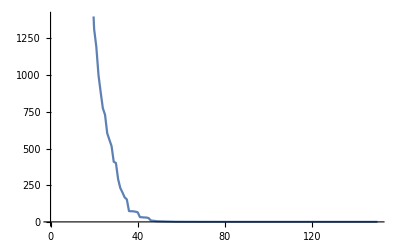
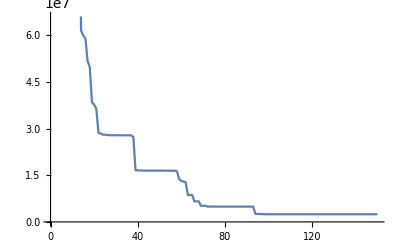
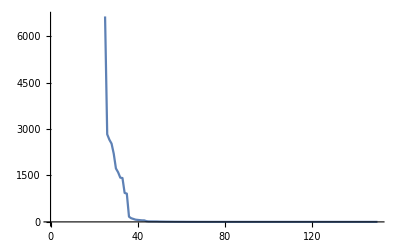
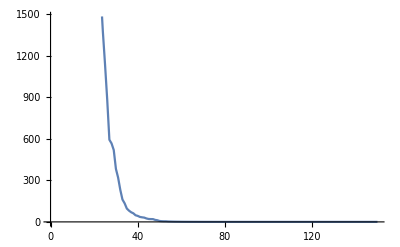
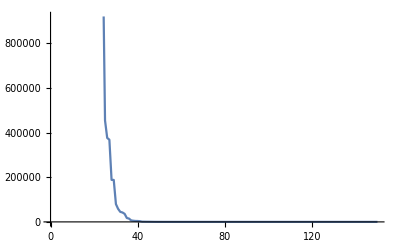
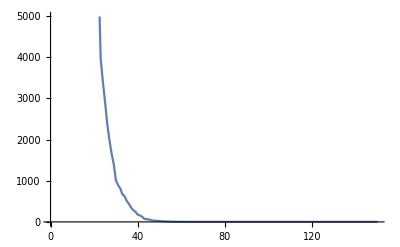
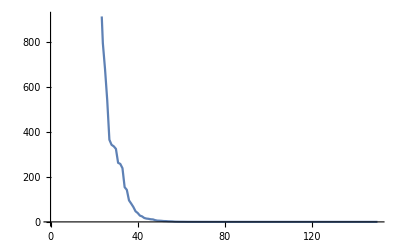
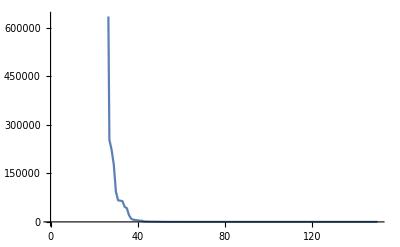
|  | sphere | SDP | SS
5D | GA | -Graphics- | -Graphics- | -Graphics-
 | DE | -Graphics- | -Graphics- | -Graphics-
 | jDE | -Graphics- | -Graphics- | -Graphics-
 | PSOA | -Graphics- | -Graphics- | -Graphics-
 | PSOB | -Graphics- | -Graphics- | -Graphics-
30D | GA | -Graphics- | -Graphics- | -Graphics-
 | DE | -Graphics- | -Graphics- | -Graphics-
 | jDE | -Graphics- | -Graphics- | -Graphics-
 | PSOA | -Graphics- | -Graphics- | -Graphics-
 | PSOB | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{{"","","sphere","SDP","SS"},{"5D","GA",gaSphere5d,gaSDP5d,gaSS5d},{"","DE",DESphere5d,DESDP5d,DESS5d},{"","jDE",jDESphere5d,jDESDP5d,jDESS5d},{"","PSOA",PSOASphere5d,PSOASDP5d,PSOASS5d},{"","PSOB",PSOBSphere5d,PSOBSDP5d,PSOBSS5d},{"30D","GA",gaSphere30d,gaSDP30d,gaSS30d},{"","DE",DESphere30d,DESDP30d,DESS30d},{"","jDE",jDESphere30d,jDESDP30d,jDESS30d},{"","PSOA",PSOASphere30d,PSOASDP30d,PSOASS30d},{"","PSOB",PSOBSphere30d,PSOBSDP30d,PSOBSS30d}}]
```